```mathematica
Clear[a,b,Γ,β,Da,Pe,PI,γ,Ef,niC,Va,Vb,ne,ni,φ,We,Ef,ni1,ni2,ni3,ne1,ne2,ne3,φ1,φ2,φ3,E1,E2,E3]
Clear[WE1,WE2,WE3,We1,We2,We3,H,X0,neC,weC,neA,weA]
TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->True,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]

b=1;
```

```mathematica
FullSimplify[DSolve[{nE1''[r]+1/r nE1'[r]+1== 0,nE1[a]==neA,nE1[b]==neC},nE1[r],r]]
```

```mathematica
{{nE1[r]->}}
```

```mathematica
{{nE1[r]->}}
```

```mathematica
{{nE1[r]->}}
```

```mathematica
ne1[r_]:=((1+4 neC-r^2) Log[a]+(-1+a^2+4 neA-4 neC) Log[r])/(4 Log[a])
```

```mathematica
FullSimplify[ ne1[a]]
                                              FullSimplify[ ne1'[b]]
```

0

0

```mathematica
FullSimplify[DSolve[{1/r nI1'[r]+nI1''[r]+β==0  ,nI1[a]==niC,nI1[b]==0},nI1[r],r]]
```

{{nI1[r]→((β-r^2 β) Log[a]+(4 niC+(-1+a^2) β) Log[r])/(4 Log[a])}}

```mathematica
{{nI1[r]->}}
```

```mathematica
ni1[r_]:=((β-r^2 β) Log[a]+(4 niC+(-1+a^2) β) Log[r])/(4 Log[a])
```

```mathematica
FullSimplify[ni1[a]]
FullSimplify[ni1'[b]]
```

niC

0

```mathematica
FullSimplify[DSolve[{1/r φi1'[r]+φi1''[r]==Γ(ne1[r]-ni1[r]) ,φi1[a]==0,φi1[b]==Vb},φi1[r],r]]
```

```mathematica
φ1[r_]:=1/(64 Log[a]^2)((64 Vb+(-1+r^2) (16 neC+(-3+r^2) (-1+β)) Γ) Log[a]^2-4 (-1+a^2) (1-4 neA+4 neC+4 niC+a^2 (-1+β)-β) Γ Log[r]+Log[a] (4 (-1+r^2) (1-4 neA+4 neC+4 niC+a^2 (-1+β)-β) Γ+(-64 Vb+(3+16 neC-4 r^2+3 a^4 (-1+β)-3 β+4 r^2 (4 neA-4 (neC+niC)+β)+4 a^2 (-4 neA+4 niC+r^2-r^2 β)) Γ) Log[r]))
```

```mathematica
E1[r_]:=-φ1'[r]
```

```mathematica
FullSimplify[φ1[a]]
FullSimplify[φ1[b]]
```

0

Vb

```mathematica
FullSimplify[DSolve[{5/3 WE1''[r]+5/3 1/r WE1'[r]-H== 0,WE1[a]==weA,WE1[b]==weC},WE1[r],r]]
```

```mathematica
{{WE1[r]->}}
```

```mathematica
We1[r_]:=((3 H (-1+r^2)+20 weC) Log[a]+(-3 (-1+a^2) H+20 (weA-weC)) Log[r])/(20 Log[a])
```

# 222222222222222222222222222222222222222222222222

```mathematica
Simplify[DSolve[{PI E1[r] ni1'[r]-1/r nI2'[r]== nI2''[r]-Γ PI ni1[r](ni1[r]-ne1[r])-β ne1[r],nI2[a]==0,nI2[b]==0},nI2[r],r]]
```

```mathematica
ni2[r_]:=1/(3072 Log[a]^3)(4 (-1+r^2) β (36-5 PI Γ+2 PI r^4 (-1+β) Γ+5 PI β Γ+24 neC (8+PI (-1+r^2) Γ)+r^2 (-12-7 PI (-1+β) Γ)) Log[a]^3+12 (-1+a^2) PI (1-4 neA+4 neC+4 niC+a^2 (-1+β)-β) Γ Log[r] (-12 niC+β-a^2 β+2 (4 niC+(-1+a^2) β) Log[r])-Log[a]^2 (-3 (-1+r^2) (4 niC PI (7+32 neC-r^2) Γ+(-1+a^2) PI (-11+6 a^2+7 r^2) β^2 Γ+β (64+256 neC-128 PI Vb-11 PI Γ-6 a^4 PI Γ-40 neC PI Γ-68 niC PI Γ+7 PI r^2 Γ+24 neC PI r^2 Γ+28 niC PI r^2 Γ+a^2 (-64+PI (17-32 neA+32 neC+32 niC-7 r^2) Γ)-8 neA (32+PI (-5+3 r^2) Γ)))+2 (192 a^2 niC^2 PI Γ+12 niC PI (64 Vb+(-3-16 neC+8 r^2+32 neC r^2-2 r^4+3 a^4 (-1+β)+3 β-16 r^2 β+6 r^4 β+4 a^2 (-4 neA+β)) Γ)+β (-72-384 neC+96 r^2-384 neA r^2+384 neC r^2-192 PI Vb+19 PI Γ+96 neC PI Γ-48 PI r^2 Γ+96 neA PI r^2 Γ-192 neC PI r^2 Γ+18 PI r^4 Γ-48 neA PI r^4 Γ+48 neC PI r^4 Γ+a^6 PI (-1+β) Γ-19 PI β Γ+48 PI r^2 β Γ-18 PI r^4 β Γ+9 a^4 (8+PI (-1+β) Γ)-3 a^2 (-6 PI r^4 (-1+β) Γ+16 neA (-8+PI Γ)+PI (-64 Vb+(3+16 neC-3 β) Γ)-16 r^2 (-2+PI (1+2 neC-β) Γ)))) Log[r])-3 Log[a] (-4 PI (-1+r^2) (1-4 neA+4 neC+4 niC+a^2 (-1+β)-β) (12 niC+(-1+a^2) β) Γ-(4 niC PI (15-15 a^4+64 neC+32 niC-24 r^2-96 neC r^2-96 niC r^2-8 a^2 (8 neA-4 neC-8 niC-3 r^2)+32 neA (-1+3 r^2)) Γ+(-1+a^2)^2 PI (19+3 a^2-24 r^2) β^2 Γ-(-1+a^2) β (64+256 neC-128 PI Vb-19 PI Γ+3 a^4 PI Γ-72 neC PI Γ-132 niC PI Γ+24 PI r^2 Γ+96 neC PI r^2 Γ+192 niC PI r^2 Γ+4 a^2 (-16+PI (4+2 neA-2 neC-17 niC-6 r^2) Γ)-8 neA (32+3 PI (-3+4 r^2) Γ))) Log[r]+2 PI (4 niC+(-1+a^2) β) (-64 Vb+(3+16 neC-8 r^2+32 neA r^2-32 neC r^2-32 niC r^2-8 a^2 (2 neA-2 niC+r^2 (-1+β))+3 a^4 (-1+β)-3 β+8 r^2 β) Γ) Log[r]^2))
```

```mathematica
FullSimplify[ni2[a]]
FullSimplify[ni2'[b]]
```

0

0

```mathematica
Simplify[DSolve[{-Pe E1[r] ne1'[r]-1/r nE2'[r]==nE2''[r]+Γ Pe ne1[r](ni1[r]-ne1[r])+ne1[r],nE2[a]==0,nE2[b]==0},nE2[r],r]]
```

```mathematica
ne2[r_]:=1/(3072 Log[a]^3)(4 (-1+r^2) (-36+5 Pe Γ+192 neC^2 Pe Γ-2 Pe r^4 (-1+β) Γ-5 Pe β Γ+12 neC (-16+Pe (5+r^2 (-3+β)-3 β) Γ)+r^2 (12+7 Pe (-1+β) Γ)) Log[a]^3-12 (-1+a^2) Pe (1-4 neA+4 neC+4 niC+a^2 (-1+β)-β) Γ Log[r] (1-a^2-12 neA+12 neC+2 (-1+a^2+4 neA-4 neC) Log[r])+Log[a]^2 (-3 (-1+r^2) (64+256 neC-128 Pe Vb-11 Pe Γ-132 neC Pe Γ-384 neC^2 Pe Γ-40 niC Pe Γ-256 neC niC Pe Γ+7 Pe r^2 Γ+28 neC Pe r^2 Γ+24 niC Pe r^2 Γ+6 a^4 Pe (-1+β) Γ+11 Pe β Γ+92 neC Pe β Γ-7 Pe r^2 β Γ-4 neC Pe r^2 β Γ+4 neA (-64+Pe (17+96 neC+r^2 (-7+β)-7 β) Γ)+a^2 (-64+Pe (17-32 neA+96 neC+32 niC-7 r^2-17 β-64 neC β+7 r^2 β) Γ))+2 (-72+96 r^2-384 neA r^2-192 Pe Vb+768 neA Pe Vb+19 Pe Γ-36 neA Pe Γ-48 Pe r^2 Γ+192 neA Pe r^2 Γ-96 niC Pe r^2 Γ+18 Pe r^4 Γ-72 neA Pe r^4 Γ+48 niC Pe r^4 Γ-192 neC^2 Pe (-3+4 r^2) Γ+a^6 Pe (-1+β) Γ-19 Pe β Γ+36 neA Pe β Γ+48 Pe r^2 β Γ-96 neA Pe r^2 β Γ-18 Pe r^4 β Γ+24 neA Pe r^4 β Γ+9 a^4 (8+(1+4 neA+4 neC) Pe (-1+β) Γ)-12 neC (32+64 Pe Vb+2 Pe r^4 (-3+β) Γ+Pe (-17+16 neA+9 β) Γ-16 r^2 (2+Pe (-2+4 neA-2 niC+β) Γ))-3 a^2 (64 neA^2 Pe Γ-6 Pe r^4 (-1+β) Γ+16 neA (-8+(1+4 neC-4 niC) Pe Γ)+16 r^2 (2+Pe (-1+2 neC (-2+β)+β) Γ)-Pe (64 Vb+(-3-16 neC+16 niC+64 neC niC+3 β) Γ))) Log[r])+3 Log[a] (-4 (-1+a^2+12 neA-12 neC) Pe (-1+r^2) (1-4 neA+4 neC+4 niC+a^2 (-1+β)-β) Γ-(64+256 neC-128 Pe Vb-19 Pe Γ-196 neC Pe Γ-512 neC^2 Pe Γ-72 niC Pe Γ-384 neC niC Pe Γ+24 Pe r^2 Γ+192 neC Pe r^2 Γ+384 neC^2 Pe r^2 Γ+96 niC Pe r^2 Γ+384 neC niC Pe r^2 Γ+128 neA^2 Pe (-1+3 r^2) Γ+3 a^6 Pe (-1+β) Γ+19 Pe β Γ+124 neC Pe β Γ-24 Pe r^2 β Γ-96 neC Pe r^2 β Γ-4 neA (64+Pe (-33-32 niC+48 r^2+96 niC r^2+32 neC (-5+6 r^2)+15 β-24 r^2 β) Γ)+a^4 (64+Pe (-13+8 niC+24 r^2+13 β-24 r^2 β+4 neC (1+β)+neA (-68+60 β)) Γ)+a^2 (-128+128 Pe Vb+35 Pe Γ-256 neA^2 Pe Γ+128 neC^2 Pe Γ+64 niC Pe Γ-48 Pe r^2 Γ-96 niC Pe r^2 Γ-35 Pe β Γ+48 Pe r^2 β Γ+32 neC (-8+Pe (6+3 r^2 (-2+β)-4 β) Γ)+32 neA (8+Pe (-2+4 neC+8 niC+6 r^2-3 r^2 β) Γ))) Log[r]+2 (-1+a^2+4 neA-4 neC) Pe (-64 Vb+(3+16 neC-8 r^2+32 neA r^2-32 neC r^2-32 niC r^2-8 a^2 (2 neA-2 niC+r^2 (-1+β))+3 a^4 (-1+β)-3 β+8 r^2 β) Γ) Log[r]^2))
```

```mathematica
FullSimplify[ne2[a]]
```

0

```mathematica
Clear[φi2,φ2]
Simplify[DSolve[{1/r φi2'[r]+φi2''[r]==Γ(ne2[r]-ni2[r]) ,φi2[a]==0,φi2[b]==0},φi2[r],r]]
```

```mathematica
φ2[r_]:=1/(221184 Log[a]^4)Γ (3 (-1+r^2) (608+608 β-69 Pe Γ+1152 neC^2 Pe (-3+r^2) Γ+69 Pe β Γ-69 PI β Γ+69 PI β^2 Γ-3 r^6 (-1+β) (Pe+PI β) Γ-r^2 (256-51 Pe Γ+51 PI β^2 Γ+β (256+51 Pe Γ-51 PI Γ))+r^4 (32-21 Pe Γ+21 PI β^2 Γ+β (32+21 Pe Γ-21 PI Γ))+32 neC (108-30 Pe Γ+r^4 (Pe (-3+β)-2 PI β) Γ+β (108+19 Pe Γ-11 PI Γ)+r^2 (-36+15 Pe Γ+β (-36-8 Pe Γ+7 PI Γ)))) Log[a]^4+864 (-1+a^2)^2 (1-4 neA+4 neC+4 niC+a^2 (-1+β)-β) ((-1+a^2+6 neA-6 neC) Pe+6 niC PI+(-1+a^2) PI β) Γ Log[r]-Log[a]^3 ((-1+r^2) (-4752+8640 neA-22464 neC+1296 r^2-5184 neA r^2+5184 neC r^2-1728 Pe Vb+27648 neA Pe Vb-27648 neC Pe Vb+27648 niC PI Vb-1728 Pe r^2 Vb-4752 β+8640 neA β-22464 neC β+1296 r^2 β-5184 neA r^2 β+5184 neC r^2 β-1728 PI Vb β-1728 PI r^2 Vb β+885 Pe Γ-3072 neA Pe Γ+10848 neC Pe Γ-19008 neA neC Pe Γ+32832 neC^2 Pe Γ+1072 niC Pe Γ+8640 neC niC Pe Γ-2000 niC PI Γ-10368 neC niC PI Γ-393 Pe r^2 Γ+1896 neA Pe r^2 Γ-3624 neC Pe r^2 Γ+8640 neA neC Pe r^2 Γ-8640 neC^2 Pe r^2 Γ-1088 niC Pe r^2 Γ-5184 neC niC Pe r^2 Γ+808 niC PI r^2 Γ+3456 neC niC PI r^2 Γ+66 Pe r^4 Γ-264 neA Pe r^4 Γ+264 neC Pe r^4 Γ+208 niC Pe r^4 Γ-56 niC PI r^4 Γ-885 Pe β Γ+2000 neA Pe β Γ-6752 neC Pe β Γ+885 PI β Γ-1072 neA PI β Γ+4096 neC PI β Γ+3072 niC PI β Γ+393 Pe r^2 β Γ-808 neA Pe r^2 β Γ+2104 neC Pe r^2 β Γ-393 PI r^2 β Γ+1088 neA PI r^2 β Γ-1520 neC PI r^2 β Γ-1896 niC PI r^2 β Γ-66 Pe r^4 β Γ+56 neA Pe r^4 β Γ-56 neC Pe r^4 β Γ+66 PI r^4 β Γ-208 neA PI r^4 β Γ+208 neC PI r^4 β Γ+264 niC PI r^4 β Γ-885 PI β^2 Γ+393 PI r^2 β^2 Γ-66 PI r^4 β^2 Γ+36 a^6 (-1+β) (Pe+PI β) Γ+81 a^4 (32-16 niC PI Γ-Pe (1+16 neA+16 neC+r^2) Γ+PI (1+r^2) β^2 Γ+β (32+PI (-1+16 niC-r^2) Γ+Pe (1+16 neA+16 neC+r^2) Γ))-6 a^2 (1152 neA^2 Pe Γ-11 r^4 (-1+β) (Pe+PI β) Γ+r^2 (216-(79+360 neC+72 niC) Pe Γ+79 PI β^2 Γ+β (216+(79+216 neC) Pe Γ-(79+144 neC+72 niC) PI Γ))+72 neA (Pe (1+16 neC-16 niC+r^2) Γ+16 (-2+niC PI Γ)+β (-32+PI (1+r^2) Γ))-8 (16 PI β^2 Γ+9 (5+16 niC^2 PI Γ)+β (45+144 PI Vb+(-16-54 neC+9 niC) PI Γ)+Pe (144 Vb+(-16+9 niC+16 β+9 neC (-11+16 niC+5 β)) Γ))))+3 (-608+864 r^2-288 r^4+1152 neA r^4+2304 Pe r^2 Vb-9216 neA Pe r^2 Vb-9216 niC PI r^2 Vb-608 β+864 r^2 β-288 r^4 β+1152 neA r^4 β+2304 PI r^2 Vb β+69 Pe Γ-228 Pe r^2 Γ+432 neA Pe r^2 Γ+432 niC PI r^2 Γ+144 Pe r^4 Γ-576 neA Pe r^4 Γ+288 niC Pe r^4 Γ-288 niC PI r^4 Γ-24 Pe r^6 Γ+96 neA Pe r^6 Γ-64 niC Pe r^6 Γ+32 niC PI r^6 Γ+1152 neC^2 Pe (3-6 r^2+2 r^4) Γ-69 Pe β Γ+69 PI β Γ+228 Pe r^2 β Γ-432 neA Pe r^2 β Γ-228 PI r^2 β Γ-432 niC PI r^2 β Γ-144 Pe r^4 β Γ+288 neA Pe r^4 β Γ+144 PI r^4 β Γ-288 neA PI r^4 β Γ+576 niC PI r^4 β Γ+24 Pe r^6 β Γ-32 neA Pe r^6 β Γ-24 PI r^6 β Γ+64 neA PI r^6 β Γ-96 niC PI r^6 β Γ-69 PI β^2 Γ+228 PI r^2 β^2 Γ-144 PI r^4 β^2 Γ+24 PI r^6 β^2 Γ+69 a^8 (-1+β) (Pe+PI β) Γ-4 a^6 (-152+240 neA Pe Γ-88 niC Pe Γ+152 niC PI Γ-3 Pe r^2 Γ+3 PI r^2 β^2 Γ-β (152+8 neA (19 Pe-11 PI) Γ+240 niC PI Γ-3 Pe r^2 Γ+3 PI r^2 Γ))+16 neC (-216-216 β+60 Pe Γ-38 Pe β Γ+22 PI β Γ+2 r^6 (Pe (-3+β)-2 PI β) Γ-36 r^4 (2+2 (-1+2 neA-niC) Pe Γ+2 niC PI Γ+β (2+Pe Γ-PI Γ))+9 r^2 (32+64 Pe Vb+16 niC PI Γ+Pe (-17+16 neA+9 β) Γ-8 β (-4+PI Γ)))+12 a^2 r^2 (192 neA^2 Pe Γ-2 r^4 (-1+β) (Pe+PI β) Γ-3 (64 Pe Vb+64 PI Vb β+Pe (-3+16 niC+16 neC (-1+4 niC)+3 β) Γ+PI (64 niC^2+16 niC β+β (-3-16 neC+3 β)) Γ)+48 neA (-8+(1+4 neC-4 niC) Pe Γ+4 niC PI Γ+β (-8+PI Γ))+12 r^2 (2+PI β^2 Γ-Pe (Γ+4 neC Γ)+β (2+Pe (Γ+2 neC Γ)-PI (Γ+2 neC Γ))))-108 a^4 (32 neA^2 Pe Γ-32 niC^2 PI Γ-4 neA (8+8 niC (Pe-PI) Γ+Pe r^2 Γ+β (8-Pe r^2 Γ))+r^2 (8-4 niC PI Γ+PI β^2 Γ-Pe (Γ+4 neC Γ)+β (8+(-1+4 niC) PI Γ+Pe (Γ+4 neC Γ))))) Log[r])-27 (-1+a^2) Log[a] (32 (-1+r^2) (1-4 neA+4 neC+4 niC+a^2 (-1+β)-β) ((-1+a^2+6 neA-6 neC) Pe+6 niC PI+(-1+a^2) PI β) Γ+(128-512 neA+512 neC+128 Pe Vb-1536 neA Pe Vb+1536 neC Pe Vb-1536 niC PI Vb+128 β-512 neA β+512 neC β+128 PI Vb β-53 Pe Γ+360 neA Pe Γ-400 neA^2 Pe Γ-584 neC Pe Γ+1952 neA neC Pe Γ-1552 neC^2 Pe Γ-132 niC Pe Γ+400 neA niC Pe Γ-912 neC niC Pe Γ+228 niC PI Γ-400 neA niC PI Γ+1040 neC niC PI Γ+400 niC^2 PI Γ+40 Pe r^2 Γ-384 neA Pe r^2 Γ+896 neA^2 Pe r^2 Γ+384 neC Pe r^2 Γ-1792 neA neC Pe r^2 Γ+896 neC^2 Pe r^2 Γ+160 niC Pe r^2 Γ-896 neA niC Pe r^2 Γ+896 neC niC Pe r^2 Γ-224 niC PI r^2 Γ+896 neA niC PI r^2 Γ-896 neC niC PI r^2 Γ-896 niC^2 PI r^2 Γ+53 Pe β Γ-228 neA Pe β Γ+356 neC Pe β Γ-53 PI β Γ+132 neA PI β Γ-228 neC PI β Γ-360 niC PI β Γ-40 Pe r^2 β Γ+224 neA Pe r^2 β Γ-224 neC Pe r^2 β Γ+40 PI r^2 β Γ-160 neA PI r^2 β Γ+160 neC PI r^2 β Γ+384 niC PI r^2 β Γ+53 PI β^2 Γ-40 PI r^2 β^2 Γ+53 a^6 (-1+β) (Pe+PI β) Γ+a^4 (128-356 niC PI Γ+Pe (53-584 neA+360 neC+228 niC+40 r^2) Γ-PI (53+40 r^2) β^2 Γ+β (128+Pe (-53+356 neA-228 neC-40 r^2) Γ+PI (53-228 neA+132 neC+584 niC+40 r^2) Γ))-a^2 (256+128 Pe Vb+256 β+128 PI Vb β-53 Pe Γ+1552 neA^2 Pe Γ+400 neC^2 Pe Γ+96 niC Pe Γ-128 niC PI Γ-1552 niC^2 PI Γ+80 Pe r^2 Γ+160 niC Pe r^2 Γ-224 niC PI r^2 Γ+53 Pe β Γ-53 PI β Γ+224 niC PI β Γ-80 Pe r^2 β Γ+80 PI r^2 β Γ+384 niC PI r^2 β Γ+53 PI β^2 Γ-80 PI r^2 β^2 Γ-16 neC (-32+57 niC PI Γ+Pe (14-65 niC-24 r^2) Γ+2 β (-16+PI (3-5 r^2) Γ+Pe (-4+7 r^2) Γ))+16 neA (-32+97 niC PI Γ-Pe (14+122 neC+97 niC+24 r^2) Γ+2 β (-16-PI (3+5 r^2) Γ+Pe (4+7 r^2) Γ)))) Log[r]+16 r^2 (1-4 neA+4 neC+4 niC+a^2 (-1+β)-β) ((-1+a^2+4 neA-4 neC) Pe+4 niC PI+(-1+a^2) PI β) Γ Log[r]^2)+Log[a]^2 (27 (-1+r^2) (128+512 neC+128 Pe Vb+1536 neC Pe Vb-1536 niC PI Vb+128 β+512 neC β+128 PI Vb β-53 Pe Γ-584 neC Pe Γ-1552 neC^2 Pe Γ-132 niC Pe Γ-912 neC niC Pe Γ+228 niC PI Γ+1040 neC niC PI Γ+400 niC^2 PI Γ+11 Pe r^2 Γ+104 neC Pe r^2 Γ+240 neC^2 Pe r^2 Γ+44 niC Pe r^2 Γ+240 neC niC Pe r^2 Γ-60 niC PI r^2 Γ-240 neC niC PI r^2 Γ-240 niC^2 PI r^2 Γ+80 neA^2 Pe (-5+3 r^2) Γ+53 Pe β Γ+356 neC Pe β Γ-53 PI β Γ-228 neC PI β Γ-360 niC PI β Γ-11 Pe r^2 β Γ-60 neC Pe r^2 β Γ+11 PI r^2 β Γ+44 neC PI r^2 β Γ+104 niC PI r^2 β Γ+53 PI β^2 Γ-11 PI r^2 β^2 Γ+24 a^6 (-1+β) (Pe+PI β) Γ-4 neA (128+384 Pe Vb+128 β+100 niC PI Γ-60 niC PI r^2 Γ+11 PI (-3+r^2) β Γ+Pe (-90+26 r^2+20 niC (-5+3 r^2)+8 neC (-61+15 r^2)+57 β-15 r^2 β) Γ)+a^4 (Pe (-5-304 neA+80 neC+112 niC+11 r^2) Γ+PI (5-11 r^2) β^2 Γ+64 (2-3 niC PI Γ)+β (128+Pe (5+192 neA-64 neC-11 r^2) Γ+PI (-5-112 neA+16 neC+304 niC+11 r^2) Γ))-2 a^2 (128+64 Pe Vb+128 β+64 PI Vb β-41 Pe Γ+448 neA^2 Pe Γ-128 neC^2 Pe Γ-10 niC Pe Γ+18 niC PI Γ-448 niC^2 PI Γ+11 Pe r^2 Γ+22 niC Pe r^2 Γ-30 niC PI r^2 Γ+41 Pe β Γ-41 PI β Γ-28 niC PI β Γ-11 Pe r^2 β Γ+11 PI r^2 β Γ+52 niC PI r^2 β Γ+41 PI β^2 Γ-11 PI r^2 β^2 Γ+2 neC β (128+Pe (73-15 r^2) Γ+PI (-53+11 r^2) Γ)+4 neC (64-32 niC PI Γ+Pe (-63+48 niC+13 r^2) Γ)+2 neA (β (-128+PI (5-11 r^2) Γ+3 Pe (-3+5 r^2) Γ)-2 (64-112 niC PI Γ+Pe (-7+80 neC+112 niC+13 r^2) Γ))))+(4752-8640 neA+22464 neC-3456 r^2+13824 neA r^2-13824 neC r^2+1728 Pe Vb-27648 neA Pe Vb+27648 neC Pe Vb-27648 niC PI Vb-6912 Pe r^2 Vb+55296 neA Pe r^2 Vb-55296 neC Pe r^2 Vb+55296 niC PI r^2 Vb+4752 β-8640 neA β+22464 neC β-3456 r^2 β+13824 neA r^2 β-13824 neC r^2 β+1728 PI Vb β-6912 PI r^2 Vb β-885 Pe Γ+3072 neA Pe Γ-10848 neC Pe Γ+19008 neA neC Pe Γ-32832 neC^2 Pe Γ-1072 niC Pe Γ-8640 neC niC Pe Γ+2000 niC PI Γ+10368 neC niC PI Γ+1674 Pe r^2 Γ-9720 neA Pe r^2 Γ+6912 neA^2 Pe r^2 Γ+16632 neC Pe r^2 Γ-48384 neA neC Pe r^2 Γ+41472 neC^2 Pe r^2 Γ+3888 niC Pe r^2 Γ-6912 neA niC Pe r^2 Γ+20736 neC niC Pe r^2 Γ-5832 niC PI r^2 Γ+6912 neA niC PI r^2 Γ-27648 neC niC PI r^2 Γ-6912 niC^2 PI r^2 Γ-540 Pe r^4 Γ+4320 neA Pe r^4 Γ-8640 neA^2 Pe r^4 Γ-4320 neC Pe r^4 Γ+17280 neA neC Pe r^4 Γ-8640 neC^2 Pe r^4 Γ-2160 niC Pe r^4 Γ+8640 neA niC Pe r^4 Γ-8640 neC niC Pe r^4 Γ+2160 niC PI r^4 Γ-8640 neA niC PI r^4 Γ+8640 neC niC PI r^4 Γ+8640 niC^2 PI r^4 Γ+885 Pe β Γ-2000 neA Pe β Γ+6752 neC Pe β Γ-885 PI β Γ+1072 neA PI β Γ-4096 neC PI β Γ-3072 niC PI β Γ-1674 Pe r^2 β Γ+5832 neA Pe r^2 β Γ-9288 neC Pe r^2 β Γ+1674 PI r^2 β Γ-3888 neA PI r^2 β Γ+7344 neC PI r^2 β Γ+9720 niC PI r^2 β Γ+540 Pe r^4 β Γ-2160 neA Pe r^4 β Γ+2160 neC Pe r^4 β Γ-540 PI r^4 β Γ+2160 neA PI r^4 β Γ-2160 neC PI r^4 β Γ-4320 niC PI r^4 β Γ+885 PI β^2 Γ-1674 PI r^2 β^2 Γ+540 PI r^4 β^2 Γ+885 a^8 (-1+β) (Pe+PI β) Γ+2 a^6 (2376-3376 niC PI Γ+Pe (402-5424 neA+1536 neC+2048 niC+405 r^2) Γ-3 PI (134+135 r^2) β^2 Γ+β (2376+Pe (-402+3376 neA-1000 neC-405 r^2) Γ+PI (402-2048 neA+536 neC+5424 niC+405 r^2) Γ))-54 a^4 (88+64 r^2+32 Pe Vb+88 β+64 r^2 β+32 PI Vb β-3 Pe Γ+608 neA^2 Pe Γ+48 niC Pe Γ-64 niC PI Γ-608 niC^2 PI Γ-Pe r^2 Γ+72 niC Pe r^2 Γ-108 niC PI r^2 Γ+10 Pe r^4 Γ+3 Pe β Γ-3 PI β Γ+112 niC PI β Γ+Pe r^2 β Γ-PI r^2 β Γ+180 niC PI r^2 β Γ-10 Pe r^4 β Γ+10 PI r^4 β Γ+3 PI β^2 Γ+PI r^2 β^2 Γ-10 PI r^4 β^2 Γ+4 neA (-Pe (28+88 neC+152 niC+45 r^2) Γ+Pe (16+27 r^2) β Γ+8 (-13+19 niC PI Γ)-2 β (52+3 PI (2+3 r^2) Γ))-4 neC (Pe (8-48 niC-13 r^2) Γ+40 (-1+niC PI Γ)+β (-40-2 PI (-1+r^2) Γ+Pe (-6+11 r^2) Γ)))+6 a^2 (-792+1152 r^2-4608 niC PI Vb+1152 Pe r^2 Vb-792 β+1152 r^2 β+1152 PI r^2 Vb β+134 Pe Γ-72 niC Pe Γ+216 niC PI Γ-1152 niC^2 PI Γ-423 Pe r^2 Γ-4608 niC^2 PI r^2 Γ+180 Pe r^4 Γ+360 niC Pe r^4 Γ-360 niC PI r^4 Γ-1152 neC^2 Pe (-1+r^2) Γ+1152 neA^2 Pe (1+4 r^2) Γ-134 Pe β Γ+134 PI β Γ-288 niC PI β Γ+423 Pe r^2 β Γ-423 PI r^2 β Γ-180 Pe r^4 β Γ+180 PI r^4 β Γ+720 niC PI r^4 β Γ-134 PI β^2 Γ+423 PI r^2 β^2 Γ-180 PI r^4 β^2 Γ+72 neA (-32-64 Pe Vb-32 β+16 niC PI Γ+Pe (4+32 neC-16 niC-3 β) Γ+PI β Γ+5 r^4 (Pe (-2+β)-PI β) Γ-16 r^2 (2+2 β+3 neC Pe Γ+4 niC Pe Γ-4 niC PI Γ))-72 neC (5 r^4 (Pe (-2+β)-PI β) Γ+2 (16-32 Pe Vb+16 β-8 niC PI Γ-3 PI β Γ+Pe (-7+8 niC+4 β) Γ)-16 r^2 (2+2 (-1+niC) Pe Γ-niC PI Γ+β (2+Pe Γ-PI Γ))))) Log[r]-108 r^2 ((-1+a^2+4 neA-4 neC) Pe+4 niC PI+(-1+a^2) PI β) (64 Vb+(-3-16 neC+2 r^2-8 neA r^2+8 neC r^2+8 niC r^2+2 a^2 (8 neA-8 niC+r^2 (-1+β))-3 a^4 (-1+β)+3 β-2 r^2 β) Γ) Log[r]^2))
```

```mathematica
E2[r_]:=-φ2'[r]
```

```mathematica
Simplify[DSolve[{-5/3 Pe E1[r] We1'[r]==5/3 WE2''[r]+5/3 1/r WE2'[r]+5/3 Γ Pe We1[r](ni1[r]-ne1[r])+X0 ne1'[r]E1[r]-H ne1[r],WE2[a]==0,WE2[b]==0},WE2[r],r]]
```

```mathematica
We2[r_]:=1/(15360 Log[a]^3)(4 (-1+r^2) ((60 Pe weC (16 neC+(-3+r^2) (-1+β))-X0 (36 neC (1+r^2)+(-7-7 r^2+2 r^4) (-1+β))) Γ+3 H (36-5 Pe Γ+2 Pe r^4 (-1+β) Γ+5 Pe β Γ+24 neC (8+Pe (-1+r^2) Γ)+r^2 (-12-7 Pe (-1+β) Γ))) Log[a]^3+12 (-1+a^2) (1-4 neA+4 neC+4 niC+a^2 (-1+β)-β) Γ Log[r] (3 (H (Pe-a^2 Pe)+20 Pe (weA-weC)+(5-5 a^2-12 neA+12 neC) X0)+(6 (-1+a^2) H Pe-40 Pe (weA-weC)-6 (-1+a^2+4 neA-4 neC) X0) Log[r])+Log[a]^2 (3 (-1+r^2) (384 Vb X0-20 Pe (weA (32 neC+(-7+r^2) (-1+β))+weC (-23+64 neA-96 neC-64 niC+r^2-16 a^2 (-1+β)+23 β-r^2 β)) Γ-3 X0 (17+108 neC+128 neC^2+16 niC+3 r^2+12 neC r^2+16 niC r^2+6 a^4 (-1+β)-17 β-28 neC β-3 r^2 β+4 neC r^2 β+a^2 (-11-32 neA-32 neC+32 niC-3 r^2+11 β+3 r^2 β)-4 neA (11+32 neC-7 β+r^2 (3+β))) Γ+3 H (64+256 neC-128 Pe Vb-11 Pe Γ-40 neC Pe Γ-40 niC Pe Γ+7 Pe r^2 Γ+24 neC Pe r^2 Γ+24 niC Pe r^2 Γ+6 a^4 Pe (-1+β) Γ+11 Pe β Γ-7 Pe r^2 β Γ-8 neA (32+Pe (-5+3 r^2) Γ)+a^2 (-64+Pe (17-32 neA+32 neC+32 niC-7 r^2-17 β+7 r^2 β) Γ)))-2 (-60 Pe (64 Vb (weA-weC)+weA (-16 a^2 (neA-niC)+16 neC (-1+2 r^2)+3 a^4 (-1+β)+(3-8 r^2+2 r^4) (-1+β)) Γ+weC (9+48 neC-16 r^2+32 neA r^2-64 neC r^2-32 niC r^2+2 r^4-8 a^2 (2 neA-2 niC+r^2 (-1+β))+3 a^4 (-1+β)-9 β+16 r^2 β-2 r^4 β) Γ)+X0 (-576 (-1+a^2+4 neA-4 neC) Vb+(-13-180 neC-576 neC^2-18 r^4-72 neC r^4-72 niC r^4+36 neA (3+16 neC+2 r^4-3 β)+41 a^6 (-1+β)+13 β+108 neC β+18 r^4 β+27 a^4 (1+4 neC+8 niC+4 neA (-3+β)-β-4 neC β)-9 a^2 (-3+64 neA^2-16 neC+16 niC+64 neC niC-16 neA (1+4 neC+4 niC)-2 r^4+3 β+2 r^4 β)) Γ)+3 H (-72-384 neC+96 r^2-384 neA r^2+384 neC r^2-192 Pe Vb+19 Pe Γ+96 neC Pe Γ-48 Pe r^2 Γ+96 neA Pe r^2 Γ-192 neC Pe r^2 Γ-96 niC Pe r^2 Γ+18 Pe r^4 Γ-48 neA Pe r^4 Γ+48 neC Pe r^4 Γ+48 niC Pe r^4 Γ+a^6 Pe (-1+β) Γ-19 Pe β Γ+48 Pe r^2 β Γ-18 Pe r^4 β Γ+9 a^4 (8+Pe (-1+β) Γ)+3 a^2 (6 Pe r^4 (-1+β) Γ-16 neA (-8+Pe Γ)+16 r^2 (-2+Pe (1+2 neC-β) Γ)+Pe (64 Vb+(-3-16 neC+16 niC+3 β) Γ)))) Log[r])-3 Log[a] (-12 (-1+r^2) ((-1+a^2) H Pe-20 Pe (weA-weC)+(-5+5 a^2+12 neA-12 neC) X0) (1-4 neA+4 neC+4 niC+a^2 (-1+β)-β) Γ+(384 (-1+a^2) Vb X0-3 X0 (-9-44 neC+16 niC+128 neC niC+8 r^2+64 neC r^2+128 neC^2 r^2+32 niC r^2+128 neC niC r^2+128 neA^2 (1+r^2)+25 a^6 (-1+β)+9 β-4 neC β-8 r^2 β-32 neC r^2 β-4 neA (5+16 r^2+32 niC (1+r^2)+32 neC (1+2 r^2)-β-8 r^2 β)+a^4 (41+112 niC+8 r^2-41 β-8 r^2 β-12 neC (-9+5 β)+4 neA (-43+15 β))-a^2 (7+256 neA^2+128 neC^2+128 niC+16 r^2+32 niC r^2+32 neC (2+8 niC-r^2 (-2+β)-2 β)-7 β-16 r^2 β-32 neA (6+12 neC+8 niC+2 r^2-2 β-r^2 β))) Γ+20 Pe (weC (-31-128 neC-96 niC+24 r^2+96 neC r^2+96 niC r^2-96 neA (-1+r^2)+8 a^2 (4 neC+(-4+3 r^2) (-1+β))+a^4 (-1+β)+31 β-24 r^2 β)+weA (15+64 neC+32 niC-24 r^2-96 neC r^2-96 niC r^2+32 neA (-1+3 r^2)+15 a^4 (-1+β)-15 β+24 r^2 β-8 a^2 (8 neA-4 neC-8 niC-3 r^2+3 r^2 β))) Γ-3 (-1+a^2) H (-64-256 neC+128 Pe Vb+19 Pe Γ+72 neC Pe Γ+72 niC Pe Γ-24 Pe r^2 Γ-96 neC Pe r^2 Γ-96 niC Pe r^2 Γ+3 a^4 Pe (-1+β) Γ-19 Pe β Γ+24 Pe r^2 β Γ+8 neA (32+3 Pe (-3+4 r^2) Γ)-8 a^2 (-8+Pe (2+neA-neC-niC-3 r^2-2 β+3 r^2 β) Γ))) Log[r]-2 (3 (-1+a^2+4 neA-4 neC) X0 (-64 Vb+(3+16 neC-16 a^2 (neA-niC)+3 a^4 (-1+β)-3 β) Γ)+3 (-1+a^2) H Pe (64 Vb+(-3-16 neC+8 r^2-32 neA r^2+32 neC r^2+32 niC r^2+8 a^2 (2 neA-2 niC+r^2 (-1+β))-3 a^4 (-1+β)+3 β-8 r^2 β) Γ)-20 Pe (weA-weC) (64 Vb+(-3-16 neC+8 r^2-32 neA r^2+32 neC r^2+32 niC r^2+8 a^2 (2 neA-2 niC+r^2 (-1+β))-3 a^4 (-1+β)+3 β-8 r^2 β) Γ)) Log[r]^2))
```

```mathematica
FullSimplify[φ2[a]]
FullSimplify[φ2[b]]
```

0

0

```mathematica
DSolve[{PI(E1[r]ni2'[r]+E2[r]ni1'[r])-1/r nI3'[r]==nI3''[r]-Γ PI (ni1[r](ni2[r]-ne2[r])+ni2[r](ni1[r]-ne1[r]))+β ne2[r], nI3[a]==0,nI3[b]==0 },nI3[r],r]
```

```mathematica
ni3[r_]:=-(PI r^10 (-1+β) β (Pe-2 PI+3 PI β) Γ^2)/122880+1/(1179648 Log[a])r^8 Γ (-36 niC PI^2 Γ-54 Pe PI β Γ+54 a^2 Pe PI β Γ+216 neA Pe PI β Γ-216 neC Pe PI β Γ-176 niC Pe PI β Γ+87 PI^2 β Γ-87 a^2 PI^2 β Γ-312 neA PI^2 β Γ+312 neC PI^2 β Γ+424 niC PI^2 β Γ+54 Pe PI β^2 Γ-54 a^2 Pe PI β^2 Γ-40 neA Pe PI β^2 Γ+40 neC Pe PI β^2 Γ-228 PI^2 β^2 Γ+228 a^2 PI^2 β^2 Γ+488 neA PI^2 β^2 Γ-488 neC PI^2 β^2 Γ-564 niC PI^2 β^2 Γ+141 PI^2 β^3 Γ-141 a^2 PI^2 β^3 Γ-48 Pe β Log[a]-48 PI β Log[a]+48 Pe β^2 Log[a]+240 PI β^2 Log[a]-84 Pe PI β Γ Log[a]-288 neC Pe PI β Γ Log[a]+156 PI^2 β Γ Log[a]+480 neC PI^2 β Γ Log[a]+84 Pe PI β^2 Γ Log[a]+96 neC Pe PI β^2 Γ Log[a]-396 PI^2 β^2 Γ Log[a]-672 neC PI^2 β^2 Γ Log[a]+240 PI^2 β^3 Γ Log[a])-1/(884736 Log[a]^2)r^6 (-468 niC PI^2 Γ^2+468 a^2 niC PI^2 Γ^2+1872 neA niC PI^2 Γ^2-1872 neC niC PI^2 Γ^2-1872 niC^2 PI^2 Γ^2-108 Pe PI β Γ^2+216 a^2 Pe PI β Γ^2-108 a^4 Pe PI β Γ^2+1152 neA Pe PI β Γ^2-1152 a^2 neA Pe PI β Γ^2-2880 neA^2 Pe PI β Γ^2-1152 neC Pe PI β Γ^2+1152 a^2 neC Pe PI β Γ^2+5760 neA neC Pe PI β Γ^2-2880 neC^2 Pe PI β Γ^2-432 niC Pe PI β Γ^2+432 a^2 niC Pe PI β Γ^2+2880 neA niC Pe PI β Γ^2-2880 neC niC Pe PI β Γ^2+75 PI^2 β Γ^2-150 a^2 PI^2 β Γ^2+75 a^4 PI^2 β Γ^2-516 neA PI^2 β Γ^2+516 a^2 neA PI^2 β Γ^2+864 neA^2 PI^2 β Γ^2+516 neC PI^2 β Γ^2-516 a^2 neC PI^2 β Γ^2-1728 neA neC PI^2 β Γ^2+864 neC^2 PI^2 β Γ^2+2172 niC PI^2 β Γ^2-2172 a^2 niC PI^2 β Γ^2-6480 neA niC PI^2 β Γ^2+6480 neC niC PI^2 β Γ^2+5616 niC^2 PI^2 β Γ^2+108 Pe PI β^2 Γ^2-216 a^2 Pe PI β^2 Γ^2+108 a^4 Pe PI β^2 Γ^2-720 neA Pe PI β^2 Γ^2+720 a^2 neA Pe PI β^2 Γ^2+720 neC Pe PI β^2 Γ^2-720 a^2 neC Pe PI β^2 Γ^2-258 PI^2 β^2 Γ^2+516 a^2 PI^2 β^2 Γ^2-258 a^4 PI^2 β^2 Γ^2+948 neA PI^2 β^2 Γ^2-948 a^2 neA PI^2 β^2 Γ^2-948 neC PI^2 β^2 Γ^2+948 a^2 neC PI^2 β^2 Γ^2-2136 niC PI^2 β^2 Γ^2+2136 a^2 niC PI^2 β^2 Γ^2+183 PI^2 β^3 Γ^2-366 a^2 PI^2 β^3 Γ^2+183 a^4 PI^2 β^3 Γ^2-216 Pe β Γ Log[a]+216 a^2 Pe β Γ Log[a]+864 neA Pe β Γ Log[a]-864 neC Pe β Γ Log[a]-704 niC Pe β Γ Log[a]-576 niC PI β Γ Log[a]-1152 Pe PI Vb β Γ Log[a]+1536 PI^2 Vb β Γ Log[a]+216 Pe β^2 Γ Log[a]-216 a^2 Pe β^2 Γ Log[a]-160 neA Pe β^2 Γ Log[a]+160 neC Pe β^2 Γ Log[a]+1440 PI β^2 Γ Log[a]-1440 a^2 PI β^2 Γ Log[a]-5184 neA PI β^2 Γ Log[a]+5184 neC PI β^2 Γ Log[a]-2688 PI^2 Vb β^2 Γ Log[a]-360 niC PI^2 Γ^2 Log[a]-1440 neC niC PI^2 Γ^2 Log[a]-288 Pe PI β Γ^2 Log[a]+342 a^2 Pe PI β Γ^2 Log[a]-54 a^4 Pe PI β Γ^2 Log[a]+1368 neA Pe PI β Γ^2 Log[a]-288 a^2 neA Pe PI β Γ^2 Log[a]-2232 neC Pe PI β Γ^2 Log[a]+1152 a^2 neC Pe PI β Γ^2 Log[a]+4608 neA neC Pe PI β Γ^2 Log[a]-4608 neC^2 Pe PI β Γ^2 Log[a]-896 niC Pe PI β Γ^2 Log[a]+288 a^2 niC Pe PI β Γ^2 Log[a]-2880 neC niC Pe PI β Γ^2 Log[a]+378 PI^2 β Γ^2 Log[a]-450 a^2 PI^2 β Γ^2 Log[a]+72 a^4 PI^2 β Γ^2 Log[a]-1440 neA PI^2 β Γ^2 Log[a]+384 a^2 neA PI^2 β Γ^2 Log[a]+2136 neC PI^2 β Γ^2 Log[a]-1080 a^2 neC PI^2 β Γ^2 Log[a]-2880 neA neC PI^2 β Γ^2 Log[a]+2880 neC^2 PI^2 β Γ^2 Log[a]+2632 niC PI^2 β Γ^2 Log[a]-384 a^2 niC PI^2 β Γ^2 Log[a]+6048 neC niC PI^2 β Γ^2 Log[a]+288 Pe PI β^2 Γ^2 Log[a]-342 a^2 Pe PI β^2 Γ^2 Log[a]+54 a^4 Pe PI β^2 Γ^2 Log[a]-472 neA Pe PI β^2 Γ^2 Log[a]+1192 neC Pe PI β^2 Γ^2 Log[a]-720 a^2 neC Pe PI β^2 Γ^2 Log[a]-1044 PI^2 β^2 Γ^2 Log[a]+1242 a^2 PI^2 β^2 Γ^2 Log[a]-198 a^4 PI^2 β^2 Γ^2 Log[a]+2336 neA PI^2 β^2 Γ^2 Log[a]-672 a^2 neA PI^2 β^2 Γ^2 Log[a]-3176 neC PI^2 β^2 Γ^2 Log[a]+1512 a^2 neC PI^2 β^2 Γ^2 Log[a]-3168 niC PI^2 β^2 Γ^2 Log[a]+672 a^2 niC PI^2 β^2 Γ^2 Log[a]+666 PI^2 β^3 Γ^2 Log[a]-792 a^2 PI^2 β^3 Γ^2 Log[a]+126 a^4 PI^2 β^3 Γ^2 Log[a]+384 β Log[a]^2-288 Pe β Γ Log[a]^2-1152 neC Pe β Γ Log[a]^2-192 PI β Γ Log[a]^2-1152 neC PI β Γ Log[a]^2+288 Pe β^2 Γ Log[a]^2+384 neC Pe β^2 Γ Log[a]^2+1536 PI β^2 Γ Log[a]^2+4608 neC PI β^2 Γ Log[a]^2-216 Pe PI β Γ^2 Log[a]^2-1440 neC Pe PI β Γ^2 Log[a]^2-2304 neC^2 Pe PI β Γ^2 Log[a]^2+360 PI^2 β Γ^2 Log[a]^2+2016 neC PI^2 β Γ^2 Log[a]^2+2304 neC^2 PI^2 β Γ^2 Log[a]^2+216 Pe PI β^2 Γ^2 Log[a]^2+672 neC Pe PI β^2 Γ^2 Log[a]^2-936 PI^2 β^2 Γ^2 Log[a]^2-2784 neC PI^2 β^2 Γ^2 Log[a]^2+576 PI^2 β^3 Γ^2 Log[a]^2)+1/(786432 Log[a]^3)r^4 (-528 niC PI^2 Γ^2+1056 a^2 niC PI^2 Γ^2-528 a^4 niC PI^2 Γ^2+4416 neA niC PI^2 Γ^2-4416 a^2 neA niC PI^2 Γ^2-9216 neA^2 niC PI^2 Γ^2-4416 neC niC PI^2 Γ^2+4416 a^2 neC niC PI^2 Γ^2+18432 neA neC niC PI^2 Γ^2-9216 neC^2 niC PI^2 Γ^2-4416 niC^2 PI^2 Γ^2+4416 a^2 niC^2 PI^2 Γ^2+18432 neA niC^2 PI^2 Γ^2-18432 neC niC^2 PI^2 Γ^2-9216 niC^3 PI^2 Γ^2-144 Pe PI β Γ^2+432 a^2 Pe PI β Γ^2-432 a^4 Pe PI β Γ^2+144 a^6 Pe PI β Γ^2+1536 neA Pe PI β Γ^2-3072 a^2 neA Pe PI β Γ^2+1536 a^4 neA Pe PI β Γ^2-3840 neA^2 Pe PI β Γ^2+3840 a^2 neA^2 Pe PI β Γ^2-1536 neC Pe PI β Γ^2+3072 a^2 neC Pe PI β Γ^2-1536 a^4 neC Pe PI β Γ^2+7680 neA neC Pe PI β Γ^2-7680 a^2 neA neC Pe PI β Γ^2-3840 neC^2 Pe PI β Γ^2+3840 a^2 neC^2 Pe PI β Γ^2-576 niC Pe PI β Γ^2+1152 a^2 niC Pe PI β Γ^2-576 a^4 niC Pe PI β Γ^2+3840 neA niC Pe PI β Γ^2-3840 a^2 neA niC Pe PI β Γ^2-3840 neC niC Pe PI β Γ^2+3840 a^2 neC niC Pe PI β Γ^2-36 PI^2 β Γ^2+108 a^2 PI^2 β Γ^2-108 a^4 PI^2 β Γ^2+36 a^6 PI^2 β Γ^2+240 neA PI^2 β Γ^2-480 a^2 neA PI^2 β Γ^2+240 a^4 neA PI^2 β Γ^2-384 neA^2 PI^2 β Γ^2+384 a^2 neA^2 PI^2 β Γ^2-240 neC PI^2 β Γ^2+480 a^2 neC PI^2 β Γ^2-240 a^4 neC PI^2 β Γ^2+768 neA neC PI^2 β Γ^2-768 a^2 neA neC PI^2 β Γ^2-384 neC^2 PI^2 β Γ^2+384 a^2 neC^2 PI^2 β Γ^2+1776 niC PI^2 β Γ^2-3552 a^2 niC PI^2 β Γ^2+1776 a^4 niC PI^2 β Γ^2-7488 neA niC PI^2 β Γ^2+7488 a^2 neA niC PI^2 β Γ^2+7488 neC niC PI^2 β Γ^2-7488 a^2 neC niC PI^2 β Γ^2+7872 niC^2 PI^2 β Γ^2-7872 a^2 niC^2 PI^2 β Γ^2+144 Pe PI β^2 Γ^2-432 a^2 Pe PI β^2 Γ^2+432 a^4 Pe PI β^2 Γ^2-144 a^6 Pe PI β^2 Γ^2-960 neA Pe PI β^2 Γ^2+1920 a^2 neA Pe PI β^2 Γ^2-960 a^4 neA Pe PI β^2 Γ^2+960 neC Pe PI β^2 Γ^2-1920 a^2 neC Pe PI β^2 Γ^2+960 a^4 neC Pe PI β^2 Γ^2-72 PI^2 β^2 Γ^2+216 a^2 PI^2 β^2 Γ^2-216 a^4 PI^2 β^2 Γ^2+72 a^6 PI^2 β^2 Γ^2+336 neA PI^2 β^2 Γ^2-672 a^2 neA PI^2 β^2 Γ^2+336 a^4 neA PI^2 β^2 Γ^2-336 neC PI^2 β^2 Γ^2+672 a^2 neC PI^2 β^2 Γ^2-336 a^4 neC PI^2 β^2 Γ^2-1824 niC PI^2 β^2 Γ^2+3648 a^2 niC PI^2 β^2 Γ^2-1824 a^4 niC PI^2 β^2 Γ^2+108 PI^2 β^3 Γ^2-324 a^2 PI^2 β^3 Γ^2+324 a^4 PI^2 β^3 Γ^2-108 a^6 PI^2 β^3 Γ^2-768 niC PI^2 Vb Γ Log[a]-576 Pe β Γ Log[a]+1152 a^2 Pe β Γ Log[a]-576 a^4 Pe β Γ Log[a]+6144 neA Pe β Γ Log[a]-6144 a^2 neA Pe β Γ Log[a]-15360 neA^2 Pe β Γ Log[a]-6144 neC Pe β Γ Log[a]+6144 a^2 neC Pe β Γ Log[a]+30720 neA neC Pe β Γ Log[a]-15360 neC^2 Pe β Γ Log[a]-2304 niC Pe β Γ Log[a]+2304 a^2 niC Pe β Γ Log[a]+15360 neA niC Pe β Γ Log[a]-15360 neC niC Pe β Γ Log[a]+192 PI β Γ Log[a]-384 a^2 PI β Γ Log[a]+192 a^4 PI β Γ Log[a]+2304 neA PI β Γ Log[a]-2304 a^2 neA PI β Γ Log[a]-12288 neA^2 PI β Γ Log[a]-2304 neC PI β Γ Log[a]+2304 a^2 neC PI β Γ Log[a]+24576 neA neC PI β Γ Log[a]-12288 neC^2 PI β Γ Log[a]-2304 niC PI β Γ Log[a]+2304 a^2 niC PI β Γ Log[a]+12288 neA niC PI β Γ Log[a]-12288 neC niC PI β Γ Log[a]-6144 neA Pe PI Vb β Γ Log[a]+6144 neC Pe PI Vb β Γ Log[a]+2880 PI^2 Vb β Γ Log[a]-2880 a^2 PI^2 Vb β Γ Log[a]-10752 neA PI^2 Vb β Γ Log[a]+10752 neC PI^2 Vb β Γ Log[a]+5376 niC PI^2 Vb β Γ Log[a]+576 Pe β^2 Γ Log[a]-1152 a^2 Pe β^2 Γ Log[a]+576 a^4 Pe β^2 Γ Log[a]-3840 neA Pe β^2 Γ Log[a]+3840 a^2 neA Pe β^2 Γ Log[a]+3840 neC Pe β^2 Γ Log[a]-3840 a^2 neC Pe β^2 Γ Log[a]+1344 PI β^2 Γ Log[a]-2688 a^2 PI β^2 Γ Log[a]+1344 a^4 PI β^2 Γ Log[a]-6144 neA PI β^2 Γ Log[a]+6144 a^2 neA PI β^2 Γ Log[a]+6144 neC PI β^2 Γ Log[a]-6144 a^2 neC PI β^2 Γ Log[a]-2880 PI^2 Vb β^2 Γ Log[a]+2880 a^2 PI^2 Vb β^2 Γ Log[a]-2076 niC PI^2 Γ^2 Log[a]+2112 a^2 niC PI^2 Γ^2 Log[a]-36 a^4 niC PI^2 Γ^2 Log[a]+8448 neA niC PI^2 Γ^2 Log[a]-192 a^2 neA niC PI^2 Γ^2 Log[a]-14400 neC niC PI^2 Γ^2 Log[a]+6144 a^2 neC niC PI^2 Γ^2 Log[a]+24576 neA neC niC PI^2 Γ^2 Log[a]-24576 neC^2 niC PI^2 Γ^2 Log[a]-8448 niC^2 PI^2 Γ^2 Log[a]+192 a^2 niC^2 PI^2 Γ^2 Log[a]-24576 neC niC^2 PI^2 Γ^2 Log[a]-540 Pe PI β Γ^2 Log[a]+972 a^2 Pe PI β Γ^2 Log[a]-324 a^4 Pe PI β Γ^2 Log[a]-108 a^6 Pe PI β Γ^2 Log[a]+4944 neA Pe PI β Γ^2 Log[a]-3456 a^2 neA Pe PI β Γ^2 Log[a]-1488 a^4 neA Pe PI β Γ^2 Log[a]-9984 neA^2 Pe PI β Γ^2 Log[a]-4608 a^2 neA^2 Pe PI β Γ^2 Log[a]-6096 neC Pe PI β Γ^2 Log[a]+5760 a^2 neC Pe PI β Γ^2 Log[a]+336 a^4 neC Pe PI β Γ^2 Log[a]+26112 neA neC Pe PI β Γ^2 Log[a]+3072 a^2 neA neC Pe PI β Γ^2 Log[a]-16128 neC^2 Pe PI β Γ^2 Log[a]+1536 a^2 neC^2 Pe PI β Γ^2 Log[a]-1824 niC Pe PI β Γ^2 Log[a]+1344 a^2 niC Pe PI β Γ^2 Log[a]+480 a^4 niC Pe PI β Γ^2 Log[a]+9984 neA niC Pe PI β Γ^2 Log[a]+4608 a^2 neA niC Pe PI β Γ^2 Log[a]-13056 neC niC Pe PI β Γ^2 Log[a]-1536 a^2 neC niC Pe PI β Γ^2 Log[a]+153 PI^2 β Γ^2 Log[a]-441 a^2 PI^2 β Γ^2 Log[a]+423 a^4 PI^2 β Γ^2 Log[a]-135 a^6 PI^2 β Γ^2 Log[a]-1416 neA PI^2 β Γ^2 Log[a]+2640 a^2 neA PI^2 β Γ^2 Log[a]-1224 a^4 neA PI^2 β Γ^2 Log[a]+3072 neA^2 PI^2 β Γ^2 Log[a]-2688 a^2 neA^2 PI^2 β Γ^2 Log[a]+1080 neC PI^2 β Γ^2 Log[a]-1968 a^2 neC PI^2 β Γ^2 Log[a]+888 a^4 neC PI^2 β Γ^2 Log[a]-4992 neA neC PI^2 β Γ^2 Log[a]+4224 a^2 neA neC PI^2 β Γ^2 Log[a]+1920 neC^2 PI^2 β Γ^2 Log[a]-1536 a^2 neC^2 PI^2 β Γ^2 Log[a]+8688 niC PI^2 β Γ^2 Log[a]-8976 a^2 niC PI^2 β Γ^2 Log[a]+288 a^4 niC PI^2 β Γ^2 Log[a]-24576 neA niC PI^2 β Γ^2 Log[a]+960 a^2 neA niC PI^2 β Γ^2 Log[a]+32448 neC niC PI^2 β Γ^2 Log[a]-8832 a^2 neC niC PI^2 β Γ^2 Log[a]+21504 niC^2 PI^2 β Γ^2 Log[a]+1728 a^2 niC^2 PI^2 β Γ^2 Log[a]+540 Pe PI β^2 Γ^2 Log[a]-972 a^2 Pe PI β^2 Γ^2 Log[a]+324 a^4 Pe PI β^2 Γ^2 Log[a]+108 a^6 Pe PI β^2 Γ^2 Log[a]-3120 neA Pe PI β^2 Γ^2 Log[a]+2112 a^2 neA Pe PI β^2 Γ^2 Log[a]+1008 a^4 neA Pe PI β^2 Γ^2 Log[a]+3888 neC Pe PI β^2 Γ^2 Log[a]-3648 a^2 neC Pe PI β^2 Γ^2 Log[a]-240 a^4 neC Pe PI β^2 Γ^2 Log[a]-846 PI^2 β^2 Γ^2 Log[a]+1854 a^2 PI^2 β^2 Γ^2 Log[a]-1170 a^4 PI^2 β^2 Γ^2 Log[a]+162 a^6 PI^2 β^2 Γ^2 Log[a]+3240 neA PI^2 β^2 Γ^2 Log[a]-3984 a^2 neA PI^2 β^2 Γ^2 Log[a]+744 a^4 neA PI^2 β^2 Γ^2 Log[a]-3288 neC PI^2 β^2 Γ^2 Log[a]+4080 a^2 neC PI^2 β^2 Γ^2 Log[a]-792 a^4 neC PI^2 β^2 Γ^2 Log[a]-8436 niC PI^2 β^2 Γ^2 Log[a]+8208 a^2 niC PI^2 β^2 Γ^2 Log[a]+228 a^4 niC PI^2 β^2 Γ^2 Log[a]+693 PI^2 β^3 Γ^2 Log[a]-1413 a^2 PI^2 β^3 Γ^2 Log[a]+747 a^4 PI^2 β^3 Γ^2 Log[a]-27 a^6 PI^2 β^3 Γ^2 Log[a]+3840 β Log[a]^2-3840 a^2 β Log[a]^2-15360 neA β Log[a]^2+15360 neC β Log[a]^2-6144 Pe Vb β Log[a]^2-3072 PI Vb β Log[a]^2-1248 Pe β Γ Log[a]^2+1536 a^2 Pe β Γ Log[a]^2-288 a^4 Pe β Γ Log[a]^2+6144 neA Pe β Γ Log[a]^2-1536 a^2 neA Pe β Γ Log[a]^2-10752 neC Pe β Γ Log[a]^2+6144 a^2 neC Pe β Γ Log[a]^2+24576 neA neC Pe β Γ Log[a]^2-24576 neC^2 Pe β Γ Log[a]^2-3840 niC Pe β Γ Log[a]^2+1536 a^2 niC Pe β Γ Log[a]^2-15360 neC niC Pe β Γ Log[a]^2+144 PI β Γ Log[a]^2+576 a^2 PI β Γ Log[a]^2-720 a^4 PI β Γ Log[a]^2+2304 neA PI β Γ Log[a]^2-3840 a^2 neA PI β Γ Log[a]^2-7680 neC PI β Γ Log[a]^2+9216 a^2 neC PI β Γ Log[a]^2+36864 neA neC PI β Γ Log[a]^2-36864 neC^2 PI β Γ Log[a]^2-3072 niC PI β Γ Log[a]^2+768 a^2 niC PI β Γ Log[a]^2-12288 neC niC PI β Γ Log[a]^2-3072 Pe PI Vb β Γ Log[a]^2-1536 a^2 Pe PI Vb β Γ Log[a]^2-6144 neA Pe PI Vb β Γ Log[a]^2+6144 neC Pe PI Vb β Γ Log[a]^2+6912 PI^2 Vb β Γ Log[a]^2+18432 neC PI^2 Vb β Γ Log[a]^2-6144 niC PI^2 Vb β Γ Log[a]^2+1248 Pe β^2 Γ Log[a]^2-1536 a^2 Pe β^2 Γ Log[a]^2+288 a^4 Pe β^2 Γ Log[a]^2-2304 neA Pe β^2 Γ Log[a]^2+6144 neC Pe β^2 Γ Log[a]^2-3840 a^2 neC Pe β^2 Γ Log[a]^2+6000 PI β^2 Γ Log[a]^2-5568 a^2 PI β^2 Γ Log[a]^2-432 a^4 PI β^2 Γ Log[a]^2-19200 neA PI β^2 Γ Log[a]^2-3072 a^2 neA PI β^2 Γ Log[a]^2+25344 neC PI β^2 Γ Log[a]^2-3072 a^2 neC PI β^2 Γ Log[a]^2-9984 PI^2 Vb β^2 Γ Log[a]^2-1536 a^2 PI^2 Vb β^2 Γ Log[a]^2-1104 niC PI^2 Γ^2 Log[a]^2-7680 neC niC PI^2 Γ^2 Log[a]^2-12288 neC^2 niC PI^2 Γ^2 Log[a]^2-728 Pe PI β Γ^2 Log[a]^2+864 a^2 Pe PI β Γ^2 Log[a]^2-144 a^4 Pe PI β Γ^2 Log[a]^2+8 a^6 Pe PI β Γ^2 Log[a]^2+3456 neA Pe PI β Γ^2 Log[a]^2-768 a^2 neA Pe PI β Γ^2 Log[a]^2+288 a^4 neA Pe PI β Γ^2 Log[a]^2+1536 a^2 neA^2 Pe PI β Γ^2 Log[a]^2-7488 neC Pe PI β Γ^2 Log[a]^2+4224 a^2 neC Pe PI β Γ^2 Log[a]^2+288 a^4 neC Pe PI β Γ^2 Log[a]^2+16896 neA neC Pe PI β Γ^2 Log[a]^2+1536 a^2 neA neC Pe PI β Γ^2 Log[a]^2-19968 neC^2 Pe PI β Γ^2 Log[a]^2-1920 niC Pe PI β Γ^2 Log[a]^2+768 a^2 niC Pe PI β Γ^2 Log[a]^2-1536 a^2 neA niC Pe PI β Γ^2 Log[a]^2-9984 neC niC Pe PI β Γ^2 Log[a]^2-1536 a^2 neC niC Pe PI β Γ^2 Log[a]^2+648 PI^2 β Γ^2 Log[a]^2-972 a^2 PI^2 β Γ^2 Log[a]^2+324 a^4 PI^2 β Γ^2 Log[a]^2-2784 neA PI^2 β Γ^2 Log[a]^2+1728 a^2 neA PI^2 β Γ^2 Log[a]^2+4416 neC PI^2 β Γ^2 Log[a]^2-4224 a^2 neC PI^2 β Γ^2 Log[a]^2+864 a^4 neC PI^2 β Γ^2 Log[a]^2-9216 neA neC PI^2 β Γ^2 Log[a]^2+4608 a^2 neA neC PI^2 β Γ^2 Log[a]^2+7680 neC^2 PI^2 β Γ^2 Log[a]^2-3072 a^2 neC^2 PI^2 β Γ^2 Log[a]^2+6528 niC PI^2 β Γ^2 Log[a]^2-1728 a^2 niC PI^2 β Γ^2 Log[a]^2+288 a^4 niC PI^2 β Γ^2 Log[a]^2+1536 a^2 neA niC PI^2 β Γ^2 Log[a]^2+23808 neC niC PI^2 β Γ^2 Log[a]^2-4608 a^2 neC niC PI^2 β Γ^2 Log[a]^2-1536 a^2 niC^2 PI^2 β Γ^2 Log[a]^2+728 Pe PI β^2 Γ^2 Log[a]^2-864 a^2 Pe PI β^2 Γ^2 Log[a]^2+144 a^4 Pe PI β^2 Γ^2 Log[a]^2-8 a^6 Pe PI β^2 Γ^2 Log[a]^2-1536 neA Pe PI β^2 Γ^2 Log[a]^2-288 a^4 neA Pe PI β^2 Γ^2 Log[a]^2+4608 neC Pe PI β^2 Γ^2 Log[a]^2-2496 a^2 neC Pe PI β^2 Γ^2 Log[a]^2-288 a^4 neC Pe PI β^2 Γ^2 Log[a]^2-2024 PI^2 β^2 Γ^2 Log[a]^2+2808 a^2 PI^2 β^2 Γ^2 Log[a]^2-792 a^4 PI^2 β^2 Γ^2 Log[a]^2+8 a^6 PI^2 β^2 Γ^2 Log[a]^2+4704 neA PI^2 β^2 Γ^2 Log[a]^2-2496 a^2 neA PI^2 β^2 Γ^2 Log[a]^2-7296 neC PI^2 β^2 Γ^2 Log[a]^2+5952 a^2 neC PI^2 β^2 Γ^2 Log[a]^2-864 a^4 neC PI^2 β^2 Γ^2 Log[a]^2-7344 niC PI^2 β^2 Γ^2 Log[a]^2+2496 a^2 niC PI^2 β^2 Γ^2 Log[a]^2-288 a^4 niC PI^2 β^2 Γ^2 Log[a]^2+1376 PI^2 β^3 Γ^2 Log[a]^2-1836 a^2 PI^2 β^3 Γ^2 Log[a]^2+468 a^4 PI^2 β^3 Γ^2 Log[a]^2-8 a^6 PI^2 β^3 Γ^2 Log[a]^2+3072 β Log[a]^3+12288 neC β Log[a]^3-768 Pe β Γ Log[a]^3-6144 neC Pe β Γ Log[a]^3-12288 neC^2 Pe β Γ Log[a]^3-192 PI β Γ Log[a]^3-6144 neC PI β Γ Log[a]^3-24576 neC^2 PI β Γ Log[a]^3+768 Pe β^2 Γ Log[a]^3+3072 neC Pe β^2 Γ Log[a]^3+4032 PI β^2 Γ Log[a]^3+18432 neC PI β^2 Γ Log[a]^3-352 Pe PI β Γ^2 Log[a]^3-3456 neC Pe PI β Γ^2 Log[a]^3-9216 neC^2 Pe PI β Γ^2 Log[a]^3+464 PI^2 β Γ^2 Log[a]^3+3456 neC PI^2 β Γ^2 Log[a]^3+6144 neC^2 PI^2 β Γ^2 Log[a]^3+352 Pe PI β^2 Γ^2 Log[a]^3+1920 neC Pe PI β^2 Γ^2 Log[a]^3-1280 PI^2 β^2 Γ^2 Log[a]^3-4992 neC PI^2 β^2 Γ^2 Log[a]^3+816 PI^2 β^3 Γ^2 Log[a]^3)-1/(1769472 Log[a]^4)r^2 (2592 niC PI^2 Γ^2-7776 a^2 niC PI^2 Γ^2+7776 a^4 niC PI^2 Γ^2-2592 a^6 niC PI^2 Γ^2-20736 neA niC PI^2 Γ^2+41472 a^2 neA niC PI^2 Γ^2-20736 a^4 neA niC PI^2 Γ^2+41472 neA^2 niC PI^2 Γ^2-41472 a^2 neA^2 niC PI^2 Γ^2+20736 neC niC PI^2 Γ^2-41472 a^2 neC niC PI^2 Γ^2+20736 a^4 neC niC PI^2 Γ^2-82944 neA neC niC PI^2 Γ^2+82944 a^2 neA neC niC PI^2 Γ^2+41472 neC^2 niC PI^2 Γ^2-41472 a^2 neC^2 niC PI^2 Γ^2+20736 niC^2 PI^2 Γ^2-41472 a^2 niC^2 PI^2 Γ^2+20736 a^4 niC^2 PI^2 Γ^2-82944 neA niC^2 PI^2 Γ^2+82944 a^2 neA niC^2 PI^2 Γ^2+82944 neC niC^2 PI^2 Γ^2-82944 a^2 neC niC^2 PI^2 Γ^2+41472 niC^3 PI^2 Γ^2-41472 a^2 niC^3 PI^2 Γ^2+864 Pe PI β Γ^2-3456 a^2 Pe PI β Γ^2+5184 a^4 Pe PI β Γ^2-3456 a^6 Pe PI β Γ^2+864 a^8 Pe PI β Γ^2-8640 neA Pe PI β Γ^2+25920 a^2 neA Pe PI β Γ^2-25920 a^4 neA Pe PI β Γ^2+8640 a^6 neA Pe PI β Γ^2+20736 neA^2 Pe PI β Γ^2-41472 a^2 neA^2 Pe PI β Γ^2+20736 a^4 neA^2 Pe PI β Γ^2+8640 neC Pe PI β Γ^2-25920 a^2 neC Pe PI β Γ^2+25920 a^4 neC Pe PI β Γ^2-8640 a^6 neC Pe PI β Γ^2-41472 neA neC Pe PI β Γ^2+82944 a^2 neA neC Pe PI β Γ^2-41472 a^4 neA neC Pe PI β Γ^2+20736 neC^2 Pe PI β Γ^2-41472 a^2 neC^2 Pe PI β Γ^2+20736 a^4 neC^2 Pe PI β Γ^2+3456 niC Pe PI β Γ^2-10368 a^2 niC Pe PI β Γ^2+10368 a^4 niC Pe PI β Γ^2-3456 a^6 niC Pe PI β Γ^2-20736 neA niC Pe PI β Γ^2+41472 a^2 neA niC Pe PI β Γ^2-20736 a^4 neA niC Pe PI β Γ^2+20736 neC niC Pe PI β Γ^2-41472 a^2 neC niC Pe PI β Γ^2+20736 a^4 neC niC Pe PI β Γ^2-216 PI^2 β Γ^2+864 a^2 PI^2 β Γ^2-1296 a^4 PI^2 β Γ^2+864 a^6 PI^2 β Γ^2-216 a^8 PI^2 β Γ^2+1728 neA PI^2 β Γ^2-5184 a^2 neA PI^2 β Γ^2+5184 a^4 neA PI^2 β Γ^2-1728 a^6 neA PI^2 β Γ^2-3456 neA^2 PI^2 β Γ^2+6912 a^2 neA^2 PI^2 β Γ^2-3456 a^4 neA^2 PI^2 β Γ^2-1728 neC PI^2 β Γ^2+5184 a^2 neC PI^2 β Γ^2-5184 a^4 neC PI^2 β Γ^2+1728 a^6 neC PI^2 β Γ^2+6912 neA neC PI^2 β Γ^2-13824 a^2 neA neC PI^2 β Γ^2+6912 a^4 neA neC PI^2 β Γ^2-3456 neC^2 PI^2 β Γ^2+6912 a^2 neC^2 PI^2 β Γ^2-3456 a^4 neC^2 PI^2 β Γ^2-12096 niC PI^2 β Γ^2+36288 a^2 niC PI^2 β Γ^2-36288 a^4 niC PI^2 β Γ^2+12096 a^6 niC PI^2 β Γ^2+48384 neA niC PI^2 β Γ^2-96768 a^2 neA niC PI^2 β Γ^2+48384 a^4 neA niC PI^2 β Γ^2-48384 neC niC PI^2 β Γ^2+96768 a^2 neC niC PI^2 β Γ^2-48384 a^4 neC niC PI^2 β Γ^2-44928 niC^2 PI^2 β Γ^2+89856 a^2 niC^2 PI^2 β Γ^2-44928 a^4 niC^2 PI^2 β Γ^2-864 Pe PI β^2 Γ^2+3456 a^2 Pe PI β^2 Γ^2-5184 a^4 Pe PI β^2 Γ^2+3456 a^6 Pe PI β^2 Γ^2-864 a^8 Pe PI β^2 Γ^2+5184 neA Pe PI β^2 Γ^2-15552 a^2 neA Pe PI β^2 Γ^2+15552 a^4 neA Pe PI β^2 Γ^2-5184 a^6 neA Pe PI β^2 Γ^2-5184 neC Pe PI β^2 Γ^2+15552 a^2 neC Pe PI β^2 Γ^2-15552 a^4 neC Pe PI β^2 Γ^2+5184 a^6 neC Pe PI β^2 Γ^2+1296 PI^2 β^2 Γ^2-5184 a^2 PI^2 β^2 Γ^2+7776 a^4 PI^2 β^2 Γ^2-5184 a^6 PI^2 β^2 Γ^2+1296 a^8 PI^2 β^2 Γ^2-5184 neA PI^2 β^2 Γ^2+15552 a^2 neA PI^2 β^2 Γ^2-15552 a^4 neA PI^2 β^2 Γ^2+5184 a^6 neA PI^2 β^2 Γ^2+5184 neC PI^2 β^2 Γ^2-15552 a^2 neC PI^2 β^2 Γ^2+15552 a^4 neC PI^2 β^2 Γ^2-5184 a^6 neC PI^2 β^2 Γ^2+12960 niC PI^2 β^2 Γ^2-38880 a^2 niC PI^2 β^2 Γ^2+38880 a^4 niC PI^2 β^2 Γ^2-12960 a^6 niC PI^2 β^2 Γ^2-1080 PI^2 β^3 Γ^2+4320 a^2 PI^2 β^3 Γ^2-6480 a^4 PI^2 β^3 Γ^2+4320 a^6 PI^2 β^3 Γ^2-1080 a^8 PI^2 β^3 Γ^2-41472 niC PI^2 Vb Γ Log[a]+41472 a^2 niC PI^2 Vb Γ Log[a]+165888 neA niC PI^2 Vb Γ Log[a]-165888 neC niC PI^2 Vb Γ Log[a]-165888 niC^2 PI^2 Vb Γ Log[a]-2592 Pe β Γ Log[a]+7776 a^2 Pe β Γ Log[a]-7776 a^4 Pe β Γ Log[a]+2592 a^6 Pe β Γ Log[a]+27648 neA Pe β Γ Log[a]-55296 a^2 neA Pe β Γ Log[a]+27648 a^4 neA Pe β Γ Log[a]-69120 neA^2 Pe β Γ Log[a]+69120 a^2 neA^2 Pe β Γ Log[a]-27648 neC Pe β Γ Log[a]+55296 a^2 neC Pe β Γ Log[a]-27648 a^4 neC Pe β Γ Log[a]+138240 neA neC Pe β Γ Log[a]-138240 a^2 neA neC Pe β Γ Log[a]-69120 neC^2 Pe β Γ Log[a]+69120 a^2 neC^2 Pe β Γ Log[a]-10368 niC Pe β Γ Log[a]+20736 a^2 niC Pe β Γ Log[a]-10368 a^4 niC Pe β Γ Log[a]+69120 neA niC Pe β Γ Log[a]-69120 a^2 neA niC Pe β Γ Log[a]-69120 neC niC Pe β Γ Log[a]+69120 a^2 neC niC Pe β Γ Log[a]-13824 neA PI β Γ Log[a]+27648 a^2 neA PI β Γ Log[a]-13824 a^4 neA PI β Γ Log[a]+55296 neA^2 PI β Γ Log[a]-55296 a^2 neA^2 PI β Γ Log[a]+13824 neC PI β Γ Log[a]-27648 a^2 neC PI β Γ Log[a]+13824 a^4 neC PI β Γ Log[a]-110592 neA neC PI β Γ Log[a]+110592 a^2 neA neC PI β Γ Log[a]+55296 neC^2 PI β Γ Log[a]-55296 a^2 neC^2 PI β Γ Log[a]+13824 niC PI β Γ Log[a]-27648 a^2 niC PI β Γ Log[a]+13824 a^4 niC PI β Γ Log[a]-55296 neA niC PI β Γ Log[a]+55296 a^2 neA niC PI β Γ Log[a]+55296 neC niC PI β Γ Log[a]-55296 a^2 neC niC PI β Γ Log[a]-3456 Pe PI Vb β Γ Log[a]+6912 a^2 Pe PI Vb β Γ Log[a]-3456 a^4 Pe PI Vb β Γ Log[a]+41472 neA Pe PI Vb β Γ Log[a]-41472 a^2 neA Pe PI Vb β Γ Log[a]-41472 neC Pe PI Vb β Γ Log[a]+41472 a^2 neC Pe PI Vb β Γ Log[a]-3456 PI^2 Vb β Γ Log[a]+6912 a^2 PI^2 Vb β Γ Log[a]-3456 a^4 PI^2 Vb β Γ Log[a]+13824 neA PI^2 Vb β Γ Log[a]-13824 a^2 neA PI^2 Vb β Γ Log[a]-13824 neC PI^2 Vb β Γ Log[a]+13824 a^2 neC PI^2 Vb β Γ Log[a]+69120 niC PI^2 Vb β Γ Log[a]-69120 a^2 niC PI^2 Vb β Γ Log[a]+2592 Pe β^2 Γ Log[a]-7776 a^2 Pe β^2 Γ Log[a]+7776 a^4 Pe β^2 Γ Log[a]-2592 a^6 Pe β^2 Γ Log[a]-17280 neA Pe β^2 Γ Log[a]+34560 a^2 neA Pe β^2 Γ Log[a]-17280 a^4 neA Pe β^2 Γ Log[a]+17280 neC Pe β^2 Γ Log[a]-34560 a^2 neC Pe β^2 Γ Log[a]+17280 a^4 neC Pe β^2 Γ Log[a]-6912 PI β^2 Γ Log[a]+20736 a^2 PI β^2 Γ Log[a]-20736 a^4 PI β^2 Γ Log[a]+6912 a^6 PI β^2 Γ Log[a]+27648 neA PI β^2 Γ Log[a]-55296 a^2 neA PI β^2 Γ Log[a]+27648 a^4 neA PI β^2 Γ Log[a]-27648 neC PI β^2 Γ Log[a]+55296 a^2 neC PI β^2 Γ Log[a]-27648 a^4 neC PI β^2 Γ Log[a]+1080 niC PI^2 Γ^2 Log[a]-216 a^2 niC PI^2 Γ^2 Log[a]-2808 a^4 niC PI^2 Γ^2 Log[a]+1944 a^6 niC PI^2 Γ^2 Log[a]+6048 neA niC PI^2 Γ^2 Log[a]-24192 a^2 neA niC PI^2 Γ^2 Log[a]+18144 a^4 neA niC PI^2 Γ^2 Log[a]-41472 neA^2 niC PI^2 Γ^2 Log[a]+41472 a^2 neA^2 niC PI^2 Γ^2 Log[a]+11232 neC niC PI^2 Γ^2 Log[a]-10368 a^2 neC niC PI^2 Γ^2 Log[a]-864 a^4 neC niC PI^2 Γ^2 Log[a]+13824 neA neC niC PI^2 Γ^2 Log[a]-13824 a^2 neA neC niC PI^2 Γ^2 Log[a]+27648 neC^2 niC PI^2 Γ^2 Log[a]-27648 a^2 neC^2 niC PI^2 Γ^2 Log[a]-6048 niC^2 PI^2 Γ^2 Log[a]+24192 a^2 niC^2 PI^2 Γ^2 Log[a]-18144 a^4 niC^2 PI^2 Γ^2 Log[a]+82944 neA niC^2 PI^2 Γ^2 Log[a]-82944 a^2 neA niC^2 PI^2 Γ^2 Log[a]-13824 neC niC^2 PI^2 Γ^2 Log[a]+13824 a^2 neC niC^2 PI^2 Γ^2 Log[a]-41472 niC^3 PI^2 Γ^2 Log[a]+41472 a^2 niC^3 PI^2 Γ^2 Log[a]+783 Pe PI β Γ^2 Log[a]-918 a^2 Pe PI β Γ^2 Log[a]-1944 a^4 Pe PI β Γ^2 Log[a]+3510 a^6 Pe PI β Γ^2 Log[a]-1431 a^8 Pe PI β Γ^2 Log[a]-2808 neA Pe PI β Γ^2 Log[a]-10152 a^2 neA Pe PI β Γ^2 Log[a]+28728 a^4 neA Pe PI β Γ^2 Log[a]-15768 a^6 neA Pe PI β Γ^2 Log[a]-6480 neA^2 Pe PI β Γ^2 Log[a]+48384 a^2 neA^2 Pe PI β Γ^2 Log[a]-41904 a^4 neA^2 Pe PI β Γ^2 Log[a]+8856 neC Pe PI β Γ^2 Log[a]-7992 a^2 neC Pe PI β Γ^2 Log[a]-10584 a^4 neC Pe PI β Γ^2 Log[a]+9720 a^6 neC Pe PI β Γ^2 Log[a]-18144 neA neC Pe PI β Γ^2 Log[a]-34560 a^2 neA neC Pe PI β Γ^2 Log[a]+52704 a^4 neA neC Pe PI β Γ^2 Log[a]+24624 neC^2 Pe PI β Γ^2 Log[a]-13824 a^2 neC^2 Pe PI β Γ^2 Log[a]-10800 a^4 neC^2 Pe PI β Γ^2 Log[a]+972 niC Pe PI β Γ^2 Log[a]+4212 a^2 niC Pe PI β Γ^2 Log[a]-11340 a^4 niC Pe PI β Γ^2 Log[a]+6156 a^6 niC Pe PI β Γ^2 Log[a]+6480 neA niC Pe PI β Γ^2 Log[a]-48384 a^2 neA niC Pe PI β Γ^2 Log[a]+41904 a^4 neA niC Pe PI β Γ^2 Log[a]+7344 neC niC Pe PI β Γ^2 Log[a]+20736 a^2 neC niC Pe PI β Γ^2 Log[a]-28080 a^4 neC niC Pe PI β Γ^2 Log[a]-918 PI^2 β Γ^2 Log[a]+2916 a^2 PI^2 β Γ^2 Log[a]-3240 a^4 PI^2 β Γ^2 Log[a]+1404 a^6 PI^2 β Γ^2 Log[a]-162 a^8 PI^2 β Γ^2 Log[a]+6264 neA PI^2 β Γ^2 Log[a]-14040 a^2 neA PI^2 β Γ^2 Log[a]+9288 a^4 neA PI^2 β Γ^2 Log[a]-1512 a^6 neA PI^2 β Γ^2 Log[a]-10368 neA^2 PI^2 β Γ^2 Log[a]+13824 a^2 neA^2 PI^2 β Γ^2 Log[a]-3456 a^4 neA^2 PI^2 β Γ^2 Log[a]-7128 neC PI^2 β Γ^2 Log[a]+16632 a^2 neC PI^2 β Γ^2 Log[a]-11880 a^4 neC PI^2 β Γ^2 Log[a]+2376 a^6 neC PI^2 β Γ^2 Log[a]+24192 neA neC PI^2 β Γ^2 Log[a]-34560 a^2 neA neC PI^2 β Γ^2 Log[a]+10368 a^4 neA neC PI^2 β Γ^2 Log[a]-13824 neC^2 PI^2 β Γ^2 Log[a]+20736 a^2 neC^2 PI^2 β Γ^2 Log[a]-6912 a^4 neC^2 PI^2 β Γ^2 Log[a]-10260 niC PI^2 β Γ^2 Log[a]+8532 a^2 niC PI^2 β Γ^2 Log[a]+13716 a^4 niC PI^2 β Γ^2 Log[a]-11988 a^6 niC PI^2 β Γ^2 Log[a]+8208 neA niC PI^2 β Γ^2 Log[a]+44928 a^2 neA niC PI^2 β Γ^2 Log[a]-53136 a^4 neA niC PI^2 β Γ^2 Log[a]-46224 neC niC PI^2 β Γ^2 Log[a]+31104 a^2 neC niC PI^2 β Γ^2 Log[a]+15120 a^4 neC niC PI^2 β Γ^2 Log[a]+2160 niC^2 PI^2 β Γ^2 Log[a]-58752 a^2 niC^2 PI^2 β Γ^2 Log[a]+56592 a^4 niC^2 PI^2 β Γ^2 Log[a]-783 Pe PI β^2 Γ^2 Log[a]+918 a^2 Pe PI β^2 Γ^2 Log[a]+1944 a^4 Pe PI β^2 Γ^2 Log[a]-3510 a^6 Pe PI β^2 Γ^2 Log[a]+1431 a^8 Pe PI β^2 Γ^2 Log[a]+1836 neA Pe PI β^2 Γ^2 Log[a]+5940 a^2 neA Pe PI β^2 Γ^2 Log[a]-17388 a^4 neA Pe PI β^2 Γ^2 Log[a]+9612 a^6 neA Pe PI β^2 Γ^2 Log[a]-5292 neC Pe PI β^2 Γ^2 Log[a]+4428 a^2 neC Pe PI β^2 Γ^2 Log[a]+7020 a^4 neC Pe PI β^2 Γ^2 Log[a]-6156 a^6 neC Pe PI β^2 Γ^2 Log[a]+2619 PI^2 β^2 Γ^2 Log[a]-6750 a^2 PI^2 β^2 Γ^2 Log[a]+4536 a^4 PI^2 β^2 Γ^2 Log[a]+702 a^6 PI^2 β^2 Γ^2 Log[a]-1107 a^8 PI^2 β^2 Γ^2 Log[a]-7236 neA PI^2 β^2 Γ^2 Log[a]+9828 a^2 neA PI^2 β^2 Γ^2 Log[a]+2052 a^4 neA PI^2 β^2 Γ^2 Log[a]-4644 a^6 neA PI^2 β^2 Γ^2 Log[a]+10692 neC PI^2 β^2 Γ^2 Log[a]-20196 a^2 neC PI^2 β^2 Γ^2 Log[a]+8316 a^4 neC PI^2 β^2 Γ^2 Log[a]+1188 a^6 neC PI^2 β^2 Γ^2 Log[a]+10152 niC PI^2 β^2 Γ^2 Log[a]-4104 a^2 niC PI^2 β^2 Γ^2 Log[a]-22248 a^4 niC PI^2 β^2 Γ^2 Log[a]+16200 a^6 niC PI^2 β^2 Γ^2 Log[a]-1701 PI^2 β^3 Γ^2 Log[a]+3834 a^2 PI^2 β^3 Γ^2 Log[a]-1296 a^4 PI^2 β^3 Γ^2 Log[a]-2106 a^6 PI^2 β^3 Γ^2 Log[a]+1269 a^8 PI^2 β^3 Γ^2 Log[a]+13824 β Log[a]^2-27648 a^2 β Log[a]^2+13824 a^4 β Log[a]^2-55296 neA β Log[a]^2+55296 a^2 neA β Log[a]^2+55296 neC β Log[a]^2-55296 a^2 neC β Log[a]^2-110592 neA Pe Vb β Log[a]^2+110592 neC Pe Vb β Log[a]^2-55296 PI Vb β Log[a]^2+55296 a^2 PI Vb β Log[a]^2+221184 neA PI Vb β Log[a]^2-221184 neC PI Vb β Log[a]^2+110592 PI^2 Vb^2 β Log[a]^2-27648 niC PI^2 Vb Γ Log[a]^2-110592 neC niC PI^2 Vb Γ Log[a]^2-7128 Pe β Γ Log[a]^2+12312 a^2 Pe β Γ Log[a]^2-3240 a^4 Pe β Γ Log[a]^2-1944 a^6 Pe β Γ Log[a]^2+61344 neA Pe β Γ Log[a]^2-34560 a^2 neA Pe β Γ Log[a]^2-26784 a^4 neA Pe β Γ Log[a]^2-110592 neA^2 Pe β Γ Log[a]^2-82944 a^2 neA^2 Pe β Γ Log[a]^2-82080 neC Pe β Γ Log[a]^2+76032 a^2 neC Pe β Γ Log[a]^2+6048 a^4 neC Pe β Γ Log[a]^2+331776 neA neC Pe β Γ Log[a]^2+55296 a^2 neA neC Pe β Γ Log[a]^2-221184 neC^2 Pe β Γ Log[a]^2+27648 a^2 neC^2 Pe β Γ Log[a]^2-22464 niC Pe β Γ Log[a]^2+13824 a^2 niC Pe β Γ Log[a]^2+8640 a^4 niC Pe β Γ Log[a]^2+110592 neA niC Pe β Γ Log[a]^2+82944 a^2 neA niC Pe β Γ Log[a]^2-165888 neC niC Pe β Γ Log[a]^2-27648 a^2 neC niC Pe β Γ Log[a]^2+1296 PI β Γ Log[a]^2-4752 a^2 PI β Γ Log[a]^2+5616 a^4 PI β Γ Log[a]^2-2160 a^6 PI β Γ Log[a]^2-1728 neA PI β Γ Log[a]^2+1728 a^4 neA PI β Γ Log[a]^2-55296 neA^2 PI β Γ Log[a]^2+55296 a^2 neA^2 PI β Γ Log[a]^2+15552 neC PI β Γ Log[a]^2-27648 a^2 neC PI β Γ Log[a]^2+12096 a^4 neC PI β Γ Log[a]^2+55296 neC^2 PI β Γ Log[a]^2-55296 a^2 neC^2 PI β Γ Log[a]^2+13824 a^2 niC PI β Γ Log[a]^2-13824 a^4 niC PI β Γ Log[a]^2+55296 neA niC PI β Γ Log[a]^2-55296 a^2 neA niC PI β Γ Log[a]^2-1728 Pe PI Vb β Γ Log[a]^2+1728 a^4 Pe PI Vb β Γ Log[a]^2+27648 a^2 neA Pe PI Vb β Γ Log[a]^2-27648 a^2 neC Pe PI Vb β Γ Log[a]^2+17280 PI^2 Vb β Γ Log[a]^2-27648 a^2 PI^2 Vb β Γ Log[a]^2+10368 a^4 PI^2 Vb β Γ Log[a]^2-82944 neA PI^2 Vb β Γ Log[a]^2+55296 a^2 neA PI^2 Vb β Γ Log[a]^2+55296 neC PI^2 Vb β Γ Log[a]^2-27648 a^2 neC PI^2 Vb β Γ Log[a]^2+110592 niC PI^2 Vb β Γ Log[a]^2-27648 a^2 niC PI^2 Vb β Γ Log[a]^2+7128 Pe β^2 Γ Log[a]^2-12312 a^2 Pe β^2 Γ Log[a]^2+3240 a^4 Pe β^2 Γ Log[a]^2+1944 a^6 Pe β^2 Γ Log[a]^2-38880 neA Pe β^2 Γ Log[a]^2+20736 a^2 neA Pe β^2 Γ Log[a]^2+18144 a^4 neA Pe β^2 Γ Log[a]^2+52704 neC Pe β^2 Γ Log[a]^2-48384 a^2 neC Pe β^2 Γ Log[a]^2-4320 a^4 neC Pe β^2 Γ Log[a]^2-3888 PI β^2 Γ Log[a]^2+432 a^2 PI β^2 Γ Log[a]^2+10800 a^4 PI β^2 Γ Log[a]^2-7344 a^6 PI β^2 Γ Log[a]^2-8640 neA PI β^2 Γ Log[a]^2+41472 a^2 neA PI β^2 Γ Log[a]^2-32832 a^4 neA PI β^2 Γ Log[a]^2-19008 neC PI β^2 Γ Log[a]^2+13824 a^2 neC PI β^2 Γ Log[a]^2+5184 a^4 neC PI β^2 Γ Log[a]^2-19008 PI^2 Vb β^2 Γ Log[a]^2+27648 a^2 PI^2 Vb β^2 Γ Log[a]^2-8640 a^4 PI^2 Vb β^2 Γ Log[a]^2-5400 niC PI^2 Γ^2 Log[a]^2+6696 a^2 niC PI^2 Γ^2 Log[a]^2-1296 a^4 niC PI^2 Γ^2 Log[a]^2+26784 neA niC PI^2 Γ^2 Log[a]^2-6912 a^2 neA niC PI^2 Γ^2 Log[a]^2-42336 neC niC PI^2 Γ^2 Log[a]^2+27648 a^2 neC niC PI^2 Γ^2 Log[a]^2-5184 a^4 neC niC PI^2 Γ^2 Log[a]^2+110592 neA neC niC PI^2 Γ^2 Log[a]^2-27648 a^2 neA neC niC PI^2 Γ^2 Log[a]^2-82944 neC^2 niC PI^2 Γ^2 Log[a]^2-26784 niC^2 PI^2 Γ^2 Log[a]^2+6912 a^2 niC^2 PI^2 Γ^2 Log[a]^2-110592 neC niC^2 PI^2 Γ^2 Log[a]^2+27648 a^2 neC niC^2 PI^2 Γ^2 Log[a]^2-897 Pe PI β Γ^2 Log[a]^2+2274 a^2 Pe PI β Γ^2 Log[a]^2-972 a^4 Pe PI β Γ^2 Log[a]^2-1290 a^6 Pe PI β Γ^2 Log[a]^2+885 a^8 Pe PI β Γ^2 Log[a]^2+12264 neA Pe PI β Γ^2 Log[a]^2-10368 a^2 neA Pe PI β Γ^2 Log[a]^2-12744 a^4 neA Pe PI β Γ^2 Log[a]^2+10848 a^6 neA Pe PI β Γ^2 Log[a]^2-27648 neA^2 Pe PI β Γ^2 Log[a]^2-27648 a^2 neA^2 Pe PI β Γ^2 Log[a]^2+32832 a^4 neA^2 Pe PI β Γ^2 Log[a]^2-9672 neC Pe PI β Γ^2 Log[a]^2+12960 a^2 neC Pe PI β Γ^2 Log[a]^2-216 a^4 neC Pe PI β Γ^2 Log[a]^2-3072 a^6 neC Pe PI β Γ^2 Log[a]^2+63936 neA neC Pe PI β Γ^2 Log[a]^2-19008 a^4 neA neC Pe PI β Γ^2 Log[a]^2-22464 neC^2 Pe PI β Γ^2 Log[a]^2-4544 niC Pe PI β Γ^2 Log[a]^2+3888 a^2 niC Pe PI β Γ^2 Log[a]^2+4752 a^4 niC Pe PI β Γ^2 Log[a]^2-4096 a^6 niC Pe PI β Γ^2 Log[a]^2+27648 neA niC Pe PI β Γ^2 Log[a]^2+27648 a^2 neA niC Pe PI β Γ^2 Log[a]^2-32832 a^4 neA niC Pe PI β Γ^2 Log[a]^2-32832 neC niC Pe PI β Γ^2 Log[a]^2+10368 a^4 neC niC Pe PI β Γ^2 Log[a]^2-567 PI^2 β Γ^2 Log[a]^2+324 a^2 PI^2 β Γ^2 Log[a]^2+1296 a^4 PI^2 β Γ^2 Log[a]^2-1296 a^6 PI^2 β Γ^2 Log[a]^2+243 a^8 PI^2 β Γ^2 Log[a]^2-216 neA PI^2 β Γ^2 Log[a]^2+8424 a^2 neA PI^2 β Γ^2 Log[a]^2-10800 a^4 neA PI^2 β Γ^2 Log[a]^2+2592 a^6 neA PI^2 β Γ^2 Log[a]^2+8640 neA^2 PI^2 β Γ^2 Log[a]^2-20736 a^2 neA^2 PI^2 β Γ^2 Log[a]^2+6912 a^4 neA^2 PI^2 β Γ^2 Log[a]^2-5400 neC PI^2 β Γ^2 Log[a]^2+4104 a^2 neC PI^2 β Γ^2 Log[a]^2+2592 a^4 neC PI^2 β Γ^2 Log[a]^2-1296 a^6 neC PI^2 β Γ^2 Log[a]^2+3456 neA neC PI^2 β Γ^2 Log[a]^2+13824 a^2 neA neC PI^2 β Γ^2 Log[a]^2-6912 a^4 neA neC PI^2 β Γ^2 Log[a]^2-12096 neC^2 PI^2 β Γ^2 Log[a]^2+6912 a^2 neC^2 PI^2 β Γ^2 Log[a]^2+18736 niC PI^2 β Γ^2 Log[a]^2-28296 a^2 niC PI^2 β Γ^2 Log[a]^2+5400 a^4 niC PI^2 β Γ^2 Log[a]^2+4160 a^6 niC PI^2 β Γ^2 Log[a]^2-71712 neA niC PI^2 β Γ^2 Log[a]^2+20736 a^2 neA niC PI^2 β Γ^2 Log[a]^2+19008 a^4 neA niC PI^2 β Γ^2 Log[a]^2+69984 neC niC PI^2 β Γ^2 Log[a]^2-41472 a^2 neC niC PI^2 β Γ^2 Log[a]^2+3456 a^4 neC niC PI^2 β Γ^2 Log[a]^2+63072 niC^2 PI^2 β Γ^2 Log[a]^2-25920 a^4 niC^2 PI^2 β Γ^2 Log[a]^2+897 Pe PI β^2 Γ^2 Log[a]^2-2274 a^2 Pe PI β^2 Γ^2 Log[a]^2+972 a^4 Pe PI β^2 Γ^2 Log[a]^2+1290 a^6 Pe PI β^2 Γ^2 Log[a]^2-885 a^8 Pe PI β^2 Γ^2 Log[a]^2-7720 neA Pe PI β^2 Γ^2 Log[a]^2+6480 a^2 neA Pe PI β^2 Γ^2 Log[a]^2+7992 a^4 neA Pe PI β^2 Γ^2 Log[a]^2-6752 a^6 neA Pe PI β^2 Γ^2 Log[a]^2+6424 neC Pe PI β^2 Γ^2 Log[a]^2-8640 a^2 neC Pe PI β^2 Γ^2 Log[a]^2+216 a^4 neC Pe PI β^2 Γ^2 Log[a]^2+2000 a^6 neC Pe PI β^2 Γ^2 Log[a]^2+237 PI^2 β^2 Γ^2 Log[a]^2+1626 a^2 PI^2 β^2 Γ^2 Log[a]^2-3564 a^4 PI^2 β^2 Γ^2 Log[a]^2+1302 a^6 PI^2 β^2 Γ^2 Log[a]^2+399 a^8 PI^2 β^2 Γ^2 Log[a]^2+4760 neA PI^2 β^2 Γ^2 Log[a]^2-12312 a^2 neA PI^2 β^2 Γ^2 Log[a]^2+6048 a^4 neA PI^2 β^2 Γ^2 Log[a]^2+1504 a^6 neA PI^2 β^2 Γ^2 Log[a]^2+2152 neC PI^2 β^2 Γ^2 Log[a]^2+216 a^2 neC PI^2 β^2 Γ^2 Log[a]^2-2592 a^4 neC PI^2 β^2 Γ^2 Log[a]^2+224 a^6 neC PI^2 β^2 Γ^2 Log[a]^2-17880 niC PI^2 β^2 Γ^2 Log[a]^2+25488 a^2 niC PI^2 β^2 Γ^2 Log[a]^2+648 a^4 niC PI^2 β^2 Γ^2 Log[a]^2-8256 a^6 niC PI^2 β^2 Γ^2 Log[a]^2+330 PI^2 β^3 Γ^2 Log[a]^2-1950 a^2 PI^2 β^3 Γ^2 Log[a]^2+2268 a^4 PI^2 β^3 Γ^2 Log[a]^2-6 a^6 PI^2 β^3 Γ^2 Log[a]^2-642 a^8 PI^2 β^3 Γ^2 Log[a]^2+38016 β Log[a]^3-27648 a^2 β Log[a]^3-10368 a^4 β Log[a]^3-110592 neA β Log[a]^3-55296 a^2 neA β Log[a]^3+165888 neC β Log[a]^3-27648 Pe Vb β Log[a]^3-27648 a^2 Pe Vb β Log[a]^3-110592 neA Pe Vb β Log[a]^3+110592 neC Pe Vb β Log[a]^3-55296 PI Vb β Log[a]^3-221184 neC PI Vb β Log[a]^3-7488 Pe β Γ Log[a]^3+8640 a^2 Pe β Γ Log[a]^3-1296 a^4 Pe β Γ Log[a]^3+144 a^6 Pe β Γ Log[a]^3+34560 neA Pe β Γ Log[a]^3-6912 a^2 neA Pe β Γ Log[a]^3+5184 a^4 neA Pe β Γ Log[a]^3+27648 a^2 neA^2 Pe β Γ Log[a]^3-86400 neC Pe β Γ Log[a]^3+48384 a^2 neC Pe β Γ Log[a]^3+5184 a^4 neC Pe β Γ Log[a]^3+193536 neA neC Pe β Γ Log[a]^3+27648 a^2 neA neC Pe β Γ Log[a]^3-248832 neC^2 Pe β Γ Log[a]^3-17280 niC Pe β Γ Log[a]^3+6912 a^2 niC Pe β Γ Log[a]^3-27648 a^2 neA niC Pe β Γ Log[a]^3-110592 neC niC Pe β Γ Log[a]^3-27648 a^2 neC niC Pe β Γ Log[a]^3+768 PI β Γ Log[a]^3+2592 a^2 PI β Γ Log[a]^3-5184 a^4 PI β Γ Log[a]^3+1824 a^6 PI β Γ Log[a]^3+10368 neA PI β Γ Log[a]^3-27648 a^2 neA PI β Γ Log[a]^3+10368 a^4 neA PI β Γ Log[a]^3-24192 neC PI β Γ Log[a]^3+41472 a^2 neC PI β Γ Log[a]^3-10368 a^4 neC PI β Γ Log[a]^3+165888 neA neC PI β Γ Log[a]^3-55296 a^2 neA neC PI β Γ Log[a]^3-110592 neC^2 PI β Γ Log[a]^3-10368 niC PI β Γ Log[a]^3+13824 a^2 niC PI β Γ Log[a]^3-55296 neC niC PI β Γ Log[a]^3+55296 a^2 neC niC PI β Γ Log[a]^3-6912 Pe PI Vb β Γ Log[a]^3-6912 a^2 Pe PI Vb β Γ Log[a]^3-27648 neA Pe PI Vb β Γ Log[a]^3+27648 neC Pe PI Vb β Γ Log[a]^3+27648 PI^2 Vb β Γ Log[a]^3+110592 neC PI^2 Vb β Γ Log[a]^3-27648 niC PI^2 Vb β Γ Log[a]^3+7488 Pe β^2 Γ Log[a]^3-8640 a^2 Pe β^2 Γ Log[a]^3+1296 a^4 Pe β^2 Γ Log[a]^3-144 a^6 Pe β^2 Γ Log[a]^3-17280 neA Pe β^2 Γ Log[a]^3-5184 a^4 neA Pe β^2 Γ Log[a]^3+55296 neC Pe β^2 Γ Log[a]^3-27648 a^2 neC Pe β^2 Γ Log[a]^3-5184 a^4 neC Pe β^2 Γ Log[a]^3+14592 PI β^2 Γ Log[a]^3-16416 a^2 PI β^2 Γ Log[a]^3+1824 a^6 PI β^2 Γ Log[a]^3-55296 neA PI β^2 Γ Log[a]^3-13824 a^2 neA PI β^2 Γ Log[a]^3+10368 a^4 neA PI β^2 Γ Log[a]^3+62208 neC PI β^2 Γ Log[a]^3-13824 a^2 neC PI β^2 Γ Log[a]^3+10368 a^4 neC PI β^2 Γ Log[a]^3-34560 PI^2 Vb β^2 Γ Log[a]^3-6912 a^2 PI^2 Vb β^2 Γ Log[a]^3-3024 niC PI^2 Γ^2 Log[a]^3-25920 neC niC PI^2 Γ^2 Log[a]^3-55296 neC^2 niC PI^2 Γ^2 Log[a]^3-1665 Pe PI β Γ^2 Log[a]^3+2160 a^2 Pe PI β Γ^2 Log[a]^3-324 a^4 Pe PI β Γ^2 Log[a]^3+36 a^6 Pe PI β Γ^2 Log[a]^3-207 a^8 Pe PI β Γ^2 Log[a]^3+8640 neA Pe PI β Γ^2 Log[a]^3-1728 a^2 neA Pe PI β Γ^2 Log[a]^3+1296 a^4 neA Pe PI β Γ^2 Log[a]^3-2880 a^6 neA Pe PI β Γ^2 Log[a]^3+6912 a^2 neA^2 Pe PI β Γ^2 Log[a]^3-10368 a^4 neA^2 Pe PI β Γ^2 Log[a]^3-18720 neC Pe PI β Γ^2 Log[a]^3+12096 a^2 neC Pe PI β Γ^2 Log[a]^3+1296 a^4 neC Pe PI β Γ^2 Log[a]^3+48384 neA neC Pe PI β Γ^2 Log[a]^3+6912 a^2 neA neC Pe PI β Γ^2 Log[a]^3-51840 neC^2 Pe PI β Γ^2 Log[a]^3-4320 niC Pe PI β Γ^2 Log[a]^3+1728 a^2 niC Pe PI β Γ^2 Log[a]^3+1056 a^6 niC Pe PI β Γ^2 Log[a]^3-6912 a^2 neA niC Pe PI β Γ^2 Log[a]^3+10368 a^4 neA niC Pe PI β Γ^2 Log[a]^3-27648 neC niC Pe PI β Γ^2 Log[a]^3-6912 a^2 neC niC Pe PI β Γ^2 Log[a]^3+900 PI^2 β Γ^2 Log[a]^3-2196 a^2 PI^2 β Γ^2 Log[a]^3+1296 a^4 PI^2 β Γ^2 Log[a]^3-5760 neA PI^2 β Γ^2 Log[a]^3+6912 a^2 neA PI^2 β Γ^2 Log[a]^3+6192 neC PI^2 β Γ^2 Log[a]^3-12528 a^2 neC PI^2 β Γ^2 Log[a]^3+5184 a^4 neC PI^2 β Γ^2 Log[a]^3-24192 neA neC PI^2 β Γ^2 Log[a]^3+27648 a^2 neA neC PI^2 β Γ^2 Log[a]^3+10368 neC^2 PI^2 β Γ^2 Log[a]^3-13824 a^2 neC^2 PI^2 β Γ^2 Log[a]^3+16128 niC PI^2 β Γ^2 Log[a]^3-6912 a^2 niC PI^2 β Γ^2 Log[a]^3+1296 a^4 niC PI^2 β Γ^2 Log[a]^3-1824 a^6 niC PI^2 β Γ^2 Log[a]^3+6912 a^2 neA niC PI^2 β Γ^2 Log[a]^3-10368 a^4 neA niC PI^2 β Γ^2 Log[a]^3+70848 neC niC PI^2 β Γ^2 Log[a]^3-27648 a^2 neC niC PI^2 β Γ^2 Log[a]^3-6912 a^2 niC^2 PI^2 β Γ^2 Log[a]^3+10368 a^4 niC^2 PI^2 β Γ^2 Log[a]^3+1665 Pe PI β^2 Γ^2 Log[a]^3-2160 a^2 Pe PI β^2 Γ^2 Log[a]^3+324 a^4 Pe PI β^2 Γ^2 Log[a]^3-36 a^6 Pe PI β^2 Γ^2 Log[a]^3+207 a^8 Pe PI β^2 Γ^2 Log[a]^3-4320 neA Pe PI β^2 Γ^2 Log[a]^3-1296 a^4 neA Pe PI β^2 Γ^2 Log[a]^3+1824 a^6 neA Pe PI β^2 Γ^2 Log[a]^3+12000 neC Pe PI β^2 Γ^2 Log[a]^3-6912 a^2 neC Pe PI β^2 Γ^2 Log[a]^3-1296 a^4 neC Pe PI β^2 Γ^2 Log[a]^3-3465 PI^2 β^2 Γ^2 Log[a]^3+6552 a^2 PI^2 β^2 Γ^2 Log[a]^3-2916 a^4 PI^2 β^2 Γ^2 Log[a]^3+36 a^6 PI^2 β^2 Γ^2 Log[a]^3-207 a^8 PI^2 β^2 Γ^2 Log[a]^3+10080 neA PI^2 β^2 Γ^2 Log[a]^3-8640 a^2 neA PI^2 β^2 Γ^2 Log[a]^3-1056 a^6 neA PI^2 β^2 Γ^2 Log[a]^3-12912 neC PI^2 β^2 Γ^2 Log[a]^3+17712 a^2 neC PI^2 β^2 Γ^2 Log[a]^3-5184 a^4 neC PI^2 β^2 Γ^2 Log[a]^3-17424 niC PI^2 β^2 Γ^2 Log[a]^3+8640 a^2 niC PI^2 β^2 Γ^2 Log[a]^3-1296 a^4 niC PI^2 β^2 Γ^2 Log[a]^3+2880 a^6 niC PI^2 β^2 Γ^2 Log[a]^3+2565 PI^2 β^3 Γ^2 Log[a]^3-4356 a^2 PI^2 β^3 Γ^2 Log[a]^3+1620 a^4 PI^2 β^3 Γ^2 Log[a]^3-36 a^6 PI^2 β^3 Γ^2 Log[a]^3+207 a^8 PI^2 β^3 Γ^2 Log[a]^3+20736 β Log[a]^4+110592 neC β Log[a]^4-2880 Pe β Γ Log[a]^4-34560 neC Pe β Γ Log[a]^4-110592 neC^2 Pe β Γ Log[a]^4-20736 neC PI β Γ Log[a]^4-110592 neC^2 PI β Γ Log[a]^4+2880 Pe β^2 Γ Log[a]^4+20736 neC Pe β^2 Γ Log[a]^4+10368 PI β^2 Γ Log[a]^4+55296 neC PI β^2 Γ Log[a]^4-720 Pe PI β Γ^2 Log[a]^4-8640 neC Pe PI β Γ^2 Log[a]^4-27648 neC^2 Pe PI β Γ^2 Log[a]^4+720 PI^2 β Γ^2 Log[a]^4+6336 neC PI^2 β Γ^2 Log[a]^4+13824 neC^2 PI^2 β Γ^2 Log[a]^4+720 Pe PI β^2 Γ^2 Log[a]^4+5184 neC Pe PI β^2 Γ^2 Log[a]^4-2160 PI^2 β^2 Γ^2 Log[a]^4-9792 neC PI^2 β^2 Γ^2 Log[a]^4+1440 PI^2 β^3 Γ^2 Log[a]^4)+1/(35389440 Log[a]^4)(129600 niC Pe PI Γ^2-388800 a^2 niC Pe PI Γ^2+388800 a^4 niC Pe PI Γ^2-129600 a^6 niC Pe PI Γ^2-1244160 neA niC Pe PI Γ^2+2488320 a^2 neA niC Pe PI Γ^2-1244160 a^4 neA niC Pe PI Γ^2+2903040 neA^2 niC Pe PI Γ^2-2903040 a^2 neA^2 niC Pe PI Γ^2+1244160 neC niC Pe PI Γ^2-2488320 a^2 neC niC Pe PI Γ^2+1244160 a^4 neC niC Pe PI Γ^2-5806080 neA neC niC Pe PI Γ^2+5806080 a^2 neA neC niC Pe PI Γ^2+2903040 neC^2 niC Pe PI Γ^2-2903040 a^2 neC^2 niC Pe PI Γ^2+518400 niC^2 Pe PI Γ^2-1036800 a^2 niC^2 Pe PI Γ^2+518400 a^4 niC^2 Pe PI Γ^2-2903040 neA niC^2 Pe PI Γ^2+2903040 a^2 neA niC^2 Pe PI Γ^2+2903040 neC niC^2 Pe PI Γ^2-2903040 a^2 neC niC^2 Pe PI Γ^2-8640 niC PI^2 Γ^2+25920 a^2 niC PI^2 Γ^2-25920 a^4 niC PI^2 Γ^2+8640 a^6 niC PI^2 Γ^2+69120 neA niC PI^2 Γ^2-138240 a^2 neA niC PI^2 Γ^2+69120 a^4 neA niC PI^2 Γ^2-138240 neA^2 niC PI^2 Γ^2+138240 a^2 neA^2 niC PI^2 Γ^2-69120 neC niC PI^2 Γ^2+138240 a^2 neC niC PI^2 Γ^2-69120 a^4 neC niC PI^2 Γ^2+276480 neA neC niC PI^2 Γ^2-276480 a^2 neA neC niC PI^2 Γ^2-138240 neC^2 niC PI^2 Γ^2+138240 a^2 neC^2 niC PI^2 Γ^2-794880 niC^2 PI^2 Γ^2+1589760 a^2 niC^2 PI^2 Γ^2-794880 a^4 niC^2 PI^2 Γ^2+3179520 neA niC^2 PI^2 Γ^2-3179520 a^2 neA niC^2 PI^2 Γ^2-3179520 neC niC^2 PI^2 Γ^2+3179520 a^2 neC niC^2 PI^2 Γ^2-3041280 niC^3 PI^2 Γ^2+3041280 a^2 niC^3 PI^2 Γ^2-15120 Pe PI β Γ^2+60480 a^2 Pe PI β Γ^2-90720 a^4 Pe PI β Γ^2+60480 a^6 Pe PI β Γ^2-15120 a^8 Pe PI β Γ^2+138240 neA Pe PI β Γ^2-414720 a^2 neA Pe PI β Γ^2+414720 a^4 neA Pe PI β Γ^2-138240 a^6 neA Pe PI β Γ^2-311040 neA^2 Pe PI β Γ^2+622080 a^2 neA^2 Pe PI β Γ^2-311040 a^4 neA^2 Pe PI β Γ^2-138240 neC Pe PI β Γ^2+414720 a^2 neC Pe PI β Γ^2-414720 a^4 neC Pe PI β Γ^2+138240 a^6 neC Pe PI β Γ^2+622080 neA neC Pe PI β Γ^2-1244160 a^2 neA neC Pe PI β Γ^2+622080 a^4 neA neC Pe PI β Γ^2-311040 neC^2 Pe PI β Γ^2+622080 a^2 neC^2 Pe PI β Γ^2-311040 a^4 neC^2 Pe PI β Γ^2-190080 niC Pe PI β Γ^2+570240 a^2 niC Pe PI β Γ^2-570240 a^4 niC Pe PI β Γ^2+190080 a^6 niC Pe PI β Γ^2+1036800 neA niC Pe PI β Γ^2-2073600 a^2 neA niC Pe PI β Γ^2+1036800 a^4 neA niC Pe PI β Γ^2-1036800 neC niC Pe PI β Γ^2+2073600 a^2 neC niC Pe PI β Γ^2-1036800 a^4 neC niC Pe PI β Γ^2-2160 PI^2 β Γ^2+8640 a^2 PI^2 β Γ^2-12960 a^4 PI^2 β Γ^2+8640 a^6 PI^2 β Γ^2-2160 a^8 PI^2 β Γ^2+17280 neA PI^2 β Γ^2-51840 a^2 neA PI^2 β Γ^2+51840 a^4 neA PI^2 β Γ^2-17280 a^6 neA PI^2 β Γ^2-34560 neA^2 PI^2 β Γ^2+69120 a^2 neA^2 PI^2 β Γ^2-34560 a^4 neA^2 PI^2 β Γ^2-17280 neC PI^2 β Γ^2+51840 a^2 neC PI^2 β Γ^2-51840 a^4 neC PI^2 β Γ^2+17280 a^6 neC PI^2 β Γ^2+69120 neA neC PI^2 β Γ^2-138240 a^2 neA neC PI^2 β Γ^2+69120 a^4 neA neC PI^2 β Γ^2-34560 neC^2 PI^2 β Γ^2+69120 a^2 neC^2 PI^2 β Γ^2-34560 a^4 neC^2 PI^2 β Γ^2+207360 niC PI^2 β Γ^2-622080 a^2 niC PI^2 β Γ^2+622080 a^4 niC PI^2 β Γ^2-207360 a^6 niC PI^2 β Γ^2-829440 neA niC PI^2 β Γ^2+1658880 a^2 neA niC PI^2 β Γ^2-829440 a^4 neA niC PI^2 β Γ^2+829440 neC niC PI^2 β Γ^2-1658880 a^2 neC niC PI^2 β Γ^2+829440 a^4 neC niC PI^2 β Γ^2+1589760 niC^2 PI^2 β Γ^2-3179520 a^2 niC^2 PI^2 β Γ^2+1589760 a^4 niC^2 PI^2 β Γ^2+15120 Pe PI β^2 Γ^2-60480 a^2 Pe PI β^2 Γ^2+90720 a^4 Pe PI β^2 Γ^2-60480 a^6 Pe PI β^2 Γ^2+15120 a^8 Pe PI β^2 Γ^2-77760 neA Pe PI β^2 Γ^2+233280 a^2 neA Pe PI β^2 Γ^2-233280 a^4 neA Pe PI β^2 Γ^2+77760 a^6 neA Pe PI β^2 Γ^2+77760 neC Pe PI β^2 Γ^2-233280 a^2 neC Pe PI β^2 Γ^2+233280 a^4 neC Pe PI β^2 Γ^2-77760 a^6 neC Pe PI β^2 Γ^2-10800 PI^2 β^2 Γ^2+43200 a^2 PI^2 β^2 Γ^2-64800 a^4 PI^2 β^2 Γ^2+43200 a^6 PI^2 β^2 Γ^2-10800 a^8 PI^2 β^2 Γ^2+43200 neA PI^2 β^2 Γ^2-129600 a^2 neA PI^2 β^2 Γ^2+129600 a^4 neA PI^2 β^2 Γ^2-43200 a^6 neA PI^2 β^2 Γ^2-43200 neC PI^2 β^2 Γ^2+129600 a^2 neC PI^2 β^2 Γ^2-129600 a^4 neC PI^2 β^2 Γ^2+43200 a^6 neC PI^2 β^2 Γ^2-259200 niC PI^2 β^2 Γ^2+777600 a^2 niC PI^2 β^2 Γ^2-777600 a^4 niC PI^2 β^2 Γ^2+259200 a^6 niC PI^2 β^2 Γ^2+12960 PI^2 β^3 Γ^2-51840 a^2 PI^2 β^3 Γ^2+77760 a^4 PI^2 β^3 Γ^2-51840 a^6 PI^2 β^3 Γ^2+12960 a^8 PI^2 β^3 Γ^2-414720 niC PI Γ Log[a]+829440 a^2 niC PI Γ Log[a]-414720 a^4 niC PI Γ Log[a]+1658880 neA niC PI Γ Log[a]-1658880 a^2 neA niC PI Γ Log[a]-1658880 neC niC PI Γ Log[a]+1658880 a^2 neC niC PI Γ Log[a]-829440 niC Pe PI Vb Γ Log[a]+829440 a^2 niC Pe PI Vb Γ Log[a]+6635520 neA niC Pe PI Vb Γ Log[a]-6635520 neC niC Pe PI Vb Γ Log[a]-1105920 niC PI^2 Vb Γ Log[a]+1105920 a^2 niC PI^2 Vb Γ Log[a]+4423680 neA niC PI^2 Vb Γ Log[a]-4423680 neC niC PI^2 Vb Γ Log[a]+2211840 niC^2 PI^2 Vb Γ Log[a]-138240 Pe β Γ Log[a]+414720 a^2 Pe β Γ Log[a]-414720 a^4 Pe β Γ Log[a]+138240 a^6 Pe β Γ Log[a]+1382400 neA Pe β Γ Log[a]-2764800 a^2 neA Pe β Γ Log[a]+1382400 a^4 neA Pe β Γ Log[a]-3317760 neA^2 Pe β Γ Log[a]+3317760 a^2 neA^2 Pe β Γ Log[a]-1382400 neC Pe β Γ Log[a]+2764800 a^2 neC Pe β Γ Log[a]-1382400 a^4 neC Pe β Γ Log[a]+6635520 neA neC Pe β Γ Log[a]-6635520 a^2 neA neC Pe β Γ Log[a]-3317760 neC^2 Pe β Γ Log[a]+3317760 a^2 neC^2 Pe β Γ Log[a]-552960 niC Pe β Γ Log[a]+1105920 a^2 niC Pe β Γ Log[a]-552960 a^4 niC Pe β Γ Log[a]+3317760 neA niC Pe β Γ Log[a]-3317760 a^2 neA niC Pe β Γ Log[a]-3317760 neC niC Pe β Γ Log[a]+3317760 a^2 neC niC Pe β Γ Log[a]+34560 PI β Γ Log[a]-103680 a^2 PI β Γ Log[a]+103680 a^4 PI β Γ Log[a]-34560 a^6 PI β Γ Log[a]-138240 neA PI β Γ Log[a]+276480 a^2 neA PI β Γ Log[a]-138240 a^4 neA PI β Γ Log[a]+138240 neC PI β Γ Log[a]-276480 a^2 neC PI β Γ Log[a]+138240 a^4 neC PI β Γ Log[a]-414720 niC PI β Γ Log[a]+829440 a^2 niC PI β Γ Log[a]-414720 a^4 niC PI β Γ Log[a]+1658880 neA niC PI β Γ Log[a]-1658880 a^2 neA niC PI β Γ Log[a]-1658880 neC niC PI β Γ Log[a]+1658880 a^2 neC niC PI β Γ Log[a]+138240 Pe PI Vb β Γ Log[a]-276480 a^2 Pe PI Vb β Γ Log[a]+138240 a^4 Pe PI Vb β Γ Log[a]-829440 neA Pe PI Vb β Γ Log[a]+829440 a^2 neA Pe PI Vb β Γ Log[a]+829440 neC Pe PI Vb β Γ Log[a]-829440 a^2 neC Pe PI Vb β Γ Log[a]+207360 PI^2 Vb β Γ Log[a]-414720 a^2 PI^2 Vb β Γ Log[a]+207360 a^4 PI^2 Vb β Γ Log[a]-829440 neA PI^2 Vb β Γ Log[a]+829440 a^2 neA PI^2 Vb β Γ Log[a]+829440 neC PI^2 Vb β Γ Log[a]-829440 a^2 neC PI^2 Vb β Γ Log[a]+276480 niC PI^2 Vb β Γ Log[a]-276480 a^2 niC PI^2 Vb β Γ Log[a]+138240 Pe β^2 Γ Log[a]-414720 a^2 Pe β^2 Γ Log[a]+414720 a^4 Pe β^2 Γ Log[a]-138240 a^6 Pe β^2 Γ Log[a]-829440 neA Pe β^2 Γ Log[a]+1658880 a^2 neA Pe β^2 Γ Log[a]-829440 a^4 neA Pe β^2 Γ Log[a]+829440 neC Pe β^2 Γ Log[a]-1658880 a^2 neC Pe β^2 Γ Log[a]+829440 a^4 neC Pe β^2 Γ Log[a]+34560 PI β^2 Γ Log[a]-103680 a^2 PI β^2 Γ Log[a]+103680 a^4 PI β^2 Γ Log[a]-34560 a^6 PI β^2 Γ Log[a]-138240 neA PI β^2 Γ Log[a]+276480 a^2 neA PI β^2 Γ Log[a]-138240 a^4 neA PI β^2 Γ Log[a]+138240 neC PI β^2 Γ Log[a]-276480 a^2 neC PI β^2 Γ Log[a]+138240 a^4 neC PI β^2 Γ Log[a]-69120 PI^2 Vb β^2 Γ Log[a]+138240 a^2 PI^2 Vb β^2 Γ Log[a]-69120 a^4 PI^2 Vb β^2 Γ Log[a]+199800 niC Pe PI Γ^2 Log[a]-302400 a^2 niC Pe PI Γ^2 Log[a]+5400 a^4 niC Pe PI Γ^2 Log[a]+97200 a^6 niC Pe PI Γ^2 Log[a]-1278720 neA niC Pe PI Γ^2 Log[a]+112320 a^2 neA niC Pe PI Γ^2 Log[a]+1166400 a^4 neA niC Pe PI Γ^2 Log[a]+1296000 neA^2 niC Pe PI Γ^2 Log[a]+3317760 a^2 neA^2 niC Pe PI Γ^2 Log[a]+2108160 neC niC Pe PI Γ^2 Log[a]-1771200 a^2 neC niC Pe PI Γ^2 Log[a]-336960 a^4 neC niC Pe PI Γ^2 Log[a]-6739200 neA neC niC Pe PI Γ^2 Log[a]-2488320 a^2 neA neC niC Pe PI Γ^2 Log[a]+5443200 neC^2 niC Pe PI Γ^2 Log[a]-829440 a^2 neC^2 niC Pe PI Γ^2 Log[a]+462240 niC^2 Pe PI Γ^2 Log[a]+4320 a^2 niC^2 Pe PI Γ^2 Log[a]-466560 a^4 niC^2 Pe PI Γ^2 Log[a]-1296000 neA niC^2 Pe PI Γ^2 Log[a]-3317760 a^2 neA niC^2 Pe PI Γ^2 Log[a]+2954880 neC niC^2 Pe PI Γ^2 Log[a]+1658880 a^2 neC niC^2 Pe PI Γ^2 Log[a]-86400 niC PI^2 Γ^2 Log[a]+127440 a^2 niC PI^2 Γ^2 Log[a]+4320 a^4 niC PI^2 Γ^2 Log[a]-45360 a^6 niC PI^2 Γ^2 Log[a]+665280 neA niC PI^2 Γ^2 Log[a]-345600 a^2 neA niC PI^2 Γ^2 Log[a]-319680 a^4 neA niC PI^2 Γ^2 Log[a]-1278720 neA^2 niC PI^2 Γ^2 Log[a]-552960 a^2 neA^2 niC PI^2 Γ^2 Log[a]-665280 neC niC PI^2 Γ^2 Log[a]+345600 a^2 neC niC PI^2 Γ^2 Log[a]+319680 a^4 neC niC PI^2 Γ^2 Log[a]+2557440 neA neC niC PI^2 Γ^2 Log[a]+1105920 a^2 neA neC niC PI^2 Γ^2 Log[a]-1278720 neC^2 niC PI^2 Γ^2 Log[a]-552960 a^2 neC^2 niC PI^2 Γ^2 Log[a]-1481760 niC^2 PI^2 Γ^2 Log[a]+462240 a^2 niC^2 PI^2 Γ^2 Log[a]+1019520 a^4 niC^2 PI^2 Γ^2 Log[a]+3853440 neA niC^2 PI^2 Γ^2 Log[a]+4423680 a^2 neA niC^2 PI^2 Γ^2 Log[a]-6341760 neC niC^2 PI^2 Γ^2 Log[a]-1935360 a^2 neC niC^2 PI^2 Γ^2 Log[a]-2574720 niC^3 PI^2 Γ^2 Log[a]-3870720 a^2 niC^3 PI^2 Γ^2 Log[a]-45090 Pe PI β Γ^2 Log[a]+139590 a^2 Pe PI β Γ^2 Log[a]-148230 a^4 Pe PI β Γ^2 Log[a]+58050 a^6 Pe PI β Γ^2 Log[a]-4320 a^8 Pe PI β Γ^2 Log[a]+358560 neA Pe PI β Γ^2 Log[a]-740880 a^2 neA Pe PI β Γ^2 Log[a]+406080 a^4 neA Pe PI β Γ^2 Log[a]-23760 a^6 neA Pe PI β Γ^2 Log[a]-660960 neA^2 Pe PI β Γ^2 Log[a]+669600 a^2 neA^2 Pe PI β Γ^2 Log[a]-8640 a^4 neA^2 Pe PI β Γ^2 Log[a]-444960 neC Pe PI β Γ^2 Log[a]+1000080 a^2 neC Pe PI β Γ^2 Log[a]-665280 a^4 neC Pe PI β Γ^2 Log[a]+110160 a^6 neC Pe PI β Γ^2 Log[a]+1736640 neA neC Pe PI β Γ^2 Log[a]-2168640 a^2 neA neC Pe PI β Γ^2 Log[a]+432000 a^4 neA neC Pe PI β Γ^2 Log[a]-1075680 neC^2 Pe PI β Γ^2 Log[a]+1499040 a^2 neC^2 Pe PI β Γ^2 Log[a]-423360 a^4 neC^2 Pe PI β Γ^2 Log[a]-339120 niC Pe PI β Γ^2 Log[a]+587520 a^2 niC Pe PI β Γ^2 Log[a]-157680 a^4 niC Pe PI β Γ^2 Log[a]-90720 a^6 niC Pe PI β Γ^2 Log[a]+1477440 neA niC Pe PI β Γ^2 Log[a]-786240 a^2 neA niC Pe PI β Γ^2 Log[a]-691200 a^4 neA niC Pe PI β Γ^2 Log[a]-2030400 neC niC Pe PI β Γ^2 Log[a]+1892160 a^2 neC niC Pe PI β Γ^2 Log[a]+138240 a^4 neC niC Pe PI β Γ^2 Log[a]+1080 PI^2 β Γ^2 Log[a]+1620 a^2 PI^2 β Γ^2 Log[a]-11340 a^4 PI^2 β Γ^2 Log[a]+13500 a^6 PI^2 β Γ^2 Log[a]-4860 a^8 PI^2 β Γ^2 Log[a]-19440 neA PI^2 β Γ^2 Log[a]+6480 a^2 neA PI^2 β Γ^2 Log[a]+45360 a^4 neA PI^2 β Γ^2 Log[a]-32400 a^6 neA PI^2 β Γ^2 Log[a]+60480 neA^2 PI^2 β Γ^2 Log[a]-8640 a^2 neA^2 PI^2 β Γ^2 Log[a]-51840 a^4 neA^2 PI^2 β Γ^2 Log[a]+2160 neC PI^2 β Γ^2 Log[a]+45360 a^2 neC PI^2 β Γ^2 Log[a]-97200 a^4 neC PI^2 β Γ^2 Log[a]+49680 a^6 neC PI^2 β Γ^2 Log[a]-51840 neA neC PI^2 β Γ^2 Log[a]-120960 a^2 neA neC PI^2 β Γ^2 Log[a]+172800 a^4 neA neC PI^2 β Γ^2 Log[a]-8640 neC^2 PI^2 β Γ^2 Log[a]+129600 a^2 neC^2 PI^2 β Γ^2 Log[a]-120960 a^4 neC^2 PI^2 β Γ^2 Log[a]+611280 niC PI^2 β Γ^2 Log[a]-1019520 a^2 niC PI^2 β Γ^2 Log[a]+205200 a^4 niC PI^2 β Γ^2 Log[a]+203040 a^6 niC PI^2 β Γ^2 Log[a]-1909440 neA niC PI^2 β Γ^2 Log[a]+1028160 a^2 neA niC PI^2 β Γ^2 Log[a]+881280 a^4 neA niC PI^2 β Γ^2 Log[a]+2531520 neC niC PI^2 β Γ^2 Log[a]-2272320 a^2 neC niC PI^2 β Γ^2 Log[a]-259200 a^4 neC niC PI^2 β Γ^2 Log[a]+2665440 niC^2 PI^2 β Γ^2 Log[a]-1136160 a^2 niC^2 PI^2 β Γ^2 Log[a]-1529280 a^4 niC^2 PI^2 β Γ^2 Log[a]+45090 Pe PI β^2 Γ^2 Log[a]-139590 a^2 Pe PI β^2 Γ^2 Log[a]+148230 a^4 Pe PI β^2 Γ^2 Log[a]-58050 a^6 Pe PI β^2 Γ^2 Log[a]+4320 a^8 Pe PI β^2 Γ^2 Log[a]-219240 neA Pe PI β^2 Γ^2 Log[a]+455760 a^2 neA Pe PI β^2 Γ^2 Log[a]-253800 a^4 neA Pe PI β^2 Γ^2 Log[a]+17280 a^6 neA Pe PI β^2 Γ^2 Log[a]+253800 neC Pe PI β^2 Γ^2 Log[a]-559440 a^2 neC Pe PI β^2 Γ^2 Log[a]+357480 a^4 neC Pe PI β^2 Γ^2 Log[a]-51840 a^6 neC Pe PI β^2 Γ^2 Log[a]-47250 PI^2 β^2 Γ^2 Log[a]+136350 a^2 PI^2 β^2 Γ^2 Log[a]-125550 a^4 PI^2 β^2 Γ^2 Log[a]+31050 a^6 PI^2 β^2 Γ^2 Log[a]+5400 a^8 PI^2 β^2 Γ^2 Log[a]+158760 neA PI^2 β^2 Γ^2 Log[a]-291600 a^2 neA PI^2 β^2 Γ^2 Log[a]+106920 a^4 neA PI^2 β^2 Γ^2 Log[a]+25920 a^6 neA PI^2 β^2 Γ^2 Log[a]-193320 neC PI^2 β^2 Γ^2 Log[a]+395280 a^2 neC PI^2 β^2 Γ^2 Log[a]-210600 a^4 neC PI^2 β^2 Γ^2 Log[a]+8640 a^6 neC PI^2 β^2 Γ^2 Log[a]-664200 niC PI^2 β^2 Γ^2 Log[a]+1177200 a^2 niC PI^2 β^2 Γ^2 Log[a]-361800 a^4 niC PI^2 β^2 Γ^2 Log[a]-151200 a^6 niC PI^2 β^2 Γ^2 Log[a]+46170 PI^2 β^3 Γ^2 Log[a]-137970 a^2 PI^2 β^3 Γ^2 Log[a]+136890 a^4 PI^2 β^3 Γ^2 Log[a]-44550 a^6 PI^2 β^3 Γ^2 Log[a]-540 a^8 PI^2 β^3 Γ^2 Log[a]+552960 β Log[a]^2-1105920 a^2 β Log[a]^2+552960 a^4 β Log[a]^2-2211840 neA β Log[a]^2+2211840 a^2 neA β Log[a]^2+2211840 neC β Log[a]^2-2211840 a^2 neC β Log[a]^2+552960 Pe Vb β Log[a]^2-552960 a^2 Pe Vb β Log[a]^2-6635520 neA Pe Vb β Log[a]^2+6635520 neC Pe Vb β Log[a]^2-1658880 PI Vb β Log[a]^2+1658880 a^2 PI Vb β Log[a]^2+6635520 neA PI Vb β Log[a]^2-6635520 neC PI Vb β Log[a]^2+2211840 PI^2 Vb^2 β Log[a]^2-527040 niC PI Γ Log[a]^2+216000 a^2 niC PI Γ Log[a]^2+311040 a^4 niC PI Γ Log[a]^2+864000 neA niC PI Γ Log[a]^2+1658880 a^2 neA niC PI Γ Log[a]^2-2522880 neC niC PI Γ Log[a]^2-345600 niC Pe PI Vb Γ Log[a]^2+829440 a^2 niC Pe PI Vb Γ Log[a]^2+3317760 neA niC Pe PI Vb Γ Log[a]^2-3317760 neC niC Pe PI Vb Γ Log[a]^2+311040 niC PI^2 Vb Γ Log[a]^2-829440 a^2 niC PI^2 Vb Γ Log[a]^2-3317760 neA niC PI^2 Vb Γ Log[a]^2+1105920 neC niC PI^2 Vb Γ Log[a]^2+6635520 niC^2 PI^2 Vb Γ Log[a]^2-228960 Pe β Γ Log[a]^2+354240 a^2 Pe β Γ Log[a]^2-21600 a^4 Pe β Γ Log[a]^2-103680 a^6 Pe β Γ Log[a]^2+1555200 neA Pe β Γ Log[a]^2-241920 a^2 neA Pe β Γ Log[a]^2-1313280 a^4 neA Pe β Γ Log[a]^2-1728000 neA^2 Pe β Γ Log[a]^2-3870720 a^2 neA^2 Pe β Γ Log[a]^2-2522880 neC Pe β Γ Log[a]^2+2177280 a^2 neC Pe β Γ Log[a]^2+345600 a^4 neC Pe β Γ Log[a]^2+8432640 neA neC Pe β Γ Log[a]^2+2764800 a^2 neA neC Pe β Γ Log[a]^2-6704640 neC^2 Pe β Γ Log[a]^2+1105920 a^2 neC^2 Pe β Γ Log[a]^2-570240 niC Pe β Γ Log[a]^2+86400 a^2 niC Pe β Γ Log[a]^2+483840 a^4 niC Pe β Γ Log[a]^2+1728000 neA niC Pe β Γ Log[a]^2+3870720 a^2 neA niC Pe β Γ Log[a]^2-3939840 neC niC Pe β Γ Log[a]^2-1658880 a^2 neC niC Pe β Γ Log[a]^2+54000 PI β Γ Log[a]^2-125280 a^2 PI β Γ Log[a]^2+88560 a^4 PI β Γ Log[a]^2-17280 a^6 PI β Γ Log[a]^2+164160 neA PI β Γ Log[a]^2-129600 a^2 neA PI β Γ Log[a]^2-34560 a^4 neA PI β Γ Log[a]^2-1105920 neA^2 PI β Γ Log[a]^2-25920 neC PI β Γ Log[a]^2-146880 a^2 neC PI β Γ Log[a]^2+172800 a^4 neC PI β Γ Log[a]^2+2211840 neA neC PI β Γ Log[a]^2-1105920 neC^2 PI β Γ Log[a]^2-872640 niC PI β Γ Log[a]^2+665280 a^2 niC PI β Γ Log[a]^2+207360 a^4 niC PI β Γ Log[a]^2+1969920 neA niC PI β Γ Log[a]^2+1658880 a^2 neA niC PI β Γ Log[a]^2-4181760 neC niC PI β Γ Log[a]^2+552960 a^2 neC niC PI β Γ Log[a]^2+172800 Pe PI Vb β Γ Log[a]^2-414720 a^2 Pe PI Vb β Γ Log[a]^2+241920 a^4 Pe PI Vb β Γ Log[a]^2-1451520 neA Pe PI Vb β Γ Log[a]^2+1382400 a^2 neA Pe PI Vb β Γ Log[a]^2+1451520 neC Pe PI Vb β Γ Log[a]^2-1382400 a^2 neC Pe PI Vb β Γ Log[a]^2+354240 PI^2 Vb β Γ Log[a]^2-354240 a^2 PI^2 Vb β Γ Log[a]^2-1244160 neA PI^2 Vb β Γ Log[a]^2+276480 a^2 neA PI^2 Vb β Γ Log[a]^2+1244160 neC PI^2 Vb β Γ Log[a]^2-276480 a^2 neC PI^2 Vb β Γ Log[a]^2-864000 niC PI^2 Vb β Γ Log[a]^2+2764800 a^2 niC PI^2 Vb β Γ Log[a]^2+228960 Pe β^2 Γ Log[a]^2-354240 a^2 Pe β^2 Γ Log[a]^2+21600 a^4 Pe β^2 Γ Log[a]^2+103680 a^6 Pe β^2 Γ Log[a]^2-984960 neA Pe β^2 Γ Log[a]^2+155520 a^2 neA Pe β^2 Γ Log[a]^2+829440 a^4 neA Pe β^2 Γ Log[a]^2+1537920 neC Pe β^2 Γ Log[a]^2-1261440 a^2 neC Pe β^2 Γ Log[a]^2-276480 a^4 neC Pe β^2 Γ Log[a]^2+192240 PI β^2 Γ Log[a]^2-401760 a^2 PI β^2 Γ Log[a]^2+226800 a^4 PI β^2 Γ Log[a]^2-17280 a^6 PI β^2 Γ Log[a]^2-596160 neA PI β^2 Γ Log[a]^2+527040 a^2 neA PI β^2 Γ Log[a]^2+69120 a^4 neA PI β^2 Γ Log[a]^2+872640 neC PI β^2 Γ Log[a]^2-1080000 a^2 neC PI β^2 Γ Log[a]^2+207360 a^4 neC PI β^2 Γ Log[a]^2-181440 PI^2 Vb β^2 Γ Log[a]^2-60480 a^2 PI^2 Vb β^2 Γ Log[a]^2+241920 a^4 PI^2 Vb β^2 Γ Log[a]^2+109000 niC Pe PI Γ^2 Log[a]^2-88480 a^2 niC Pe PI Γ^2 Log[a]^2-16200 a^4 niC Pe PI Γ^2 Log[a]^2-4320 a^6 niC Pe PI Γ^2 Log[a]^2-353920 neA niC Pe PI Γ^2 Log[a]^2-86400 a^2 neA niC Pe PI Γ^2 Log[a]^2-155520 a^4 neA niC Pe PI Γ^2 Log[a]^2-829440 a^2 neA^2 niC Pe PI Γ^2 Log[a]^2+1269760 neC niC Pe PI Γ^2 Log[a]^2-518400 a^2 neC niC Pe PI Γ^2 Log[a]^2-155520 a^4 neC niC Pe PI Γ^2 Log[a]^2-2073600 neA neC niC Pe PI Γ^2 Log[a]^2-829440 a^2 neA neC niC Pe PI Γ^2 Log[a]^2+3732480 neC^2 niC Pe PI Γ^2 Log[a]^2+118720 niC^2 Pe PI Γ^2 Log[a]^2+86400 a^2 niC^2 Pe PI Γ^2 Log[a]^2+829440 a^2 neA niC^2 Pe PI Γ^2 Log[a]^2+864000 neC niC^2 Pe PI Γ^2 Log[a]^2+829440 a^2 neC niC^2 Pe PI Γ^2 Log[a]^2-107760 niC PI^2 Γ^2 Log[a]^2+75360 a^2 niC PI^2 Γ^2 Log[a]^2-6480 a^4 niC PI^2 Γ^2 Log[a]^2+38880 a^6 niC PI^2 Γ^2 Log[a]^2+422400 neA niC PI^2 Γ^2 Log[a]^2-95040 a^2 neA niC PI^2 Γ^2 Log[a]^2+362880 a^4 neA niC PI^2 Γ^2 Log[a]^2+829440 a^2 neA^2 niC PI^2 Γ^2 Log[a]^2-949440 neC niC PI^2 Γ^2 Log[a]^2+259200 a^2 neC niC PI^2 Γ^2 Log[a]^2+2073600 neA neC niC PI^2 Γ^2 Log[a]^2-276480 a^2 neA neC niC PI^2 Γ^2 Log[a]^2-2073600 neC^2 niC PI^2 Γ^2 Log[a]^2-552960 a^2 neC^2 niC PI^2 Γ^2 Log[a]^2-657600 niC^2 PI^2 Γ^2 Log[a]^2+95040 a^2 niC^2 PI^2 Γ^2 Log[a]^2-518400 a^4 niC^2 PI^2 Γ^2 Log[a]^2-2488320 a^2 neA niC^2 PI^2 Γ^2 Log[a]^2-3283200 neC niC^2 PI^2 Γ^2 Log[a]^2+276480 a^2 neC niC^2 PI^2 Γ^2 Log[a]^2+1658880 a^2 niC^3 PI^2 Γ^2 Log[a]^2-47970 Pe PI β Γ^2 Log[a]^2+92310 a^2 Pe PI β Γ^2 Log[a]^2-24090 a^4 Pe PI β Γ^2 Log[a]^2-36870 a^6 Pe PI β Γ^2 Log[a]^2+16620 a^8 Pe PI β Γ^2 Log[a]^2+281120 neA Pe PI β Γ^2 Log[a]^2-135200 a^2 neA Pe PI β Γ^2 Log[a]^2-324000 a^4 neA Pe PI β Γ^2 Log[a]^2+178080 a^6 neA Pe PI β Γ^2 Log[a]^2-272000 neA^2 Pe PI β Γ^2 Log[a]^2-570240 a^2 neA^2 Pe PI β Γ^2 Log[a]^2+449280 a^4 neA^2 Pe PI β Γ^2 Log[a]^2-514400 neC Pe PI β Γ^2 Log[a]^2+679520 a^2 neC Pe PI β Γ^2 Log[a]^2-64800 a^4 neC Pe PI β Γ^2 Log[a]^2-100320 a^6 neC Pe PI β Γ^2 Log[a]^2+1494400 neA neC Pe PI β Γ^2 Log[a]^2-120960 a^2 neA neC Pe PI β Γ^2 Log[a]^2-587520 a^4 neA neC Pe PI β Γ^2 Log[a]^2-1360640 neC^2 Pe PI β Γ^2 Log[a]^2+967680 a^2 neC^2 Pe PI β Γ^2 Log[a]^2-210440 niC Pe PI β Γ^2 Log[a]^2+114160 a^2 niC Pe PI β Γ^2 Log[a]^2+173880 a^4 niC Pe PI β Γ^2 Log[a]^2-77600 a^6 niC Pe PI β Γ^2 Log[a]^2+507200 neA niC Pe PI β Γ^2 Log[a]^2+570240 a^2 neA niC Pe PI β Γ^2 Log[a]^2-293760 a^4 neA niC Pe PI β Γ^2 Log[a]^2-1423040 neC niC Pe PI β Γ^2 Log[a]^2+69120 a^2 neC niC Pe PI β Γ^2 Log[a]^2+570240 a^4 neC niC Pe PI β Γ^2 Log[a]^2+11120 PI^2 β Γ^2 Log[a]^2-29260 a^2 PI^2 β Γ^2 Log[a]^2+31100 a^4 PI^2 β Γ^2 Log[a]^2-18900 a^6 PI^2 β Γ^2 Log[a]^2+5940 a^8 PI^2 β Γ^2 Log[a]^2-77560 neA PI^2 β Γ^2 Log[a]^2+182320 a^2 neA PI^2 β Γ^2 Log[a]^2-160920 a^4 neA PI^2 β Γ^2 Log[a]^2+56160 a^6 neA PI^2 β Γ^2 Log[a]^2+128000 neA^2 PI^2 β Γ^2 Log[a]^2-311040 a^2 neA^2 PI^2 β Γ^2 Log[a]^2+138240 a^4 neA^2 PI^2 β Γ^2 Log[a]^2+84040 neC PI^2 β Γ^2 Log[a]^2-156400 a^2 neC PI^2 β Γ^2 Log[a]^2+89640 a^4 neC PI^2 β Γ^2 Log[a]^2-17280 a^6 neC PI^2 β Γ^2 Log[a]^2-290560 neA neC PI^2 β Γ^2 Log[a]^2+483840 a^2 neA neC PI^2 β Γ^2 Log[a]^2-103680 a^4 neA neC PI^2 β Γ^2 Log[a]^2+162560 neC^2 PI^2 β Γ^2 Log[a]^2-172800 a^2 neC^2 PI^2 β Γ^2 Log[a]^2-34560 a^4 neC^2 PI^2 β Γ^2 Log[a]^2+581760 niC PI^2 β Γ^2 Log[a]^2-531040 a^2 niC PI^2 β Γ^2 Log[a]^2-8640 a^4 niC PI^2 β Γ^2 Log[a]^2-42080 a^6 niC PI^2 β Γ^2 Log[a]^2-1069120 neA niC PI^2 β Γ^2 Log[a]^2+60480 a^2 neA niC PI^2 β Γ^2 Log[a]^2-190080 a^4 neA niC PI^2 β Γ^2 Log[a]^2+2581120 neC niC PI^2 β Γ^2 Log[a]^2-1313280 a^2 neC niC PI^2 β Γ^2 Log[a]^2-69120 a^4 neC niC PI^2 β Γ^2 Log[a]^2+1176320 niC^2 PI^2 β Γ^2 Log[a]^2+250560 a^2 niC^2 PI^2 β Γ^2 Log[a]^2+207360 a^4 niC^2 PI^2 β Γ^2 Log[a]^2+47970 Pe PI β^2 Γ^2 Log[a]^2-92310 a^2 Pe PI β^2 Γ^2 Log[a]^2+24090 a^4 Pe PI β^2 Γ^2 Log[a]^2+36870 a^6 Pe PI β^2 Γ^2 Log[a]^2-16620 a^8 Pe PI β^2 Γ^2 Log[a]^2-179680 neA Pe PI β^2 Γ^2 Log[a]^2+109520 a^2 neA Pe PI β^2 Γ^2 Log[a]^2+166320 a^4 neA Pe PI β^2 Γ^2 Log[a]^2-96160 a^6 neA Pe PI β^2 Γ^2 Log[a]^2+302800 neC Pe PI β^2 Γ^2 Log[a]^2-373040 a^2 neC Pe PI β^2 Γ^2 Log[a]^2-8640 a^4 neC Pe PI β^2 Γ^2 Log[a]^2+78880 a^6 neC Pe PI β^2 Γ^2 Log[a]^2-70210 PI^2 β^2 Γ^2 Log[a]^2+150830 a^2 PI^2 β^2 Γ^2 Log[a]^2-86290 a^4 PI^2 β^2 Γ^2 Log[a]^2+930 a^6 PI^2 β^2 Γ^2 Log[a]^2+4740 a^8 PI^2 β^2 Γ^2 Log[a]^2+179000 neA PI^2 β^2 Γ^2 Log[a]^2-208000 a^2 neA PI^2 β^2 Γ^2 Log[a]^2+3240 a^4 neA PI^2 β^2 Γ^2 Log[a]^2+25760 a^6 neA PI^2 β^2 Γ^2 Log[a]^2-295640 neC PI^2 β^2 Γ^2 Log[a]^2+462880 a^2 neC PI^2 β^2 Γ^2 Log[a]^2-163080 a^4 neC PI^2 β^2 Γ^2 Log[a]^2-4160 a^6 neC PI^2 β^2 Γ^2 Log[a]^2-575440 niC PI^2 β^2 Γ^2 Log[a]^2+481360 a^2 niC PI^2 β^2 Γ^2 Log[a]^2+172800 a^4 niC PI^2 β^2 Γ^2 Log[a]^2-78720 a^6 niC PI^2 β^2 Γ^2 Log[a]^2+59090 PI^2 β^3 Γ^2 Log[a]^2-121570 a^2 PI^2 β^3 Γ^2 Log[a]^2+55190 a^4 PI^2 β^3 Γ^2 Log[a]^2+17970 a^6 PI^2 β^3 Γ^2 Log[a]^2-10680 a^8 PI^2 β^3 Γ^2 Log[a]^2+760320 β Log[a]^3-345600 a^2 β Log[a]^3-414720 a^4 β Log[a]^3-1382400 neA β Log[a]^3-2211840 a^2 neA β Log[a]^3+3594240 neC β Log[a]^3+276480 Pe Vb β Log[a]^3-1105920 a^2 Pe Vb β Log[a]^3-4423680 neA Pe Vb β Log[a]^3+4423680 neC Pe Vb β Log[a]^3-967680 PI Vb β Log[a]^3-4423680 neC PI Vb β Log[a]^3-175360 niC PI Γ Log[a]^3-967680 neC niC PI Γ Log[a]^3+483840 niC PI^2 Vb Γ Log[a]^3+2211840 neC niC PI^2 Vb Γ Log[a]^3-141600 Pe β Γ Log[a]^3+122880 a^2 Pe β Γ Log[a]^3+12960 a^4 Pe β Γ Log[a]^3+5760 a^6 Pe β Γ Log[a]^3+491520 neA Pe β Γ Log[a]^3+69120 a^2 neA Pe β Γ Log[a]^3+207360 a^4 neA Pe β Γ Log[a]^3+1105920 a^2 neA^2 Pe β Γ Log[a]^3-1735680 neC Pe β Γ Log[a]^3+760320 a^2 neC Pe β Γ Log[a]^3+207360 a^4 neC Pe β Γ Log[a]^3+3041280 neA neC Pe β Γ Log[a]^3+1105920 a^2 neA neC Pe β Γ Log[a]^3-5253120 neC^2 Pe β Γ Log[a]^3-171520 niC Pe β Γ Log[a]^3-69120 a^2 niC Pe β Γ Log[a]^3-1105920 a^2 neA niC Pe β Γ Log[a]^3-1382400 neC niC Pe β Γ Log[a]^3-1105920 a^2 neC niC Pe β Γ Log[a]^3+18400 PI β Γ Log[a]^3+9920 a^2 PI β Γ Log[a]^3-64800 a^4 PI β Γ Log[a]^3+36480 a^6 PI β Γ Log[a]^3+215040 neA PI β Γ Log[a]^3-345600 a^2 neA PI β Γ Log[a]^3+207360 a^4 neA PI β Γ Log[a]^3-387840 neC PI β Γ Log[a]^3+311040 a^2 neC PI β Γ Log[a]^3+2211840 neA neC PI β Γ Log[a]^3-2211840 neC^2 PI β Γ Log[a]^3-413440 niC PI β Γ Log[a]^3+241920 a^2 niC PI β Γ Log[a]^3-2350080 neC niC PI β Γ Log[a]^3+1105920 a^2 neC niC PI β Γ Log[a]^3+57600 Pe PI Vb β Γ Log[a]^3-172800 a^2 Pe PI Vb β Γ Log[a]^3-691200 neA Pe PI Vb β Γ Log[a]^3+691200 neC Pe PI Vb β Γ Log[a]^3+182400 PI^2 Vb β Γ Log[a]^3+120960 a^2 PI^2 Vb β Γ Log[a]^3+829440 neC PI^2 Vb β Γ Log[a]^3+552960 a^2 neC PI^2 Vb β Γ Log[a]^3-1175040 niC PI^2 Vb β Γ Log[a]^3+141600 Pe β^2 Γ Log[a]^3-122880 a^2 Pe β^2 Γ Log[a]^3-12960 a^4 Pe β^2 Γ Log[a]^3-5760 a^6 Pe β^2 Γ Log[a]^3-320000 neA Pe β^2 Γ Log[a]^3-207360 a^4 neA Pe β^2 Γ Log[a]^3+1080320 neC Pe β^2 Γ Log[a]^3-345600 a^2 neC Pe β^2 Γ Log[a]^3-207360 a^4 neC Pe β^2 Γ Log[a]^3+225760 PI β^2 Γ Log[a]^3-197440 a^2 PI β^2 Γ Log[a]^3-64800 a^4 PI β^2 Γ Log[a]^3+36480 a^6 PI β^2 Γ Log[a]^3-376320 neA PI β^2 Γ Log[a]^3-587520 a^2 neA PI β^2 Γ Log[a]^3+207360 a^4 neA PI β^2 Γ Log[a]^3+1136640 neC PI β^2 Γ Log[a]^3-587520 a^2 neC PI β^2 Γ Log[a]^3+207360 a^4 neC PI β^2 Γ Log[a]^3-124800 PI^2 Vb β^2 Γ Log[a]^3-293760 a^2 PI^2 Vb β^2 Γ Log[a]^3+21900 niC Pe PI Γ^2 Log[a]^3+284160 neC niC Pe PI Γ^2 Log[a]^3+967680 neC^2 niC Pe PI Γ^2 Log[a]^3-34740 niC PI^2 Γ^2 Log[a]^3-22680 a^4 niC PI^2 Γ^2 Log[a]^3-120960 a^2 neA niC PI^2 Γ^2 Log[a]^3-339840 neC niC PI^2 Γ^2 Log[a]^3-103680 a^4 neC niC PI^2 Γ^2 Log[a]^3-552960 a^2 neA neC niC PI^2 Γ^2 Log[a]^3-829440 neC^2 niC PI^2 Γ^2 Log[a]^3+120960 a^2 niC^2 PI^2 Γ^2 Log[a]^3+552960 a^2 neC niC^2 PI^2 Γ^2 Log[a]^3-23985 Pe PI β Γ^2 Log[a]^3+24525 a^2 Pe PI β Γ^2 Log[a]^3+2700 a^4 Pe PI β Γ^2 Log[a]^3+900 a^6 Pe PI β Γ^2 Log[a]^3-4140 a^8 Pe PI β Γ^2 Log[a]^3+76200 neA Pe PI β Γ^2 Log[a]^3+14400 a^2 neA Pe PI β Γ^2 Log[a]^3+32400 a^4 neA Pe PI β Γ^2 Log[a]^3-57600 a^6 neA Pe PI β Γ^2 Log[a]^3+172800 a^2 neA^2 Pe PI β Γ^2 Log[a]^3-207360 a^4 neA^2 Pe PI β Γ^2 Log[a]^3-283080 neC Pe PI β Γ^2 Log[a]^3+185280 a^2 neC Pe PI β Γ^2 Log[a]^3+32400 a^4 neC Pe PI β Γ^2 Log[a]^3+456960 neA neC Pe PI β Γ^2 Log[a]^3+172800 a^2 neA neC Pe PI β Γ^2 Log[a]^3-837120 neC^2 Pe PI β Γ^2 Log[a]^3+241920 a^2 neC^2 Pe PI β Γ^2 Log[a]^3-48220 niC Pe PI β Γ^2 Log[a]^3-14400 a^2 niC Pe PI β Γ^2 Log[a]^3+21120 a^6 niC Pe PI β Γ^2 Log[a]^3-172800 a^2 neA niC Pe PI β Γ^2 Log[a]^3+207360 a^4 neA niC Pe PI β Γ^2 Log[a]^3-375040 neC niC Pe PI β Γ^2 Log[a]^3-172800 a^2 neC niC Pe PI β Γ^2 Log[a]^3+11775 PI^2 β Γ^2 Log[a]^3-19695 a^2 PI^2 β Γ^2 Log[a]^3+8550 a^4 PI^2 β Γ^2 Log[a]^3-630 a^6 PI^2 β Γ^2 Log[a]^3-44040 neA PI^2 β Γ^2 Log[a]^3+45600 a^2 neA PI^2 β Γ^2 Log[a]^3+101160 neC PI^2 β Γ^2 Log[a]^3-138720 a^2 neC PI^2 β Γ^2 Log[a]^3+38880 a^4 neC PI^2 β Γ^2 Log[a]^3-2880 a^6 neC PI^2 β Γ^2 Log[a]^3-215040 neA neC PI^2 β Γ^2 Log[a]^3+207360 a^2 neA neC PI^2 β Γ^2 Log[a]^3+215040 neC^2 PI^2 β Γ^2 Log[a]^3-207360 a^2 neC^2 PI^2 β Γ^2 Log[a]^3+185300 niC PI^2 β Γ^2 Log[a]^3-45600 a^2 niC PI^2 β Γ^2 Log[a]^3+77760 a^4 niC PI^2 β Γ^2 Log[a]^3-36480 a^6 niC PI^2 β Γ^2 Log[a]^3+293760 a^2 neA niC PI^2 β Γ^2 Log[a]^3-207360 a^4 neA niC PI^2 β Γ^2 Log[a]^3+920960 neC niC PI^2 β Γ^2 Log[a]^3-207360 a^2 neC niC PI^2 β Γ^2 Log[a]^3+103680 a^4 neC niC PI^2 β Γ^2 Log[a]^3-293760 a^2 niC^2 PI^2 β Γ^2 Log[a]^3+207360 a^4 niC^2 PI^2 β Γ^2 Log[a]^3+23985 Pe PI β^2 Γ^2 Log[a]^3-24525 a^2 Pe PI β^2 Γ^2 Log[a]^3-2700 a^4 Pe PI β^2 Γ^2 Log[a]^3-900 a^6 Pe PI β^2 Γ^2 Log[a]^3+4140 a^8 Pe PI β^2 Γ^2 Log[a]^3-49880 neA Pe PI β^2 Γ^2 Log[a]^3-32400 a^4 neA Pe PI β^2 Γ^2 Log[a]^3+36480 a^6 neA Pe PI β^2 Γ^2 Log[a]^3+171960 neC Pe PI β^2 Γ^2 Log[a]^3-93760 a^2 neC Pe PI β^2 Γ^2 Log[a]^3-32400 a^4 neC Pe PI β^2 Γ^2 Log[a]^3-47535 PI^2 β^2 Γ^2 Log[a]^3+63915 a^2 PI^2 β^2 Γ^2 Log[a]^3-14400 a^4 PI^2 β^2 Γ^2 Log[a]^3+2160 a^6 PI^2 β^2 Γ^2 Log[a]^3-4140 a^8 PI^2 β^2 Γ^2 Log[a]^3+70360 neA PI^2 β^2 Γ^2 Log[a]^3-31200 a^2 neA PI^2 β^2 Γ^2 Log[a]^3-21120 a^6 neA PI^2 β^2 Γ^2 Log[a]^3-212280 neC PI^2 β^2 Γ^2 Log[a]^3+230240 a^2 neC PI^2 β^2 Γ^2 Log[a]^3-38880 a^4 neC PI^2 β^2 Γ^2 Log[a]^3+2880 a^6 neC PI^2 β^2 Γ^2 Log[a]^3-176880 niC PI^2 β^2 Γ^2 Log[a]^3+31200 a^2 niC PI^2 β^2 Γ^2 Log[a]^3-55080 a^4 niC PI^2 β^2 Γ^2 Log[a]^3+57600 a^6 niC PI^2 β^2 Γ^2 Log[a]^3+35760 PI^2 β^3 Γ^2 Log[a]^3-44220 a^2 PI^2 β^3 Γ^2 Log[a]^3+5850 a^4 PI^2 β^3 Γ^2 Log[a]^3-1530 a^6 PI^2 β^3 Γ^2 Log[a]^3+4140 a^8 PI^2 β^3 Γ^2 Log[a]^3+291840 β Log[a]^4+1658880 neC β Log[a]^4-33120 Pe β Γ Log[a]^4-460800 neC Pe β Γ Log[a]^4-1658880 neC^2 Pe β Γ Log[a]^4+2400 PI β Γ Log[a]^4-184320 neC PI β Γ Log[a]^4-1105920 neC^2 PI β Γ Log[a]^4+33120 Pe β^2 Γ Log[a]^4+291840 neC Pe β^2 Γ Log[a]^4+80160 PI β^2 Γ Log[a]^4+460800 neC PI β^2 Γ Log[a]^4-4968 Pe PI β Γ^2 Log[a]^4-66240 neC Pe PI β Γ^2 Log[a]^4-230400 neC^2 Pe PI β Γ^2 Log[a]^4+3816 PI^2 β Γ^2 Log[a]^4+37440 neC PI^2 β Γ^2 Log[a]^4+92160 neC^2 PI^2 β Γ^2 Log[a]^4+4968 Pe PI β^2 Γ^2 Log[a]^4+41280 neC Pe PI β^2 Γ^2 Log[a]^4-12600 PI^2 β^2 Γ^2 Log[a]^4-62400 neC PI^2 β^2 Γ^2 Log[a]^4+8784 PI^2 β^3 Γ^2 Log[a]^4)+1/(35389440 Log[a]^5)(-129600 niC Pe PI Γ^2+518400 a^2 niC Pe PI Γ^2-777600 a^4 niC Pe PI Γ^2+518400 a^6 niC Pe PI Γ^2-129600 a^8 niC Pe PI Γ^2+1244160 neA niC Pe PI Γ^2-3732480 a^2 neA niC Pe PI Γ^2+3732480 a^4 neA niC Pe PI Γ^2-1244160 a^6 neA niC Pe PI Γ^2-2903040 neA^2 niC Pe PI Γ^2+5806080 a^2 neA^2 niC Pe PI Γ^2-2903040 a^4 neA^2 niC Pe PI Γ^2-1244160 neC niC Pe PI Γ^2+3732480 a^2 neC niC Pe PI Γ^2-3732480 a^4 neC niC Pe PI Γ^2+1244160 a^6 neC niC Pe PI Γ^2+5806080 neA neC niC Pe PI Γ^2-11612160 a^2 neA neC niC Pe PI Γ^2+5806080 a^4 neA neC niC Pe PI Γ^2-2903040 neC^2 niC Pe PI Γ^2+5806080 a^2 neC^2 niC Pe PI Γ^2-2903040 a^4 neC^2 niC Pe PI Γ^2-518400 niC^2 Pe PI Γ^2+1555200 a^2 niC^2 Pe PI Γ^2-1555200 a^4 niC^2 Pe PI Γ^2+518400 a^6 niC^2 Pe PI Γ^2+2903040 neA niC^2 Pe PI Γ^2-5806080 a^2 neA niC^2 Pe PI Γ^2+2903040 a^4 neA niC^2 Pe PI Γ^2-2903040 neC niC^2 Pe PI Γ^2+5806080 a^2 neC niC^2 Pe PI Γ^2-2903040 a^4 neC niC^2 Pe PI Γ^2+8640 niC PI^2 Γ^2-34560 a^2 niC PI^2 Γ^2+51840 a^4 niC PI^2 Γ^2-34560 a^6 niC PI^2 Γ^2+8640 a^8 niC PI^2 Γ^2-69120 neA niC PI^2 Γ^2+207360 a^2 neA niC PI^2 Γ^2-207360 a^4 neA niC PI^2 Γ^2+69120 a^6 neA niC PI^2 Γ^2+138240 neA^2 niC PI^2 Γ^2-276480 a^2 neA^2 niC PI^2 Γ^2+138240 a^4 neA^2 niC PI^2 Γ^2+69120 neC niC PI^2 Γ^2-207360 a^2 neC niC PI^2 Γ^2+207360 a^4 neC niC PI^2 Γ^2-69120 a^6 neC niC PI^2 Γ^2-276480 neA neC niC PI^2 Γ^2+552960 a^2 neA neC niC PI^2 Γ^2-276480 a^4 neA neC niC PI^2 Γ^2+138240 neC^2 niC PI^2 Γ^2-276480 a^2 neC^2 niC PI^2 Γ^2+138240 a^4 neC^2 niC PI^2 Γ^2+794880 niC^2 PI^2 Γ^2-2384640 a^2 niC^2 PI^2 Γ^2+2384640 a^4 niC^2 PI^2 Γ^2-794880 a^6 niC^2 PI^2 Γ^2-3179520 neA niC^2 PI^2 Γ^2+6359040 a^2 neA niC^2 PI^2 Γ^2-3179520 a^4 neA niC^2 PI^2 Γ^2+3179520 neC niC^2 PI^2 Γ^2-6359040 a^2 neC niC^2 PI^2 Γ^2+3179520 a^4 neC niC^2 PI^2 Γ^2+3041280 niC^3 PI^2 Γ^2-6082560 a^2 niC^3 PI^2 Γ^2+3041280 a^4 niC^3 PI^2 Γ^2+15120 Pe PI β Γ^2-75600 a^2 Pe PI β Γ^2+151200 a^4 Pe PI β Γ^2-151200 a^6 Pe PI β Γ^2+75600 a^8 Pe PI β Γ^2-15120 a^10 Pe PI β Γ^2-138240 neA Pe PI β Γ^2+552960 a^2 neA Pe PI β Γ^2-829440 a^4 neA Pe PI β Γ^2+552960 a^6 neA Pe PI β Γ^2-138240 a^8 neA Pe PI β Γ^2+311040 neA^2 Pe PI β Γ^2-933120 a^2 neA^2 Pe PI β Γ^2+933120 a^4 neA^2 Pe PI β Γ^2-311040 a^6 neA^2 Pe PI β Γ^2+138240 neC Pe PI β Γ^2-552960 a^2 neC Pe PI β Γ^2+829440 a^4 neC Pe PI β Γ^2-552960 a^6 neC Pe PI β Γ^2+138240 a^8 neC Pe PI β Γ^2-622080 neA neC Pe PI β Γ^2+1866240 a^2 neA neC Pe PI β Γ^2-1866240 a^4 neA neC Pe PI β Γ^2+622080 a^6 neA neC Pe PI β Γ^2+311040 neC^2 Pe PI β Γ^2-933120 a^2 neC^2 Pe PI β Γ^2+933120 a^4 neC^2 Pe PI β Γ^2-311040 a^6 neC^2 Pe PI β Γ^2+190080 niC Pe PI β Γ^2-760320 a^2 niC Pe PI β Γ^2+1140480 a^4 niC Pe PI β Γ^2-760320 a^6 niC Pe PI β Γ^2+190080 a^8 niC Pe PI β Γ^2-1036800 neA niC Pe PI β Γ^2+3110400 a^2 neA niC Pe PI β Γ^2-3110400 a^4 neA niC Pe PI β Γ^2+1036800 a^6 neA niC Pe PI β Γ^2+1036800 neC niC Pe PI β Γ^2-3110400 a^2 neC niC Pe PI β Γ^2+3110400 a^4 neC niC Pe PI β Γ^2-1036800 a^6 neC niC Pe PI β Γ^2+2160 PI^2 β Γ^2-10800 a^2 PI^2 β Γ^2+21600 a^4 PI^2 β Γ^2-21600 a^6 PI^2 β Γ^2+10800 a^8 PI^2 β Γ^2-2160 a^10 PI^2 β Γ^2-17280 neA PI^2 β Γ^2+69120 a^2 neA PI^2 β Γ^2-103680 a^4 neA PI^2 β Γ^2+69120 a^6 neA PI^2 β Γ^2-17280 a^8 neA PI^2 β Γ^2+34560 neA^2 PI^2 β Γ^2-103680 a^2 neA^2 PI^2 β Γ^2+103680 a^4 neA^2 PI^2 β Γ^2-34560 a^6 neA^2 PI^2 β Γ^2+17280 neC PI^2 β Γ^2-69120 a^2 neC PI^2 β Γ^2+103680 a^4 neC PI^2 β Γ^2-69120 a^6 neC PI^2 β Γ^2+17280 a^8 neC PI^2 β Γ^2-69120 neA neC PI^2 β Γ^2+207360 a^2 neA neC PI^2 β Γ^2-207360 a^4 neA neC PI^2 β Γ^2+69120 a^6 neA neC PI^2 β Γ^2+34560 neC^2 PI^2 β Γ^2-103680 a^2 neC^2 PI^2 β Γ^2+103680 a^4 neC^2 PI^2 β Γ^2-34560 a^6 neC^2 PI^2 β Γ^2-207360 niC PI^2 β Γ^2+829440 a^2 niC PI^2 β Γ^2-1244160 a^4 niC PI^2 β Γ^2+829440 a^6 niC PI^2 β Γ^2-207360 a^8 niC PI^2 β Γ^2+829440 neA niC PI^2 β Γ^2-2488320 a^2 neA niC PI^2 β Γ^2+2488320 a^4 neA niC PI^2 β Γ^2-829440 a^6 neA niC PI^2 β Γ^2-829440 neC niC PI^2 β Γ^2+2488320 a^2 neC niC PI^2 β Γ^2-2488320 a^4 neC niC PI^2 β Γ^2+829440 a^6 neC niC PI^2 β Γ^2-1589760 niC^2 PI^2 β Γ^2+4769280 a^2 niC^2 PI^2 β Γ^2-4769280 a^4 niC^2 PI^2 β Γ^2+1589760 a^6 niC^2 PI^2 β Γ^2-15120 Pe PI β^2 Γ^2+75600 a^2 Pe PI β^2 Γ^2-151200 a^4 Pe PI β^2 Γ^2+151200 a^6 Pe PI β^2 Γ^2-75600 a^8 Pe PI β^2 Γ^2+15120 a^10 Pe PI β^2 Γ^2+77760 neA Pe PI β^2 Γ^2-311040 a^2 neA Pe PI β^2 Γ^2+466560 a^4 neA Pe PI β^2 Γ^2-311040 a^6 neA Pe PI β^2 Γ^2+77760 a^8 neA Pe PI β^2 Γ^2-77760 neC Pe PI β^2 Γ^2+311040 a^2 neC Pe PI β^2 Γ^2-466560 a^4 neC Pe PI β^2 Γ^2+311040 a^6 neC Pe PI β^2 Γ^2-77760 a^8 neC Pe PI β^2 Γ^2+10800 PI^2 β^2 Γ^2-54000 a^2 PI^2 β^2 Γ^2+108000 a^4 PI^2 β^2 Γ^2-108000 a^6 PI^2 β^2 Γ^2+54000 a^8 PI^2 β^2 Γ^2-10800 a^10 PI^2 β^2 Γ^2-43200 neA PI^2 β^2 Γ^2+172800 a^2 neA PI^2 β^2 Γ^2-259200 a^4 neA PI^2 β^2 Γ^2+172800 a^6 neA PI^2 β^2 Γ^2-43200 a^8 neA PI^2 β^2 Γ^2+43200 neC PI^2 β^2 Γ^2-172800 a^2 neC PI^2 β^2 Γ^2+259200 a^4 neC PI^2 β^2 Γ^2-172800 a^6 neC PI^2 β^2 Γ^2+43200 a^8 neC PI^2 β^2 Γ^2+259200 niC PI^2 β^2 Γ^2-1036800 a^2 niC PI^2 β^2 Γ^2+1555200 a^4 niC PI^2 β^2 Γ^2-1036800 a^6 niC PI^2 β^2 Γ^2+259200 a^8 niC PI^2 β^2 Γ^2-12960 PI^2 β^3 Γ^2+64800 a^2 PI^2 β^3 Γ^2-129600 a^4 PI^2 β^3 Γ^2+129600 a^6 PI^2 β^3 Γ^2-64800 a^8 PI^2 β^3 Γ^2+12960 a^10 PI^2 β^3 Γ^2+414720 niC PI Γ Log[a]-1244160 a^2 niC PI Γ Log[a]+1244160 a^4 niC PI Γ Log[a]-414720 a^6 niC PI Γ Log[a]-1658880 neA niC PI Γ Log[a]+3317760 a^2 neA niC PI Γ Log[a]-1658880 a^4 neA niC PI Γ Log[a]+1658880 neC niC PI Γ Log[a]-3317760 a^2 neC niC PI Γ Log[a]+1658880 a^4 neC niC PI Γ Log[a]+829440 niC Pe PI Vb Γ Log[a]-1658880 a^2 niC Pe PI Vb Γ Log[a]+829440 a^4 niC Pe PI Vb Γ Log[a]-6635520 neA niC Pe PI Vb Γ Log[a]+6635520 a^2 neA niC Pe PI Vb Γ Log[a]+6635520 neC niC Pe PI Vb Γ Log[a]-6635520 a^2 neC niC Pe PI Vb Γ Log[a]+1105920 niC PI^2 Vb Γ Log[a]-2211840 a^2 niC PI^2 Vb Γ Log[a]+1105920 a^4 niC PI^2 Vb Γ Log[a]-4423680 neA niC PI^2 Vb Γ Log[a]+4423680 a^2 neA niC PI^2 Vb Γ Log[a]+4423680 neC niC PI^2 Vb Γ Log[a]-4423680 a^2 neC niC PI^2 Vb Γ Log[a]-2211840 niC^2 PI^2 Vb Γ Log[a]+2211840 a^2 niC^2 PI^2 Vb Γ Log[a]+138240 Pe β Γ Log[a]-552960 a^2 Pe β Γ Log[a]+829440 a^4 Pe β Γ Log[a]-552960 a^6 Pe β Γ Log[a]+138240 a^8 Pe β Γ Log[a]-1382400 neA Pe β Γ Log[a]+4147200 a^2 neA Pe β Γ Log[a]-4147200 a^4 neA Pe β Γ Log[a]+1382400 a^6 neA Pe β Γ Log[a]+3317760 neA^2 Pe β Γ Log[a]-6635520 a^2 neA^2 Pe β Γ Log[a]+3317760 a^4 neA^2 Pe β Γ Log[a]+1382400 neC Pe β Γ Log[a]-4147200 a^2 neC Pe β Γ Log[a]+4147200 a^4 neC Pe β Γ Log[a]-1382400 a^6 neC Pe β Γ Log[a]-6635520 neA neC Pe β Γ Log[a]+13271040 a^2 neA neC Pe β Γ Log[a]-6635520 a^4 neA neC Pe β Γ Log[a]+3317760 neC^2 Pe β Γ Log[a]-6635520 a^2 neC^2 Pe β Γ Log[a]+3317760 a^4 neC^2 Pe β Γ Log[a]+552960 niC Pe β Γ Log[a]-1658880 a^2 niC Pe β Γ Log[a]+1658880 a^4 niC Pe β Γ Log[a]-552960 a^6 niC Pe β Γ Log[a]-3317760 neA niC Pe β Γ Log[a]+6635520 a^2 neA niC Pe β Γ Log[a]-3317760 a^4 neA niC Pe β Γ Log[a]+3317760 neC niC Pe β Γ Log[a]-6635520 a^2 neC niC Pe β Γ Log[a]+3317760 a^4 neC niC Pe β Γ Log[a]-34560 PI β Γ Log[a]+138240 a^2 PI β Γ Log[a]-207360 a^4 PI β Γ Log[a]+138240 a^6 PI β Γ Log[a]-34560 a^8 PI β Γ Log[a]+138240 neA PI β Γ Log[a]-414720 a^2 neA PI β Γ Log[a]+414720 a^4 neA PI β Γ Log[a]-138240 a^6 neA PI β Γ Log[a]-138240 neC PI β Γ Log[a]+414720 a^2 neC PI β Γ Log[a]-414720 a^4 neC PI β Γ Log[a]+138240 a^6 neC PI β Γ Log[a]+414720 niC PI β Γ Log[a]-1244160 a^2 niC PI β Γ Log[a]+1244160 a^4 niC PI β Γ Log[a]-414720 a^6 niC PI β Γ Log[a]-1658880 neA niC PI β Γ Log[a]+3317760 a^2 neA niC PI β Γ Log[a]-1658880 a^4 neA niC PI β Γ Log[a]+1658880 neC niC PI β Γ Log[a]-3317760 a^2 neC niC PI β Γ Log[a]+1658880 a^4 neC niC PI β Γ Log[a]-138240 Pe PI Vb β Γ Log[a]+414720 a^2 Pe PI Vb β Γ Log[a]-414720 a^4 Pe PI Vb β Γ Log[a]+138240 a^6 Pe PI Vb β Γ Log[a]+829440 neA Pe PI Vb β Γ Log[a]-1658880 a^2 neA Pe PI Vb β Γ Log[a]+829440 a^4 neA Pe PI Vb β Γ Log[a]-829440 neC Pe PI Vb β Γ Log[a]+1658880 a^2 neC Pe PI Vb β Γ Log[a]-829440 a^4 neC Pe PI Vb β Γ Log[a]-207360 PI^2 Vb β Γ Log[a]+622080 a^2 PI^2 Vb β Γ Log[a]-622080 a^4 PI^2 Vb β Γ Log[a]+207360 a^6 PI^2 Vb β Γ Log[a]+829440 neA PI^2 Vb β Γ Log[a]-1658880 a^2 neA PI^2 Vb β Γ Log[a]+829440 a^4 neA PI^2 Vb β Γ Log[a]-829440 neC PI^2 Vb β Γ Log[a]+1658880 a^2 neC PI^2 Vb β Γ Log[a]-829440 a^4 neC PI^2 Vb β Γ Log[a]-276480 niC PI^2 Vb β Γ Log[a]+552960 a^2 niC PI^2 Vb β Γ Log[a]-276480 a^4 niC PI^2 Vb β Γ Log[a]-138240 Pe β^2 Γ Log[a]+552960 a^2 Pe β^2 Γ Log[a]-829440 a^4 Pe β^2 Γ Log[a]+552960 a^6 Pe β^2 Γ Log[a]-138240 a^8 Pe β^2 Γ Log[a]+829440 neA Pe β^2 Γ Log[a]-2488320 a^2 neA Pe β^2 Γ Log[a]+2488320 a^4 neA Pe β^2 Γ Log[a]-829440 a^6 neA Pe β^2 Γ Log[a]-829440 neC Pe β^2 Γ Log[a]+2488320 a^2 neC Pe β^2 Γ Log[a]-2488320 a^4 neC Pe β^2 Γ Log[a]+829440 a^6 neC Pe β^2 Γ Log[a]-34560 PI β^2 Γ Log[a]+138240 a^2 PI β^2 Γ Log[a]-207360 a^4 PI β^2 Γ Log[a]+138240 a^6 PI β^2 Γ Log[a]-34560 a^8 PI β^2 Γ Log[a]+138240 neA PI β^2 Γ Log[a]-414720 a^2 neA PI β^2 Γ Log[a]+414720 a^4 neA PI β^2 Γ Log[a]-138240 a^6 neA PI β^2 Γ Log[a]-138240 neC PI β^2 Γ Log[a]+414720 a^2 neC PI β^2 Γ Log[a]-414720 a^4 neC PI β^2 Γ Log[a]+138240 a^6 neC PI β^2 Γ Log[a]+69120 PI^2 Vb β^2 Γ Log[a]-207360 a^2 PI^2 Vb β^2 Γ Log[a]+207360 a^4 PI^2 Vb β^2 Γ Log[a]-69120 a^6 PI^2 Vb β^2 Γ Log[a]-268920 niC Pe PI Γ^2 Log[a]+537840 a^2 niC Pe PI Γ^2 Log[a]-537840 a^6 niC Pe PI Γ^2 Log[a]+268920 a^8 niC Pe PI Γ^2 Log[a]+1969920 neA niC Pe PI Γ^2 Log[a]-1140480 a^2 neA niC Pe PI Γ^2 Log[a]-3628800 a^4 neA niC Pe PI Γ^2 Log[a]+2799360 a^6 neA niC Pe PI Γ^2 Log[a]-2954880 neA^2 niC Pe PI Γ^2 Log[a]-4147200 a^2 neA^2 niC Pe PI Γ^2 Log[a]+7102080 a^4 neA^2 niC Pe PI Γ^2 Log[a]-2799360 neC niC Pe PI Γ^2 Log[a]+3628800 a^2 neC niC Pe PI Γ^2 Log[a]+1140480 a^4 neC niC Pe PI Γ^2 Log[a]-1969920 a^6 neC niC Pe PI Γ^2 Log[a]+10056960 neA neC niC Pe PI Γ^2 Log[a]-10056960 a^4 neA neC niC Pe PI Γ^2 Log[a]-7102080 neC^2 niC Pe PI Γ^2 Log[a]+4147200 a^2 neC^2 niC Pe PI Γ^2 Log[a]+2954880 a^4 neC^2 niC Pe PI Γ^2 Log[a]-738720 niC^2 Pe PI Γ^2 Log[a]+324000 a^2 niC^2 Pe PI Γ^2 Log[a]+1568160 a^4 niC^2 Pe PI Γ^2 Log[a]-1153440 a^6 niC^2 Pe PI Γ^2 Log[a]+2954880 neA niC^2 Pe PI Γ^2 Log[a]+4147200 a^2 neA niC^2 Pe PI Γ^2 Log[a]-7102080 a^4 neA niC^2 Pe PI Γ^2 Log[a]-4613760 neC niC^2 Pe PI Γ^2 Log[a]-829440 a^2 neC niC^2 Pe PI Γ^2 Log[a]+5443200 a^4 neC niC^2 Pe PI Γ^2 Log[a]+138240 niC PI^2 Γ^2 Log[a]-380160 a^2 niC PI^2 Γ^2 Log[a]+311040 a^4 niC PI^2 Γ^2 Log[a]-34560 a^6 niC PI^2 Γ^2 Log[a]-34560 a^8 niC PI^2 Γ^2 Log[a]-1080000 neA niC PI^2 Γ^2 Log[a]+1909440 a^2 neA niC PI^2 Γ^2 Log[a]-578880 a^4 neA niC PI^2 Γ^2 Log[a]-250560 a^6 neA niC PI^2 Γ^2 Log[a]+2108160 neA^2 niC PI^2 Γ^2 Log[a]-1658880 a^2 neA^2 niC PI^2 Γ^2 Log[a]-449280 a^4 neA^2 niC PI^2 Γ^2 Log[a]+1080000 neC niC PI^2 Γ^2 Log[a]-1909440 a^2 neC niC PI^2 Γ^2 Log[a]+578880 a^4 neC niC PI^2 Γ^2 Log[a]+250560 a^6 neC niC PI^2 Γ^2 Log[a]-4216320 neA neC niC PI^2 Γ^2 Log[a]+3317760 a^2 neA neC niC PI^2 Γ^2 Log[a]+898560 a^4 neA neC niC PI^2 Γ^2 Log[a]+2108160 neC^2 niC PI^2 Γ^2 Log[a]-1658880 a^2 neC^2 niC PI^2 Γ^2 Log[a]-449280 a^4 neC^2 niC PI^2 Γ^2 Log[a]+2311200 niC^2 PI^2 Γ^2 Log[a]-2725920 a^2 niC^2 PI^2 Γ^2 Log[a]-1481760 a^4 niC^2 PI^2 Γ^2 Log[a]+1896480 a^6 niC^2 PI^2 Γ^2 Log[a]-7171200 neA niC^2 PI^2 Γ^2 Log[a]-829440 a^2 neA niC^2 PI^2 Γ^2 Log[a]+8000640 a^4 neA niC^2 PI^2 Γ^2 Log[a]+9659520 neC niC^2 PI^2 Γ^2 Log[a]-4147200 a^2 neC niC^2 PI^2 Γ^2 Log[a]-5512320 a^4 neC niC^2 PI^2 Γ^2 Log[a]+5063040 niC^3 PI^2 Γ^2 Log[a]+2488320 a^2 niC^3 PI^2 Γ^2 Log[a]-7551360 a^4 niC^3 PI^2 Γ^2 Log[a]+62370 Pe PI β Γ^2 Log[a]-221670 a^2 Pe PI β Γ^2 Log[a]+262980 a^4 Pe PI β Γ^2 Log[a]-82620 a^6 Pe PI β Γ^2 Log[a]-48870 a^8 Pe PI β Γ^2 Log[a]+27810 a^10 Pe PI β Γ^2 Log[a]-531360 neA Pe PI β Γ^2 Log[a]+1321920 a^2 neA Pe PI β Γ^2 Log[a]-777600 a^4 neA Pe PI β Γ^2 Log[a]-285120 a^6 neA Pe PI β Γ^2 Log[a]+272160 a^8 neA Pe PI β Γ^2 Log[a]+1075680 neA^2 Pe PI β Γ^2 Log[a]-1490400 a^2 neA^2 Pe PI β Γ^2 Log[a]-246240 a^4 neA^2 Pe PI β Γ^2 Log[a]+660960 a^6 neA^2 Pe PI β Γ^2 Log[a]+617760 neC Pe PI β Γ^2 Log[a]-1667520 a^2 neC Pe PI β Γ^2 Log[a]+1296000 a^4 neC Pe PI β Γ^2 Log[a]-60480 a^6 neC Pe PI β Γ^2 Log[a]-185760 a^8 neC Pe PI β Γ^2 Log[a]-2566080 neA neC Pe PI β Γ^2 Log[a]+4224960 a^2 neA neC Pe PI β Γ^2 Log[a]-751680 a^4 neA neC Pe PI β Γ^2 Log[a]-907200 a^6 neA neC Pe PI β Γ^2 Log[a]+1490400 neC^2 Pe PI β Γ^2 Log[a]-2734560 a^2 neC^2 Pe PI β Γ^2 Log[a]+997920 a^4 neC^2 Pe PI β Γ^2 Log[a]+246240 a^6 neC^2 Pe PI β Γ^2 Log[a]+477360 niC Pe PI β Γ^2 Log[a]-1041120 a^2 niC Pe PI β Γ^2 Log[a]+259200 a^4 niC Pe PI β Γ^2 Log[a]+695520 a^6 niC Pe PI β Γ^2 Log[a]-390960 a^8 niC Pe PI β Γ^2 Log[a]-2306880 neA niC Pe PI β Γ^2 Log[a]+2306880 a^2 neA niC Pe PI β Γ^2 Log[a]+2306880 a^4 neA niC Pe PI β Γ^2 Log[a]-2306880 a^6 neA niC Pe PI β Γ^2 Log[a]+2859840 neC niC Pe PI β Γ^2 Log[a]-3965760 a^2 neC niC Pe PI β Γ^2 Log[a]-648000 a^4 neC niC Pe PI β Γ^2 Log[a]+1753920 a^6 neC niC Pe PI β Γ^2 Log[a]-5400 PI^2 β Γ^2 Log[a]+24840 a^2 PI^2 β Γ^2 Log[a]-45360 a^4 PI^2 β Γ^2 Log[a]+41040 a^6 PI^2 β Γ^2 Log[a]-18360 a^8 PI^2 β Γ^2 Log[a]+3240 a^10 PI^2 β Γ^2 Log[a]+54000 neA PI^2 β Γ^2 Log[a]-194400 a^2 neA PI^2 β Γ^2 Log[a]+259200 a^4 neA PI^2 β Γ^2 Log[a]-151200 a^6 neA PI^2 β Γ^2 Log[a]+32400 a^8 neA PI^2 β Γ^2 Log[a]-129600 neA^2 PI^2 β Γ^2 Log[a]+336960 a^2 neA^2 PI^2 β Γ^2 Log[a]-285120 a^4 neA^2 PI^2 β Γ^2 Log[a]+77760 a^6 neA^2 PI^2 β Γ^2 Log[a]-36720 neC PI^2 β Γ^2 Log[a]+125280 a^2 neC PI^2 β Γ^2 Log[a]-155520 a^4 neC PI^2 β Γ^2 Log[a]+82080 a^6 neC PI^2 β Γ^2 Log[a]-15120 a^8 neC PI^2 β Γ^2 Log[a]+190080 neA neC PI^2 β Γ^2 Log[a]-466560 a^2 neA neC PI^2 β Γ^2 Log[a]+362880 a^4 neA neC PI^2 β Γ^2 Log[a]-86400 a^6 neA neC PI^2 β Γ^2 Log[a]-60480 neC^2 PI^2 β Γ^2 Log[a]+129600 a^2 neC^2 PI^2 β Γ^2 Log[a]-77760 a^4 neC^2 PI^2 β Γ^2 Log[a]+8640 a^6 neC^2 PI^2 β Γ^2 Log[a]-922320 niC PI^2 β Γ^2 Log[a]+2311200 a^2 niC PI^2 β Γ^2 Log[a]-1399680 a^4 niC PI^2 β Γ^2 Log[a]-444960 a^6 niC PI^2 β Γ^2 Log[a]+455760 a^8 niC PI^2 β Γ^2 Log[a]+3153600 neA niC PI^2 β Γ^2 Log[a]-4397760 a^2 neA niC PI^2 β Γ^2 Log[a]-665280 a^4 neA niC PI^2 β Γ^2 Log[a]+1909440 a^6 neA niC PI^2 β Γ^2 Log[a]-3775680 neC niC PI^2 β Γ^2 Log[a]+6264000 a^2 neC niC PI^2 β Γ^2 Log[a]-1200960 a^4 neC niC PI^2 β Γ^2 Log[a]-1287360 a^6 neC niC PI^2 β Γ^2 Log[a]-4255200 niC^2 PI^2 β Γ^2 Log[a]+4877280 a^2 niC^2 PI^2 β Γ^2 Log[a]+3011040 a^4 niC^2 PI^2 β Γ^2 Log[a]-3633120 a^6 niC^2 PI^2 β Γ^2 Log[a]-62370 Pe PI β^2 Γ^2 Log[a]+221670 a^2 Pe PI β^2 Γ^2 Log[a]-262980 a^4 Pe PI β^2 Γ^2 Log[a]+82620 a^6 Pe PI β^2 Γ^2 Log[a]+48870 a^8 Pe PI β^2 Γ^2 Log[a]-27810 a^10 Pe PI β^2 Γ^2 Log[a]+322920 neA Pe PI β^2 Γ^2 Log[a]-818640 a^2 neA Pe PI β^2 Γ^2 Log[a]+518400 a^4 neA Pe PI β^2 Γ^2 Log[a]+127440 a^6 neA Pe PI β^2 Γ^2 Log[a]-150120 a^8 neA Pe PI β^2 Γ^2 Log[a]-357480 neC Pe PI β^2 Γ^2 Log[a]+956880 a^2 neC Pe PI β^2 Γ^2 Log[a]-725760 a^4 neC Pe PI β^2 Γ^2 Log[a]+10800 a^6 neC Pe PI β^2 Γ^2 Log[a]+115560 a^8 neC Pe PI β^2 Γ^2 Log[a]+73170 PI^2 β^2 Γ^2 Log[a]-271350 a^2 PI^2 β^2 Γ^2 Log[a]+353700 a^4 PI^2 β^2 Γ^2 Log[a]-164700 a^6 PI^2 β^2 Γ^2 Log[a]-12150 a^8 PI^2 β^2 Γ^2 Log[a]+21330 a^10 PI^2 β^2 Γ^2 Log[a]-262440 neA PI^2 β^2 Γ^2 Log[a]+697680 a^2 neA PI^2 β^2 Γ^2 Log[a]-518400 a^4 neA PI^2 β^2 Γ^2 Log[a]-6480 a^6 neA PI^2 β^2 Γ^2 Log[a]+89640 a^8 neA PI^2 β^2 Γ^2 Log[a]+297000 neC PI^2 β^2 Γ^2 Log[a]-835920 a^2 neC PI^2 β^2 Γ^2 Log[a]+725760 a^4 neC PI^2 β^2 Γ^2 Log[a]-131760 a^6 neC PI^2 β^2 Γ^2 Log[a]-55080 a^8 neC PI^2 β^2 Γ^2 Log[a]+992520 niC PI^2 β^2 Γ^2 Log[a]-2434320 a^2 niC PI^2 β^2 Γ^2 Log[a]+1347840 a^4 niC PI^2 β^2 Γ^2 Log[a]+637200 a^6 niC PI^2 β^2 Γ^2 Log[a]-543240 a^8 niC PI^2 β^2 Γ^2 Log[a]-67770 PI^2 β^3 Γ^2 Log[a]+246510 a^2 PI^2 β^3 Γ^2 Log[a]-308340 a^4 PI^2 β^3 Γ^2 Log[a]+123660 a^6 PI^2 β^3 Γ^2 Log[a]+30510 a^8 PI^2 β^3 Γ^2 Log[a]-24570 a^10 PI^2 β^3 Γ^2 Log[a]-552960 β Log[a]^2+1658880 a^2 β Log[a]^2-1658880 a^4 β Log[a]^2+552960 a^6 β Log[a]^2+2211840 neA β Log[a]^2-4423680 a^2 neA β Log[a]^2+2211840 a^4 neA β Log[a]^2-2211840 neC β Log[a]^2+4423680 a^2 neC β Log[a]^2-2211840 a^4 neC β Log[a]^2-552960 Pe Vb β Log[a]^2+1105920 a^2 Pe Vb β Log[a]^2-552960 a^4 Pe Vb β Log[a]^2+6635520 neA Pe Vb β Log[a]^2-6635520 a^2 neA Pe Vb β Log[a]^2-6635520 neC Pe Vb β Log[a]^2+6635520 a^2 neC Pe Vb β Log[a]^2+1658880 PI Vb β Log[a]^2-3317760 a^2 PI Vb β Log[a]^2+1658880 a^4 PI Vb β Log[a]^2-6635520 neA PI Vb β Log[a]^2+6635520 a^2 neA PI Vb β Log[a]^2+6635520 neC PI Vb β Log[a]^2-6635520 a^2 neC PI Vb β Log[a]^2-2211840 PI^2 Vb^2 β Log[a]^2+2211840 a^2 PI^2 Vb^2 β Log[a]^2+803520 niC PI Γ Log[a]^2-803520 a^2 niC PI Γ Log[a]^2-803520 a^4 niC PI Γ Log[a]^2+803520 a^6 niC PI Γ Log[a]^2-1969920 neA niC PI Γ Log[a]^2-1658880 a^2 neA niC PI Γ Log[a]^2+3628800 a^4 neA niC PI Γ Log[a]^2+3628800 neC niC PI Γ Log[a]^2-1658880 a^2 neC niC PI Γ Log[a]^2-1969920 a^4 neC niC PI Γ Log[a]^2+622080 niC Pe PI Vb Γ Log[a]^2-622080 a^4 niC Pe PI Vb Γ Log[a]^2-6635520 neA niC Pe PI Vb Γ Log[a]^2-6635520 a^2 neA niC Pe PI Vb Γ Log[a]^2+6635520 neC niC Pe PI Vb Γ Log[a]^2+6635520 a^2 neC niC Pe PI Vb Γ Log[a]^2-1140480 niC PI^2 Vb Γ Log[a]^2+3317760 a^2 niC PI^2 Vb Γ Log[a]^2-2177280 a^4 niC PI^2 Vb Γ Log[a]^2+6635520 neA niC PI^2 Vb Γ Log[a]^2-8847360 a^2 neA niC PI^2 Vb Γ Log[a]^2-4423680 neC niC PI^2 Vb Γ Log[a]^2+6635520 a^2 neC niC PI^2 Vb Γ Log[a]^2-13271040 niC^2 PI^2 Vb Γ Log[a]^2+2211840 a^2 niC^2 PI^2 Vb Γ Log[a]^2+228960 Pe β Γ Log[a]^2-457920 a^2 Pe β Γ Log[a]^2+457920 a^6 Pe β Γ Log[a]^2-228960 a^8 Pe β Γ Log[a]^2-1555200 neA Pe β Γ Log[a]^2+587520 a^2 neA Pe β Γ Log[a]^2+3490560 a^4 neA Pe β Γ Log[a]^2-2522880 a^6 neA Pe β Γ Log[a]^2+1728000 neA^2 Pe β Γ Log[a]^2+4976640 a^2 neA^2 Pe β Γ Log[a]^2-6704640 a^4 neA^2 Pe β Γ Log[a]^2+2522880 neC Pe β Γ Log[a]^2-3490560 a^2 neC Pe β Γ Log[a]^2-587520 a^4 neC Pe β Γ Log[a]^2+1555200 a^6 neC Pe β Γ Log[a]^2-8432640 neA neC Pe β Γ Log[a]^2+8432640 a^4 neA neC Pe β Γ Log[a]^2+6704640 neC^2 Pe β Γ Log[a]^2-4976640 a^2 neC^2 Pe β Γ Log[a]^2-1728000 a^4 neC^2 Pe β Γ Log[a]^2+570240 niC Pe β Γ Log[a]^2-155520 a^2 niC Pe β Γ Log[a]^2-1399680 a^4 niC Pe β Γ Log[a]^2+984960 a^6 niC Pe β Γ Log[a]^2-1728000 neA niC Pe β Γ Log[a]^2-4976640 a^2 neA niC Pe β Γ Log[a]^2+6704640 a^4 neA niC Pe β Γ Log[a]^2+3939840 neC niC Pe β Γ Log[a]^2+552960 a^2 neC niC Pe β Γ Log[a]^2-4492800 a^4 neC niC Pe β Γ Log[a]^2-54000 PI β Γ Log[a]^2+108000 a^2 PI β Γ Log[a]^2-108000 a^6 PI β Γ Log[a]^2+54000 a^8 PI β Γ Log[a]^2-440640 neA PI β Γ Log[a]^2+1131840 a^2 neA PI β Γ Log[a]^2-941760 a^4 neA PI β Γ Log[a]^2+250560 a^6 neA PI β Γ Log[a]^2+2211840 neA^2 PI β Γ Log[a]^2-2211840 a^2 neA^2 PI β Γ Log[a]^2+302400 neC PI β Γ Log[a]^2-717120 a^2 neC PI β Γ Log[a]^2+527040 a^4 neC PI β Γ Log[a]^2-112320 a^6 neC PI β Γ Log[a]^2-4423680 neA neC PI β Γ Log[a]^2+4423680 a^2 neA neC PI β Γ Log[a]^2+2211840 neC^2 PI β Γ Log[a]^2-2211840 a^2 neC^2 PI β Γ Log[a]^2+1425600 niC PI β Γ Log[a]^2-2116800 a^2 niC PI β Γ Log[a]^2-43200 a^4 niC PI β Γ Log[a]^2+734400 a^6 niC PI β Γ Log[a]^2-4181760 neA niC PI β Γ Log[a]^2+552960 a^2 neA niC PI β Γ Log[a]^2+3628800 a^4 neA niC PI β Γ Log[a]^2+6393600 neC niC PI β Γ Log[a]^2-4976640 a^2 neC niC PI β Γ Log[a]^2-1416960 a^4 neC niC PI β Γ Log[a]^2-241920 Pe PI Vb β Γ Log[a]^2+380160 a^2 Pe PI Vb β Γ Log[a]^2-34560 a^4 Pe PI Vb β Γ Log[a]^2-103680 a^6 Pe PI Vb β Γ Log[a]^2+2280960 neA Pe PI Vb β Γ Log[a]^2-1658880 a^2 neA Pe PI Vb β Γ Log[a]^2-622080 a^4 neA Pe PI Vb β Γ Log[a]^2-2280960 neC Pe PI Vb β Γ Log[a]^2+1658880 a^2 neC Pe PI Vb β Γ Log[a]^2+622080 a^4 neC Pe PI Vb β Γ Log[a]^2-423360 PI^2 Vb β Γ Log[a]^2+561600 a^2 PI^2 Vb β Γ Log[a]^2+146880 a^4 PI^2 Vb β Γ Log[a]^2-285120 a^6 PI^2 Vb β Γ Log[a]^2+1520640 neA PI^2 Vb β Γ Log[a]^2-552960 a^2 neA PI^2 Vb β Γ Log[a]^2-967680 a^4 neA PI^2 Vb β Γ Log[a]^2-1520640 neC PI^2 Vb β Γ Log[a]^2+552960 a^2 neC PI^2 Vb β Γ Log[a]^2+967680 a^4 neC PI^2 Vb β Γ Log[a]^2+2522880 niC PI^2 Vb β Γ Log[a]^2-4423680 a^2 niC PI^2 Vb β Γ Log[a]^2+1900800 a^4 niC PI^2 Vb β Γ Log[a]^2-228960 Pe β^2 Γ Log[a]^2+457920 a^2 Pe β^2 Γ Log[a]^2-457920 a^6 Pe β^2 Γ Log[a]^2+228960 a^8 Pe β^2 Γ Log[a]^2+984960 neA Pe β^2 Γ Log[a]^2-432000 a^2 neA Pe β^2 Γ Log[a]^2-2090880 a^4 neA Pe β^2 Γ Log[a]^2+1537920 a^6 neA Pe β^2 Γ Log[a]^2-1537920 neC Pe β^2 Γ Log[a]^2+2090880 a^2 neC Pe β^2 Γ Log[a]^2+432000 a^4 neC Pe β^2 Γ Log[a]^2-984960 a^6 neC Pe β^2 Γ Log[a]^2-330480 PI β^2 Γ Log[a]^2+937440 a^2 PI β^2 Γ Log[a]^2-829440 a^4 PI β^2 Γ Log[a]^2+168480 a^6 PI β^2 Γ Log[a]^2+54000 a^8 PI β^2 Γ Log[a]^2+1149120 neA PI β^2 Γ Log[a]^2-1978560 a^2 neA PI β^2 Γ Log[a]^2+509760 a^4 neA PI β^2 Γ Log[a]^2+319680 a^6 neA PI β^2 Γ Log[a]^2-1425600 neC PI β^2 Γ Log[a]^2+2808000 a^2 neC PI β^2 Γ Log[a]^2-1339200 a^4 neC PI β^2 Γ Log[a]^2-43200 a^6 neC PI β^2 Γ Log[a]^2+181440 PI^2 Vb β^2 Γ Log[a]^2-181440 a^2 PI^2 Vb β^2 Γ Log[a]^2-181440 a^4 PI^2 Vb β^2 Γ Log[a]^2+181440 a^6 PI^2 Vb β^2 Γ Log[a]^2-223480 niC Pe PI Γ^2 Log[a]^2+218080 a^2 niC Pe PI Γ^2 Log[a]^2+10800 a^4 niC Pe PI Γ^2 Log[a]^2+218080 a^6 niC Pe PI Γ^2 Log[a]^2-223480 a^8 niC Pe PI Γ^2 Log[a]^2+1131520 neA niC Pe PI Γ^2 Log[a]^2+293760 a^2 neA niC Pe PI Γ^2 Log[a]^2+1105920 a^4 neA niC Pe PI Γ^2 Log[a]^2-2531200 a^6 neA niC Pe PI Γ^2 Log[a]^2-864000 neA^2 niC Pe PI Γ^2 Log[a]^2-552960 a^2 neA^2 niC Pe PI Γ^2 Log[a]^2-7084800 a^4 neA^2 niC Pe PI Γ^2 Log[a]^2-2531200 neC niC Pe PI Γ^2 Log[a]^2+1105920 a^2 neC niC Pe PI Γ^2 Log[a]^2+293760 a^4 neC niC Pe PI Γ^2 Log[a]^2+1131520 a^6 neC niC Pe PI Γ^2 Log[a]^2+6289920 neA neC niC Pe PI Γ^2 Log[a]^2+4423680 a^2 neA neC niC Pe PI Γ^2 Log[a]^2+6289920 a^4 neA neC niC Pe PI Γ^2 Log[a]^2-7084800 neC^2 niC Pe PI Γ^2 Log[a]^2-552960 a^2 neC^2 niC Pe PI Γ^2 Log[a]^2-864000 a^4 neC^2 niC Pe PI Γ^2 Log[a]^2-403840 niC^2 Pe PI Γ^2 Log[a]^2-77760 a^2 niC^2 Pe PI Γ^2 Log[a]^2-518400 a^4 niC^2 Pe PI Γ^2 Log[a]^2+1000000 a^6 niC^2 Pe PI Γ^2 Log[a]^2+864000 neA niC^2 Pe PI Γ^2 Log[a]^2+552960 a^2 neA niC^2 Pe PI Γ^2 Log[a]^2+7084800 a^4 neA niC^2 Pe PI Γ^2 Log[a]^2-2833920 neC niC^2 Pe PI Γ^2 Log[a]^2-2211840 a^2 neC niC^2 Pe PI Γ^2 Log[a]^2-3456000 a^4 neC niC^2 Pe PI Γ^2 Log[a]^2+188400 niC PI^2 Γ^2 Log[a]^2-229440 a^2 niC PI^2 Γ^2 Log[a]^2-56160 a^4 niC PI^2 Γ^2 Log[a]^2+47040 a^6 niC PI^2 Γ^2 Log[a]^2+50160 a^8 niC PI^2 Γ^2 Log[a]^2-791040 neA niC PI^2 Γ^2 Log[a]^2-250560 a^2 neA niC PI^2 Γ^2 Log[a]^2+622080 a^4 neA niC PI^2 Γ^2 Log[a]^2+419520 a^6 neA niC PI^2 Γ^2 Log[a]^2+184320 neA^2 niC PI^2 Γ^2 Log[a]^2+1843200 a^2 neA^2 niC PI^2 Γ^2 Log[a]^2+875520 a^4 neA^2 niC PI^2 Γ^2 Log[a]^2+1663680 neC niC PI^2 Γ^2 Log[a]^2-1313280 a^2 neC niC PI^2 Γ^2 Log[a]^2-112320 a^4 neC niC PI^2 Γ^2 Log[a]^2-238080 a^6 neC niC PI^2 Γ^2 Log[a]^2-3824640 neA neC niC PI^2 Γ^2 Log[a]^2-921600 a^2 neA neC niC PI^2 Γ^2 Log[a]^2-1059840 a^4 neA neC niC PI^2 Γ^2 Log[a]^2+3640320 neC^2 niC PI^2 Γ^2 Log[a]^2-921600 a^2 neC^2 niC PI^2 Γ^2 Log[a]^2+184320 a^4 neC^2 niC PI^2 Γ^2 Log[a]^2+1518720 niC^2 PI^2 Γ^2 Log[a]^2+466560 a^2 niC^2 PI^2 Γ^2 Log[a]^2-34560 a^4 niC^2 PI^2 Γ^2 Log[a]^2-1950720 a^6 niC^2 PI^2 Γ^2 Log[a]^2-1232640 neA niC^2 PI^2 Γ^2 Log[a]^2-4239360 a^2 neA niC^2 PI^2 Γ^2 Log[a]^2-8835840 a^4 neA niC^2 PI^2 Γ^2 Log[a]^2+7280640 neC niC^2 PI^2 Γ^2 Log[a]^2+3133440 a^2 neC niC^2 PI^2 Γ^2 Log[a]^2+3893760 a^4 neC niC^2 PI^2 Γ^2 Log[a]^2+1048320 niC^3 PI^2 Γ^2 Log[a]^2+2396160 a^2 niC^3 PI^2 Γ^2 Log[a]^2+7960320 a^4 niC^3 PI^2 Γ^2 Log[a]^2+76590 Pe PI β Γ^2 Log[a]^2-161550 a^2 Pe PI β Γ^2 Log[a]^2+44460 a^4 Pe PI β Γ^2 Log[a]^2+70020 a^6 Pe PI β Γ^2 Log[a]^2-10170 a^8 Pe PI β Γ^2 Log[a]^2-19350 a^10 Pe PI β Γ^2 Log[a]^2-475520 neA Pe PI β Γ^2 Log[a]^2+302720 a^2 neA Pe PI β Γ^2 Log[a]^2+622080 a^4 neA Pe PI β Γ^2 Log[a]^2-250240 a^6 neA Pe PI β Γ^2 Log[a]^2-199040 a^8 neA Pe PI β Γ^2 Log[a]^2+488000 neA^2 Pe PI β Γ^2 Log[a]^2+976320 a^2 neA^2 Pe PI β Γ^2 Log[a]^2-941760 a^4 neA^2 Pe PI β Γ^2 Log[a]^2-522560 a^6 neA^2 Pe PI β Γ^2 Log[a]^2+829760 neC Pe PI β Γ^2 Log[a]^2-1253120 a^2 neC Pe PI β Γ^2 Log[a]^2+103680 a^4 neC Pe PI β Γ^2 Log[a]^2+232960 a^6 neC Pe PI β Γ^2 Log[a]^2+86720 a^8 neC Pe PI β Γ^2 Log[a]^2-2548480 neA neC Pe PI β Γ^2 Log[a]^2+587520 a^2 neA neC Pe PI β Γ^2 Log[a]^2+1520640 a^4 neA neC Pe PI β Γ^2 Log[a]^2+440320 a^6 neA neC Pe PI β Γ^2 Log[a]^2+2198720 neC^2 Pe PI β Γ^2 Log[a]^2-1978560 a^2 neC^2 Pe PI β Γ^2 Log[a]^2-164160 a^4 neC^2 Pe PI β Γ^2 Log[a]^2-56000 a^6 neC^2 Pe PI β Γ^2 Log[a]^2+396200 niC Pe PI β Γ^2 Log[a]^2-313040 a^2 niC Pe PI β Γ^2 Log[a]^2-250560 a^4 niC Pe PI β Γ^2 Log[a]^2-144560 a^6 niC Pe PI β Γ^2 Log[a]^2+311960 a^8 niC Pe PI β Γ^2 Log[a]^2-1215680 neA niC Pe PI β Γ^2 Log[a]^2-1192320 a^2 neA niC Pe PI β Γ^2 Log[a]^2+354240 a^4 neA niC Pe PI β Γ^2 Log[a]^2+2053760 a^6 neA niC Pe PI β Γ^2 Log[a]^2+2684480 neC niC Pe PI β Γ^2 Log[a]^2-691200 a^2 neC niC Pe PI β Γ^2 Log[a]^2-993600 a^4 neC niC Pe PI β Γ^2 Log[a]^2-999680 a^6 neC niC Pe PI β Γ^2 Log[a]^2-29120 PI^2 β Γ^2 Log[a]^2+94960 a^2 PI^2 β Γ^2 Log[a]^2-109040 a^4 PI^2 β Γ^2 Log[a]^2+48560 a^6 PI^2 β Γ^2 Log[a]^2-4240 a^8 PI^2 β Γ^2 Log[a]^2-1120 a^10 PI^2 β Γ^2 Log[a]^2+204280 neA PI^2 β Γ^2 Log[a]^2-481840 a^2 neA PI^2 β Γ^2 Log[a]^2+336960 a^4 neA PI^2 β Γ^2 Log[a]^2-45520 a^6 neA PI^2 β Γ^2 Log[a]^2-13880 a^8 neA PI^2 β Γ^2 Log[a]^2-346880 neA^2 PI^2 β Γ^2 Log[a]^2+518400 a^2 neA^2 PI^2 β Γ^2 Log[a]^2-138240 a^4 neA^2 PI^2 β Γ^2 Log[a]^2-33280 a^6 neA^2 PI^2 β Γ^2 Log[a]^2-228040 neC PI^2 β Γ^2 Log[a]^2+563920 a^2 neC PI^2 β Γ^2 Log[a]^2-440640 a^4 neC PI^2 β Γ^2 Log[a]^2+101680 a^6 neC PI^2 β Γ^2 Log[a]^2+3080 a^8 neC PI^2 β Γ^2 Log[a]^2+797440 neA neC PI^2 β Γ^2 Log[a]^2-1278720 a^2 neA neC PI^2 β Γ^2 Log[a]^2+449280 a^4 neA neC PI^2 β Γ^2 Log[a]^2+32000 a^6 neA neC PI^2 β Γ^2 Log[a]^2-450560 neC^2 PI^2 β Γ^2 Log[a]^2+760320 a^2 neC^2 PI^2 β Γ^2 Log[a]^2-311040 a^4 neC^2 PI^2 β Γ^2 Log[a]^2+1280 a^6 neC^2 PI^2 β Γ^2 Log[a]^2-1107360 niC PI^2 β Γ^2 Log[a]^2+1366560 a^2 niC PI^2 β Γ^2 Log[a]^2+168480 a^4 niC PI^2 β Γ^2 Log[a]^2-7200 a^6 niC PI^2 β Γ^2 Log[a]^2-420480 a^8 niC PI^2 β Γ^2 Log[a]^2+2376640 neA niC PI^2 β Γ^2 Log[a]^2+267840 a^2 neA niC PI^2 β Γ^2 Log[a]^2-768960 a^4 neA niC PI^2 β Γ^2 Log[a]^2-1875520 a^6 neA niC PI^2 β Γ^2 Log[a]^2-4856320 neC niC PI^2 β Γ^2 Log[a]^2+3594240 a^2 neC niC PI^2 β Γ^2 Log[a]^2+483840 a^4 neC niC PI^2 β Γ^2 Log[a]^2+778240 a^6 neC niC PI^2 β Γ^2 Log[a]^2-2757440 niC^2 PI^2 β Γ^2 Log[a]^2-1002240 a^2 niC^2 PI^2 β Γ^2 Log[a]^2+319680 a^4 niC^2 PI^2 β Γ^2 Log[a]^2+3440000 a^6 niC^2 PI^2 β Γ^2 Log[a]^2-76590 Pe PI β^2 Γ^2 Log[a]^2+161550 a^2 Pe PI β^2 Γ^2 Log[a]^2-44460 a^4 Pe PI β^2 Γ^2 Log[a]^2-70020 a^6 Pe PI β^2 Γ^2 Log[a]^2+10170 a^8 Pe PI β^2 Γ^2 Log[a]^2+19350 a^10 Pe PI β^2 Γ^2 Log[a]^2+302800 neA Pe PI β^2 Γ^2 Log[a]^2-207760 a^2 neA Pe PI β^2 Γ^2 Log[a]^2-382320 a^4 neA Pe PI β^2 Γ^2 Log[a]^2+176720 a^6 neA Pe PI β^2 Γ^2 Log[a]^2+110560 a^8 neA Pe PI β^2 Γ^2 Log[a]^2-495040 neC Pe PI β^2 Γ^2 Log[a]^2+730480 a^2 neC Pe PI β^2 Γ^2 Log[a]^2-32400 a^4 neC Pe PI β^2 Γ^2 Log[a]^2-146480 a^6 neC Pe PI β^2 Γ^2 Log[a]^2-56560 a^8 neC Pe PI β^2 Γ^2 Log[a]^2+134830 PI^2 β^2 Γ^2 Log[a]^2-351470 a^2 PI^2 β^2 Γ^2 Log[a]^2+262540 a^4 PI^2 β^2 Γ^2 Log[a]^2-27100 a^6 PI^2 β^2 Γ^2 Log[a]^2-1690 a^8 PI^2 β^2 Γ^2 Log[a]^2-17110 a^10 PI^2 β^2 Γ^2 Log[a]^2-377000 neA PI^2 β^2 Γ^2 Log[a]^2+576800 a^2 neA PI^2 β^2 Γ^2 Log[a]^2-97200 a^4 neA PI^2 β^2 Γ^2 Log[a]^2-28000 a^6 neA PI^2 β^2 Γ^2 Log[a]^2-74600 a^8 neA PI^2 β^2 Γ^2 Log[a]^2+562760 neC PI^2 β^2 Γ^2 Log[a]^2-1086560 a^2 neC PI^2 β^2 Γ^2 Log[a]^2+511920 a^4 neC PI^2 β^2 Γ^2 Log[a]^2-15200 a^6 neC PI^2 β^2 Γ^2 Log[a]^2+27080 a^8 neC PI^2 β^2 Γ^2 Log[a]^2+1091680 niC PI^2 β^2 Γ^2 Log[a]^2-1232080 a^2 niC PI^2 β^2 Γ^2 Log[a]^2-352080 a^4 niC PI^2 β^2 Γ^2 Log[a]^2+33680 a^6 niC PI^2 β^2 Γ^2 Log[a]^2+458800 a^8 niC PI^2 β^2 Γ^2 Log[a]^2-105710 PI^2 β^3 Γ^2 Log[a]^2+256510 a^2 PI^2 β^3 Γ^2 Log[a]^2-153500 a^4 PI^2 β^3 Γ^2 Log[a]^2-21460 a^6 PI^2 β^3 Γ^2 Log[a]^2+5930 a^8 PI^2 β^3 Γ^2 Log[a]^2+18230 a^10 PI^2 β^3 Γ^2 Log[a]^2-760320 β Log[a]^3+760320 a^2 β Log[a]^3+760320 a^4 β Log[a]^3-760320 a^6 β Log[a]^3+1382400 neA β Log[a]^3+2211840 a^2 neA β Log[a]^3-3594240 a^4 neA β Log[a]^3-3594240 neC β Log[a]^3+2211840 a^2 neC β Log[a]^3+1382400 a^4 neC β Log[a]^3-276480 Pe Vb β Log[a]^3+276480 a^4 Pe Vb β Log[a]^3+4423680 neA Pe Vb β Log[a]^3+4423680 a^2 neA Pe Vb β Log[a]^3-4423680 neC Pe Vb β Log[a]^3-4423680 a^2 neC Pe Vb β Log[a]^3-138240 PI Vb β Log[a]^3+2211840 a^2 PI Vb β Log[a]^3-2073600 a^4 PI Vb β Log[a]^3+4423680 neA PI Vb β Log[a]^3-8847360 a^2 neA PI Vb β Log[a]^3+4423680 a^2 neC PI Vb β Log[a]^3+2211840 PI^2 Vb^2 β Log[a]^3-2211840 a^2 PI^2 Vb^2 β Log[a]^3+555520 niC PI Γ Log[a]^3+34560 a^2 niC PI Γ Log[a]^3-34560 a^4 niC PI Γ Log[a]^3-555520 a^6 niC PI Γ Log[a]^3-691200 neA niC PI Γ Log[a]^3-1105920 a^2 neA niC PI Γ Log[a]^3-2764800 a^4 neA niC PI Γ Log[a]^3+2764800 neC niC PI Γ Log[a]^3+1105920 a^2 neC niC PI Γ Log[a]^3+691200 a^4 neC niC PI Γ Log[a]^3+138240 niC Pe PI Vb Γ Log[a]^3-1105920 a^2 niC Pe PI Vb Γ Log[a]^3+138240 a^4 niC Pe PI Vb Γ Log[a]^3-2211840 neA niC Pe PI Vb Γ Log[a]^3+2211840 a^2 neA niC Pe PI Vb Γ Log[a]^3+2211840 neC niC Pe PI Vb Γ Log[a]^3-2211840 a^2 neC niC Pe PI Vb Γ Log[a]^3-1336320 niC PI^2 Vb Γ Log[a]^3-368640 a^2 niC PI^2 Vb Γ Log[a]^3+1704960 a^4 niC PI^2 Vb Γ Log[a]^3+1474560 neA niC PI^2 Vb Γ Log[a]^3+7372800 a^2 neA niC PI^2 Vb Γ Log[a]^3-5898240 neC niC PI^2 Vb Γ Log[a]^3-2949120 a^2 neC niC PI^2 Vb Γ Log[a]^3-3686400 niC^2 PI^2 Vb Γ Log[a]^3-5160960 a^2 niC^2 PI^2 Vb Γ Log[a]^3+141600 Pe β Γ Log[a]^3-128640 a^2 Pe β Γ Log[a]^3-25920 a^4 Pe β Γ Log[a]^3-128640 a^6 Pe β Γ Log[a]^3+141600 a^8 Pe β Γ Log[a]^3-491520 neA Pe β Γ Log[a]^3-276480 a^2 neA Pe β Γ Log[a]^3-967680 a^4 neA Pe β Γ Log[a]^3+1735680 a^6 neA Pe β Γ Log[a]^3-1105920 a^2 neA^2 Pe β Γ Log[a]^3+5253120 a^4 neA^2 Pe β Γ Log[a]^3+1735680 neC Pe β Γ Log[a]^3-967680 a^2 neC Pe β Γ Log[a]^3-276480 a^4 neC Pe β Γ Log[a]^3-491520 a^6 neC Pe β Γ Log[a]^3-3041280 neA neC Pe β Γ Log[a]^3-2211840 a^2 neA neC Pe β Γ Log[a]^3-3041280 a^4 neA neC Pe β Γ Log[a]^3+5253120 neC^2 Pe β Γ Log[a]^3-1105920 a^2 neC^2 Pe β Γ Log[a]^3+171520 niC Pe β Γ Log[a]^3+69120 a^2 niC Pe β Γ Log[a]^3+414720 a^4 niC Pe β Γ Log[a]^3-655360 a^6 niC Pe β Γ Log[a]^3+1105920 a^2 neA niC Pe β Γ Log[a]^3-5253120 a^4 neA niC Pe β Γ Log[a]^3+1382400 neC niC Pe β Γ Log[a]^3+1105920 a^2 neC niC Pe β Γ Log[a]^3+1658880 a^4 neC niC Pe β Γ Log[a]^3-9760 PI β Γ Log[a]^3-63680 a^2 PI β Γ Log[a]^3+129600 a^4 PI β Γ Log[a]^3-29120 a^6 PI β Γ Log[a]^3-27040 a^8 PI β Γ Log[a]^3-456960 neA PI β Γ Log[a]^3+311040 a^2 neA PI β Γ Log[a]^3+276480 a^4 neA PI β Γ Log[a]^3-130560 a^6 neA PI β Γ Log[a]^3+2211840 a^2 neA^2 PI β Γ Log[a]^3+906240 neC PI β Γ Log[a]^3-1313280 a^2 neC PI β Γ Log[a]^3+380160 a^4 neC PI β Γ Log[a]^3+26880 a^6 neC PI β Γ Log[a]^3-4423680 neA neC PI β Γ Log[a]^3+4423680 neC^2 PI β Γ Log[a]^3-2211840 a^2 neC^2 PI β Γ Log[a]^3+1000960 niC PI β Γ Log[a]^3+69120 a^2 niC PI β Γ Log[a]^3-587520 a^4 niC PI β Γ Log[a]^3-482560 a^6 niC PI β Γ Log[a]^3-691200 neA niC PI β Γ Log[a]^3-3317760 a^2 neA niC PI β Γ Log[a]^3-2764800 a^4 neA niC PI β Γ Log[a]^3+5253120 neC niC PI β Γ Log[a]^3+1105920 a^2 neC niC PI β Γ Log[a]^3+414720 a^4 neC niC PI β Γ Log[a]^3-92160 Pe PI Vb β Γ Log[a]^3+207360 a^2 Pe PI Vb β Γ Log[a]^3-138240 a^4 Pe PI Vb β Γ Log[a]^3+23040 a^6 Pe PI Vb β Γ Log[a]^3+1244160 neA Pe PI Vb β Γ Log[a]^3+138240 a^4 neA Pe PI Vb β Γ Log[a]^3-1244160 neC Pe PI Vb β Γ Log[a]^3-138240 a^4 neC Pe PI Vb β Γ Log[a]^3-3840 PI^2 Vb β Γ Log[a]^3-483840 a^2 PI^2 Vb β Γ Log[a]^3+311040 a^4 PI^2 Vb β Γ Log[a]^3+176640 a^6 PI^2 Vb β Γ Log[a]^3-1059840 neA PI^2 Vb β Γ Log[a]^3+1843200 a^2 neA PI^2 Vb β Γ Log[a]^3+599040 a^4 neA PI^2 Vb β Γ Log[a]^3-322560 neC PI^2 Vb β Γ Log[a]^3-737280 a^2 neC PI^2 Vb β Γ Log[a]^3-322560 a^4 neC PI^2 Vb β Γ Log[a]^3+3778560 niC PI^2 Vb β Γ Log[a]^3-2580480 a^2 niC PI^2 Vb β Γ Log[a]^3-2027520 a^4 niC PI^2 Vb β Γ Log[a]^3-141600 Pe β^2 Γ Log[a]^3+128640 a^2 Pe β^2 Γ Log[a]^3+25920 a^4 Pe β^2 Γ Log[a]^3+128640 a^6 Pe β^2 Γ Log[a]^3-141600 a^8 Pe β^2 Γ Log[a]^3+320000 neA Pe β^2 Γ Log[a]^3+207360 a^2 neA Pe β^2 Γ Log[a]^3+552960 a^4 neA Pe β^2 Γ Log[a]^3-1080320 a^6 neA Pe β^2 Γ Log[a]^3-1080320 neC Pe β^2 Γ Log[a]^3+552960 a^2 neC Pe β^2 Γ Log[a]^3+207360 a^4 neC Pe β^2 Γ Log[a]^3+320000 a^6 neC Pe β^2 Γ Log[a]^3-424480 PI β^2 Γ Log[a]^3+558400 a^2 PI β^2 Γ Log[a]^3+129600 a^4 PI β^2 Γ Log[a]^3-236480 a^6 PI β^2 Γ Log[a]^3-27040 a^8 PI β^2 Γ Log[a]^3+756480 neA PI β^2 Γ Log[a]^3+552960 a^2 neA PI β^2 Γ Log[a]^3-1105920 a^4 neA PI β^2 Γ Log[a]^3-203520 a^6 neA PI β^2 Γ Log[a]^3-2069760 neC PI β^2 Γ Log[a]^3+1866240 a^2 neC PI β^2 Γ Log[a]^3+207360 a^4 neC PI β^2 Γ Log[a]^3-3840 a^6 neC PI β^2 Γ Log[a]^3-88320 PI^2 Vb β^2 Γ Log[a]^3+691200 a^2 PI^2 Vb β^2 Γ Log[a]^3-449280 a^4 PI^2 Vb β^2 Γ Log[a]^3-153600 a^6 PI^2 Vb β^2 Γ Log[a]^3-92700 niC Pe PI Γ^2 Log[a]^3+58560 a^2 niC Pe PI Γ^2 Log[a]^3-58560 a^6 niC Pe PI Γ^2 Log[a]^3+92700 a^8 niC Pe PI Γ^2 Log[a]^3+245760 neA niC Pe PI Γ^2 Log[a]^3-69120 a^2 neA niC Pe PI Γ^2 Log[a]^3-276480 a^4 neA niC Pe PI Γ^2 Log[a]^3+1152000 a^6 neA niC Pe PI Γ^2 Log[a]^3+552960 a^2 neA^2 niC Pe PI Γ^2 Log[a]^3+3594240 a^4 neA^2 niC Pe PI Γ^2 Log[a]^3-1152000 neC niC Pe PI Γ^2 Log[a]^3+276480 a^2 neC niC Pe PI Γ^2 Log[a]^3+69120 a^4 neC niC Pe PI Γ^2 Log[a]^3-245760 a^6 neC niC Pe PI Γ^2 Log[a]^3+1520640 neA neC niC Pe PI Γ^2 Log[a]^3-1520640 a^4 neA neC niC Pe PI Γ^2 Log[a]^3-3594240 neC^2 niC Pe PI Γ^2 Log[a]^3-552960 a^2 neC^2 niC Pe PI Γ^2 Log[a]^3-85760 niC^2 Pe PI Γ^2 Log[a]^3-34560 a^2 niC^2 Pe PI Γ^2 Log[a]^3+207360 a^4 niC^2 Pe PI Γ^2 Log[a]^3-436480 a^6 niC^2 Pe PI Γ^2 Log[a]^3-552960 a^2 neA niC^2 Pe PI Γ^2 Log[a]^3-3594240 a^4 neA niC^2 Pe PI Γ^2 Log[a]^3-691200 neC niC^2 Pe PI Γ^2 Log[a]^3-552960 a^2 neC niC^2 Pe PI Γ^2 Log[a]^3+829440 a^4 neC niC^2 Pe PI Γ^2 Log[a]^3+74700 niC PI^2 Γ^2 Log[a]^3+17280 a^2 niC PI^2 Γ^2 Log[a]^3-45360 a^4 niC PI^2 Γ^2 Log[a]^3-17280 a^6 niC PI^2 Γ^2 Log[a]^3-29340 a^8 niC PI^2 Γ^2 Log[a]^3-69120 neA niC PI^2 Γ^2 Log[a]^3-161280 a^2 neA niC PI^2 Γ^2 Log[a]^3-230400 a^4 neA niC PI^2 Γ^2 Log[a]^3-276480 a^6 neA niC PI^2 Γ^2 Log[a]^3-737280 a^2 neA^2 niC PI^2 Γ^2 Log[a]^3-645120 a^4 neA^2 niC PI^2 Γ^2 Log[a]^3+725760 neC niC PI^2 Γ^2 Log[a]^3+230400 a^2 neC niC PI^2 Γ^2 Log[a]^3-288000 a^4 neC niC PI^2 Γ^2 Log[a]^3+69120 a^6 neC niC PI^2 Γ^2 Log[a]^3-368640 neA neC niC PI^2 Γ^2 Log[a]^3-1105920 a^2 neA neC niC PI^2 Γ^2 Log[a]^3+368640 a^4 neA neC niC PI^2 Γ^2 Log[a]^3+1751040 neC^2 niC PI^2 Γ^2 Log[a]^3+737280 a^2 neC^2 niC PI^2 Γ^2 Log[a]^3+229120 niC^2 PI^2 Γ^2 Log[a]^3+57600 a^2 niC^2 PI^2 Γ^2 Log[a]^3+161280 a^4 niC^2 PI^2 Γ^2 Log[a]^3+992000 a^6 niC^2 PI^2 Γ^2 Log[a]^3+2027520 a^2 neA niC^2 PI^2 Γ^2 Log[a]^3+4884480 a^4 neA niC^2 PI^2 Γ^2 Log[a]^3+1198080 neC niC^2 PI^2 Γ^2 Log[a]^3+552960 a^2 neC niC^2 PI^2 Γ^2 Log[a]^3-1059840 a^4 neC niC^2 PI^2 Γ^2 Log[a]^3-1290240 a^2 niC^3 PI^2 Γ^2 Log[a]^3-4239360 a^4 niC^3 PI^2 Γ^2 Log[a]^3+41685 Pe PI β Γ^2 Log[a]^3-54165 a^2 Pe PI β Γ^2 Log[a]^3+9240 a^4 Pe PI β Γ^2 Log[a]^3-16440 a^6 Pe PI β Γ^2 Log[a]^3+13395 a^8 Pe PI β Γ^2 Log[a]^3+6285 a^10 Pe PI β Γ^2 Log[a]^3-137640 neA Pe PI β Γ^2 Log[a]^3+12480 a^2 neA Pe PI β Γ^2 Log[a]^3-151200 a^4 neA Pe PI β Γ^2 Log[a]^3+210240 a^6 neA Pe PI β Γ^2 Log[a]^3+66120 a^8 neA Pe PI β Γ^2 Log[a]^3-311040 a^2 neA^2 Pe PI β Γ^2 Log[a]^3+760320 a^4 neA^2 Pe PI β Γ^2 Log[a]^3+180480 a^6 neA^2 Pe PI β Γ^2 Log[a]^3+500040 neC Pe PI β Γ^2 Log[a]^3-465600 a^2 neC Pe PI β Γ^2 Log[a]^3+21600 a^4 neC Pe PI β Γ^2 Log[a]^3-41280 a^6 neC Pe PI β Γ^2 Log[a]^3-14760 a^8 neC Pe PI β Γ^2 Log[a]^3-837120 neA neC Pe PI β Γ^2 Log[a]^3-69120 a^2 neA neC Pe PI β Γ^2 Log[a]^3-276480 a^4 neA neC Pe PI β Γ^2 Log[a]^3-76800 a^6 neA neC Pe PI β Γ^2 Log[a]^3+1493760 neC^2 Pe PI β Γ^2 Log[a]^3-829440 a^2 neC^2 Pe PI β Γ^2 Log[a]^3-34560 a^4 neC^2 Pe PI β Γ^2 Log[a]^3+140460 niC Pe PI β Γ^2 Log[a]^3-56960 a^2 niC Pe PI β Γ^2 Log[a]^3+43200 a^4 niC Pe PI β Γ^2 Log[a]^3-4800 a^6 niC Pe PI β Γ^2 Log[a]^3-121900 a^8 niC Pe PI β Γ^2 Log[a]^3-160000 neA niC Pe PI β Γ^2 Log[a]^3+414720 a^2 neA niC Pe PI β Γ^2 Log[a]^3-691200 a^4 neA niC Pe PI β Γ^2 Log[a]^3-896000 a^6 neA niC Pe PI β Γ^2 Log[a]^3+1088000 neC niC Pe PI β Γ^2 Log[a]^3+69120 a^2 neC niC Pe PI β Γ^2 Log[a]^3-34560 a^4 neC niC Pe PI β Γ^2 Log[a]^3+209920 a^6 neC niC Pe PI β Γ^2 Log[a]^3-32205 PI^2 β Γ^2 Log[a]^3+55965 a^2 PI^2 β Γ^2 Log[a]^3-5940 a^4 PI^2 β Γ^2 Log[a]^3-27180 a^6 PI^2 β Γ^2 Log[a]^3+9345 a^8 PI^2 β Γ^2 Log[a]^3+15 a^10 PI^2 β Γ^2 Log[a]^3+122520 neA PI^2 β Γ^2 Log[a]^3-35520 a^2 neA PI^2 β Γ^2 Log[a]^3-185760 a^4 neA PI^2 β Γ^2 Log[a]^3+96960 a^6 neA PI^2 β Γ^2 Log[a]^3+1800 a^8 neA PI^2 β Γ^2 Log[a]^3-264960 a^2 neA^2 PI^2 β Γ^2 Log[a]^3+253440 a^4 neA^2 PI^2 β Γ^2 Log[a]^3+3840 a^6 neA^2 PI^2 β Γ^2 Log[a]^3-284760 neC PI^2 β Γ^2 Log[a]^3+387840 a^2 neC PI^2 β Γ^2 Log[a]^3-30240 a^4 neC PI^2 β Γ^2 Log[a]^3-72960 a^6 neC PI^2 β Γ^2 Log[a]^3+120 a^8 neC PI^2 β Γ^2 Log[a]^3+618240 neA neC PI^2 β Γ^2 Log[a]^3-264960 a^2 neA neC PI^2 β Γ^2 Log[a]^3-334080 a^4 neA neC PI^2 β Γ^2 Log[a]^3-3840 a^6 neA neC PI^2 β Γ^2 Log[a]^3-618240 neC^2 PI^2 β Γ^2 Log[a]^3+529920 a^2 neC^2 PI^2 β Γ^2 Log[a]^3+80640 a^4 neC^2 PI^2 β Γ^2 Log[a]^3-454500 niC PI^2 β Γ^2 Log[a]^3+73600 a^2 niC PI^2 β Γ^2 Log[a]^3+168480 a^4 niC PI^2 β Γ^2 Log[a]^3+25920 a^6 niC PI^2 β Γ^2 Log[a]^3+186500 a^8 niC PI^2 β Γ^2 Log[a]^3+154880 neA niC PI^2 β Γ^2 Log[a]^3+414720 a^2 neA niC PI^2 β Γ^2 Log[a]^3+276480 a^4 neA niC PI^2 β Γ^2 Log[a]^3+885760 a^6 neA niC PI^2 β Γ^2 Log[a]^3-2245120 neC niC PI^2 β Γ^2 Log[a]^3+311040 a^2 neC niC PI^2 β Γ^2 Log[a]^3+380160 a^4 neC niC PI^2 β Γ^2 Log[a]^3-177920 a^6 neC niC PI^2 β Γ^2 Log[a]^3-314880 niC^2 PI^2 β Γ^2 Log[a]^3-46080 a^2 niC^2 PI^2 β Γ^2 Log[a]^3-460800 a^4 niC^2 PI^2 β Γ^2 Log[a]^3-1605120 a^6 niC^2 PI^2 β Γ^2 Log[a]^3-41685 Pe PI β^2 Γ^2 Log[a]^3+54165 a^2 Pe PI β^2 Γ^2 Log[a]^3-9240 a^4 Pe PI β^2 Γ^2 Log[a]^3+16440 a^6 Pe PI β^2 Γ^2 Log[a]^3-13395 a^8 Pe PI β^2 Γ^2 Log[a]^3-6285 a^10 Pe PI β^2 Γ^2 Log[a]^3+89880 neA Pe PI β^2 Γ^2 Log[a]^3-14080 a^2 neA Pe PI β^2 Γ^2 Log[a]^3+108000 a^4 neA Pe PI β^2 Γ^2 Log[a]^3-146880 a^6 neA Pe PI β^2 Γ^2 Log[a]^3-36920 a^8 neA Pe PI β^2 Γ^2 Log[a]^3-307000 neC Pe PI β^2 Γ^2 Log[a]^3+261440 a^2 neC Pe PI β^2 Γ^2 Log[a]^3+21600 a^4 neC Pe PI β^2 Γ^2 Log[a]^3+14080 a^6 neC Pe PI β^2 Γ^2 Log[a]^3+9880 a^8 neC Pe PI β^2 Γ^2 Log[a]^3+106095 PI^2 β^2 Γ^2 Log[a]^3-166095 a^2 PI^2 β^2 Γ^2 Log[a]^3+21120 a^4 PI^2 β^2 Γ^2 Log[a]^3+37920 a^6 PI^2 β^2 Γ^2 Log[a]^3-5295 a^8 PI^2 β^2 Γ^2 Log[a]^3+6255 a^10 PI^2 β^2 Γ^2 Log[a]^3-170280 neA PI^2 β^2 Γ^2 Log[a]^3+33920 a^2 neA PI^2 β^2 Γ^2 Log[a]^3+142560 a^4 neA PI^2 β^2 Γ^2 Log[a]^3-33600 a^6 neA PI^2 β^2 Γ^2 Log[a]^3+27400 a^8 neA PI^2 β^2 Γ^2 Log[a]^3+477800 neC PI^2 β^2 Γ^2 Log[a]^3-592000 a^2 neC PI^2 β^2 Γ^2 Log[a]^3+73440 a^4 neC PI^2 β^2 Γ^2 Log[a]^3+45760 a^6 neC PI^2 β^2 Γ^2 Log[a]^3-5000 a^8 neC PI^2 β^2 Γ^2 Log[a]^3+427560 niC PI^2 β^2 Γ^2 Log[a]^3-89280 a^2 niC PI^2 β^2 Γ^2 Log[a]^3-79920 a^4 niC PI^2 β^2 Γ^2 Log[a]^3-72000 a^6 niC PI^2 β^2 Γ^2 Log[a]^3-186360 a^8 niC PI^2 β^2 Γ^2 Log[a]^3-73890 PI^2 β^3 Γ^2 Log[a]^3+110130 a^2 PI^2 β^3 Γ^2 Log[a]^3-15180 a^4 PI^2 β^3 Γ^2 Log[a]^3-10740 a^6 PI^2 β^3 Γ^2 Log[a]^3-4050 a^8 PI^2 β^3 Γ^2 Log[a]^3-6270 a^10 PI^2 β^3 Γ^2 Log[a]^3+2949120 niC PI^2 Vb^2 Log[a]^4-291840 β Log[a]^4+291840 a^6 β Log[a]^4+1658880 a^4 neA β Log[a]^4-1658880 neC β Log[a]^4-829440 PI Vb β Log[a]^4+829440 a^4 PI Vb β Log[a]^4+4423680 a^2 neA PI Vb β Log[a]^4-4423680 neC PI Vb β Log[a]^4-737280 PI^2 Vb^2 β Log[a]^4+737280 a^2 PI^2 Vb^2 β Log[a]^4+145920 niC PI Γ Log[a]^4+145920 a^6 niC PI Γ Log[a]^4+829440 a^4 neA niC PI Γ Log[a]^4+829440 neC niC PI Γ Log[a]^4-276480 niC PI^2 Vb Γ Log[a]^4-552960 a^4 niC PI^2 Vb Γ Log[a]^4-2949120 a^2 neA niC PI^2 Vb Γ Log[a]^4-1474560 neC niC PI^2 Vb Γ Log[a]^4+2949120 a^2 niC^2 PI^2 Vb Γ Log[a]^4+33120 Pe β Γ Log[a]^4-33120 a^8 Pe β Γ Log[a]^4-460800 a^6 neA Pe β Γ Log[a]^4-1658880 a^4 neA^2 Pe β Γ Log[a]^4+460800 neC Pe β Γ Log[a]^4+1658880 neC^2 Pe β Γ Log[a]^4+168960 a^6 niC Pe β Γ Log[a]^4+1658880 a^4 neA niC Pe β Γ Log[a]^4+36480 a^2 PI β Γ Log[a]^4-77760 a^4 PI β Γ Log[a]^4+36480 a^6 PI β Γ Log[a]^4+4800 a^8 PI β Γ Log[a]^4-414720 a^2 neA PI β Γ Log[a]^4+207360 a^4 neA PI β Γ Log[a]^4+23040 a^6 neA PI β Γ Log[a]^4+391680 neC PI β Γ Log[a]^4+207360 a^2 neC PI β Γ Log[a]^4-414720 a^4 neC PI β Γ Log[a]^4-2211840 a^2 neA neC PI β Γ Log[a]^4+2211840 neC^2 PI β Γ Log[a]^4+145920 niC PI β Γ Log[a]^4+207360 a^2 niC PI β Γ Log[a]^4+122880 a^6 niC PI β Γ Log[a]^4+829440 a^4 neA niC PI β Γ Log[a]^4+829440 neC niC PI β Γ Log[a]^4+1105920 a^2 neC niC PI β Γ Log[a]^4+184320 PI^2 Vb β Γ Log[a]^4-69120 a^2 PI^2 Vb β Γ Log[a]^4-69120 a^4 PI^2 Vb β Γ Log[a]^4-46080 a^6 PI^2 Vb β Γ Log[a]^4-368640 a^2 neA PI^2 Vb β Γ Log[a]^4-184320 a^4 neA PI^2 Vb β Γ Log[a]^4+921600 neC PI^2 Vb β Γ Log[a]^4-368640 a^2 neC PI^2 Vb β Γ Log[a]^4+276480 niC PI^2 Vb β Γ Log[a]^4+368640 a^2 niC PI^2 Vb β Γ Log[a]^4+737280 a^4 niC PI^2 Vb β Γ Log[a]^4-33120 Pe β^2 Γ Log[a]^4+33120 a^8 Pe β^2 Γ Log[a]^4+291840 a^6 neA Pe β^2 Γ Log[a]^4-291840 neC Pe β^2 Γ Log[a]^4-155520 PI β^2 Γ Log[a]^4+36480 a^2 PI β^2 Γ Log[a]^4+77760 a^4 PI β^2 Γ Log[a]^4+36480 a^6 PI β^2 Γ Log[a]^4+4800 a^8 PI β^2 Γ Log[a]^4+207360 a^2 neA PI β^2 Γ Log[a]^4+207360 a^4 neA PI β^2 Γ Log[a]^4+46080 a^6 neA PI β^2 Γ Log[a]^4-875520 neC PI β^2 Γ Log[a]^4+207360 a^2 neC PI β^2 Γ Log[a]^4+207360 a^4 neC PI β^2 Γ Log[a]^4-184320 PI^2 Vb β^2 Γ Log[a]^4+69120 a^2 PI^2 Vb β^2 Γ Log[a]^4+69120 a^4 PI^2 Vb β^2 Γ Log[a]^4+46080 a^6 PI^2 Vb β^2 Γ Log[a]^4-16560 niC Pe PI Γ^2 Log[a]^4-16560 a^8 niC Pe PI Γ^2 Log[a]^4-230400 a^6 neA niC Pe PI Γ^2 Log[a]^4-829440 a^4 neA^2 niC Pe PI Γ^2 Log[a]^4-230400 neC niC Pe PI Γ^2 Log[a]^4-829440 neC^2 niC Pe PI Γ^2 Log[a]^4+84480 a^6 niC^2 Pe PI Γ^2 Log[a]^4+829440 a^4 neA niC^2 Pe PI Γ^2 Log[a]^4+6480 niC PI^2 Γ^2 Log[a]^4+25920 a^4 niC PI^2 Γ^2 Log[a]^4+6480 a^8 niC PI^2 Γ^2 Log[a]^4+138240 a^2 neA niC PI^2 Γ^2 Log[a]^4+69120 a^6 neA niC PI^2 Γ^2 Log[a]^4+184320 a^4 neA^2 niC PI^2 Γ^2 Log[a]^4+69120 neC niC PI^2 Γ^2 Log[a]^4+138240 a^4 neC niC PI^2 Γ^2 Log[a]^4+737280 a^2 neA neC niC PI^2 Γ^2 Log[a]^4+184320 neC^2 niC PI^2 Γ^2 Log[a]^4-138240 a^2 niC^2 PI^2 Γ^2 Log[a]^4-215040 a^6 niC^2 PI^2 Γ^2 Log[a]^4-1198080 a^4 neA niC^2 PI^2 Γ^2 Log[a]^4-737280 a^2 neC niC^2 PI^2 Γ^2 Log[a]^4+1013760 a^4 niC^3 PI^2 Γ^2 Log[a]^4+9108 Pe PI β Γ^2 Log[a]^4-4140 a^2 Pe PI β Γ^2 Log[a]^4-4140 a^8 Pe PI β Γ^2 Log[a]^4-828 a^10 Pe PI β Γ^2 Log[a]^4-57600 a^6 neA Pe PI β Γ^2 Log[a]^4-8640 a^8 neA Pe PI β Γ^2 Log[a]^4-207360 a^4 neA^2 Pe PI β Γ^2 Log[a]^4-23040 a^6 neA^2 Pe PI β Γ^2 Log[a]^4+123840 neC Pe PI β Γ^2 Log[a]^4-57600 a^2 neC Pe PI β Γ^2 Log[a]^4+437760 neC^2 Pe PI β Γ^2 Log[a]^4-207360 a^2 neC^2 Pe PI β Γ^2 Log[a]^4+16560 niC Pe PI β Γ^2 Log[a]^4+21120 a^6 niC Pe PI β Γ^2 Log[a]^4+20400 a^8 niC Pe PI β Γ^2 Log[a]^4+207360 a^4 neA niC Pe PI β Γ^2 Log[a]^4+168960 a^6 neA niC Pe PI β Γ^2 Log[a]^4+145920 neC niC Pe PI β Γ^2 Log[a]^4-10836 PI^2 β Γ^2 Log[a]^4+1620 a^2 PI^2 β Γ^2 Log[a]^4+8640 a^4 PI^2 β Γ^2 Log[a]^4+2160 a^6 PI^2 β Γ^2 Log[a]^4-1620 a^8 PI^2 β Γ^2 Log[a]^4+36 a^10 PI^2 β Γ^2 Log[a]^4+46080 a^2 neA PI^2 β Γ^2 Log[a]^4+8640 a^4 neA PI^2 β Γ^2 Log[a]^4-17280 a^6 neA PI^2 β Γ^2 Log[a]^4-46080 a^4 neA^2 PI^2 β Γ^2 Log[a]^4-109440 neC PI^2 β Γ^2 Log[a]^4+17280 a^2 neC PI^2 β Γ^2 Log[a]^4+43200 a^4 neC PI^2 β Γ^2 Log[a]^4+11520 a^6 neC PI^2 β Γ^2 Log[a]^4+230400 a^2 neA neC PI^2 β Γ^2 Log[a]^4+46080 a^4 neA neC PI^2 β Γ^2 Log[a]^4-276480 neC^2 PI^2 β Γ^2 Log[a]^4+46080 a^2 neC^2 PI^2 β Γ^2 Log[a]^4-29520 niC PI^2 β Γ^2 Log[a]^4-46080 a^2 niC PI^2 β Γ^2 Log[a]^4-60480 a^4 niC PI^2 β Γ^2 Log[a]^4-19200 a^6 niC PI^2 β Γ^2 Log[a]^4-34320 a^8 niC PI^2 β Γ^2 Log[a]^4-138240 a^2 neA niC PI^2 β Γ^2 Log[a]^4-115200 a^4 neA niC PI^2 β Γ^2 Log[a]^4-176640 a^6 neA niC PI^2 β Γ^2 Log[a]^4-153600 neC niC PI^2 β Γ^2 Log[a]^4-230400 a^2 neC niC PI^2 β Γ^2 Log[a]^4-184320 a^4 neC niC PI^2 β Γ^2 Log[a]^4+138240 a^2 niC^2 PI^2 β Γ^2 Log[a]^4+161280 a^4 niC^2 PI^2 β Γ^2 Log[a]^4+322560 a^6 niC^2 PI^2 β Γ^2 Log[a]^4-9108 Pe PI β^2 Γ^2 Log[a]^4+4140 a^2 Pe PI β^2 Γ^2 Log[a]^4+4140 a^8 Pe PI β^2 Γ^2 Log[a]^4+828 a^10 Pe PI β^2 Γ^2 Log[a]^4+36480 a^6 neA Pe PI β^2 Γ^2 Log[a]^4+4800 a^8 neA Pe PI β^2 Γ^2 Log[a]^4-77760 neC Pe PI β^2 Γ^2 Log[a]^4+36480 a^2 neC Pe PI β^2 Γ^2 Log[a]^4+30780 PI^2 β^2 Γ^2 Log[a]^4-7380 a^2 PI^2 β^2 Γ^2 Log[a]^4-17280 a^4 PI^2 β^2 Γ^2 Log[a]^4-4320 a^6 PI^2 β^2 Γ^2 Log[a]^4-900 a^8 PI^2 β^2 Γ^2 Log[a]^4-900 a^10 PI^2 β^2 Γ^2 Log[a]^4-46080 a^2 neA PI^2 β^2 Γ^2 Log[a]^4-8640 a^4 neA PI^2 β^2 Γ^2 Log[a]^4-3840 a^6 neA PI^2 β^2 Γ^2 Log[a]^4-3840 a^8 neA PI^2 β^2 Γ^2 Log[a]^4+155520 neC PI^2 β^2 Γ^2 Log[a]^4-38400 a^2 neC PI^2 β^2 Γ^2 Log[a]^4-43200 a^4 neC PI^2 β^2 Γ^2 Log[a]^4-11520 a^6 neC PI^2 β^2 Γ^2 Log[a]^4+23040 niC PI^2 β^2 Γ^2 Log[a]^4+46080 a^2 niC PI^2 β^2 Γ^2 Log[a]^4+34560 a^4 niC PI^2 β^2 Γ^2 Log[a]^4+40320 a^6 niC PI^2 β^2 Γ^2 Log[a]^4+31680 a^8 niC PI^2 β^2 Γ^2 Log[a]^4-19944 PI^2 β^3 Γ^2 Log[a]^4+5760 a^2 PI^2 β^3 Γ^2 Log[a]^4+8640 a^4 PI^2 β^3 Γ^2 Log[a]^4+2160 a^6 PI^2 β^3 Γ^2 Log[a]^4+2520 a^8 PI^2 β^3 Γ^2 Log[a]^4+864 a^10 PI^2 β^3 Γ^2 Log[a]^4) Log[r]+(niC Pe PI Γ^2 Log[r]^2)/(512 Log[a]^5)-(a^2 niC Pe PI Γ^2 Log[r]^2)/(128 Log[a]^5)+(3 a^4 niC Pe PI Γ^2 Log[r]^2)/(256 Log[a]^5)-(a^6 niC Pe PI Γ^2 Log[r]^2)/(128 Log[a]^5)+(a^8 niC Pe PI Γ^2 Log[r]^2)/(512 Log[a]^5)-(5 neA niC Pe PI Γ^2 Log[r]^2)/(256 Log[a]^5)+(15 a^2 neA niC Pe PI Γ^2 Log[r]^2)/(256 Log[a]^5)-(15 a^4 neA niC Pe PI Γ^2 Log[r]^2)/(256 Log[a]^5)+(5 a^6 neA niC Pe PI Γ^2 Log[r]^2)/(256 Log[a]^5)+(3 neA^2 niC Pe PI Γ^2 Log[r]^2)/(64 Log[a]^5)-(3 a^2 neA^2 niC Pe PI Γ^2 Log[r]^2)/(32 Log[a]^5)+(3 a^4 neA^2 niC Pe PI Γ^2 Log[r]^2)/(64 Log[a]^5)+(5 neC niC Pe PI Γ^2 Log[r]^2)/(256 Log[a]^5)-(15 a^2 neC niC Pe PI Γ^2 Log[r]^2)/(256 Log[a]^5)+(15 a^4 neC niC Pe PI Γ^2 Log[r]^2)/(256 Log[a]^5)-(5 a^6 neC niC Pe PI Γ^2 Log[r]^2)/(256 Log[a]^5)-(3 neA neC niC Pe PI Γ^2 Log[r]^2)/(32 Log[a]^5)+(3 a^2 neA neC niC Pe PI Γ^2 Log[r]^2)/(16 Log[a]^5)-(3 a^4 neA neC niC Pe PI Γ^2 Log[r]^2)/(32 Log[a]^5)+(3 neC^2 niC Pe PI Γ^2 Log[r]^2)/(64 Log[a]^5)-(3 a^2 neC^2 niC Pe PI Γ^2 Log[r]^2)/(32 Log[a]^5)+(3 a^4 neC^2 niC Pe PI Γ^2 Log[r]^2)/(64 Log[a]^5)+(niC^2 Pe PI Γ^2 Log[r]^2)/(128 Log[a]^5)-(3 a^2 niC^2 Pe PI Γ^2 Log[r]^2)/(128 Log[a]^5)+(3 a^4 niC^2 Pe PI Γ^2 Log[r]^2)/(128 Log[a]^5)-(a^6 niC^2 Pe PI Γ^2 Log[r]^2)/(128 Log[a]^5)-(3 neA niC^2 Pe PI Γ^2 Log[r]^2)/(64 Log[a]^5)+(3 a^2 neA niC^2 Pe PI Γ^2 Log[r]^2)/(32 Log[a]^5)-(3 a^4 neA niC^2 Pe PI Γ^2 Log[r]^2)/(64 Log[a]^5)+(3 neC niC^2 Pe PI Γ^2 Log[r]^2)/(64 Log[a]^5)-(3 a^2 neC niC^2 Pe PI Γ^2 Log[r]^2)/(32 Log[a]^5)+(3 a^4 neC niC^2 Pe PI Γ^2 Log[r]^2)/(64 Log[a]^5)-(3 niC PI^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)+(3 a^2 niC PI^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(9 a^4 niC PI^2 Γ^2 Log[r]^2)/(1024 Log[a]^5)+(3 a^6 niC PI^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(3 a^8 niC PI^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)+(3 neA niC PI^2 Γ^2 Log[r]^2)/(256 Log[a]^5)-(9 a^2 neA niC PI^2 Γ^2 Log[r]^2)/(256 Log[a]^5)+(9 a^4 neA niC PI^2 Γ^2 Log[r]^2)/(256 Log[a]^5)-(3 a^6 neA niC PI^2 Γ^2 Log[r]^2)/(256 Log[a]^5)-(3 neA^2 niC PI^2 Γ^2 Log[r]^2)/(128 Log[a]^5)+(3 a^2 neA^2 niC PI^2 Γ^2 Log[r]^2)/(64 Log[a]^5)-(3 a^4 neA^2 niC PI^2 Γ^2 Log[r]^2)/(128 Log[a]^5)-(3 neC niC PI^2 Γ^2 Log[r]^2)/(256 Log[a]^5)+(9 a^2 neC niC PI^2 Γ^2 Log[r]^2)/(256 Log[a]^5)-(9 a^4 neC niC PI^2 Γ^2 Log[r]^2)/(256 Log[a]^5)+(3 a^6 neC niC PI^2 Γ^2 Log[r]^2)/(256 Log[a]^5)+(3 neA neC niC PI^2 Γ^2 Log[r]^2)/(64 Log[a]^5)-(3 a^2 neA neC niC PI^2 Γ^2 Log[r]^2)/(32 Log[a]^5)+(3 a^4 neA neC niC PI^2 Γ^2 Log[r]^2)/(64 Log[a]^5)-(3 neC^2 niC PI^2 Γ^2 Log[r]^2)/(128 Log[a]^5)+(3 a^2 neC^2 niC PI^2 Γ^2 Log[r]^2)/(64 Log[a]^5)-(3 a^4 neC^2 niC PI^2 Γ^2 Log[r]^2)/(128 Log[a]^5)-(3 niC^2 PI^2 Γ^2 Log[r]^2)/(128 Log[a]^5)+(9 a^2 niC^2 PI^2 Γ^2 Log[r]^2)/(128 Log[a]^5)-(9 a^4 niC^2 PI^2 Γ^2 Log[r]^2)/(128 Log[a]^5)+(3 a^6 niC^2 PI^2 Γ^2 Log[r]^2)/(128 Log[a]^5)+(3 neA niC^2 PI^2 Γ^2 Log[r]^2)/(32 Log[a]^5)-(3 a^2 neA niC^2 PI^2 Γ^2 Log[r]^2)/(16 Log[a]^5)+(3 a^4 neA niC^2 PI^2 Γ^2 Log[r]^2)/(32 Log[a]^5)-(3 neC niC^2 PI^2 Γ^2 Log[r]^2)/(32 Log[a]^5)+(3 a^2 neC niC^2 PI^2 Γ^2 Log[r]^2)/(16 Log[a]^5)-(3 a^4 neC niC^2 PI^2 Γ^2 Log[r]^2)/(32 Log[a]^5)-(9 niC^3 PI^2 Γ^2 Log[r]^2)/(128 Log[a]^5)+(9 a^2 niC^3 PI^2 Γ^2 Log[r]^2)/(64 Log[a]^5)-(9 a^4 niC^3 PI^2 Γ^2 Log[r]^2)/(128 Log[a]^5)-(Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^5)+(5 a^2 Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^5)-(5 a^4 Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^5)+(5 a^6 Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^5)-(5 a^8 Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^5)+(a^10 Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^5)+(5 neA Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^5)-(5 a^2 neA Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)+(15 a^4 neA Pe PI β Γ^2 Log[r]^2)/(512 Log[a]^5)-(5 a^6 neA Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)+(5 a^8 neA Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^5)-(3 neA^2 Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)+(9 a^2 neA^2 Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)-(9 a^4 neA^2 Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)+(3 a^6 neA^2 Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)-(5 neC Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^5)+(5 a^2 neC Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)-(15 a^4 neC Pe PI β Γ^2 Log[r]^2)/(512 Log[a]^5)+(5 a^6 neC Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)-(5 a^8 neC Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^5)+(3 neA neC Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)-(9 a^2 neA neC Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)+(9 a^4 neA neC Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)-(3 a^6 neA neC Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)-(3 neC^2 Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)+(9 a^2 neC^2 Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)-(9 a^4 neC^2 Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)+(3 a^6 neC^2 Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)-(niC Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)+(a^2 niC Pe PI β Γ^2 Log[r]^2)/(64 Log[a]^5)-(3 a^4 niC Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)+(a^6 niC Pe PI β Γ^2 Log[r]^2)/(64 Log[a]^5)-(a^8 niC Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)+(3 neA niC Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)-(9 a^2 neA niC Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)+(9 a^4 neA niC Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)-(3 a^6 neA niC Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)-(3 neC niC Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)+(9 a^2 neC niC Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)-(9 a^4 neC niC Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)+(3 a^6 neC niC Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)+(PI^2 β Γ^2 Log[r]^2)/(8192 Log[a]^5)-(5 a^2 PI^2 β Γ^2 Log[r]^2)/(8192 Log[a]^5)+(5 a^4 PI^2 β Γ^2 Log[r]^2)/(4096 Log[a]^5)-(5 a^6 PI^2 β Γ^2 Log[r]^2)/(4096 Log[a]^5)+(5 a^8 PI^2 β Γ^2 Log[r]^2)/(8192 Log[a]^5)-(a^10 PI^2 β Γ^2 Log[r]^2)/(8192 Log[a]^5)-(neA PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^5)+(a^2 neA PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)-(3 a^4 neA PI^2 β Γ^2 Log[r]^2)/(512 Log[a]^5)+(a^6 neA PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)-(a^8 neA PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^5)+(neA^2 PI^2 β Γ^2 Log[r]^2)/(512 Log[a]^5)-(3 a^2 neA^2 PI^2 β Γ^2 Log[r]^2)/(512 Log[a]^5)+(3 a^4 neA^2 PI^2 β Γ^2 Log[r]^2)/(512 Log[a]^5)-(a^6 neA^2 PI^2 β Γ^2 Log[r]^2)/(512 Log[a]^5)+(neC PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^5)-(a^2 neC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)+(3 a^4 neC PI^2 β Γ^2 Log[r]^2)/(512 Log[a]^5)-(a^6 neC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)+(a^8 neC PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^5)-(neA neC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)+(3 a^2 neA neC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)-(3 a^4 neA neC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)+(a^6 neA neC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)+(neC^2 PI^2 β Γ^2 Log[r]^2)/(512 Log[a]^5)-(3 a^2 neC^2 PI^2 β Γ^2 Log[r]^2)/(512 Log[a]^5)+(3 a^4 neC^2 PI^2 β Γ^2 Log[r]^2)/(512 Log[a]^5)-(a^6 neC^2 PI^2 β Γ^2 Log[r]^2)/(512 Log[a]^5)+(9 niC PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^5)-(9 a^2 niC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)+(27 a^4 niC PI^2 β Γ^2 Log[r]^2)/(512 Log[a]^5)-(9 a^6 niC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)+(9 a^8 niC PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^5)-(9 neA niC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)+(27 a^2 neA niC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)-(27 a^4 neA niC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)+(9 a^6 neA niC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)+(9 neC niC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)-(27 a^2 neC niC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)+(27 a^4 neC niC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)-(9 a^6 neC niC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)+(23 niC^2 PI^2 β Γ^2 Log[r]^2)/(512 Log[a]^5)-(69 a^2 niC^2 PI^2 β Γ^2 Log[r]^2)/(512 Log[a]^5)+(69 a^4 niC^2 PI^2 β Γ^2 Log[r]^2)/(512 Log[a]^5)-(23 a^6 niC^2 PI^2 β Γ^2 Log[r]^2)/(512 Log[a]^5)+(Pe PI β^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)-(5 a^2 Pe PI β^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)+(5 a^4 Pe PI β^2 Γ^2 Log[r]^2)/(1024 Log[a]^5)-(5 a^6 Pe PI β^2 Γ^2 Log[r]^2)/(1024 Log[a]^5)+(5 a^8 Pe PI β^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)-(a^10 Pe PI β^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)-(3 neA Pe PI β^2 Γ^2 Log[r]^2)/(1024 Log[a]^5)+(3 a^2 neA Pe PI β^2 Γ^2 Log[r]^2)/(256 Log[a]^5)-(9 a^4 neA Pe PI β^2 Γ^2 Log[r]^2)/(512 Log[a]^5)+(3 a^6 neA Pe PI β^2 Γ^2 Log[r]^2)/(256 Log[a]^5)-(3 a^8 neA Pe PI β^2 Γ^2 Log[r]^2)/(1024 Log[a]^5)+(3 neC Pe PI β^2 Γ^2 Log[r]^2)/(1024 Log[a]^5)-(3 a^2 neC Pe PI β^2 Γ^2 Log[r]^2)/(256 Log[a]^5)+(9 a^4 neC Pe PI β^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(3 a^6 neC Pe PI β^2 Γ^2 Log[r]^2)/(256 Log[a]^5)+(3 a^8 neC Pe PI β^2 Γ^2 Log[r]^2)/(1024 Log[a]^5)-(3 PI^2 β^2 Γ^2 Log[r]^2)/(4096 Log[a]^5)+(15 a^2 PI^2 β^2 Γ^2 Log[r]^2)/(4096 Log[a]^5)-(15 a^4 PI^2 β^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)+(15 a^6 PI^2 β^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)-(15 a^8 PI^2 β^2 Γ^2 Log[r]^2)/(4096 Log[a]^5)+(3 a^10 PI^2 β^2 Γ^2 Log[r]^2)/(4096 Log[a]^5)+(3 neA PI^2 β^2 Γ^2 Log[r]^2)/(1024 Log[a]^5)-(3 a^2 neA PI^2 β^2 Γ^2 Log[r]^2)/(256 Log[a]^5)+(9 a^4 neA PI^2 β^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(3 a^6 neA PI^2 β^2 Γ^2 Log[r]^2)/(256 Log[a]^5)+(3 a^8 neA PI^2 β^2 Γ^2 Log[r]^2)/(1024 Log[a]^5)-(3 neC PI^2 β^2 Γ^2 Log[r]^2)/(1024 Log[a]^5)+(3 a^2 neC PI^2 β^2 Γ^2 Log[r]^2)/(256 Log[a]^5)-(9 a^4 neC PI^2 β^2 Γ^2 Log[r]^2)/(512 Log[a]^5)+(3 a^6 neC PI^2 β^2 Γ^2 Log[r]^2)/(256 Log[a]^5)-(3 a^8 neC PI^2 β^2 Γ^2 Log[r]^2)/(1024 Log[a]^5)-(19 niC PI^2 β^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)+(19 a^2 niC PI^2 β^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(57 a^4 niC PI^2 β^2 Γ^2 Log[r]^2)/(1024 Log[a]^5)+(19 a^6 niC PI^2 β^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(19 a^8 niC PI^2 β^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)+(5 PI^2 β^3 Γ^2 Log[r]^2)/(8192 Log[a]^5)-(25 a^2 PI^2 β^3 Γ^2 Log[r]^2)/(8192 Log[a]^5)+(25 a^4 PI^2 β^3 Γ^2 Log[r]^2)/(4096 Log[a]^5)-(25 a^6 PI^2 β^3 Γ^2 Log[r]^2)/(4096 Log[a]^5)+(25 a^8 PI^2 β^3 Γ^2 Log[r]^2)/(8192 Log[a]^5)-(5 a^10 PI^2 β^3 Γ^2 Log[r]^2)/(8192 Log[a]^5)-(niC PI Γ Log[r]^2)/(128 Log[a]^4)+(3 a^2 niC PI Γ Log[r]^2)/(128 Log[a]^4)-(3 a^4 niC PI Γ Log[r]^2)/(128 Log[a]^4)+(a^6 niC PI Γ Log[r]^2)/(128 Log[a]^4)+(neA niC PI Γ Log[r]^2)/(32 Log[a]^4)-(a^2 neA niC PI Γ Log[r]^2)/(16 Log[a]^4)+(a^4 neA niC PI Γ Log[r]^2)/(32 Log[a]^4)-(neC niC PI Γ Log[r]^2)/(32 Log[a]^4)+(a^2 neC niC PI Γ Log[r]^2)/(16 Log[a]^4)-(a^4 neC niC PI Γ Log[r]^2)/(32 Log[a]^4)-(niC Pe PI Vb Γ Log[r]^2)/(128 Log[a]^4)+(a^2 niC Pe PI Vb Γ Log[r]^2)/(64 Log[a]^4)-(a^4 niC Pe PI Vb Γ Log[r]^2)/(128 Log[a]^4)+(3 neA niC Pe PI Vb Γ Log[r]^2)/(32 Log[a]^4)-(3 a^2 neA niC Pe PI Vb Γ Log[r]^2)/(32 Log[a]^4)-(3 neC niC Pe PI Vb Γ Log[r]^2)/(32 Log[a]^4)+(3 a^2 neC niC Pe PI Vb Γ Log[r]^2)/(32 Log[a]^4)+(3 niC PI^2 Vb Γ Log[r]^2)/(128 Log[a]^4)-(3 a^2 niC PI^2 Vb Γ Log[r]^2)/(64 Log[a]^4)+(3 a^4 niC PI^2 Vb Γ Log[r]^2)/(128 Log[a]^4)-(3 neA niC PI^2 Vb Γ Log[r]^2)/(32 Log[a]^4)+(3 a^2 neA niC PI^2 Vb Γ Log[r]^2)/(32 Log[a]^4)+(3 neC niC PI^2 Vb Γ Log[r]^2)/(32 Log[a]^4)-(3 a^2 neC niC PI^2 Vb Γ Log[r]^2)/(32 Log[a]^4)+(3 niC^2 PI^2 Vb Γ Log[r]^2)/(16 Log[a]^4)-(3 a^2 niC^2 PI^2 Vb Γ Log[r]^2)/(16 Log[a]^4)+(neA PI β Γ Log[r]^2)/(128 Log[a]^4)-(3 a^2 neA PI β Γ Log[r]^2)/(128 Log[a]^4)+(3 a^4 neA PI β Γ Log[r]^2)/(128 Log[a]^4)-(a^6 neA PI β Γ Log[r]^2)/(128 Log[a]^4)-(neA^2 PI β Γ Log[r]^2)/(32 Log[a]^4)+(a^2 neA^2 PI β Γ Log[r]^2)/(16 Log[a]^4)-(a^4 neA^2 PI β Γ Log[r]^2)/(32 Log[a]^4)-(neC PI β Γ Log[r]^2)/(128 Log[a]^4)+(3 a^2 neC PI β Γ Log[r]^2)/(128 Log[a]^4)-(3 a^4 neC PI β Γ Log[r]^2)/(128 Log[a]^4)+(a^6 neC PI β Γ Log[r]^2)/(128 Log[a]^4)+(neA neC PI β Γ Log[r]^2)/(16 Log[a]^4)-(a^2 neA neC PI β Γ Log[r]^2)/(8 Log[a]^4)+(a^4 neA neC PI β Γ Log[r]^2)/(16 Log[a]^4)-(neC^2 PI β Γ Log[r]^2)/(32 Log[a]^4)+(a^2 neC^2 PI β Γ Log[r]^2)/(16 Log[a]^4)-(a^4 neC^2 PI β Γ Log[r]^2)/(32 Log[a]^4)-(niC PI β Γ Log[r]^2)/(64 Log[a]^4)+(3 a^2 niC PI β Γ Log[r]^2)/(64 Log[a]^4)-(3 a^4 niC PI β Γ Log[r]^2)/(64 Log[a]^4)+(a^6 niC PI β Γ Log[r]^2)/(64 Log[a]^4)+(neA niC PI β Γ Log[r]^2)/(16 Log[a]^4)-(a^2 neA niC PI β Γ Log[r]^2)/(8 Log[a]^4)+(a^4 neA niC PI β Γ Log[r]^2)/(16 Log[a]^4)-(neC niC PI β Γ Log[r]^2)/(16 Log[a]^4)+(a^2 neC niC PI β Γ Log[r]^2)/(8 Log[a]^4)-(a^4 neC niC PI β Γ Log[r]^2)/(16 Log[a]^4)+(Pe PI Vb β Γ Log[r]^2)/(512 Log[a]^4)-(3 a^2 Pe PI Vb β Γ Log[r]^2)/(512 Log[a]^4)+(3 a^4 Pe PI Vb β Γ Log[r]^2)/(512 Log[a]^4)-(a^6 Pe PI Vb β Γ Log[r]^2)/(512 Log[a]^4)-(3 neA Pe PI Vb β Γ Log[r]^2)/(128 Log[a]^4)+(3 a^2 neA Pe PI Vb β Γ Log[r]^2)/(64 Log[a]^4)-(3 a^4 neA Pe PI Vb β Γ Log[r]^2)/(128 Log[a]^4)+(3 neC Pe PI Vb β Γ Log[r]^2)/(128 Log[a]^4)-(3 a^2 neC Pe PI Vb β Γ Log[r]^2)/(64 Log[a]^4)+(3 a^4 neC Pe PI Vb β Γ Log[r]^2)/(128 Log[a]^4)+(PI^2 Vb β Γ Log[r]^2)/(512 Log[a]^4)-(3 a^2 PI^2 Vb β Γ Log[r]^2)/(512 Log[a]^4)+(3 a^4 PI^2 Vb β Γ Log[r]^2)/(512 Log[a]^4)-(a^6 PI^2 Vb β Γ Log[r]^2)/(512 Log[a]^4)-(neA PI^2 Vb β Γ Log[r]^2)/(128 Log[a]^4)+(a^2 neA PI^2 Vb β Γ Log[r]^2)/(64 Log[a]^4)-(a^4 neA PI^2 Vb β Γ Log[r]^2)/(128 Log[a]^4)+(neC PI^2 Vb β Γ Log[r]^2)/(128 Log[a]^4)-(a^2 neC PI^2 Vb β Γ Log[r]^2)/(64 Log[a]^4)+(a^4 neC PI^2 Vb β Γ Log[r]^2)/(128 Log[a]^4)-(3 niC PI^2 Vb β Γ Log[r]^2)/(64 Log[a]^4)+(3 a^2 niC PI^2 Vb β Γ Log[r]^2)/(32 Log[a]^4)-(3 a^4 niC PI^2 Vb β Γ Log[r]^2)/(64 Log[a]^4)+(PI β^2 Γ Log[r]^2)/(256 Log[a]^4)-(a^2 PI β^2 Γ Log[r]^2)/(64 Log[a]^4)+(3 a^4 PI β^2 Γ Log[r]^2)/(128 Log[a]^4)-(a^6 PI β^2 Γ Log[r]^2)/(64 Log[a]^4)+(a^8 PI β^2 Γ Log[r]^2)/(256 Log[a]^4)-(neA PI β^2 Γ Log[r]^2)/(64 Log[a]^4)+(3 a^2 neA PI β^2 Γ Log[r]^2)/(64 Log[a]^4)-(3 a^4 neA PI β^2 Γ Log[r]^2)/(64 Log[a]^4)+(a^6 neA PI β^2 Γ Log[r]^2)/(64 Log[a]^4)+(neC PI β^2 Γ Log[r]^2)/(64 Log[a]^4)-(3 a^2 neC PI β^2 Γ Log[r]^2)/(64 Log[a]^4)+(3 a^4 neC PI β^2 Γ Log[r]^2)/(64 Log[a]^4)-(a^6 neC PI β^2 Γ Log[r]^2)/(64 Log[a]^4)+(53 niC Pe PI Γ^2 Log[r]^2)/(16384 Log[a]^4)-(53 a^2 niC Pe PI Γ^2 Log[r]^2)/(8192 Log[a]^4)+(53 a^6 niC Pe PI Γ^2 Log[r]^2)/(8192 Log[a]^4)-(53 a^8 niC Pe PI Γ^2 Log[r]^2)/(16384 Log[a]^4)-(45 neA niC Pe PI Γ^2 Log[r]^2)/(2048 Log[a]^4)+(17 a^2 neA niC Pe PI Γ^2 Log[r]^2)/(2048 Log[a]^4)+(101 a^4 neA niC Pe PI Γ^2 Log[r]^2)/(2048 Log[a]^4)-(73 a^6 neA niC Pe PI Γ^2 Log[r]^2)/(2048 Log[a]^4)+(25 neA^2 niC Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^4)+(9 a^2 neA^2 niC Pe PI Γ^2 Log[r]^2)/(128 Log[a]^4)-(97 a^4 neA^2 niC Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^4)+(73 neC niC Pe PI Γ^2 Log[r]^2)/(2048 Log[a]^4)-(101 a^2 neC niC Pe PI Γ^2 Log[r]^2)/(2048 Log[a]^4)-(17 a^4 neC niC Pe PI Γ^2 Log[r]^2)/(2048 Log[a]^4)+(45 a^6 neC niC Pe PI Γ^2 Log[r]^2)/(2048 Log[a]^4)-(61 neA neC niC Pe PI Γ^2 Log[r]^2)/(512 Log[a]^4)+(61 a^4 neA neC niC Pe PI Γ^2 Log[r]^2)/(512 Log[a]^4)+(97 neC^2 niC Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^4)-(9 a^2 neC^2 niC Pe PI Γ^2 Log[r]^2)/(128 Log[a]^4)-(25 a^4 neC^2 niC Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^4)+(33 niC^2 Pe PI Γ^2 Log[r]^2)/(4096 Log[a]^4)-(9 a^2 niC^2 Pe PI Γ^2 Log[r]^2)/(4096 Log[a]^4)-(81 a^4 niC^2 Pe PI Γ^2 Log[r]^2)/(4096 Log[a]^4)+(57 a^6 niC^2 Pe PI Γ^2 Log[r]^2)/(4096 Log[a]^4)-(25 neA niC^2 Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^4)-(9 a^2 neA niC^2 Pe PI Γ^2 Log[r]^2)/(128 Log[a]^4)+(97 a^4 neA niC^2 Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^4)+(57 neC niC^2 Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^4)+(a^2 neC niC^2 Pe PI Γ^2 Log[r]^2)/(128 Log[a]^4)-(65 a^4 neC niC^2 Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^4)-(3 niC PI^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)+(3 a^2 niC PI^2 Γ^2 Log[r]^2)/(512 Log[a]^4)-(3 a^6 niC PI^2 Γ^2 Log[r]^2)/(512 Log[a]^4)+(3 a^8 niC PI^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)+(neA niC PI^2 Γ^2 Log[r]^2)/(64 Log[a]^4)-(3 a^2 neA niC PI^2 Γ^2 Log[r]^2)/(512 Log[a]^4)-(9 a^4 neA niC PI^2 Γ^2 Log[r]^2)/(256 Log[a]^4)+(13 a^6 neA niC PI^2 Γ^2 Log[r]^2)/(512 Log[a]^4)-(neA^2 niC PI^2 Γ^2 Log[r]^2)/(64 Log[a]^4)-(5 a^2 neA^2 niC PI^2 Γ^2 Log[r]^2)/(128 Log[a]^4)+(7 a^4 neA^2 niC PI^2 Γ^2 Log[r]^2)/(128 Log[a]^4)-(13 neC niC PI^2 Γ^2 Log[r]^2)/(512 Log[a]^4)+(9 a^2 neC niC PI^2 Γ^2 Log[r]^2)/(256 Log[a]^4)+(3 a^4 neC niC PI^2 Γ^2 Log[r]^2)/(512 Log[a]^4)-(a^6 neC niC PI^2 Γ^2 Log[r]^2)/(64 Log[a]^4)+(9 neA neC niC PI^2 Γ^2 Log[r]^2)/(128 Log[a]^4)-(9 a^4 neA neC niC PI^2 Γ^2 Log[r]^2)/(128 Log[a]^4)-(7 neC^2 niC PI^2 Γ^2 Log[r]^2)/(128 Log[a]^4)+(5 a^2 neC^2 niC PI^2 Γ^2 Log[r]^2)/(128 Log[a]^4)+(a^4 neC^2 niC PI^2 Γ^2 Log[r]^2)/(64 Log[a]^4)-(121 niC^2 PI^2 Γ^2 Log[r]^2)/(4096 Log[a]^4)+(49 a^2 niC^2 PI^2 Γ^2 Log[r]^2)/(4096 Log[a]^4)+(265 a^4 niC^2 PI^2 Γ^2 Log[r]^2)/(4096 Log[a]^4)-(193 a^6 niC^2 PI^2 Γ^2 Log[r]^2)/(4096 Log[a]^4)+(57 neA niC^2 PI^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)+(19 a^2 neA niC^2 PI^2 Γ^2 Log[r]^2)/(128 Log[a]^4)-(209 a^4 neA niC^2 PI^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)-(137 neC niC^2 PI^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)+(a^2 neC niC^2 PI^2 Γ^2 Log[r]^2)/(128 Log[a]^4)+(129 a^4 neC niC^2 PI^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)-(41 niC^3 PI^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)-(7 a^2 niC^3 PI^2 Γ^2 Log[r]^2)/(64 Log[a]^4)+(153 a^4 niC^3 PI^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)-(53 Pe PI β Γ^2 Log[r]^2)/(65536 Log[a]^4)+(159 a^2 Pe PI β Γ^2 Log[r]^2)/(65536 Log[a]^4)-(53 a^4 Pe PI β Γ^2 Log[r]^2)/(32768 Log[a]^4)-(53 a^6 Pe PI β Γ^2 Log[r]^2)/(32768 Log[a]^4)+(159 a^8 Pe PI β Γ^2 Log[r]^2)/(65536 Log[a]^4)-(53 a^10 Pe PI β Γ^2 Log[r]^2)/(65536 Log[a]^4)+(45 neA Pe PI β Γ^2 Log[r]^2)/(8192 Log[a]^4)-(31 a^2 neA Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(21 a^4 neA Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(87 a^6 neA Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(73 a^8 neA Pe PI β Γ^2 Log[r]^2)/(8192 Log[a]^4)-(25 neA^2 Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(47 a^2 neA^2 Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)+(169 a^4 neA^2 Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(97 a^6 neA^2 Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(73 neC Pe PI β Γ^2 Log[r]^2)/(8192 Log[a]^4)+(87 a^2 neC Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(21 a^4 neC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(31 a^6 neC Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)+(45 a^8 neC Pe PI β Γ^2 Log[r]^2)/(8192 Log[a]^4)+(61 neA neC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(61 a^2 neA neC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(61 a^4 neA neC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(61 a^6 neA neC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(97 neC^2 Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)+(169 a^2 neC^2 Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(47 a^4 neC^2 Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(25 a^6 neC^2 Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(43 niC Pe PI β Γ^2 Log[r]^2)/(8192 Log[a]^4)+(37 a^2 niC Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)+(9 a^4 niC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(61 a^6 niC Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)+(55 a^8 niC Pe PI β Γ^2 Log[r]^2)/(8192 Log[a]^4)+(41 neA niC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(11 a^2 neA niC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(145 a^4 neA niC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(93 a^6 neA niC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(73 neC niC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(85 a^2 neC niC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(49 a^4 neC niC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(61 a^6 neC niC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(11 PI^2 β Γ^2 Log[r]^2)/(16384 Log[a]^4)-(41 a^2 PI^2 β Γ^2 Log[r]^2)/(16384 Log[a]^4)+(27 a^4 PI^2 β Γ^2 Log[r]^2)/(8192 Log[a]^4)-(13 a^6 PI^2 β Γ^2 Log[r]^2)/(8192 Log[a]^4)-(a^8 PI^2 β Γ^2 Log[r]^2)/(16384 Log[a]^4)+(3 a^10 PI^2 β Γ^2 Log[r]^2)/(16384 Log[a]^4)-(5 neA PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^4)+(27 a^2 neA PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(21 a^4 neA PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(a^6 neA PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(3 a^8 neA PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(9 neA^2 PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^4)-(15 a^2 neA^2 PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^4)+(3 a^4 neA^2 PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^4)+(3 a^6 neA^2 PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^4)+(11 neC PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(31 a^2 neC PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(27 a^4 neC PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(5 a^6 neC PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(a^8 neC PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^4)-(5 neA neC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^4)+(9 a^2 neA neC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^4)-(3 a^4 neA neC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^4)-(a^6 neA neC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^4)+(11 neC^2 PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^4)-(21 a^2 neC^2 PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^4)+(9 a^4 neC^2 PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^4)+(a^6 neC^2 PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^4)+(143 niC PI^2 β Γ^2 Log[r]^2)/(8192 Log[a]^4)-(149 a^2 niC PI^2 β Γ^2 Log[r]^2)/(4096 Log[a]^4)+(9 a^4 niC PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(125 a^6 niC PI^2 β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(131 a^8 niC PI^2 β Γ^2 Log[r]^2)/(8192 Log[a]^4)-(97 neA niC PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(53 a^2 neA niC PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(185 a^4 neA niC PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(141 a^6 neA niC PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(153 neC niC PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(221 a^2 neC niC PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(17 a^4 neC niC PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(85 a^6 neC niC PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(215 niC^2 PI^2 β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(71 a^2 niC^2 PI^2 β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(503 a^4 niC^2 PI^2 β Γ^2 Log[r]^2)/(4096 Log[a]^4)+(359 a^6 niC^2 PI^2 β Γ^2 Log[r]^2)/(4096 Log[a]^4)+(53 Pe PI β^2 Γ^2 Log[r]^2)/(65536 Log[a]^4)-(159 a^2 Pe PI β^2 Γ^2 Log[r]^2)/(65536 Log[a]^4)+(53 a^4 Pe PI β^2 Γ^2 Log[r]^2)/(32768 Log[a]^4)+(53 a^6 Pe PI β^2 Γ^2 Log[r]^2)/(32768 Log[a]^4)-(159 a^8 Pe PI β^2 Γ^2 Log[r]^2)/(65536 Log[a]^4)+(53 a^10 Pe PI β^2 Γ^2 Log[r]^2)/(65536 Log[a]^4)-(57 neA Pe PI β^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)+(41 a^2 neA Pe PI β^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)+(3 a^4 neA Pe PI β^2 Γ^2 Log[r]^2)/(512 Log[a]^4)-(105 a^6 neA Pe PI β^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)+(89 a^8 neA Pe PI β^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)+(89 neC Pe PI β^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)-(105 a^2 neC Pe PI β^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)+(3 a^4 neC Pe PI β^2 Γ^2 Log[r]^2)/(512 Log[a]^4)+(41 a^6 neC Pe PI β^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)-(57 a^8 neC Pe PI β^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)-(141 PI^2 β^2 Γ^2 Log[r]^2)/(65536 Log[a]^4)+(487 a^2 PI^2 β^2 Γ^2 Log[r]^2)/(65536 Log[a]^4)-(269 a^4 PI^2 β^2 Γ^2 Log[r]^2)/(32768 Log[a]^4)+(51 a^6 PI^2 β^2 Γ^2 Log[r]^2)/(32768 Log[a]^4)+(167 a^8 PI^2 β^2 Γ^2 Log[r]^2)/(65536 Log[a]^4)-(77 a^10 PI^2 β^2 Γ^2 Log[r]^2)/(65536 Log[a]^4)+(113 neA PI^2 β^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)-(129 a^2 neA PI^2 β^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)+(3 a^4 neA PI^2 β^2 Γ^2 Log[r]^2)/(512 Log[a]^4)+(65 a^6 neA PI^2 β^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)-(81 a^8 neA PI^2 β^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)-(145 neC PI^2 β^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)+(193 a^2 neC PI^2 β^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)-(9 a^4 neC PI^2 β^2 Γ^2 Log[r]^2)/(512 Log[a]^4)-(a^6 neC PI^2 β^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)+(49 a^8 neC PI^2 β^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)-(271 niC PI^2 β^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)+(271 a^2 niC PI^2 β^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)-(271 a^6 niC PI^2 β^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)+(271 a^8 niC PI^2 β^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)+(97 PI^2 β^3 Γ^2 Log[r]^2)/(65536 Log[a]^4)-(323 a^2 PI^2 β^3 Γ^2 Log[r]^2)/(65536 Log[a]^4)+(161 a^4 PI^2 β^3 Γ^2 Log[r]^2)/(32768 Log[a]^4)+(a^6 PI^2 β^3 Γ^2 Log[r]^2)/(32768 Log[a]^4)-(163 a^8 PI^2 β^3 Γ^2 Log[r]^2)/(65536 Log[a]^4)+(65 a^10 PI^2 β^3 Γ^2 Log[r]^2)/(65536 Log[a]^4)+(PI Vb β Log[r]^2)/(32 Log[a]^3)-(a^2 PI Vb β Log[r]^2)/(16 Log[a]^3)+(a^4 PI Vb β Log[r]^2)/(32 Log[a]^3)-(neA PI Vb β Log[r]^2)/(8 Log[a]^3)+(a^2 neA PI Vb β Log[r]^2)/(8 Log[a]^3)+(neC PI Vb β Log[r]^2)/(8 Log[a]^3)-(a^2 neC PI Vb β Log[r]^2)/(8 Log[a]^3)-(PI^2 Vb^2 β Log[r]^2)/(16 Log[a]^3)+(a^2 PI^2 Vb^2 β Log[r]^2)/(16 Log[a]^3)-(11 niC PI Γ Log[r]^2)/(1024 Log[a]^3)+(11 a^2 niC PI Γ Log[r]^2)/(1024 Log[a]^3)+(11 a^4 niC PI Γ Log[r]^2)/(1024 Log[a]^3)-(11 a^6 niC PI Γ Log[r]^2)/(1024 Log[a]^3)+(5 neA niC PI Γ Log[r]^2)/(256 Log[a]^3)+(a^2 neA niC PI Γ Log[r]^2)/(32 Log[a]^3)-(13 a^4 neA niC PI Γ Log[r]^2)/(256 Log[a]^3)-(13 neC niC PI Γ Log[r]^2)/(256 Log[a]^3)+(a^2 neC niC PI Γ Log[r]^2)/(32 Log[a]^3)+(5 a^4 neC niC PI Γ Log[r]^2)/(256 Log[a]^3)-(niC Pe PI Vb Γ Log[r]^2)/(256 Log[a]^3)+(a^4 niC Pe PI Vb Γ Log[r]^2)/(256 Log[a]^3)+(neA niC Pe PI Vb Γ Log[r]^2)/(16 Log[a]^3)+(a^2 neA niC Pe PI Vb Γ Log[r]^2)/(16 Log[a]^3)-(neC niC Pe PI Vb Γ Log[r]^2)/(16 Log[a]^3)-(a^2 neC niC Pe PI Vb Γ Log[r]^2)/(16 Log[a]^3)+(23 niC PI^2 Vb Γ Log[r]^2)/(512 Log[a]^3)-(a^2 niC PI^2 Vb Γ Log[r]^2)/(32 Log[a]^3)-(7 a^4 niC PI^2 Vb Γ Log[r]^2)/(512 Log[a]^3)-(neA niC PI^2 Vb Γ Log[r]^2)/(8 Log[a]^3)-(a^2 neA niC PI^2 Vb Γ Log[r]^2)/(16 Log[a]^3)+(3 neC niC PI^2 Vb Γ Log[r]^2)/(16 Log[a]^3)+(3 niC^2 PI^2 Vb Γ Log[r]^2)/(16 Log[a]^3)+(a^2 niC^2 PI^2 Vb Γ Log[r]^2)/(8 Log[a]^3)-(PI β Γ Log[r]^2)/(4096 Log[a]^3)+(a^2 PI β Γ Log[r]^2)/(2048 Log[a]^3)-(a^6 PI β Γ Log[r]^2)/(2048 Log[a]^3)+(a^8 PI β Γ Log[r]^2)/(4096 Log[a]^3)+(7 neA PI β Γ Log[r]^2)/(1024 Log[a]^3)+(a^2 neA PI β Γ Log[r]^2)/(1024 Log[a]^3)-(23 a^4 neA PI β Γ Log[r]^2)/(1024 Log[a]^3)+(15 a^6 neA PI β Γ Log[r]^2)/(1024 Log[a]^3)-(a^2 neA^2 PI β Γ Log[r]^2)/(16 Log[a]^3)+(a^4 neA^2 PI β Γ Log[r]^2)/(16 Log[a]^3)-(15 neC PI β Γ Log[r]^2)/(1024 Log[a]^3)+(23 a^2 neC PI β Γ Log[r]^2)/(1024 Log[a]^3)-(a^4 neC PI β Γ Log[r]^2)/(1024 Log[a]^3)-(7 a^6 neC PI β Γ Log[r]^2)/(1024 Log[a]^3)+(neA neC PI β Γ Log[r]^2)/(16 Log[a]^3)-(a^4 neA neC PI β Γ Log[r]^2)/(16 Log[a]^3)-(neC^2 PI β Γ Log[r]^2)/(16 Log[a]^3)+(a^2 neC^2 PI β Γ Log[r]^2)/(16 Log[a]^3)-(17 niC PI β Γ Log[r]^2)/(1024 Log[a]^3)+(9 a^2 niC PI β Γ Log[r]^2)/(1024 Log[a]^3)+(33 a^4 niC PI β Γ Log[r]^2)/(1024 Log[a]^3)-(25 a^6 niC PI β Γ Log[r]^2)/(1024 Log[a]^3)+(5 neA niC PI β Γ Log[r]^2)/(256 Log[a]^3)+(3 a^2 neA niC PI β Γ Log[r]^2)/(32 Log[a]^3)-(29 a^4 neA niC PI β Γ Log[r]^2)/(256 Log[a]^3)-(21 neC niC PI β Γ Log[r]^2)/(256 Log[a]^3)+(a^2 neC niC PI β Γ Log[r]^2)/(32 Log[a]^3)+(13 a^4 neC niC PI β Γ Log[r]^2)/(256 Log[a]^3)+(Pe PI Vb β Γ Log[r]^2)/(1024 Log[a]^3)-(a^2 Pe PI Vb β Γ Log[r]^2)/(1024 Log[a]^3)-(a^4 Pe PI Vb β Γ Log[r]^2)/(1024 Log[a]^3)+(a^6 Pe PI Vb β Γ Log[r]^2)/(1024 Log[a]^3)-(neA Pe PI Vb β Γ Log[r]^2)/(64 Log[a]^3)+(a^4 neA Pe PI Vb β Γ Log[r]^2)/(64 Log[a]^3)+(neC Pe PI Vb β Γ Log[r]^2)/(64 Log[a]^3)-(a^4 neC Pe PI Vb β Γ Log[r]^2)/(64 Log[a]^3)-(21 PI^2 Vb β Γ Log[r]^2)/(2048 Log[a]^3)+(53 a^2 PI^2 Vb β Γ Log[r]^2)/(2048 Log[a]^3)-(43 a^4 PI^2 Vb β Γ Log[r]^2)/(2048 Log[a]^3)+(11 a^6 PI^2 Vb β Γ Log[r]^2)/(2048 Log[a]^3)+(13 neA PI^2 Vb β Γ Log[r]^2)/(256 Log[a]^3)-(5 a^2 neA PI^2 Vb β Γ Log[r]^2)/(64 Log[a]^3)+(7 a^4 neA PI^2 Vb β Γ Log[r]^2)/(256 Log[a]^3)-(9 neC PI^2 Vb β Γ Log[r]^2)/(256 Log[a]^3)+(3 a^2 neC PI^2 Vb β Γ Log[r]^2)/(64 Log[a]^3)-(3 a^4 neC PI^2 Vb β Γ Log[r]^2)/(256 Log[a]^3)-(59 niC PI^2 Vb β Γ Log[r]^2)/(512 Log[a]^3)+(7 a^2 niC PI^2 Vb β Γ Log[r]^2)/(64 Log[a]^3)+(3 a^4 niC PI^2 Vb β Γ Log[r]^2)/(512 Log[a]^3)+(23 PI β^2 Γ Log[r]^2)/(4096 Log[a]^3)-(23 a^2 PI β^2 Γ Log[r]^2)/(2048 Log[a]^3)+(23 a^6 PI β^2 Γ Log[r]^2)/(2048 Log[a]^3)-(23 a^8 PI β^2 Γ Log[r]^2)/(4096 Log[a]^3)-(11 neA PI β^2 Γ Log[r]^2)/(1024 Log[a]^3)-(5 a^2 neA PI β^2 Γ Log[r]^2)/(1024 Log[a]^3)+(43 a^4 neA PI β^2 Γ Log[r]^2)/(1024 Log[a]^3)-(27 a^6 neA PI β^2 Γ Log[r]^2)/(1024 Log[a]^3)+(27 neC PI β^2 Γ Log[r]^2)/(1024 Log[a]^3)-(43 a^2 neC PI β^2 Γ Log[r]^2)/(1024 Log[a]^3)+(5 a^4 neC PI β^2 Γ Log[r]^2)/(1024 Log[a]^3)+(11 a^6 neC PI β^2 Γ Log[r]^2)/(1024 Log[a]^3)+(23 PI^2 Vb β^2 Γ Log[r]^2)/(2048 Log[a]^3)-(55 a^2 PI^2 Vb β^2 Γ Log[r]^2)/(2048 Log[a]^3)+(41 a^4 PI^2 Vb β^2 Γ Log[r]^2)/(2048 Log[a]^3)-(9 a^6 PI^2 Vb β^2 Γ Log[r]^2)/(2048 Log[a]^3)+(295 niC Pe PI Γ^2 Log[r]^2)/(147456 Log[a]^3)-(67 a^2 niC Pe PI Γ^2 Log[r]^2)/(36864 Log[a]^3)-(3 a^4 niC Pe PI Γ^2 Log[r]^2)/(8192 Log[a]^3)-(67 a^6 niC Pe PI Γ^2 Log[r]^2)/(36864 Log[a]^3)+(295 a^8 niC Pe PI Γ^2 Log[r]^2)/(147456 Log[a]^3)-(neA niC Pe PI Γ^2 Log[r]^2)/(144 Log[a]^3)-(a^2 neA niC Pe PI Γ^2 Log[r]^2)/(256 Log[a]^3)-(7 a^4 neA niC Pe PI Γ^2 Log[r]^2)/(512 Log[a]^3)+(113 a^6 neA niC Pe PI Γ^2 Log[r]^2)/(4608 Log[a]^3)-(a^2 neA^2 niC Pe PI Γ^2 Log[r]^2)/(64 Log[a]^3)+(19 a^4 neA^2 niC Pe PI Γ^2 Log[r]^2)/(256 Log[a]^3)+(113 neC niC Pe PI Γ^2 Log[r]^2)/(4608 Log[a]^3)-(7 a^2 neC niC Pe PI Γ^2 Log[r]^2)/(512 Log[a]^3)-(a^4 neC niC Pe PI Γ^2 Log[r]^2)/(256 Log[a]^3)-(a^6 neC niC Pe PI Γ^2 Log[r]^2)/(144 Log[a]^3)-(11 neA neC niC Pe PI Γ^2 Log[r]^2)/(256 Log[a]^3)-(a^2 neA neC niC Pe PI Γ^2 Log[r]^2)/(32 Log[a]^3)-(11 a^4 neA neC niC Pe PI Γ^2 Log[r]^2)/(256 Log[a]^3)+(19 neC^2 niC Pe PI Γ^2 Log[r]^2)/(256 Log[a]^3)-(a^2 neC^2 niC Pe PI Γ^2 Log[r]^2)/(64 Log[a]^3)+(67 niC^2 Pe PI Γ^2 Log[r]^2)/(27648 Log[a]^3)+(a^2 niC^2 Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^3)+(3 a^4 niC^2 Pe PI Γ^2 Log[r]^2)/(512 Log[a]^3)-(a^6 niC^2 Pe PI Γ^2 Log[r]^2)/(108 Log[a]^3)+(a^2 neA niC^2 Pe PI Γ^2 Log[r]^2)/(64 Log[a]^3)-(19 a^4 neA niC^2 Pe PI Γ^2 Log[r]^2)/(256 Log[a]^3)+(5 neC niC^2 Pe PI Γ^2 Log[r]^2)/(256 Log[a]^3)+(a^2 neC niC^2 Pe PI Γ^2 Log[r]^2)/(64 Log[a]^3)+(3 a^4 neC niC^2 Pe PI Γ^2 Log[r]^2)/(128 Log[a]^3)-(69 niC PI^2 Γ^2 Log[r]^2)/(32768 Log[a]^3)+(3 a^2 niC PI^2 Γ^2 Log[r]^2)/(2048 Log[a]^3)+(21 a^4 niC PI^2 Γ^2 Log[r]^2)/(16384 Log[a]^3)+(3 a^6 niC PI^2 Γ^2 Log[r]^2)/(2048 Log[a]^3)-(69 a^8 niC PI^2 Γ^2 Log[r]^2)/(32768 Log[a]^3)+(3 neA niC PI^2 Γ^2 Log[r]^2)/(512 Log[a]^3)+(13 a^2 neA niC PI^2 Γ^2 Log[r]^2)/(2048 Log[a]^3)+(a^4 neA niC PI^2 Γ^2 Log[r]^2)/(128 Log[a]^3)-(41 a^6 neA niC PI^2 Γ^2 Log[r]^2)/(2048 Log[a]^3)-(3 a^4 neA^2 niC PI^2 Γ^2 Log[r]^2)/(64 Log[a]^3)-(41 neC niC PI^2 Γ^2 Log[r]^2)/(2048 Log[a]^3)+(a^2 neC niC PI^2 Γ^2 Log[r]^2)/(128 Log[a]^3)+(13 a^4 neC niC PI^2 Γ^2 Log[r]^2)/(2048 Log[a]^3)+(3 a^6 neC niC PI^2 Γ^2 Log[r]^2)/(512 Log[a]^3)+(neA neC niC PI^2 Γ^2 Log[r]^2)/(32 Log[a]^3)+(a^2 neA neC niC PI^2 Γ^2 Log[r]^2)/(32 Log[a]^3)+(a^4 neA neC niC PI^2 Γ^2 Log[r]^2)/(32 Log[a]^3)-(3 neC^2 niC PI^2 Γ^2 Log[r]^2)/(64 Log[a]^3)-(287 niC^2 PI^2 Γ^2 Log[r]^2)/(27648 Log[a]^3)-(19 a^2 niC^2 PI^2 Γ^2 Log[r]^2)/(2048 Log[a]^3)-(a^4 niC^2 PI^2 Γ^2 Log[r]^2)/(64 Log[a]^3)+(1951 a^6 niC^2 PI^2 Γ^2 Log[r]^2)/(55296 Log[a]^3)-(a^2 neA niC^2 PI^2 Γ^2 Log[r]^2)/(64 Log[a]^3)+(43 a^4 neA niC^2 PI^2 Γ^2 Log[r]^2)/(256 Log[a]^3)-(7 neC niC^2 PI^2 Γ^2 Log[r]^2)/(128 Log[a]^3)-(3 a^2 neC niC^2 PI^2 Γ^2 Log[r]^2)/(64 Log[a]^3)-(13 a^4 neC niC^2 PI^2 Γ^2 Log[r]^2)/(256 Log[a]^3)+(a^2 niC^3 PI^2 Γ^2 Log[r]^2)/(64 Log[a]^3)-(31 a^4 niC^3 PI^2 Γ^2 Log[r]^2)/(256 Log[a]^3)-(295 Pe PI β Γ^2 Log[r]^2)/(589824 Log[a]^3)+(563 a^2 Pe PI β Γ^2 Log[r]^2)/(589824 Log[a]^3)-(107 a^4 Pe PI β Γ^2 Log[r]^2)/(294912 Log[a]^3)+(107 a^6 Pe PI β Γ^2 Log[r]^2)/(294912 Log[a]^3)-(563 a^8 Pe PI β Γ^2 Log[r]^2)/(589824 Log[a]^3)+(295 a^10 Pe PI β Γ^2 Log[r]^2)/(589824 Log[a]^3)+(neA Pe PI β Γ^2 Log[r]^2)/(576 Log[a]^3)-(7 a^2 neA Pe PI β Γ^2 Log[r]^2)/(9216 Log[a]^3)+(5 a^4 neA Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^3)-(11 a^6 neA Pe PI β Γ^2 Log[r]^2)/(1152 Log[a]^3)+(113 a^8 neA Pe PI β Γ^2 Log[r]^2)/(18432 Log[a]^3)+(a^2 neA^2 Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^3)-(23 a^4 neA^2 Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^3)+(19 a^6 neA^2 Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^3)-(113 neC Pe PI β Γ^2 Log[r]^2)/(18432 Log[a]^3)+(11 a^2 neC Pe PI β Γ^2 Log[r]^2)/(1152 Log[a]^3)-(5 a^4 neC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^3)+(7 a^6 neC Pe PI β Γ^2 Log[r]^2)/(9216 Log[a]^3)-(a^8 neC Pe PI β Γ^2 Log[r]^2)/(576 Log[a]^3)+(11 neA neC Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^3)-(3 a^2 neA neC Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^3)+(3 a^4 neA neC Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^3)-(11 a^6 neA neC Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^3)-(19 neC^2 Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^3)+(23 a^2 neC^2 Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^3)-(a^4 neC^2 Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^3)-(1153 niC Pe PI β Γ^2 Log[r]^2)/(442368 Log[a]^3)+(241 a^2 niC Pe PI β Γ^2 Log[r]^2)/(110592 Log[a]^3)-(7 a^4 niC Pe PI β Γ^2 Log[r]^2)/(8192 Log[a]^3)+(619 a^6 niC Pe PI β Γ^2 Log[r]^2)/(110592 Log[a]^3)-(1909 a^8 niC Pe PI β Γ^2 Log[r]^2)/(442368 Log[a]^3)+(125 neA niC Pe PI β Γ^2 Log[r]^2)/(27648 Log[a]^3)-(a^2 neA niC Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^3)+(31 a^4 neA niC Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^3)-(935 a^6 neA niC Pe PI β Γ^2 Log[r]^2)/(27648 Log[a]^3)-(557 neC niC Pe PI β Γ^2 Log[r]^2)/(27648 Log[a]^3)+(9 a^2 neC niC Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^3)+(a^4 neC niC Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^3)+(287 a^6 neC niC Pe PI β Γ^2 Log[r]^2)/(27648 Log[a]^3)+(323 PI^2 β Γ^2 Log[r]^2)/(393216 Log[a]^3)-(691 a^2 PI^2 β Γ^2 Log[r]^2)/(393216 Log[a]^3)+(85 a^4 PI^2 β Γ^2 Log[r]^2)/(196608 Log[a]^3)+(203 a^6 PI^2 β Γ^2 Log[r]^2)/(196608 Log[a]^3)-(173 a^8 PI^2 β Γ^2 Log[r]^2)/(393216 Log[a]^3)-(35 a^10 PI^2 β Γ^2 Log[r]^2)/(393216 Log[a]^3)-(157 neA PI^2 β Γ^2 Log[r]^2)/(49152 Log[a]^3)+(11 a^2 neA PI^2 β Γ^2 Log[r]^2)/(24576 Log[a]^3)+(33 a^4 neA PI^2 β Γ^2 Log[r]^2)/(4096 Log[a]^3)-(115 a^6 neA PI^2 β Γ^2 Log[r]^2)/(24576 Log[a]^3)-(31 a^8 neA PI^2 β Γ^2 Log[r]^2)/(49152 Log[a]^3)+(13 a^2 neA^2 PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^3)-(3 a^4 neA^2 PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^3)-(a^6 neA^2 PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^3)+(367 neC PI^2 β Γ^2 Log[r]^2)/(49152 Log[a]^3)-(317 a^2 neC PI^2 β Γ^2 Log[r]^2)/(24576 Log[a]^3)+(15 a^4 neC PI^2 β Γ^2 Log[r]^2)/(4096 Log[a]^3)+(37 a^6 neC PI^2 β Γ^2 Log[r]^2)/(24576 Log[a]^3)+(13 a^8 neC PI^2 β Γ^2 Log[r]^2)/(49152 Log[a]^3)-(17 neA neC PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^3)+(7 a^2 neA neC PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^3)+(9 a^4 neA neC PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^3)+(a^6 neA neC PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^3)+(17 neC^2 PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^3)-(5 a^2 neC^2 PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^3)+(3 a^4 neC^2 PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^3)+(4661 niC PI^2 β Γ^2 Log[r]^2)/(442368 Log[a]^3)-(1237 a^2 niC PI^2 β Γ^2 Log[r]^2)/(221184 Log[a]^3)-(5 a^4 niC PI^2 β Γ^2 Log[r]^2)/(512 Log[a]^3)-(1291 a^6 niC PI^2 β Γ^2 Log[r]^2)/(221184 Log[a]^3)+(4715 a^8 niC PI^2 β Γ^2 Log[r]^2)/(442368 Log[a]^3)-(229 neA niC PI^2 β Γ^2 Log[r]^2)/(27648 Log[a]^3)-(59 a^2 neA niC PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^3)-(13 a^4 neA niC PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^3)+(2753 a^6 neA niC PI^2 β Γ^2 Log[r]^2)/(55296 Log[a]^3)+(2861 neC niC PI^2 β Γ^2 Log[r]^2)/(55296 Log[a]^3)-(23 a^2 neC niC PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^3)-(31 a^4 neC niC PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^3)-(391 a^6 neC niC PI^2 β Γ^2 Log[r]^2)/(27648 Log[a]^3)+(59 niC^2 PI^2 β Γ^2 Log[r]^2)/(4608 Log[a]^3)+(39 a^2 niC^2 PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^3)+(33 a^4 niC^2 PI^2 β Γ^2 Log[r]^2)/(1024 Log[a]^3)-(1181 a^6 niC^2 PI^2 β Γ^2 Log[r]^2)/(18432 Log[a]^3)+(295 Pe PI β^2 Γ^2 Log[r]^2)/(589824 Log[a]^3)-(563 a^2 Pe PI β^2 Γ^2 Log[r]^2)/(589824 Log[a]^3)+(107 a^4 Pe PI β^2 Γ^2 Log[r]^2)/(294912 Log[a]^3)-(107 a^6 Pe PI β^2 Γ^2 Log[r]^2)/(294912 Log[a]^3)+(563 a^8 Pe PI β^2 Γ^2 Log[r]^2)/(589824 Log[a]^3)-(295 a^10 Pe PI β^2 Γ^2 Log[r]^2)/(589824 Log[a]^3)-(125 neA Pe PI β^2 Γ^2 Log[r]^2)/(110592 Log[a]^3)+(11 a^2 neA Pe PI β^2 Γ^2 Log[r]^2)/(27648 Log[a]^3)-(5 a^4 neA Pe PI β^2 Γ^2 Log[r]^2)/(4096 Log[a]^3)+(319 a^6 neA Pe PI β^2 Γ^2 Log[r]^2)/(55296 Log[a]^3)-(211 a^8 neA Pe PI β^2 Γ^2 Log[r]^2)/(55296 Log[a]^3)+(211 neC Pe PI β^2 Γ^2 Log[r]^2)/(55296 Log[a]^3)-(319 a^2 neC Pe PI β^2 Γ^2 Log[r]^2)/(55296 Log[a]^3)+(5 a^4 neC Pe PI β^2 Γ^2 Log[r]^2)/(4096 Log[a]^3)-(11 a^6 neC Pe PI β^2 Γ^2 Log[r]^2)/(27648 Log[a]^3)+(125 a^8 neC Pe PI β^2 Γ^2 Log[r]^2)/(110592 Log[a]^3)-(79 PI^2 β^2 Γ^2 Log[r]^2)/(36864 Log[a]^3)+(659 a^2 PI^2 β^2 Γ^2 Log[r]^2)/(147456 Log[a]^3)-(181 a^4 PI^2 β^2 Γ^2 Log[r]^2)/(147456 Log[a]^3)-(251 a^6 PI^2 β^2 Γ^2 Log[r]^2)/(147456 Log[a]^3)-(11 a^8 PI^2 β^2 Γ^2 Log[r]^2)/(147456 Log[a]^3)+(25 a^10 PI^2 β^2 Γ^2 Log[r]^2)/(36864 Log[a]^3)+(1681 neA PI^2 β^2 Γ^2 Log[r]^2)/(442368 Log[a]^3)-(179 a^2 neA PI^2 β^2 Γ^2 Log[r]^2)/(221184 Log[a]^3)-(7 a^4 neA PI^2 β^2 Γ^2 Log[r]^2)/(1024 Log[a]^3)+(199 a^6 neA PI^2 β^2 Γ^2 Log[r]^2)/(221184 Log[a]^3)+(1303 a^8 neA PI^2 β^2 Γ^2 Log[r]^2)/(442368 Log[a]^3)-(4327 neC PI^2 β^2 Γ^2 Log[r]^2)/(442368 Log[a]^3)+(3689 a^2 neC PI^2 β^2 Γ^2 Log[r]^2)/(221184 Log[a]^3)-(5 a^4 neC PI^2 β^2 Γ^2 Log[r]^2)/(1024 Log[a]^3)-(253 a^6 neC PI^2 β^2 Γ^2 Log[r]^2)/(221184 Log[a]^3)-(385 a^8 neC PI^2 β^2 Γ^2 Log[r]^2)/(442368 Log[a]^3)-(2665 niC PI^2 β^2 Γ^2 Log[r]^2)/(294912 Log[a]^3)+(331 a^2 niC PI^2 β^2 Γ^2 Log[r]^2)/(73728 Log[a]^3)+(119 a^4 niC PI^2 β^2 Γ^2 Log[r]^2)/(16384 Log[a]^3)+(601 a^6 niC PI^2 β^2 Γ^2 Log[r]^2)/(73728 Log[a]^3)-(3205 a^8 niC PI^2 β^2 Γ^2 Log[r]^2)/(294912 Log[a]^3)+(1559 PI^2 β^3 Γ^2 Log[r]^2)/(1179648 Log[a]^3)-(3199 a^2 PI^2 β^3 Γ^2 Log[r]^2)/(1179648 Log[a]^3)+(469 a^4 PI^2 β^3 Γ^2 Log[r]^2)/(589824 Log[a]^3)+(395 a^6 PI^2 β^3 Γ^2 Log[r]^2)/(589824 Log[a]^3)+(607 a^8 PI^2 β^3 Γ^2 Log[r]^2)/(1179648 Log[a]^3)-(695 a^10 PI^2 β^3 Γ^2 Log[r]^2)/(1179648 Log[a]^3)-(niC PI^2 Vb^2 Log[r]^2)/(4 Log[a]^2)+(3 PI Vb β Log[r]^2)/(128 Log[a]^2)-(3 a^4 PI Vb β Log[r]^2)/(128 Log[a]^2)-(a^2 neA PI Vb β Log[r]^2)/(8 Log[a]^2)+(neC PI Vb β Log[r]^2)/(8 Log[a]^2)+(PI^2 Vb^2 β Log[r]^2)/(16 Log[a]^2)-(a^2 PI^2 Vb^2 β Log[r]^2)/(16 Log[a]^2)-(19 niC PI Γ Log[r]^2)/(4608 Log[a]^2)+(19 a^6 niC PI Γ Log[r]^2)/(4608 Log[a]^2)+(3 a^4 neA niC PI Γ Log[r]^2)/(128 Log[a]^2)-(3 neC niC PI Γ Log[r]^2)/(128 Log[a]^2)+(3 niC PI^2 Vb Γ Log[r]^2)/(128 Log[a]^2)+(neC niC PI^2 Vb Γ Log[r]^2)/(8 Log[a]^2)-(5 PI β Γ Log[r]^2)/(73728 Log[a]^2)-(19 a^2 PI β Γ Log[r]^2)/(18432 Log[a]^2)+(9 a^4 PI β Γ Log[r]^2)/(4096 Log[a]^2)-(19 a^6 PI β Γ Log[r]^2)/(18432 Log[a]^2)-(5 a^8 PI β Γ Log[r]^2)/(73728 Log[a]^2)+(3 a^2 neA PI β Γ Log[r]^2)/(256 Log[a]^2)-(3 a^4 neA PI β Γ Log[r]^2)/(512 Log[a]^2)-(3 a^6 neA PI β Γ Log[r]^2)/(512 Log[a]^2)-(a^4 neA^2 PI β Γ Log[r]^2)/(32 Log[a]^2)-(3 neC PI β Γ Log[r]^2)/(512 Log[a]^2)-(3 a^2 neC PI β Γ Log[r]^2)/(512 Log[a]^2)+(3 a^4 neC PI β Γ Log[r]^2)/(256 Log[a]^2)+(a^2 neA neC PI β Γ Log[r]^2)/(16 Log[a]^2)-(neC^2 PI β Γ Log[r]^2)/(32 Log[a]^2)-(19 niC PI β Γ Log[r]^2)/(4608 Log[a]^2)-(3 a^2 niC PI β Γ Log[r]^2)/(512 Log[a]^2)+(23 a^6 niC PI β Γ Log[r]^2)/(2304 Log[a]^2)+(7 a^4 neA niC PI β Γ Log[r]^2)/(128 Log[a]^2)-(3 neC niC PI β Γ Log[r]^2)/(128 Log[a]^2)-(a^2 neC niC PI β Γ Log[r]^2)/(32 Log[a]^2)-(7 PI^2 Vb β Γ Log[r]^2)/(768 Log[a]^2)+(3 a^2 PI^2 Vb β Γ Log[r]^2)/(512 Log[a]^2)+(3 a^4 PI^2 Vb β Γ Log[r]^2)/(512 Log[a]^2)-(a^6 PI^2 Vb β Γ Log[r]^2)/(384 Log[a]^2)+(a^2 neA PI^2 Vb β Γ Log[r]^2)/(32 Log[a]^2)-(a^4 neA PI^2 Vb β Γ Log[r]^2)/(64 Log[a]^2)-(3 neC PI^2 Vb β Γ Log[r]^2)/(64 Log[a]^2)+(a^2 neC PI^2 Vb β Γ Log[r]^2)/(32 Log[a]^2)-(3 niC PI^2 Vb β Γ Log[r]^2)/(128 Log[a]^2)-(a^2 niC PI^2 Vb β Γ Log[r]^2)/(32 Log[a]^2)+(a^4 niC PI^2 Vb β Γ Log[r]^2)/(64 Log[a]^2)+(157 PI β^2 Γ Log[r]^2)/(73728 Log[a]^2)-(19 a^2 PI β^2 Γ Log[r]^2)/(18432 Log[a]^2)-(9 a^4 PI β^2 Γ Log[r]^2)/(4096 Log[a]^2)-(19 a^6 PI β^2 Γ Log[r]^2)/(18432 Log[a]^2)+(157 a^8 PI β^2 Γ Log[r]^2)/(73728 Log[a]^2)-(3 a^2 neA PI β^2 Γ Log[r]^2)/(512 Log[a]^2)-(3 a^4 neA PI β^2 Γ Log[r]^2)/(512 Log[a]^2)+(3 a^6 neA PI β^2 Γ Log[r]^2)/(256 Log[a]^2)+(3 neC PI β^2 Γ Log[r]^2)/(256 Log[a]^2)-(3 a^2 neC PI β^2 Γ Log[r]^2)/(512 Log[a]^2)-(3 a^4 neC PI β^2 Γ Log[r]^2)/(512 Log[a]^2)+(7 PI^2 Vb β^2 Γ Log[r]^2)/(768 Log[a]^2)-(3 a^2 PI^2 Vb β^2 Γ Log[r]^2)/(512 Log[a]^2)-(3 a^4 PI^2 Vb β^2 Γ Log[r]^2)/(512 Log[a]^2)+(a^6 PI^2 Vb β^2 Γ Log[r]^2)/(384 Log[a]^2)+(23 niC Pe PI Γ^2 Log[r]^2)/(49152 Log[a]^2)-(23 a^8 niC Pe PI Γ^2 Log[r]^2)/(49152 Log[a]^2)-(5 a^6 neA niC Pe PI Γ^2 Log[r]^2)/(768 Log[a]^2)-(3 a^4 neA^2 niC Pe PI Γ^2 Log[r]^2)/(128 Log[a]^2)+(5 neC niC Pe PI Γ^2 Log[r]^2)/(768 Log[a]^2)+(3 neC^2 niC Pe PI Γ^2 Log[r]^2)/(128 Log[a]^2)+(11 a^6 niC^2 Pe PI Γ^2 Log[r]^2)/(4608 Log[a]^2)+(3 a^4 neA niC^2 Pe PI Γ^2 Log[r]^2)/(128 Log[a]^2)-(9 niC PI^2 Γ^2 Log[r]^2)/(16384 Log[a]^2)+(9 a^8 niC PI^2 Γ^2 Log[r]^2)/(16384 Log[a]^2)+(3 a^6 neA niC PI^2 Γ^2 Log[r]^2)/(512 Log[a]^2)+(a^4 neA^2 niC PI^2 Γ^2 Log[r]^2)/(64 Log[a]^2)-(3 neC niC PI^2 Γ^2 Log[r]^2)/(512 Log[a]^2)-(neC^2 niC PI^2 Γ^2 Log[r]^2)/(64 Log[a]^2)-(23 a^6 niC^2 PI^2 Γ^2 Log[r]^2)/(2304 Log[a]^2)-(7 a^4 neA niC^2 PI^2 Γ^2 Log[r]^2)/(128 Log[a]^2)+(5 a^4 niC^3 PI^2 Γ^2 Log[r]^2)/(128 Log[a]^2)-(23 Pe PI β Γ^2 Log[r]^2)/(196608 Log[a]^2)+(23 a^2 Pe PI β Γ^2 Log[r]^2)/(196608 Log[a]^2)+(23 a^8 Pe PI β Γ^2 Log[r]^2)/(196608 Log[a]^2)-(23 a^10 Pe PI β Γ^2 Log[r]^2)/(196608 Log[a]^2)+(5 a^6 neA Pe PI β Γ^2 Log[r]^2)/(3072 Log[a]^2)-(5 a^8 neA Pe PI β Γ^2 Log[r]^2)/(3072 Log[a]^2)+(3 a^4 neA^2 Pe PI β Γ^2 Log[r]^2)/(512 Log[a]^2)-(3 a^6 neA^2 Pe PI β Γ^2 Log[r]^2)/(512 Log[a]^2)-(5 neC Pe PI β Γ^2 Log[r]^2)/(3072 Log[a]^2)+(5 a^2 neC Pe PI β Γ^2 Log[r]^2)/(3072 Log[a]^2)-(3 neC^2 Pe PI β Γ^2 Log[r]^2)/(512 Log[a]^2)+(3 a^2 neC^2 Pe PI β Γ^2 Log[r]^2)/(512 Log[a]^2)-(23 niC Pe PI β Γ^2 Log[r]^2)/(49152 Log[a]^2)-(11 a^6 niC Pe PI β Γ^2 Log[r]^2)/(18432 Log[a]^2)+(157 a^8 niC Pe PI β Γ^2 Log[r]^2)/(147456 Log[a]^2)-(3 a^4 neA niC Pe PI β Γ^2 Log[r]^2)/(512 Log[a]^2)+(23 a^6 neA niC Pe PI β Γ^2 Log[r]^2)/(2304 Log[a]^2)-(19 neC niC Pe PI β Γ^2 Log[r]^2)/(4608 Log[a]^2)+(19 PI^2 β Γ^2 Log[r]^2)/(65536 Log[a]^2)-(9 a^2 PI^2 β Γ^2 Log[r]^2)/(65536 Log[a]^2)-(7 a^4 PI^2 β Γ^2 Log[r]^2)/(16384 Log[a]^2)+(a^6 PI^2 β Γ^2 Log[r]^2)/(8192 Log[a]^2)+(9 a^8 PI^2 β Γ^2 Log[r]^2)/(65536 Log[a]^2)+(a^10 PI^2 β Γ^2 Log[r]^2)/(65536 Log[a]^2)-(7 a^2 neA PI^2 β Γ^2 Log[r]^2)/(3072 Log[a]^2)+(3 a^4 neA PI^2 β Γ^2 Log[r]^2)/(4096 Log[a]^2)+(3 a^6 neA PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^2)+(a^8 neA PI^2 β Γ^2 Log[r]^2)/(12288 Log[a]^2)+(a^4 neA^2 PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^2)+(37 neC PI^2 β Γ^2 Log[r]^2)/(12288 Log[a]^2)-(3 a^2 neC PI^2 β Γ^2 Log[r]^2)/(2048 Log[a]^2)-(9 a^4 neC PI^2 β Γ^2 Log[r]^2)/(4096 Log[a]^2)+(a^6 neC PI^2 β Γ^2 Log[r]^2)/(1536 Log[a]^2)-(3 a^2 neA neC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^2)+(a^4 neA neC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^2)+(neC^2 PI^2 β Γ^2 Log[r]^2)/(128 Log[a]^2)-(a^2 neC^2 PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^2)+(77 niC PI^2 β Γ^2 Log[r]^2)/(49152 Log[a]^2)+(7 a^2 niC PI^2 β Γ^2 Log[r]^2)/(3072 Log[a]^2)-(3 a^4 niC PI^2 β Γ^2 Log[r]^2)/(4096 Log[a]^2)-(a^6 niC PI^2 β Γ^2 Log[r]^2)/(2304 Log[a]^2)-(395 a^8 niC PI^2 β Γ^2 Log[r]^2)/(147456 Log[a]^2)-(a^4 neA niC PI^2 β Γ^2 Log[r]^2)/(512 Log[a]^2)-(65 a^6 neA niC PI^2 β Γ^2 Log[r]^2)/(4608 Log[a]^2)+(19 neC niC PI^2 β Γ^2 Log[r]^2)/(2304 Log[a]^2)+(3 a^2 neC niC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^2)-(a^4 neC niC PI^2 β Γ^2 Log[r]^2)/(256 Log[a]^2)-(a^4 niC^2 PI^2 β Γ^2 Log[r]^2)/(512 Log[a]^2)+(7 a^6 niC^2 PI^2 β Γ^2 Log[r]^2)/(384 Log[a]^2)+(23 Pe PI β^2 Γ^2 Log[r]^2)/(196608 Log[a]^2)-(23 a^2 Pe PI β^2 Γ^2 Log[r]^2)/(196608 Log[a]^2)-(23 a^8 Pe PI β^2 Γ^2 Log[r]^2)/(196608 Log[a]^2)+(23 a^10 Pe PI β^2 Γ^2 Log[r]^2)/(196608 Log[a]^2)-(19 a^6 neA Pe PI β^2 Γ^2 Log[r]^2)/(18432 Log[a]^2)+(19 a^8 neA Pe PI β^2 Γ^2 Log[r]^2)/(18432 Log[a]^2)+(19 neC Pe PI β^2 Γ^2 Log[r]^2)/(18432 Log[a]^2)-(19 a^2 neC Pe PI β^2 Γ^2 Log[r]^2)/(18432 Log[a]^2)-(137 PI^2 β^2 Γ^2 Log[r]^2)/(196608 Log[a]^2)+(77 a^2 PI^2 β^2 Γ^2 Log[r]^2)/(196608 Log[a]^2)+(7 a^4 PI^2 β^2 Γ^2 Log[r]^2)/(8192 Log[a]^2)-(a^6 PI^2 β^2 Γ^2 Log[r]^2)/(4096 Log[a]^2)-(31 a^8 PI^2 β^2 Γ^2 Log[r]^2)/(196608 Log[a]^2)-(29 a^10 PI^2 β^2 Γ^2 Log[r]^2)/(196608 Log[a]^2)+(7 a^2 neA PI^2 β^2 Γ^2 Log[r]^2)/(3072 Log[a]^2)-(3 a^4 neA PI^2 β^2 Γ^2 Log[r]^2)/(4096 Log[a]^2)-(a^6 neA PI^2 β^2 Γ^2 Log[r]^2)/(1152 Log[a]^2)-(25 a^8 neA PI^2 β^2 Γ^2 Log[r]^2)/(36864 Log[a]^2)-(133 neC PI^2 β^2 Γ^2 Log[r]^2)/(36864 Log[a]^2)+(19 a^2 neC PI^2 β^2 Γ^2 Log[r]^2)/(9216 Log[a]^2)+(9 a^4 neC PI^2 β^2 Γ^2 Log[r]^2)/(4096 Log[a]^2)-(a^6 neC PI^2 β^2 Γ^2 Log[r]^2)/(1536 Log[a]^2)-(25 niC PI^2 β^2 Γ^2 Log[r]^2)/(24576 Log[a]^2)-(7 a^2 niC PI^2 β^2 Γ^2 Log[r]^2)/(3072 Log[a]^2)+(3 a^4 niC PI^2 β^2 Γ^2 Log[r]^2)/(4096 Log[a]^2)-(a^6 niC PI^2 β^2 Γ^2 Log[r]^2)/(6144 Log[a]^2)+(67 a^8 niC PI^2 β^2 Γ^2 Log[r]^2)/(24576 Log[a]^2)+(5 PI^2 β^3 Γ^2 Log[r]^2)/(12288 Log[a]^2)-(25 a^2 PI^2 β^3 Γ^2 Log[r]^2)/(98304 Log[a]^2)-(7 a^4 PI^2 β^3 Γ^2 Log[r]^2)/(16384 Log[a]^2)+(a^6 PI^2 β^3 Γ^2 Log[r]^2)/(8192 Log[a]^2)+(a^8 PI^2 β^3 Γ^2 Log[r]^2)/(49152 Log[a]^2)+(13 a^10 PI^2 β^3 Γ^2 Log[r]^2)/(98304 Log[a]^2)+1/(98304 Log[a]^5)(64 niC PI^2 Γ^2-256 a^2 niC PI^2 Γ^2+384 a^4 niC PI^2 Γ^2-256 a^6 niC PI^2 Γ^2+64 a^8 niC PI^2 Γ^2-512 neA niC PI^2 Γ^2+1536 a^2 neA niC PI^2 Γ^2-1536 a^4 neA niC PI^2 Γ^2+512 a^6 neA niC PI^2 Γ^2+1024 neA^2 niC PI^2 Γ^2-2048 a^2 neA^2 niC PI^2 Γ^2+1024 a^4 neA^2 niC PI^2 Γ^2+512 neC niC PI^2 Γ^2-1536 a^2 neC niC PI^2 Γ^2+1536 a^4 neC niC PI^2 Γ^2-512 a^6 neC niC PI^2 Γ^2-2048 neA neC niC PI^2 Γ^2+4096 a^2 neA neC niC PI^2 Γ^2-2048 a^4 neA neC niC PI^2 Γ^2+1024 neC^2 niC PI^2 Γ^2-2048 a^2 neC^2 niC PI^2 Γ^2+1024 a^4 neC^2 niC PI^2 Γ^2+512 niC^2 PI^2 Γ^2-1536 a^2 niC^2 PI^2 Γ^2+1536 a^4 niC^2 PI^2 Γ^2-512 a^6 niC^2 PI^2 Γ^2-2048 neA niC^2 PI^2 Γ^2+4096 a^2 neA niC^2 PI^2 Γ^2-2048 a^4 neA niC^2 PI^2 Γ^2+2048 neC niC^2 PI^2 Γ^2-4096 a^2 neC niC^2 PI^2 Γ^2+2048 a^4 neC niC^2 PI^2 Γ^2+1024 niC^3 PI^2 Γ^2-2048 a^2 niC^3 PI^2 Γ^2+1024 a^4 niC^3 PI^2 Γ^2-16 PI^2 β Γ^2+80 a^2 PI^2 β Γ^2-160 a^4 PI^2 β Γ^2+160 a^6 PI^2 β Γ^2-80 a^8 PI^2 β Γ^2+16 a^10 PI^2 β Γ^2+128 neA PI^2 β Γ^2-512 a^2 neA PI^2 β Γ^2+768 a^4 neA PI^2 β Γ^2-512 a^6 neA PI^2 β Γ^2+128 a^8 neA PI^2 β Γ^2-256 neA^2 PI^2 β Γ^2+768 a^2 neA^2 PI^2 β Γ^2-768 a^4 neA^2 PI^2 β Γ^2+256 a^6 neA^2 PI^2 β Γ^2-128 neC PI^2 β Γ^2+512 a^2 neC PI^2 β Γ^2-768 a^4 neC PI^2 β Γ^2+512 a^6 neC PI^2 β Γ^2-128 a^8 neC PI^2 β Γ^2+512 neA neC PI^2 β Γ^2-1536 a^2 neA neC PI^2 β Γ^2+1536 a^4 neA neC PI^2 β Γ^2-512 a^6 neA neC PI^2 β Γ^2-256 neC^2 PI^2 β Γ^2+768 a^2 neC^2 PI^2 β Γ^2-768 a^4 neC^2 PI^2 β Γ^2+256 a^6 neC^2 PI^2 β Γ^2-256 niC PI^2 β Γ^2+1024 a^2 niC PI^2 β Γ^2-1536 a^4 niC PI^2 β Γ^2+1024 a^6 niC PI^2 β Γ^2-256 a^8 niC PI^2 β Γ^2+1024 neA niC PI^2 β Γ^2-3072 a^2 neA niC PI^2 β Γ^2+3072 a^4 neA niC PI^2 β Γ^2-1024 a^6 neA niC PI^2 β Γ^2-1024 neC niC PI^2 β Γ^2+3072 a^2 neC niC PI^2 β Γ^2-3072 a^4 neC niC PI^2 β Γ^2+1024 a^6 neC niC PI^2 β Γ^2-768 niC^2 PI^2 β Γ^2+2304 a^2 niC^2 PI^2 β Γ^2-2304 a^4 niC^2 PI^2 β Γ^2+768 a^6 niC^2 PI^2 β Γ^2+32 PI^2 β^2 Γ^2-160 a^2 PI^2 β^2 Γ^2+320 a^4 PI^2 β^2 Γ^2-320 a^6 PI^2 β^2 Γ^2+160 a^8 PI^2 β^2 Γ^2-32 a^10 PI^2 β^2 Γ^2-128 neA PI^2 β^2 Γ^2+512 a^2 neA PI^2 β^2 Γ^2-768 a^4 neA PI^2 β^2 Γ^2+512 a^6 neA PI^2 β^2 Γ^2-128 a^8 neA PI^2 β^2 Γ^2+128 neC PI^2 β^2 Γ^2-512 a^2 neC PI^2 β^2 Γ^2+768 a^4 neC PI^2 β^2 Γ^2-512 a^6 neC PI^2 β^2 Γ^2+128 a^8 neC PI^2 β^2 Γ^2+192 niC PI^2 β^2 Γ^2-768 a^2 niC PI^2 β^2 Γ^2+1152 a^4 niC PI^2 β^2 Γ^2-768 a^6 niC PI^2 β^2 Γ^2+192 a^8 niC PI^2 β^2 Γ^2-16 PI^2 β^3 Γ^2+80 a^2 PI^2 β^3 Γ^2-160 a^4 PI^2 β^3 Γ^2+160 a^6 PI^2 β^3 Γ^2-80 a^8 PI^2 β^3 Γ^2+16 a^10 PI^2 β^3 Γ^2-2048 niC PI^2 Vb Γ Log[a]+4096 a^2 niC PI^2 Vb Γ Log[a]-2048 a^4 niC PI^2 Vb Γ Log[a]+8192 neA niC PI^2 Vb Γ Log[a]-8192 a^2 neA niC PI^2 Vb Γ Log[a]-8192 neC niC PI^2 Vb Γ Log[a]+8192 a^2 neC niC PI^2 Vb Γ Log[a]-8192 niC^2 PI^2 Vb Γ Log[a]+8192 a^2 niC^2 PI^2 Vb Γ Log[a]+512 PI^2 Vb β Γ Log[a]-1536 a^2 PI^2 Vb β Γ Log[a]+1536 a^4 PI^2 Vb β Γ Log[a]-512 a^6 PI^2 Vb β Γ Log[a]-2048 neA PI^2 Vb β Γ Log[a]+4096 a^2 neA PI^2 Vb β Γ Log[a]-2048 a^4 neA PI^2 Vb β Γ Log[a]+2048 neC PI^2 Vb β Γ Log[a]-4096 a^2 neC PI^2 Vb β Γ Log[a]+2048 a^4 neC PI^2 Vb β Γ Log[a]+4096 niC PI^2 Vb β Γ Log[a]-8192 a^2 niC PI^2 Vb β Γ Log[a]+4096 a^4 niC PI^2 Vb β Γ Log[a]-512 PI^2 Vb β^2 Γ Log[a]+1536 a^2 PI^2 Vb β^2 Γ Log[a]-1536 a^4 PI^2 Vb β^2 Γ Log[a]+512 a^6 PI^2 Vb β^2 Γ Log[a]+96 niC PI^2 Γ^2 Log[a]-192 a^2 niC PI^2 Γ^2 Log[a]+192 a^6 niC PI^2 Γ^2 Log[a]-96 a^8 niC PI^2 Γ^2 Log[a]-384 neA niC PI^2 Γ^2 Log[a]-128 a^2 neA niC PI^2 Γ^2 Log[a]+1408 a^4 neA niC PI^2 Γ^2 Log[a]-896 a^6 neA niC PI^2 Γ^2 Log[a]+2048 a^2 neA^2 niC PI^2 Γ^2 Log[a]-2048 a^4 neA^2 niC PI^2 Γ^2 Log[a]+896 neC niC PI^2 Γ^2 Log[a]-1408 a^2 neC niC PI^2 Γ^2 Log[a]+128 a^4 neC niC PI^2 Γ^2 Log[a]+384 a^6 neC niC PI^2 Γ^2 Log[a]-2048 neA neC niC PI^2 Γ^2 Log[a]+2048 a^4 neA neC niC PI^2 Γ^2 Log[a]+2048 neC^2 niC PI^2 Γ^2 Log[a]-2048 a^2 neC^2 niC PI^2 Γ^2 Log[a]+384 niC^2 PI^2 Γ^2 Log[a]+128 a^2 niC^2 PI^2 Γ^2 Log[a]-1408 a^4 niC^2 PI^2 Γ^2 Log[a]+896 a^6 niC^2 PI^2 Γ^2 Log[a]-4096 a^2 neA niC^2 PI^2 Γ^2 Log[a]+4096 a^4 neA niC^2 PI^2 Γ^2 Log[a]+2048 neC niC^2 PI^2 Γ^2 Log[a]-2048 a^4 neC niC^2 PI^2 Γ^2 Log[a]+2048 a^2 niC^3 PI^2 Γ^2 Log[a]-2048 a^4 niC^3 PI^2 Γ^2 Log[a]+192 niC Pe PI r^2 Γ^2 Log[a]-576 a^2 niC Pe PI r^2 Γ^2 Log[a]+576 a^4 niC Pe PI r^2 Γ^2 Log[a]-192 a^6 niC Pe PI r^2 Γ^2 Log[a]-1536 neA niC Pe PI r^2 Γ^2 Log[a]+3072 a^2 neA niC Pe PI r^2 Γ^2 Log[a]-1536 a^4 neA niC Pe PI r^2 Γ^2 Log[a]+3072 neA^2 niC Pe PI r^2 Γ^2 Log[a]-3072 a^2 neA^2 niC Pe PI r^2 Γ^2 Log[a]+1536 neC niC Pe PI r^2 Γ^2 Log[a]-3072 a^2 neC niC Pe PI r^2 Γ^2 Log[a]+1536 a^4 neC niC Pe PI r^2 Γ^2 Log[a]-6144 neA neC niC Pe PI r^2 Γ^2 Log[a]+6144 a^2 neA neC niC Pe PI r^2 Γ^2 Log[a]+3072 neC^2 niC Pe PI r^2 Γ^2 Log[a]-3072 a^2 neC^2 niC Pe PI r^2 Γ^2 Log[a]+768 niC^2 Pe PI r^2 Γ^2 Log[a]-1536 a^2 niC^2 Pe PI r^2 Γ^2 Log[a]+768 a^4 niC^2 Pe PI r^2 Γ^2 Log[a]-3072 neA niC^2 Pe PI r^2 Γ^2 Log[a]+3072 a^2 neA niC^2 Pe PI r^2 Γ^2 Log[a]+3072 neC niC^2 Pe PI r^2 Γ^2 Log[a]-3072 a^2 neC niC^2 Pe PI r^2 Γ^2 Log[a]-192 niC PI^2 r^2 Γ^2 Log[a]+576 a^2 niC PI^2 r^2 Γ^2 Log[a]-576 a^4 niC PI^2 r^2 Γ^2 Log[a]+192 a^6 niC PI^2 r^2 Γ^2 Log[a]+1536 neA niC PI^2 r^2 Γ^2 Log[a]-3072 a^2 neA niC PI^2 r^2 Γ^2 Log[a]+1536 a^4 neA niC PI^2 r^2 Γ^2 Log[a]-3072 neA^2 niC PI^2 r^2 Γ^2 Log[a]+3072 a^2 neA^2 niC PI^2 r^2 Γ^2 Log[a]-1536 neC niC PI^2 r^2 Γ^2 Log[a]+3072 a^2 neC niC PI^2 r^2 Γ^2 Log[a]-1536 a^4 neC niC PI^2 r^2 Γ^2 Log[a]+6144 neA neC niC PI^2 r^2 Γ^2 Log[a]-6144 a^2 neA neC niC PI^2 r^2 Γ^2 Log[a]-3072 neC^2 niC PI^2 r^2 Γ^2 Log[a]+3072 a^2 neC^2 niC PI^2 r^2 Γ^2 Log[a]-2304 niC^2 PI^2 r^2 Γ^2 Log[a]+4608 a^2 niC^2 PI^2 r^2 Γ^2 Log[a]-2304 a^4 niC^2 PI^2 r^2 Γ^2 Log[a]+9216 neA niC^2 PI^2 r^2 Γ^2 Log[a]-9216 a^2 neA niC^2 PI^2 r^2 Γ^2 Log[a]-9216 neC niC^2 PI^2 r^2 Γ^2 Log[a]+9216 a^2 neC niC^2 PI^2 r^2 Γ^2 Log[a]-6144 niC^3 PI^2 r^2 Γ^2 Log[a]+6144 a^2 niC^3 PI^2 r^2 Γ^2 Log[a]-24 PI^2 β Γ^2 Log[a]+72 a^2 PI^2 β Γ^2 Log[a]-48 a^4 PI^2 β Γ^2 Log[a]-48 a^6 PI^2 β Γ^2 Log[a]+72 a^8 PI^2 β Γ^2 Log[a]-24 a^10 PI^2 β Γ^2 Log[a]+96 neA PI^2 β Γ^2 Log[a]-64 a^2 neA PI^2 β Γ^2 Log[a]-384 a^4 neA PI^2 β Γ^2 Log[a]+576 a^6 neA PI^2 β Γ^2 Log[a]-224 a^8 neA PI^2 β Γ^2 Log[a]-512 a^2 neA^2 PI^2 β Γ^2 Log[a]+1024 a^4 neA^2 PI^2 β Γ^2 Log[a]-512 a^6 neA^2 PI^2 β Γ^2 Log[a]-224 neC PI^2 β Γ^2 Log[a]+576 a^2 neC PI^2 β Γ^2 Log[a]-384 a^4 neC PI^2 β Γ^2 Log[a]-64 a^6 neC PI^2 β Γ^2 Log[a]+96 a^8 neC PI^2 β Γ^2 Log[a]+512 neA neC PI^2 β Γ^2 Log[a]-512 a^2 neA neC PI^2 β Γ^2 Log[a]-512 a^4 neA neC PI^2 β Γ^2 Log[a]+512 a^6 neA neC PI^2 β Γ^2 Log[a]-512 neC^2 PI^2 β Γ^2 Log[a]+1024 a^2 neC^2 PI^2 β Γ^2 Log[a]-512 a^4 neC^2 PI^2 β Γ^2 Log[a]-288 niC PI^2 β Γ^2 Log[a]+448 a^2 niC PI^2 β Γ^2 Log[a]+384 a^4 niC PI^2 β Γ^2 Log[a]-960 a^6 niC PI^2 β Γ^2 Log[a]+416 a^8 niC PI^2 β Γ^2 Log[a]+384 neA niC PI^2 β Γ^2 Log[a]+1152 a^2 neA niC PI^2 β Γ^2 Log[a]-3456 a^4 neA niC PI^2 β Γ^2 Log[a]+1920 a^6 neA niC PI^2 β Γ^2 Log[a]-1408 neC niC PI^2 β Γ^2 Log[a]+1920 a^2 neC niC PI^2 β Γ^2 Log[a]+384 a^4 neC niC PI^2 β Γ^2 Log[a]-896 a^6 neC niC PI^2 β Γ^2 Log[a]-384 niC^2 PI^2 β Γ^2 Log[a]-640 a^2 niC^2 PI^2 β Γ^2 Log[a]+2432 a^4 niC^2 PI^2 β Γ^2 Log[a]-1408 a^6 niC^2 PI^2 β Γ^2 Log[a]-48 Pe PI r^2 β Γ^2 Log[a]+192 a^2 Pe PI r^2 β Γ^2 Log[a]-288 a^4 Pe PI r^2 β Γ^2 Log[a]+192 a^6 Pe PI r^2 β Γ^2 Log[a]-48 a^8 Pe PI r^2 β Γ^2 Log[a]+384 neA Pe PI r^2 β Γ^2 Log[a]-1152 a^2 neA Pe PI r^2 β Γ^2 Log[a]+1152 a^4 neA Pe PI r^2 β Γ^2 Log[a]-384 a^6 neA Pe PI r^2 β Γ^2 Log[a]-768 neA^2 Pe PI r^2 β Γ^2 Log[a]+1536 a^2 neA^2 Pe PI r^2 β Γ^2 Log[a]-768 a^4 neA^2 Pe PI r^2 β Γ^2 Log[a]-384 neC Pe PI r^2 β Γ^2 Log[a]+1152 a^2 neC Pe PI r^2 β Γ^2 Log[a]-1152 a^4 neC Pe PI r^2 β Γ^2 Log[a]+384 a^6 neC Pe PI r^2 β Γ^2 Log[a]+1536 neA neC Pe PI r^2 β Γ^2 Log[a]-3072 a^2 neA neC Pe PI r^2 β Γ^2 Log[a]+1536 a^4 neA neC Pe PI r^2 β Γ^2 Log[a]-768 neC^2 Pe PI r^2 β Γ^2 Log[a]+1536 a^2 neC^2 Pe PI r^2 β Γ^2 Log[a]-768 a^4 neC^2 Pe PI r^2 β Γ^2 Log[a]-384 niC Pe PI r^2 β Γ^2 Log[a]+1152 a^2 niC Pe PI r^2 β Γ^2 Log[a]-1152 a^4 niC Pe PI r^2 β Γ^2 Log[a]+384 a^6 niC Pe PI r^2 β Γ^2 Log[a]+1536 neA niC Pe PI r^2 β Γ^2 Log[a]-3072 a^2 neA niC Pe PI r^2 β Γ^2 Log[a]+1536 a^4 neA niC Pe PI r^2 β Γ^2 Log[a]-1536 neC niC Pe PI r^2 β Γ^2 Log[a]+3072 a^2 neC niC Pe PI r^2 β Γ^2 Log[a]-1536 a^4 neC niC Pe PI r^2 β Γ^2 Log[a]+48 PI^2 r^2 β Γ^2 Log[a]-192 a^2 PI^2 r^2 β Γ^2 Log[a]+288 a^4 PI^2 r^2 β Γ^2 Log[a]-192 a^6 PI^2 r^2 β Γ^2 Log[a]+48 a^8 PI^2 r^2 β Γ^2 Log[a]-384 neA PI^2 r^2 β Γ^2 Log[a]+1152 a^2 neA PI^2 r^2 β Γ^2 Log[a]-1152 a^4 neA PI^2 r^2 β Γ^2 Log[a]+384 a^6 neA PI^2 r^2 β Γ^2 Log[a]+768 neA^2 PI^2 r^2 β Γ^2 Log[a]-1536 a^2 neA^2 PI^2 r^2 β Γ^2 Log[a]+768 a^4 neA^2 PI^2 r^2 β Γ^2 Log[a]+384 neC PI^2 r^2 β Γ^2 Log[a]-1152 a^2 neC PI^2 r^2 β Γ^2 Log[a]+1152 a^4 neC PI^2 r^2 β Γ^2 Log[a]-384 a^6 neC PI^2 r^2 β Γ^2 Log[a]-1536 neA neC PI^2 r^2 β Γ^2 Log[a]+3072 a^2 neA neC PI^2 r^2 β Γ^2 Log[a]-1536 a^4 neA neC PI^2 r^2 β Γ^2 Log[a]+768 neC^2 PI^2 r^2 β Γ^2 Log[a]-1536 a^2 neC^2 PI^2 r^2 β Γ^2 Log[a]+768 a^4 neC^2 PI^2 r^2 β Γ^2 Log[a]+1152 niC PI^2 r^2 β Γ^2 Log[a]-3456 a^2 niC PI^2 r^2 β Γ^2 Log[a]+3456 a^4 niC PI^2 r^2 β Γ^2 Log[a]-1152 a^6 niC PI^2 r^2 β Γ^2 Log[a]-4608 neA niC PI^2 r^2 β Γ^2 Log[a]+9216 a^2 neA niC PI^2 r^2 β Γ^2 Log[a]-4608 a^4 neA niC PI^2 r^2 β Γ^2 Log[a]+4608 neC niC PI^2 r^2 β Γ^2 Log[a]-9216 a^2 neC niC PI^2 r^2 β Γ^2 Log[a]+4608 a^4 neC niC PI^2 r^2 β Γ^2 Log[a]+4608 niC^2 PI^2 r^2 β Γ^2 Log[a]-9216 a^2 niC^2 PI^2 r^2 β Γ^2 Log[a]+4608 a^4 niC^2 PI^2 r^2 β Γ^2 Log[a]+48 PI^2 β^2 Γ^2 Log[a]-144 a^2 PI^2 β^2 Γ^2 Log[a]+96 a^4 PI^2 β^2 Γ^2 Log[a]+96 a^6 PI^2 β^2 Γ^2 Log[a]-144 a^8 PI^2 β^2 Γ^2 Log[a]+48 a^10 PI^2 β^2 Γ^2 Log[a]-96 neA PI^2 β^2 Γ^2 Log[a]+64 a^2 neA PI^2 β^2 Γ^2 Log[a]+384 a^4 neA PI^2 β^2 Γ^2 Log[a]-576 a^6 neA PI^2 β^2 Γ^2 Log[a]+224 a^8 neA PI^2 β^2 Γ^2 Log[a]+224 neC PI^2 β^2 Γ^2 Log[a]-576 a^2 neC PI^2 β^2 Γ^2 Log[a]+384 a^4 neC PI^2 β^2 Γ^2 Log[a]+64 a^6 neC PI^2 β^2 Γ^2 Log[a]-96 a^8 neC PI^2 β^2 Γ^2 Log[a]+192 niC PI^2 β^2 Γ^2 Log[a]-256 a^2 niC PI^2 β^2 Γ^2 Log[a]-384 a^4 niC PI^2 β^2 Γ^2 Log[a]+768 a^6 niC PI^2 β^2 Γ^2 Log[a]-320 a^8 niC PI^2 β^2 Γ^2 Log[a]+48 Pe PI r^2 β^2 Γ^2 Log[a]-192 a^2 Pe PI r^2 β^2 Γ^2 Log[a]+288 a^4 Pe PI r^2 β^2 Γ^2 Log[a]-192 a^6 Pe PI r^2 β^2 Γ^2 Log[a]+48 a^8 Pe PI r^2 β^2 Γ^2 Log[a]-192 neA Pe PI r^2 β^2 Γ^2 Log[a]+576 a^2 neA Pe PI r^2 β^2 Γ^2 Log[a]-576 a^4 neA Pe PI r^2 β^2 Γ^2 Log[a]+192 a^6 neA Pe PI r^2 β^2 Γ^2 Log[a]+192 neC Pe PI r^2 β^2 Γ^2 Log[a]-576 a^2 neC Pe PI r^2 β^2 Γ^2 Log[a]+576 a^4 neC Pe PI r^2 β^2 Γ^2 Log[a]-192 a^6 neC Pe PI r^2 β^2 Γ^2 Log[a]-144 PI^2 r^2 β^2 Γ^2 Log[a]+576 a^2 PI^2 r^2 β^2 Γ^2 Log[a]-864 a^4 PI^2 r^2 β^2 Γ^2 Log[a]+576 a^6 PI^2 r^2 β^2 Γ^2 Log[a]-144 a^8 PI^2 r^2 β^2 Γ^2 Log[a]+576 neA PI^2 r^2 β^2 Γ^2 Log[a]-1728 a^2 neA PI^2 r^2 β^2 Γ^2 Log[a]+1728 a^4 neA PI^2 r^2 β^2 Γ^2 Log[a]-576 a^6 neA PI^2 r^2 β^2 Γ^2 Log[a]-576 neC PI^2 r^2 β^2 Γ^2 Log[a]+1728 a^2 neC PI^2 r^2 β^2 Γ^2 Log[a]-1728 a^4 neC PI^2 r^2 β^2 Γ^2 Log[a]+576 a^6 neC PI^2 r^2 β^2 Γ^2 Log[a]-1152 niC PI^2 r^2 β^2 Γ^2 Log[a]+3456 a^2 niC PI^2 r^2 β^2 Γ^2 Log[a]-3456 a^4 niC PI^2 r^2 β^2 Γ^2 Log[a]+1152 a^6 niC PI^2 r^2 β^2 Γ^2 Log[a]-24 PI^2 β^3 Γ^2 Log[a]+72 a^2 PI^2 β^3 Γ^2 Log[a]-48 a^4 PI^2 β^3 Γ^2 Log[a]-48 a^6 PI^2 β^3 Γ^2 Log[a]+72 a^8 PI^2 β^3 Γ^2 Log[a]-24 a^10 PI^2 β^3 Γ^2 Log[a]+96 PI^2 r^2 β^3 Γ^2 Log[a]-384 a^2 PI^2 r^2 β^3 Γ^2 Log[a]+576 a^4 PI^2 r^2 β^3 Γ^2 Log[a]-384 a^6 PI^2 r^2 β^3 Γ^2 Log[a]+96 a^8 PI^2 r^2 β^3 Γ^2 Log[a]+16384 niC PI^2 Vb^2 Log[a]^2-4096 PI^2 Vb^2 β Log[a]^2+4096 a^2 PI^2 Vb^2 β Log[a]^2-1536 niC PI^2 Vb Γ Log[a]^2+1536 a^4 niC PI^2 Vb Γ Log[a]^2+8192 a^2 neA niC PI^2 Vb Γ Log[a]^2-8192 neC niC PI^2 Vb Γ Log[a]^2-8192 a^2 niC^2 PI^2 Vb Γ Log[a]^2-3072 niC Pe PI r^2 Vb Γ Log[a]^2+3072 a^2 niC Pe PI r^2 Vb Γ Log[a]^2+12288 neA niC Pe PI r^2 Vb Γ Log[a]^2-12288 neC niC Pe PI r^2 Vb Γ Log[a]^2+3072 niC PI^2 r^2 Vb Γ Log[a]^2-3072 a^2 niC PI^2 r^2 Vb Γ Log[a]^2-12288 neA niC PI^2 r^2 Vb Γ Log[a]^2+12288 neC niC PI^2 r^2 Vb Γ Log[a]^2+24576 niC^2 PI^2 r^2 Vb Γ Log[a]^2+384 PI^2 Vb β Γ Log[a]^2-384 a^2 PI^2 Vb β Γ Log[a]^2-384 a^4 PI^2 Vb β Γ Log[a]^2+384 a^6 PI^2 Vb β Γ Log[a]^2-2048 a^2 neA PI^2 Vb β Γ Log[a]^2+2048 a^4 neA PI^2 Vb β Γ Log[a]^2+2048 neC PI^2 Vb β Γ Log[a]^2-2048 a^2 neC PI^2 Vb β Γ Log[a]^2+1536 niC PI^2 Vb β Γ Log[a]^2+2048 a^2 niC PI^2 Vb β Γ Log[a]^2-3584 a^4 niC PI^2 Vb β Γ Log[a]^2+768 Pe PI r^2 Vb β Γ Log[a]^2-1536 a^2 Pe PI r^2 Vb β Γ Log[a]^2+768 a^4 Pe PI r^2 Vb β Γ Log[a]^2-3072 neA Pe PI r^2 Vb β Γ Log[a]^2+3072 a^2 neA Pe PI r^2 Vb β Γ Log[a]^2+3072 neC Pe PI r^2 Vb β Γ Log[a]^2-3072 a^2 neC Pe PI r^2 Vb β Γ Log[a]^2-768 PI^2 r^2 Vb β Γ Log[a]^2+1536 a^2 PI^2 r^2 Vb β Γ Log[a]^2-768 a^4 PI^2 r^2 Vb β Γ Log[a]^2+3072 neA PI^2 r^2 Vb β Γ Log[a]^2-3072 a^2 neA PI^2 r^2 Vb β Γ Log[a]^2-3072 neC PI^2 r^2 Vb β Γ Log[a]^2+3072 a^2 neC PI^2 r^2 Vb β Γ Log[a]^2-12288 niC PI^2 r^2 Vb β Γ Log[a]^2+12288 a^2 niC PI^2 r^2 Vb β Γ Log[a]^2-384 PI^2 Vb β^2 Γ Log[a]^2+384 a^2 PI^2 Vb β^2 Γ Log[a]^2+384 a^4 PI^2 Vb β^2 Γ Log[a]^2-384 a^6 PI^2 Vb β^2 Γ Log[a]^2+1536 PI^2 r^2 Vb β^2 Γ Log[a]^2-3072 a^2 PI^2 r^2 Vb β^2 Γ Log[a]^2+1536 a^4 PI^2 r^2 Vb β^2 Γ Log[a]^2+36 niC PI^2 Γ^2 Log[a]^2-72 a^4 niC PI^2 Γ^2 Log[a]^2+36 a^8 niC PI^2 Γ^2 Log[a]^2-384 a^2 neA niC PI^2 Γ^2 Log[a]^2+384 a^6 neA niC PI^2 Γ^2 Log[a]^2+1024 a^4 neA^2 niC PI^2 Γ^2 Log[a]^2+384 neC niC PI^2 Γ^2 Log[a]^2-384 a^4 neC niC PI^2 Γ^2 Log[a]^2-2048 a^2 neA neC niC PI^2 Γ^2 Log[a]^2+1024 neC^2 niC PI^2 Γ^2 Log[a]^2+384 a^2 niC^2 PI^2 Γ^2 Log[a]^2-384 a^6 niC^2 PI^2 Γ^2 Log[a]^2-2048 a^4 neA niC^2 PI^2 Γ^2 Log[a]^2+2048 a^2 neC niC^2 PI^2 Γ^2 Log[a]^2+1024 a^4 niC^3 PI^2 Γ^2 Log[a]^2+144 niC Pe PI r^2 Γ^2 Log[a]^2-144 a^2 niC Pe PI r^2 Γ^2 Log[a]^2-144 a^4 niC Pe PI r^2 Γ^2 Log[a]^2+144 a^6 niC Pe PI r^2 Γ^2 Log[a]^2-576 neA niC Pe PI r^2 Γ^2 Log[a]^2-768 a^2 neA niC Pe PI r^2 Γ^2 Log[a]^2+1344 a^4 neA niC Pe PI r^2 Γ^2 Log[a]^2+3072 a^2 neA^2 niC Pe PI r^2 Γ^2 Log[a]^2+1344 neC niC Pe PI r^2 Γ^2 Log[a]^2-768 a^2 neC niC Pe PI r^2 Γ^2 Log[a]^2-576 a^4 neC niC Pe PI r^2 Γ^2 Log[a]^2-3072 neA neC niC Pe PI r^2 Γ^2 Log[a]^2-3072 a^2 neA neC niC Pe PI r^2 Γ^2 Log[a]^2+3072 neC^2 niC Pe PI r^2 Γ^2 Log[a]^2+768 a^2 niC^2 Pe PI r^2 Γ^2 Log[a]^2-768 a^4 niC^2 Pe PI r^2 Γ^2 Log[a]^2-3072 a^2 neA niC^2 Pe PI r^2 Γ^2 Log[a]^2+3072 a^2 neC niC^2 Pe PI r^2 Γ^2 Log[a]^2-144 niC PI^2 r^2 Γ^2 Log[a]^2+144 a^2 niC PI^2 r^2 Γ^2 Log[a]^2+144 a^4 niC PI^2 r^2 Γ^2 Log[a]^2-144 a^6 niC PI^2 r^2 Γ^2 Log[a]^2+576 neA niC PI^2 r^2 Γ^2 Log[a]^2+768 a^2 neA niC PI^2 r^2 Γ^2 Log[a]^2-1344 a^4 neA niC PI^2 r^2 Γ^2 Log[a]^2-3072 a^2 neA^2 niC PI^2 r^2 Γ^2 Log[a]^2-1344 neC niC PI^2 r^2 Γ^2 Log[a]^2+768 a^2 neC niC PI^2 r^2 Γ^2 Log[a]^2+576 a^4 neC niC PI^2 r^2 Γ^2 Log[a]^2+3072 neA neC niC PI^2 r^2 Γ^2 Log[a]^2+3072 a^2 neA neC niC PI^2 r^2 Γ^2 Log[a]^2-3072 neC^2 niC PI^2 r^2 Γ^2 Log[a]^2-1152 niC^2 PI^2 r^2 Γ^2 Log[a]^2-768 a^2 niC^2 PI^2 r^2 Γ^2 Log[a]^2+1920 a^4 niC^2 PI^2 r^2 Γ^2 Log[a]^2+9216 a^2 neA niC^2 PI^2 r^2 Γ^2 Log[a]^2-6144 neC niC^2 PI^2 r^2 Γ^2 Log[a]^2-3072 a^2 neC niC^2 PI^2 r^2 Γ^2 Log[a]^2-6144 a^2 niC^3 PI^2 r^2 Γ^2 Log[a]^2-96 niC Pe PI r^4 Γ^2 Log[a]^2+192 a^2 niC Pe PI r^4 Γ^2 Log[a]^2-96 a^4 niC Pe PI r^4 Γ^2 Log[a]^2+768 neA niC Pe PI r^4 Γ^2 Log[a]^2-768 a^2 neA niC Pe PI r^4 Γ^2 Log[a]^2-1536 neA^2 niC Pe PI r^4 Γ^2 Log[a]^2-768 neC niC Pe PI r^4 Γ^2 Log[a]^2+768 a^2 neC niC Pe PI r^4 Γ^2 Log[a]^2+3072 neA neC niC Pe PI r^4 Γ^2 Log[a]^2-1536 neC^2 niC Pe PI r^4 Γ^2 Log[a]^2-384 niC^2 Pe PI r^4 Γ^2 Log[a]^2+384 a^2 niC^2 Pe PI r^4 Γ^2 Log[a]^2+1536 neA niC^2 Pe PI r^4 Γ^2 Log[a]^2-1536 neC niC^2 Pe PI r^4 Γ^2 Log[a]^2+192 niC PI^2 r^4 Γ^2 Log[a]^2-384 a^2 niC PI^2 r^4 Γ^2 Log[a]^2+192 a^4 niC PI^2 r^4 Γ^2 Log[a]^2-1536 neA niC PI^2 r^4 Γ^2 Log[a]^2+1536 a^2 neA niC PI^2 r^4 Γ^2 Log[a]^2+3072 neA^2 niC PI^2 r^4 Γ^2 Log[a]^2+1536 neC niC PI^2 r^4 Γ^2 Log[a]^2-1536 a^2 neC niC PI^2 r^4 Γ^2 Log[a]^2-6144 neA neC niC PI^2 r^4 Γ^2 Log[a]^2+3072 neC^2 niC PI^2 r^4 Γ^2 Log[a]^2+1920 niC^2 PI^2 r^4 Γ^2 Log[a]^2-1920 a^2 niC^2 PI^2 r^4 Γ^2 Log[a]^2-7680 neA niC^2 PI^2 r^4 Γ^2 Log[a]^2+7680 neC niC^2 PI^2 r^4 Γ^2 Log[a]^2+4608 niC^3 PI^2 r^4 Γ^2 Log[a]^2-9 PI^2 β Γ^2 Log[a]^2+9 a^2 PI^2 β Γ^2 Log[a]^2+18 a^4 PI^2 β Γ^2 Log[a]^2-18 a^6 PI^2 β Γ^2 Log[a]^2-9 a^8 PI^2 β Γ^2 Log[a]^2+9 a^10 PI^2 β Γ^2 Log[a]^2+96 a^2 neA PI^2 β Γ^2 Log[a]^2-96 a^4 neA PI^2 β Γ^2 Log[a]^2-96 a^6 neA PI^2 β Γ^2 Log[a]^2+96 a^8 neA PI^2 β Γ^2 Log[a]^2-256 a^4 neA^2 PI^2 β Γ^2 Log[a]^2+256 a^6 neA^2 PI^2 β Γ^2 Log[a]^2-96 neC PI^2 β Γ^2 Log[a]^2+96 a^2 neC PI^2 β Γ^2 Log[a]^2+96 a^4 neC PI^2 β Γ^2 Log[a]^2-96 a^6 neC PI^2 β Γ^2 Log[a]^2+512 a^2 neA neC PI^2 β Γ^2 Log[a]^2-512 a^4 neA neC PI^2 β Γ^2 Log[a]^2-256 neC^2 PI^2 β Γ^2 Log[a]^2+256 a^2 neC^2 PI^2 β Γ^2 Log[a]^2-72 niC PI^2 β Γ^2 Log[a]^2-96 a^2 niC PI^2 β Γ^2 Log[a]^2+240 a^4 niC PI^2 β Γ^2 Log[a]^2+96 a^6 niC PI^2 β Γ^2 Log[a]^2-168 a^8 niC PI^2 β Γ^2 Log[a]^2+384 a^2 neA niC PI^2 β Γ^2 Log[a]^2+512 a^4 neA niC PI^2 β Γ^2 Log[a]^2-896 a^6 neA niC PI^2 β Γ^2 Log[a]^2-384 neC niC PI^2 β Γ^2 Log[a]^2-512 a^2 neC niC PI^2 β Γ^2 Log[a]^2+896 a^4 neC niC PI^2 β Γ^2 Log[a]^2-384 a^2 niC^2 PI^2 β Γ^2 Log[a]^2-256 a^4 niC^2 PI^2 β Γ^2 Log[a]^2+640 a^6 niC^2 PI^2 β Γ^2 Log[a]^2-36 Pe PI r^2 β Γ^2 Log[a]^2+72 a^2 Pe PI r^2 β Γ^2 Log[a]^2-72 a^6 Pe PI r^2 β Γ^2 Log[a]^2+36 a^8 Pe PI r^2 β Γ^2 Log[a]^2+144 neA Pe PI r^2 β Γ^2 Log[a]^2+48 a^2 neA Pe PI r^2 β Γ^2 Log[a]^2-528 a^4 neA Pe PI r^2 β Γ^2 Log[a]^2+336 a^6 neA Pe PI r^2 β Γ^2 Log[a]^2-768 a^2 neA^2 Pe PI r^2 β Γ^2 Log[a]^2+768 a^4 neA^2 Pe PI r^2 β Γ^2 Log[a]^2-336 neC Pe PI r^2 β Γ^2 Log[a]^2+528 a^2 neC Pe PI r^2 β Γ^2 Log[a]^2-48 a^4 neC Pe PI r^2 β Γ^2 Log[a]^2-144 a^6 neC Pe PI r^2 β Γ^2 Log[a]^2+768 neA neC Pe PI r^2 β Γ^2 Log[a]^2-768 a^4 neA neC Pe PI r^2 β Γ^2 Log[a]^2-768 neC^2 Pe PI r^2 β Γ^2 Log[a]^2+768 a^2 neC^2 Pe PI r^2 β Γ^2 Log[a]^2-144 niC Pe PI r^2 β Γ^2 Log[a]^2-48 a^2 niC Pe PI r^2 β Γ^2 Log[a]^2+528 a^4 niC Pe PI r^2 β Γ^2 Log[a]^2-336 a^6 niC Pe PI r^2 β Γ^2 Log[a]^2+576 neA niC Pe PI r^2 β Γ^2 Log[a]^2+768 a^2 neA niC Pe PI r^2 β Γ^2 Log[a]^2-1344 a^4 neA niC Pe PI r^2 β Γ^2 Log[a]^2-576 neC niC Pe PI r^2 β Γ^2 Log[a]^2-768 a^2 neC niC Pe PI r^2 β Γ^2 Log[a]^2+1344 a^4 neC niC Pe PI r^2 β Γ^2 Log[a]^2+36 PI^2 r^2 β Γ^2 Log[a]^2-72 a^2 PI^2 r^2 β Γ^2 Log[a]^2+72 a^6 PI^2 r^2 β Γ^2 Log[a]^2-36 a^8 PI^2 r^2 β Γ^2 Log[a]^2-144 neA PI^2 r^2 β Γ^2 Log[a]^2-48 a^2 neA PI^2 r^2 β Γ^2 Log[a]^2+528 a^4 neA PI^2 r^2 β Γ^2 Log[a]^2-336 a^6 neA PI^2 r^2 β Γ^2 Log[a]^2+768 a^2 neA^2 PI^2 r^2 β Γ^2 Log[a]^2-768 a^4 neA^2 PI^2 r^2 β Γ^2 Log[a]^2+336 neC PI^2 r^2 β Γ^2 Log[a]^2-528 a^2 neC PI^2 r^2 β Γ^2 Log[a]^2+48 a^4 neC PI^2 r^2 β Γ^2 Log[a]^2+144 a^6 neC PI^2 r^2 β Γ^2 Log[a]^2-768 neA neC PI^2 r^2 β Γ^2 Log[a]^2+768 a^4 neA neC PI^2 r^2 β Γ^2 Log[a]^2+768 neC^2 PI^2 r^2 β Γ^2 Log[a]^2-768 a^2 neC^2 PI^2 r^2 β Γ^2 Log[a]^2+720 niC PI^2 r^2 β Γ^2 Log[a]^2-528 a^2 niC PI^2 r^2 β Γ^2 Log[a]^2-1104 a^4 niC PI^2 r^2 β Γ^2 Log[a]^2+912 a^6 niC PI^2 r^2 β Γ^2 Log[a]^2-576 neA niC PI^2 r^2 β Γ^2 Log[a]^2-3840 a^2 neA niC PI^2 r^2 β Γ^2 Log[a]^2+4416 a^4 neA niC PI^2 r^2 β Γ^2 Log[a]^2+3648 neC niC PI^2 r^2 β Γ^2 Log[a]^2-2304 a^2 neC niC PI^2 r^2 β Γ^2 Log[a]^2-1344 a^4 neC niC PI^2 r^2 β Γ^2 Log[a]^2+1152 niC^2 PI^2 r^2 β Γ^2 Log[a]^2+3072 a^2 niC^2 PI^2 r^2 β Γ^2 Log[a]^2-4224 a^4 niC^2 PI^2 r^2 β Γ^2 Log[a]^2+24 Pe PI r^4 β Γ^2 Log[a]^2-72 a^2 Pe PI r^4 β Γ^2 Log[a]^2+72 a^4 Pe PI r^4 β Γ^2 Log[a]^2-24 a^6 Pe PI r^4 β Γ^2 Log[a]^2-192 neA Pe PI r^4 β Γ^2 Log[a]^2+384 a^2 neA Pe PI r^4 β Γ^2 Log[a]^2-192 a^4 neA Pe PI r^4 β Γ^2 Log[a]^2+384 neA^2 Pe PI r^4 β Γ^2 Log[a]^2-384 a^2 neA^2 Pe PI r^4 β Γ^2 Log[a]^2+192 neC Pe PI r^4 β Γ^2 Log[a]^2-384 a^2 neC Pe PI r^4 β Γ^2 Log[a]^2+192 a^4 neC Pe PI r^4 β Γ^2 Log[a]^2-768 neA neC Pe PI r^4 β Γ^2 Log[a]^2+768 a^2 neA neC Pe PI r^4 β Γ^2 Log[a]^2+384 neC^2 Pe PI r^4 β Γ^2 Log[a]^2-384 a^2 neC^2 Pe PI r^4 β Γ^2 Log[a]^2+192 niC Pe PI r^4 β Γ^2 Log[a]^2-384 a^2 niC Pe PI r^4 β Γ^2 Log[a]^2+192 a^4 niC Pe PI r^4 β Γ^2 Log[a]^2-768 neA niC Pe PI r^4 β Γ^2 Log[a]^2+768 a^2 neA niC Pe PI r^4 β Γ^2 Log[a]^2+768 neC niC Pe PI r^4 β Γ^2 Log[a]^2-768 a^2 neC niC Pe PI r^4 β Γ^2 Log[a]^2-48 PI^2 r^4 β Γ^2 Log[a]^2+144 a^2 PI^2 r^4 β Γ^2 Log[a]^2-144 a^4 PI^2 r^4 β Γ^2 Log[a]^2+48 a^6 PI^2 r^4 β Γ^2 Log[a]^2+384 neA PI^2 r^4 β Γ^2 Log[a]^2-768 a^2 neA PI^2 r^4 β Γ^2 Log[a]^2+384 a^4 neA PI^2 r^4 β Γ^2 Log[a]^2-768 neA^2 PI^2 r^4 β Γ^2 Log[a]^2+768 a^2 neA^2 PI^2 r^4 β Γ^2 Log[a]^2-384 neC PI^2 r^4 β Γ^2 Log[a]^2+768 a^2 neC PI^2 r^4 β Γ^2 Log[a]^2-384 a^4 neC PI^2 r^4 β Γ^2 Log[a]^2+1536 neA neC PI^2 r^4 β Γ^2 Log[a]^2-1536 a^2 neA neC PI^2 r^4 β Γ^2 Log[a]^2-768 neC^2 PI^2 r^4 β Γ^2 Log[a]^2+768 a^2 neC^2 PI^2 r^4 β Γ^2 Log[a]^2-960 niC PI^2 r^4 β Γ^2 Log[a]^2+1920 a^2 niC PI^2 r^4 β Γ^2 Log[a]^2-960 a^4 niC PI^2 r^4 β Γ^2 Log[a]^2+3840 neA niC PI^2 r^4 β Γ^2 Log[a]^2-3840 a^2 neA niC PI^2 r^4 β Γ^2 Log[a]^2-3840 neC niC PI^2 r^4 β Γ^2 Log[a]^2+3840 a^2 neC niC PI^2 r^4 β Γ^2 Log[a]^2-3456 niC^2 PI^2 r^4 β Γ^2 Log[a]^2+3456 a^2 niC^2 PI^2 r^4 β Γ^2 Log[a]^2+18 PI^2 β^2 Γ^2 Log[a]^2-18 a^2 PI^2 β^2 Γ^2 Log[a]^2-36 a^4 PI^2 β^2 Γ^2 Log[a]^2+36 a^6 PI^2 β^2 Γ^2 Log[a]^2+18 a^8 PI^2 β^2 Γ^2 Log[a]^2-18 a^10 PI^2 β^2 Γ^2 Log[a]^2-96 a^2 neA PI^2 β^2 Γ^2 Log[a]^2+96 a^4 neA PI^2 β^2 Γ^2 Log[a]^2+96 a^6 neA PI^2 β^2 Γ^2 Log[a]^2-96 a^8 neA PI^2 β^2 Γ^2 Log[a]^2+96 neC PI^2 β^2 Γ^2 Log[a]^2-96 a^2 neC PI^2 β^2 Γ^2 Log[a]^2-96 a^4 neC PI^2 β^2 Γ^2 Log[a]^2+96 a^6 neC PI^2 β^2 Γ^2 Log[a]^2+36 niC PI^2 β^2 Γ^2 Log[a]^2+96 a^2 niC PI^2 β^2 Γ^2 Log[a]^2-168 a^4 niC PI^2 β^2 Γ^2 Log[a]^2-96 a^6 niC PI^2 β^2 Γ^2 Log[a]^2+132 a^8 niC PI^2 β^2 Γ^2 Log[a]^2+36 Pe PI r^2 β^2 Γ^2 Log[a]^2-72 a^2 Pe PI r^2 β^2 Γ^2 Log[a]^2+72 a^6 Pe PI r^2 β^2 Γ^2 Log[a]^2-36 a^8 Pe PI r^2 β^2 Γ^2 Log[a]^2-144 neA Pe PI r^2 β^2 Γ^2 Log[a]^2+144 a^2 neA Pe PI r^2 β^2 Γ^2 Log[a]^2+144 a^4 neA Pe PI r^2 β^2 Γ^2 Log[a]^2-144 a^6 neA Pe PI r^2 β^2 Γ^2 Log[a]^2+144 neC Pe PI r^2 β^2 Γ^2 Log[a]^2-144 a^2 neC Pe PI r^2 β^2 Γ^2 Log[a]^2-144 a^4 neC Pe PI r^2 β^2 Γ^2 Log[a]^2+144 a^6 neC Pe PI r^2 β^2 Γ^2 Log[a]^2-108 PI^2 r^2 β^2 Γ^2 Log[a]^2+216 a^2 PI^2 r^2 β^2 Γ^2 Log[a]^2-216 a^6 PI^2 r^2 β^2 Γ^2 Log[a]^2+108 a^8 PI^2 r^2 β^2 Γ^2 Log[a]^2+144 neA PI^2 r^2 β^2 Γ^2 Log[a]^2+240 a^2 neA PI^2 r^2 β^2 Γ^2 Log[a]^2-912 a^4 neA PI^2 r^2 β^2 Γ^2 Log[a]^2+528 a^6 neA PI^2 r^2 β^2 Γ^2 Log[a]^2-528 neC PI^2 r^2 β^2 Γ^2 Log[a]^2+912 a^2 neC PI^2 r^2 β^2 Γ^2 Log[a]^2-240 a^4 neC PI^2 r^2 β^2 Γ^2 Log[a]^2-144 a^6 neC PI^2 r^2 β^2 Γ^2 Log[a]^2-576 niC PI^2 r^2 β^2 Γ^2 Log[a]^2+192 a^2 niC PI^2 r^2 β^2 Γ^2 Log[a]^2+1344 a^4 niC PI^2 r^2 β^2 Γ^2 Log[a]^2-960 a^6 niC PI^2 r^2 β^2 Γ^2 Log[a]^2-24 Pe PI r^4 β^2 Γ^2 Log[a]^2+72 a^2 Pe PI r^4 β^2 Γ^2 Log[a]^2-72 a^4 Pe PI r^4 β^2 Γ^2 Log[a]^2+24 a^6 Pe PI r^4 β^2 Γ^2 Log[a]^2+96 neA Pe PI r^4 β^2 Γ^2 Log[a]^2-192 a^2 neA Pe PI r^4 β^2 Γ^2 Log[a]^2+96 a^4 neA Pe PI r^4 β^2 Γ^2 Log[a]^2-96 neC Pe PI r^4 β^2 Γ^2 Log[a]^2+192 a^2 neC Pe PI r^4 β^2 Γ^2 Log[a]^2-96 a^4 neC Pe PI r^4 β^2 Γ^2 Log[a]^2+120 PI^2 r^4 β^2 Γ^2 Log[a]^2-360 a^2 PI^2 r^4 β^2 Γ^2 Log[a]^2+360 a^4 PI^2 r^4 β^2 Γ^2 Log[a]^2-120 a^6 PI^2 r^4 β^2 Γ^2 Log[a]^2-480 neA PI^2 r^4 β^2 Γ^2 Log[a]^2+960 a^2 neA PI^2 r^4 β^2 Γ^2 Log[a]^2-480 a^4 neA PI^2 r^4 β^2 Γ^2 Log[a]^2+480 neC PI^2 r^4 β^2 Γ^2 Log[a]^2-960 a^2 neC PI^2 r^4 β^2 Γ^2 Log[a]^2+480 a^4 neC PI^2 r^4 β^2 Γ^2 Log[a]^2+864 niC PI^2 r^4 β^2 Γ^2 Log[a]^2-1728 a^2 niC PI^2 r^4 β^2 Γ^2 Log[a]^2+864 a^4 niC PI^2 r^4 β^2 Γ^2 Log[a]^2-9 PI^2 β^3 Γ^2 Log[a]^2+9 a^2 PI^2 β^3 Γ^2 Log[a]^2+18 a^4 PI^2 β^3 Γ^2 Log[a]^2-18 a^6 PI^2 β^3 Γ^2 Log[a]^2-9 a^8 PI^2 β^3 Γ^2 Log[a]^2+9 a^10 PI^2 β^3 Γ^2 Log[a]^2+72 PI^2 r^2 β^3 Γ^2 Log[a]^2-144 a^2 PI^2 r^2 β^3 Γ^2 Log[a]^2+144 a^6 PI^2 r^2 β^3 Γ^2 Log[a]^2-72 a^8 PI^2 r^2 β^3 Γ^2 Log[a]^2-72 PI^2 r^4 β^3 Γ^2 Log[a]^2+216 a^2 PI^2 r^4 β^3 Γ^2 Log[a]^2-216 a^4 PI^2 r^4 β^3 Γ^2 Log[a]^2+72 a^6 PI^2 r^4 β^3 Γ^2 Log[a]^2) Log[r]^3+(3 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(9 a^2 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(9 a^4 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(3 a^6 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(neA niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)+(a^2 neA niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^4)-(a^4 neA niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)+(5 neA^2 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(5 a^2 neA^2 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(neC niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)-(a^2 neC niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^4)+(a^4 neC niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)-(5 neA neC niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)+(5 a^2 neA neC niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)+(5 neC^2 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(5 a^2 neC^2 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(3 niC^2 Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)-(3 a^2 niC^2 Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(3 a^4 niC^2 Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)-(5 neA niC^2 Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(5 a^2 neA niC^2 Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(5 neC niC^2 Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(5 a^2 neC niC^2 Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(3 niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(9 a^2 niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(9 a^4 niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(3 a^6 niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(3 neA niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(3 a^2 neA niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(3 a^4 neA niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(3 neA^2 niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(3 a^2 neA^2 niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(3 neC niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(3 a^2 neC niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(3 a^4 neC niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(3 neA neC niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)+(3 a^2 neA neC niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)+(3 neC^2 niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(3 a^2 neC^2 niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(niC^2 PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)-(a^2 niC^2 PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(a^4 niC^2 PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)-(neA niC^2 PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(a^2 neA niC^2 PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(neC niC^2 PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(a^2 neC niC^2 PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(niC^3 PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)+(a^2 niC^3 PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)-(3 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^4)+(3 a^2 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(9 a^4 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(2048 Log[a]^4)+(3 a^6 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(3 a^8 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^4)+(neA Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(3 a^2 neA Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(3 a^4 neA Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(a^6 neA Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(5 neA^2 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)+(5 a^2 neA^2 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(5 a^4 neA^2 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)-(neC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(3 a^2 neC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(3 a^4 neC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(a^6 neC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(5 neA neC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(5 a^2 neA neC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(5 a^4 neA neC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(5 neC^2 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)+(5 a^2 neC^2 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(5 a^4 neC^2 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)-(3 niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)+(9 a^2 niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(9 a^4 niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)+(3 a^6 niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)+(5 neA niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(5 a^2 neA niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(5 a^4 neA niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(5 neC niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(5 a^2 neC niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(5 a^4 neC niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(5 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^4)+(5 a^2 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(15 a^4 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(2048 Log[a]^4)+(5 a^6 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(5 a^8 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^4)+(5 neA PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(15 a^2 neA PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)+(15 a^4 neA PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(5 a^6 neA PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(5 neA^2 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)+(5 a^2 neA^2 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(5 a^4 neA^2 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)-(5 neC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)+(15 a^2 neC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(15 a^4 neC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)+(5 a^6 neC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)+(5 neA neC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(5 a^2 neA neC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(5 a^4 neA neC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(5 neC^2 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)+(5 a^2 neC^2 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(5 a^4 neC^2 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)-(niC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(3 a^2 niC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(3 a^4 niC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(a^6 niC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(neA niC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)-(a^2 neA niC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^4)+(a^4 neA niC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)-(neC niC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)+(a^2 neC niC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^4)-(a^4 neC niC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)+(niC^2 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(a^2 niC^2 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(a^4 niC^2 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(3 Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^4)-(3 a^2 Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(9 a^4 Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(2048 Log[a]^4)-(3 a^6 Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(3 a^8 Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^4)-(5 neA Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(15 a^2 neA Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(15 a^4 neA Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(5 a^6 neA Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(5 neC Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(15 a^2 neC Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(15 a^4 neC Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(5 a^6 neC Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(7 PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^4)-(7 a^2 PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(21 a^4 PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(2048 Log[a]^4)-(7 a^6 PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(7 a^8 PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^4)-(7 neA PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(21 a^2 neA PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(21 a^4 neA PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(7 a^6 neA PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(7 neC PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(21 a^2 neC PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(21 a^4 neC PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(7 a^6 neC PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(niC PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(3 a^2 niC PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)+(3 a^4 niC PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(a^6 niC PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(PI^2 β^3 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(2048 Log[a]^4)+(a^2 PI^2 β^3 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(3 a^4 PI^2 β^3 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(a^6 PI^2 β^3 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(a^8 PI^2 β^3 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(2048 Log[a]^4)-(niC PI Γ (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)+(a^2 niC PI Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(a^4 niC PI Γ (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)+(neA niC PI Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(a^2 neA niC PI Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(neC niC PI Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)+(a^2 neC niC PI Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)+(neA niC Pe PI Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)-(neC niC Pe PI Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)-(3 niC PI^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(3 a^2 niC PI^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(3 neA niC PI^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)-(3 neC niC PI^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)-(niC^2 PI^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(4 Log[a]^3)-(3 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)+(9 a^2 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)-(9 a^4 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)+(3 a^6 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)+(neA Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(a^2 neA Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)+(a^4 neA Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(5 neA^2 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(5 a^2 neA^2 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(neC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)+(a^2 neC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)-(a^4 neC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)+(5 neA neC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(5 a^2 neA neC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(5 neC^2 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(5 a^2 neC^2 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(3 niC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)+(3 a^2 niC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)-(3 a^4 niC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)+(5 neA niC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(5 a^2 neA niC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(5 neC niC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(5 a^2 neC niC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(PI β Γ (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^3)-(3 a^2 PI β Γ (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^3)+(3 a^4 PI β Γ (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^3)-(a^6 PI β Γ (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^3)-(neA PI β Γ (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)+(a^2 neA PI β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(a^4 neA PI β Γ (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)+(neC PI β Γ (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)-(a^2 neC PI β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(a^4 neC PI β Γ (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)-(niC PI β Γ (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)+(a^2 niC PI β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(a^4 niC PI β Γ (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)+(neA niC PI β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(a^2 neA niC PI β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(neC niC PI β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)+(a^2 neC niC PI β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(neA Pe PI Vb β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(a^2 neA Pe PI Vb β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(neC Pe PI Vb β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(a^2 neC Pe PI Vb β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(PI^2 Vb β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(a^2 PI^2 Vb β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)+(a^4 PI^2 Vb β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(neA PI^2 Vb β Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)+(a^2 neA PI^2 Vb β Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)+(neC PI^2 Vb β Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)-(a^2 neC PI^2 Vb β Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)+(3 niC PI^2 Vb β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(3 a^2 niC PI^2 Vb β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)+(3 Pe β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)-(9 a^2 Pe β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)+(9 a^4 Pe β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)-(3 a^6 Pe β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)-(5 neA Pe β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)+(5 a^2 neA Pe β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)-(5 a^4 neA Pe β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)+(5 neC Pe β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)-(5 a^2 neC Pe β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)+(5 a^4 neC Pe β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)+(PI β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^3)-(3 a^2 PI β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^3)+(3 a^4 PI β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^3)-(a^6 PI β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^3)-(neA PI β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)+(a^2 neA PI β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(a^4 neA PI β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)+(neC PI β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)-(a^2 neC PI β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(a^4 neC PI β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)-(PI^2 Vb β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(a^2 PI^2 Vb β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(a^4 PI^2 Vb β^2 Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(33 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(57 a^2 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(15 a^4 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(9 a^6 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(71 neA niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)+(5 a^2 neA niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)+(31 a^4 neA niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)+(neA^2 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)+(3 a^2 neA^2 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(95 neC niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)-(11 a^2 neC niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)-(7 a^4 neC niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)-(3 neA neC niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)-(a^2 neA neC niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)+(neC^2 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4 Log[a]^3)-(a^2 neC^2 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(13 niC^2 Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)-(a^2 niC^2 Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)-(5 a^4 niC^2 Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)-(neA niC^2 Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)-(3 a^2 neA niC^2 Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(3 neC niC^2 Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)+(a^2 neC niC^2 Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(29 niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(61 a^2 niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(35 a^4 niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(3 a^6 niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(61 neA niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)-(9 a^2 neA niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)+(11 a^4 neA niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)-(neA^2 niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)+(a^2 neA^2 niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(53 neC niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)+(7 a^2 neC niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)-(3 a^4 neC niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)+(7 neA neC niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(a^2 neA neC niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(3 neC^2 niC PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(53 niC^2 PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)+(3 a^2 niC^2 PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(5 a^4 niC^2 PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)+(3 neA niC^2 PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)+(a^2 neA niC^2 PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(13 neC niC^2 PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(niC^3 PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4 Log[a]^3)-(a^2 niC^3 PI^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(57 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16384 Log[a]^3)+(81 a^2 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8192 Log[a]^3)-(9 a^4 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)+(15 a^6 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8192 Log[a]^3)+(9 a^8 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16384 Log[a]^3)+(135 neA Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(239 a^2 neA Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(73 a^4 neA Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(31 a^6 neA Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(9 neA^2 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)+(3 a^2 neA^2 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)+(3 a^4 neA^2 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)-(159 neC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(311 a^2 neC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(145 a^4 neC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(7 a^6 neC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(11 neA neC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)-(5 a^2 neA neC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(a^4 neA neC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)-(13 neC^2 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)+(7 a^2 neC^2 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)-(a^4 neC^2 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)-(83 niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(147 a^2 niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(45 a^4 niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(19 a^6 niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(117 neA niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)-(9 a^2 neA niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)-(45 a^4 neA niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)-(149 neC niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)+(17 a^2 neC niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)+(13 a^4 neC niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)-(15 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16384 Log[a]^3)+(15 a^2 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8192 Log[a]^3)-(15 a^6 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8192 Log[a]^3)+(15 a^8 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16384 Log[a]^3)+(5 neA PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(27 a^2 neA PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(69 a^4 neA PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(37 a^6 neA PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(5 neA^2 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)-(a^2 neA^2 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(11 a^4 neA^2 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)-(37 neC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(69 a^2 neC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(27 a^4 neC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(5 a^6 neC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(3 neA neC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^3)-(3 a^4 neA neC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^3)-(11 neC^2 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)+(a^2 neC^2 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(5 a^4 neC^2 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)+(171 niC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(355 a^2 niC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(197 a^4 niC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(13 a^6 niC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(179 neA niC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)+(25 a^2 neA niC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)-(21 a^4 neA niC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)+(163 neC niC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)-(21 a^2 neC niC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)+(5 a^4 neC niC PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)+(107 niC^2 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)-(3 a^2 niC^2 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(11 a^4 niC^2 PI^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)+(57 Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16384 Log[a]^3)-(81 a^2 Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8192 Log[a]^3)+(9 a^4 Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)-(15 a^6 Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8192 Log[a]^3)-(9 a^8 Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16384 Log[a]^3)-(85 neA Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(149 a^2 neA Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(43 a^4 neA Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(21 a^6 neA Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(101 neC Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(197 a^2 neC Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(91 a^4 neC Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(5 a^6 neC Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(27 PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16384 Log[a]^3)+(51 a^2 PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8192 Log[a]^3)-(9 a^4 PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)+(45 a^6 PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8192 Log[a]^3)-(21 a^8 PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16384 Log[a]^3)+(45 neA PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(117 a^2 neA PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(99 a^4 neA PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(27 a^6 neA PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(21 neC PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(45 a^2 neC PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(27 a^4 neC PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(3 a^6 neC PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(3 niC PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)+(3 a^2 niC PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(3 a^4 niC PI^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)+(21 PI^2 β^3 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8192 Log[a]^3)-(33 a^2 PI^2 β^3 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(9 a^4 PI^2 β^3 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)-(15 a^6 PI^2 β^3 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(3 a^8 PI^2 β^3 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8192 Log[a]^3)+(β (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^2)-(a^2 β (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^2)+(a^4 β (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^2)-(neA β (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^2)+(a^2 neA β (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^2)+(neC β (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^2)-(a^2 neC β (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^2)-(neA Pe Vb β (-r^2/4+1/2 r^2 Log[r]))/(4 Log[a]^2)+(neC Pe Vb β (-r^2/4+1/2 r^2 Log[r]))/(4 Log[a]^2)-(PI Vb β (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^2)+(a^2 PI Vb β (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^2)+(neA PI Vb β (-r^2/4+1/2 r^2 Log[r]))/(4 Log[a]^2)-(neC PI Vb β (-r^2/4+1/2 r^2 Log[r]))/(4 Log[a]^2)-(11 niC PI Γ (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^2)+(a^2 niC PI Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^2)+(3 a^4 niC PI Γ (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^2)+(neA niC PI Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^2)+(a^2 neA niC PI Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^2)-(3 neC niC PI Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^2)+(niC Pe PI Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^2)+(a^2 niC Pe PI Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^2)+(neA niC Pe PI Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^2)-(neC niC Pe PI Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^2)-(niC PI^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^2)-(a^2 niC PI^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^2)-(neA niC PI^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^2)-(neC niC PI^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^2)+(niC^2 PI^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(4 Log[a]^2)-(25 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(2048 Log[a]^2)+(41 a^2 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(2048 Log[a]^2)-(7 a^4 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(2048 Log[a]^2)-(9 a^6 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(2048 Log[a]^2)+(39 neA Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^2)-(a^2 neA Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^2)-(31 a^4 neA Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^2)-(neA^2 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^2)-(3 a^2 neA^2 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^2)-(63 neC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^2)+(7 a^2 neC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^2)+(7 a^4 neC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^2)+(3 neA neC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^2)+(a^2 neA neC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^2)-(5 neC^2 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^2)+(a^2 neC^2 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^2)-(9 niC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^2)+(a^2 niC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a
```

```mathematica
FullSimplify[ni2[a]]
FullSimplify[ni2'[b]]
```

0

0

```mathematica
DSolve[{-Pe(E1[r]ne2'[r]+E2[r]ne1'[r])-1/r nE3'[r]==nE3''[r]+Γ Pe (ne1[r](ni2[r]-ne2[r])+ne2[r](ni1[r]-ne1[r]))+ne2[r], nE3[a]==0,nE3[b]==0 },nE3[r],r]
```

```mathematica
ne3[r_]:=-(Pe r^10 (-1+β) (-3 Pe+2 Pe β-PI β) Γ^2)/122880+1/(1179648 Log[a])Pe r^8 Γ (141 Pe Γ-141 a^2 Pe Γ-564 neA Pe Γ+564 neC Pe Γ+488 niC Pe Γ-40 niC PI Γ-228 Pe β Γ+228 a^2 Pe β Γ+424 neA Pe β Γ-424 neC Pe β Γ-312 niC Pe β Γ+54 PI β Γ-54 a^2 PI β Γ-176 neA PI β Γ+176 neC PI β Γ+216 niC PI β Γ+87 Pe β^2 Γ-87 a^2 Pe β^2 Γ-36 neA Pe β^2 Γ+36 neC Pe β^2 Γ-54 PI β^2 Γ+54 a^2 PI β^2 Γ-288 Log[a]+96 β Log[a]+240 Pe Γ Log[a]+960 neC Pe Γ Log[a]-396 Pe β Γ Log[a]-912 neC Pe β Γ Log[a]+84 PI β Γ Log[a]+240 neC PI β Γ Log[a]+156 Pe β^2 Γ Log[a]+144 neC Pe β^2 Γ Log[a]-84 PI β^2 Γ Log[a]-48 neC PI β^2 Γ Log[a])-1/(884736 Log[a]^2)r^6 (183 Pe^2 Γ^2-366 a^2 Pe^2 Γ^2+183 a^4 Pe^2 Γ^2-2136 neA Pe^2 Γ^2+2136 a^2 neA Pe^2 Γ^2+5616 neA^2 Pe^2 Γ^2+2136 neC Pe^2 Γ^2-2136 a^2 neC Pe^2 Γ^2-11232 neA neC Pe^2 Γ^2+5616 neC^2 Pe^2 Γ^2+948 niC Pe^2 Γ^2-948 a^2 niC Pe^2 Γ^2-6480 neA niC Pe^2 Γ^2+6480 neC niC Pe^2 Γ^2+864 niC^2 Pe^2 Γ^2-720 niC Pe PI Γ^2+720 a^2 niC Pe PI Γ^2+2880 neA niC Pe PI Γ^2-2880 neC niC Pe PI Γ^2-2880 niC^2 Pe PI Γ^2-258 Pe^2 β Γ^2+516 a^2 Pe^2 β Γ^2-258 a^4 Pe^2 β Γ^2+2172 neA Pe^2 β Γ^2-2172 a^2 neA Pe^2 β Γ^2-1872 neA^2 Pe^2 β Γ^2-2172 neC Pe^2 β Γ^2+2172 a^2 neC Pe^2 β Γ^2+3744 neA neC Pe^2 β Γ^2-1872 neC^2 Pe^2 β Γ^2-516 niC Pe^2 β Γ^2+516 a^2 niC Pe^2 β Γ^2+1872 neA niC Pe^2 β Γ^2-1872 neC niC Pe^2 β Γ^2+108 Pe PI β Γ^2-216 a^2 Pe PI β Γ^2+108 a^4 Pe PI β Γ^2-432 neA Pe PI β Γ^2+432 a^2 neA Pe PI β Γ^2+432 neC Pe PI β Γ^2-432 a^2 neC Pe PI β Γ^2+1152 niC Pe PI β Γ^2-1152 a^2 niC Pe PI β Γ^2+75 Pe^2 β^2 Γ^2-150 a^2 Pe^2 β^2 Γ^2+75 a^4 Pe^2 β^2 Γ^2-468 neA Pe^2 β^2 Γ^2+468 a^2 neA Pe^2 β^2 Γ^2+468 neC Pe^2 β^2 Γ^2-468 a^2 neC Pe^2 β^2 Γ^2-108 Pe PI β^2 Γ^2+216 a^2 Pe PI β^2 Γ^2-108 a^4 Pe PI β^2 Γ^2-1656 Pe Γ Log[a]+1656 a^2 Pe Γ Log[a]+6624 neA Pe Γ Log[a]-6624 neC Pe Γ Log[a]-1280 niC Pe Γ Log[a]+2688 Pe^2 Vb Γ Log[a]+216 Pe β Γ Log[a]-216 a^2 Pe β Γ Log[a]+416 neA Pe β Γ Log[a]-416 neC Pe β Γ Log[a]-1536 Pe^2 Vb β Γ Log[a]+1152 Pe PI Vb β Γ Log[a]+666 Pe^2 Γ^2 Log[a]-792 a^2 Pe^2 Γ^2 Log[a]+126 a^4 Pe^2 Γ^2 Log[a]-3168 neA Pe^2 Γ^2 Log[a]+672 a^2 neA Pe^2 Γ^2 Log[a]+5664 neC Pe^2 Γ^2 Log[a]-3168 a^2 neC Pe^2 Γ^2 Log[a]-12672 neA neC Pe^2 Γ^2 Log[a]+12672 neC^2 Pe^2 Γ^2 Log[a]+2336 niC Pe^2 Γ^2 Log[a]-672 a^2 niC Pe^2 Γ^2 Log[a]+9344 neC niC Pe^2 Γ^2 Log[a]-472 niC Pe PI Γ^2 Log[a]-1888 neC niC Pe PI Γ^2 Log[a]-1044 Pe^2 β Γ^2 Log[a]+1242 a^2 Pe^2 β Γ^2 Log[a]-198 a^4 Pe^2 β Γ^2 Log[a]+2632 neA Pe^2 β Γ^2 Log[a]-384 a^2 neA Pe^2 β Γ^2 Log[a]-5704 neC Pe^2 β Γ^2 Log[a]+3456 a^2 neC Pe^2 β Γ^2 Log[a]+4480 neA neC Pe^2 β Γ^2 Log[a]-4480 neC^2 Pe^2 β Γ^2 Log[a]-1440 niC Pe^2 β Γ^2 Log[a]+384 a^2 niC Pe^2 β Γ^2 Log[a]-2880 neC niC Pe^2 β Γ^2 Log[a]+288 Pe PI β Γ^2 Log[a]-342 a^2 Pe PI β Γ^2 Log[a]+54 a^4 Pe PI β Γ^2 Log[a]-896 neA Pe PI β Γ^2 Log[a]+288 a^2 neA Pe PI β Γ^2 Log[a]+1256 neC Pe PI β Γ^2 Log[a]-648 a^2 neC Pe PI β Γ^2 Log[a]-704 neA neC Pe PI β Γ^2 Log[a]+704 neC^2 Pe PI β Γ^2 Log[a]+1368 niC Pe PI β Γ^2 Log[a]-288 a^2 niC Pe PI β Γ^2 Log[a]+864 neC niC Pe PI β Γ^2 Log[a]+378 Pe^2 β^2 Γ^2 Log[a]-450 a^2 Pe^2 β^2 Γ^2 Log[a]+72 a^4 Pe^2 β^2 Γ^2 Log[a]-360 neA Pe^2 β^2 Γ^2 Log[a]+1080 neC Pe^2 β^2 Γ^2 Log[a]-720 a^2 neC Pe^2 β^2 Γ^2 Log[a]-288 Pe PI β^2 Γ^2 Log[a]+342 a^2 Pe PI β^2 Γ^2 Log[a]-54 a^4 Pe PI β^2 Γ^2 Log[a]-216 neC Pe PI β^2 Γ^2 Log[a]+216 a^2 neC Pe PI β^2 Γ^2 Log[a]+384 Log[a]^2-1824 Pe Γ Log[a]^2-7296 neC Pe Γ Log[a]^2+480 Pe β Γ Log[a]^2+576 Pe^2 Γ^2 Log[a]^2+4608 neC Pe^2 Γ^2 Log[a]^2+9216 neC^2 Pe^2 Γ^2 Log[a]^2-936 Pe^2 β Γ^2 Log[a]^2-4704 neC Pe^2 β Γ^2 Log[a]^2-3840 neC^2 Pe^2 β Γ^2 Log[a]^2+216 Pe PI β Γ^2 Log[a]^2+1056 neC Pe PI β Γ^2 Log[a]^2+768 neC^2 Pe PI β Γ^2 Log[a]^2+360 Pe^2 β^2 Γ^2 Log[a]^2+864 neC Pe^2 β^2 Γ^2 Log[a]^2-216 Pe PI β^2 Γ^2 Log[a]^2-288 neC Pe PI β^2 Γ^2 Log[a]^2)+1/(786432 Log[a]^3)r^4 (108 Pe^2 Γ^2-324 a^2 Pe^2 Γ^2+324 a^4 Pe^2 Γ^2-108 a^6 Pe^2 Γ^2-1824 neA Pe^2 Γ^2+3648 a^2 neA Pe^2 Γ^2-1824 a^4 neA Pe^2 Γ^2+7872 neA^2 Pe^2 Γ^2-7872 a^2 neA^2 Pe^2 Γ^2-9216 neA^3 Pe^2 Γ^2+1824 neC Pe^2 Γ^2-3648 a^2 neC Pe^2 Γ^2+1824 a^4 neC Pe^2 Γ^2-15744 neA neC Pe^2 Γ^2+15744 a^2 neA neC Pe^2 Γ^2+27648 neA^2 neC Pe^2 Γ^2+7872 neC^2 Pe^2 Γ^2-7872 a^2 neC^2 Pe^2 Γ^2-27648 neA neC^2 Pe^2 Γ^2+9216 neC^3 Pe^2 Γ^2+336 niC Pe^2 Γ^2-672 a^2 niC Pe^2 Γ^2+336 a^4 niC Pe^2 Γ^2-7488 neA niC Pe^2 Γ^2+7488 a^2 neA niC Pe^2 Γ^2+18432 neA^2 niC Pe^2 Γ^2+7488 neC niC Pe^2 Γ^2-7488 a^2 neC niC Pe^2 Γ^2-36864 neA neC niC Pe^2 Γ^2+18432 neC^2 niC Pe^2 Γ^2-384 niC^2 Pe^2 Γ^2+384 a^2 niC^2 Pe^2 Γ^2-9216 neA niC^2 Pe^2 Γ^2+9216 neC niC^2 Pe^2 Γ^2-960 niC Pe PI Γ^2+1920 a^2 niC Pe PI Γ^2-960 a^4 niC Pe PI Γ^2+3840 neA niC Pe PI Γ^2-3840 a^2 neA niC Pe PI Γ^2-3840 neC niC Pe PI Γ^2+3840 a^2 neC niC Pe PI Γ^2-3840 niC^2 Pe PI Γ^2+3840 a^2 niC^2 Pe PI Γ^2-72 Pe^2 β Γ^2+216 a^2 Pe^2 β Γ^2-216 a^4 Pe^2 β Γ^2+72 a^6 Pe^2 β Γ^2+1776 neA Pe^2 β Γ^2-3552 a^2 neA Pe^2 β Γ^2+1776 a^4 neA Pe^2 β Γ^2-4416 neA^2 Pe^2 β Γ^2+4416 a^2 neA^2 Pe^2 β Γ^2-1776 neC Pe^2 β Γ^2+3552 a^2 neC Pe^2 β Γ^2-1776 a^4 neC Pe^2 β Γ^2+8832 neA neC Pe^2 β Γ^2-8832 a^2 neA neC Pe^2 β Γ^2-4416 neC^2 Pe^2 β Γ^2+4416 a^2 neC^2 Pe^2 β Γ^2+240 niC Pe^2 β Γ^2-480 a^2 niC Pe^2 β Γ^2+240 a^4 niC Pe^2 β Γ^2+4416 neA niC Pe^2 β Γ^2-4416 a^2 neA niC Pe^2 β Γ^2-4416 neC niC Pe^2 β Γ^2+4416 a^2 neC niC Pe^2 β Γ^2+144 Pe PI β Γ^2-432 a^2 Pe PI β Γ^2+432 a^4 Pe PI β Γ^2-144 a^6 Pe PI β Γ^2-576 neA Pe PI β Γ^2+1152 a^2 neA Pe PI β Γ^2-576 a^4 neA Pe PI β Γ^2+576 neC Pe PI β Γ^2-1152 a^2 neC Pe PI β Γ^2+576 a^4 neC Pe PI β Γ^2+1536 niC Pe PI β Γ^2-3072 a^2 niC Pe PI β Γ^2+1536 a^4 niC Pe PI β Γ^2-36 Pe^2 β^2 Γ^2+108 a^2 Pe^2 β^2 Γ^2-108 a^4 Pe^2 β^2 Γ^2+36 a^6 Pe^2 β^2 Γ^2-528 neA Pe^2 β^2 Γ^2+1056 a^2 neA Pe^2 β^2 Γ^2-528 a^4 neA Pe^2 β^2 Γ^2+528 neC Pe^2 β^2 Γ^2-1056 a^2 neC Pe^2 β^2 Γ^2+528 a^4 neC Pe^2 β^2 Γ^2-144 Pe PI β^2 Γ^2+432 a^2 Pe PI β^2 Γ^2-432 a^4 Pe PI β^2 Γ^2+144 a^6 Pe PI β^2 Γ^2-1920 Pe Γ Log[a]+3840 a^2 Pe Γ Log[a]-1920 a^4 Pe Γ Log[a]+14592 neA Pe Γ Log[a]-14592 a^2 neA Pe Γ Log[a]-27648 neA^2 Pe Γ Log[a]-14592 neC Pe Γ Log[a]+14592 a^2 neC Pe Γ Log[a]+55296 neA neC Pe Γ Log[a]-27648 neC^2 Pe Γ Log[a]-4608 niC Pe Γ Log[a]+4608 a^2 niC Pe Γ Log[a]+27648 neA niC Pe Γ Log[a]-27648 neC niC Pe Γ Log[a]+2880 Pe^2 Vb Γ Log[a]-2880 a^2 Pe^2 Vb Γ Log[a]-5376 neA Pe^2 Vb Γ Log[a]+5376 neC Pe^2 Vb Γ Log[a]+10752 niC Pe^2 Vb Γ Log[a]+6144 niC Pe PI Vb Γ Log[a]+384 Pe β Γ Log[a]-768 a^2 Pe β Γ Log[a]+384 a^4 Pe β Γ Log[a]-3840 neA Pe β Γ Log[a]+3840 a^2 neA Pe β Γ Log[a]+3840 neC Pe β Γ Log[a]-3840 a^2 neC Pe β Γ Log[a]-2880 Pe^2 Vb β Γ Log[a]+2880 a^2 Pe^2 Vb β Γ Log[a]+768 neA Pe^2 Vb β Γ Log[a]-768 neC Pe^2 Vb β Γ Log[a]+693 Pe^2 Γ^2 Log[a]-1413 a^2 Pe^2 Γ^2 Log[a]+747 a^4 Pe^2 Γ^2 Log[a]-27 a^6 Pe^2 Γ^2 Log[a]-8436 neA Pe^2 Γ^2 Log[a]+8208 a^2 neA Pe^2 Γ^2 Log[a]+228 a^4 neA Pe^2 Γ^2 Log[a]+21504 neA^2 Pe^2 Γ^2 Log[a]+1728 a^2 neA^2 Pe^2 Γ^2 Log[a]+10404 neC Pe^2 Γ^2 Log[a]-12144 a^2 neC Pe^2 Γ^2 Log[a]+1740 a^4 neC Pe^2 Γ^2 Log[a]-65472 neA neC Pe^2 Γ^2 Log[a]+19008 a^2 neA neC Pe^2 Γ^2 Log[a]+52224 neA^2 neC Pe^2 Γ^2 Log[a]+43968 neC^2 Pe^2 Γ^2 Log[a]-20736 a^2 neC^2 Pe^2 Γ^2 Log[a]-104448 neA neC^2 Pe^2 Γ^2 Log[a]+52224 neC^3 Pe^2 Γ^2 Log[a]+3240 niC Pe^2 Γ^2 Log[a]-3984 a^2 niC Pe^2 Γ^2 Log[a]+744 a^4 niC Pe^2 Γ^2 Log[a]-24576 neA niC Pe^2 Γ^2 Log[a]+960 a^2 neA niC Pe^2 Γ^2 Log[a]+34176 neC niC Pe^2 Γ^2 Log[a]-10560 a^2 neC niC Pe^2 Γ^2 Log[a]-64512 neA neC niC Pe^2 Γ^2 Log[a]+64512 neC^2 niC Pe^2 Γ^2 Log[a]+3072 niC^2 Pe^2 Γ^2 Log[a]-2688 a^2 niC^2 Pe^2 Γ^2 Log[a]+12288 neC niC^2 Pe^2 Γ^2 Log[a]-3120 niC Pe PI Γ^2 Log[a]+2112 a^2 niC Pe PI Γ^2 Log[a]+1008 a^4 niC Pe PI Γ^2 Log[a]+9984 neA niC Pe PI Γ^2 Log[a]+4608 a^2 neA niC Pe PI Γ^2 Log[a]-16896 neC niC Pe PI Γ^2 Log[a]+2304 a^2 neC niC Pe PI Γ^2 Log[a]+15360 neA neC niC Pe PI Γ^2 Log[a]-15360 neC^2 niC Pe PI Γ^2 Log[a]-9984 niC^2 Pe PI Γ^2 Log[a]-4608 a^2 niC^2 Pe PI Γ^2 Log[a]-15360 neC niC^2 Pe PI Γ^2 Log[a]-846 Pe^2 β Γ^2 Log[a]+1854 a^2 Pe^2 β Γ^2 Log[a]-1170 a^4 Pe^2 β Γ^2 Log[a]+162 a^6 Pe^2 β Γ^2 Log[a]+8688 neA Pe^2 β Γ^2 Log[a]-8976 a^2 neA Pe^2 β Γ^2 Log[a]+288 a^4 neA Pe^2 β Γ^2 Log[a]-8448 neA^2 Pe^2 β Γ^2 Log[a]+192 a^2 neA^2 Pe^2 β Γ^2 Log[a]-10848 neC Pe^2 β Γ^2 Log[a]+13296 a^2 neC Pe^2 β Γ^2 Log[a]-2448 a^4 neC Pe^2 β Γ^2 Log[a]+32064 neA neC Pe^2 β Γ^2 Log[a]-15552 a^2 neA neC Pe^2 β Γ^2 Log[a]-23616 neC^2 Pe^2 β Γ^2 Log[a]+15360 a^2 neC^2 Pe^2 β Γ^2 Log[a]-1416 niC Pe^2 β Γ^2 Log[a]+2640 a^2 niC Pe^2 β Γ^2 Log[a]-1224 a^4 niC Pe^2 β Γ^2 Log[a]+8448 neA niC Pe^2 β Γ^2 Log[a]-192 a^2 neA niC Pe^2 β Γ^2 Log[a]-13824 neC niC Pe^2 β Γ^2 Log[a]+5568 a^2 neC niC Pe^2 β Γ^2 Log[a]+540 Pe PI β Γ^2 Log[a]-972 a^2 Pe PI β Γ^2 Log[a]+324 a^4 Pe PI β Γ^2 Log[a]+108 a^6 Pe PI β Γ^2 Log[a]-1824 neA Pe PI β Γ^2 Log[a]+1344 a^2 neA Pe PI β Γ^2 Log[a]+480 a^4 neA Pe PI β Γ^2 Log[a]+2784 neC Pe PI β Γ^2 Log[a]-3264 a^2 neC Pe PI β Γ^2 Log[a]+480 a^4 neC Pe PI β Γ^2 Log[a]-2304 neA neC Pe PI β Γ^2 Log[a]+2304 a^2 neA neC Pe PI β Γ^2 Log[a]+2304 neC^2 Pe PI β Γ^2 Log[a]-2304 a^2 neC^2 Pe PI β Γ^2 Log[a]+4944 niC Pe PI β Γ^2 Log[a]-3456 a^2 niC Pe PI β Γ^2 Log[a]-1488 a^4 niC Pe PI β Γ^2 Log[a]+6144 neC niC Pe PI β Γ^2 Log[a]-6144 a^2 neC niC Pe PI β Γ^2 Log[a]+153 Pe^2 β^2 Γ^2 Log[a]-441 a^2 Pe^2 β^2 Γ^2 Log[a]+423 a^4 Pe^2 β^2 Γ^2 Log[a]-135 a^6 Pe^2 β^2 Γ^2 Log[a]-2076 neA Pe^2 β^2 Γ^2 Log[a]+2112 a^2 neA Pe^2 β^2 Γ^2 Log[a]-36 a^4 neA Pe^2 β^2 Γ^2 Log[a]+2652 neC Pe^2 β^2 Γ^2 Log[a]-3264 a^2 neC Pe^2 β^2 Γ^2 Log[a]+612 a^4 neC Pe^2 β^2 Γ^2 Log[a]-540 Pe PI β^2 Γ^2 Log[a]+972 a^2 Pe PI β^2 Γ^2 Log[a]-324 a^4 Pe PI β^2 Γ^2 Log[a]-108 a^6 Pe PI β^2 Γ^2 Log[a]-576 neC Pe PI β^2 Γ^2 Log[a]+1152 a^2 neC Pe PI β^2 Γ^2 Log[a]-576 a^4 neC Pe PI β^2 Γ^2 Log[a]+3840 Log[a]^2-3840 a^2 Log[a]^2-15360 neA Log[a]^2+15360 neC Log[a]^2-9216 Pe Vb Log[a]^2-7248 Pe Γ Log[a]^2+7104 a^2 Pe Γ Log[a]^2+144 a^4 Pe Γ Log[a]^2+28416 neA Pe Γ Log[a]^2+768 a^2 neA Pe Γ Log[a]^2-48384 neC Pe Γ Log[a]^2+19200 a^2 neC Pe Γ Log[a]^2+76800 neA neC Pe Γ Log[a]^2-76800 neC^2 Pe Γ Log[a]^2-6912 niC Pe Γ Log[a]^2+2304 a^2 niC Pe Γ Log[a]^2-27648 neC niC Pe Γ Log[a]^2+9984 Pe^2 Vb Γ Log[a]^2+1536 a^2 Pe^2 Vb Γ Log[a]^2+6144 neA Pe^2 Vb Γ Log[a]^2+21504 neC Pe^2 Vb Γ Log[a]^2+6144 niC Pe PI Vb Γ Log[a]^2+1104 Pe β Γ Log[a]^2-2112 a^2 Pe β Γ Log[a]^2+1008 a^4 Pe β Γ Log[a]^2-1536 neA Pe β Γ Log[a]^2+3072 a^2 neA Pe β Γ Log[a]^2+1536 neC Pe β Γ Log[a]^2-3072 a^2 neC Pe β Γ Log[a]^2+15360 neA neC Pe β Γ Log[a]^2-15360 neC^2 Pe β Γ Log[a]^2-6912 Pe^2 Vb β Γ Log[a]^2-3072 neC Pe^2 Vb β Γ Log[a]^2+3072 Pe PI Vb β Γ Log[a]^2+1536 a^2 Pe PI Vb β Γ Log[a]^2+6144 neC Pe PI Vb β Γ Log[a]^2+1376 Pe^2 Γ^2 Log[a]^2-1836 a^2 Pe^2 Γ^2 Log[a]^2+468 a^4 Pe^2 Γ^2 Log[a]^2-8 a^6 Pe^2 Γ^2 Log[a]^2-7344 neA Pe^2 Γ^2 Log[a]^2+2496 a^2 neA Pe^2 Γ^2 Log[a]^2-288 a^4 neA Pe^2 Γ^2 Log[a]^2-1536 a^2 neA^2 Pe^2 Γ^2 Log[a]^2+17184 neC Pe^2 Γ^2 Log[a]^2-13056 a^2 neC Pe^2 Γ^2 Log[a]^2+1008 a^4 neC Pe^2 Γ^2 Log[a]^2-52224 neA neC Pe^2 Γ^2 Log[a]^2+5376 a^2 neA neC Pe^2 Γ^2 Log[a]^2+66816 neC^2 Pe^2 Γ^2 Log[a]^2-18432 a^2 neC^2 Pe^2 Γ^2 Log[a]^2-73728 neA neC^2 Pe^2 Γ^2 Log[a]^2+73728 neC^3 Pe^2 Γ^2 Log[a]^2+4704 niC Pe^2 Γ^2 Log[a]^2-2496 a^2 niC Pe^2 Γ^2 Log[a]^2+1536 a^2 neA niC Pe^2 Γ^2 Log[a]^2+35328 neC niC Pe^2 Γ^2 Log[a]^2-5376 a^2 neC niC Pe^2 Γ^2 Log[a]^2+52224 neC^2 niC Pe^2 Γ^2 Log[a]^2-1536 niC Pe PI Γ^2 Log[a]^2-288 a^4 niC Pe PI Γ^2 Log[a]^2-1536 a^2 neA niC Pe PI Γ^2 Log[a]^2-9216 neC niC Pe PI Γ^2 Log[a]^2-9216 neC^2 niC Pe PI Γ^2 Log[a]^2+1536 a^2 niC^2 Pe PI Γ^2 Log[a]^2-2024 Pe^2 β Γ^2 Log[a]^2+2808 a^2 Pe^2 β Γ^2 Log[a]^2-792 a^4 Pe^2 β Γ^2 Log[a]^2+8 a^6 Pe^2 β Γ^2 Log[a]^2+6528 neA Pe^2 β Γ^2 Log[a]^2-1728 a^2 neA Pe^2 β Γ^2 Log[a]^2+288 a^4 neA Pe^2 β Γ^2 Log[a]^2-18336 neC Pe^2 β Γ^2 Log[a]^2+14400 a^2 neC Pe^2 β Γ^2 Log[a]^2-1152 a^4 neC Pe^2 β Γ^2 Log[a]^2+22272 neA neC Pe^2 β Γ^2 Log[a]^2-768 a^2 neA neC Pe^2 β Γ^2 Log[a]^2-34560 neC^2 Pe^2 β Γ^2 Log[a]^2+13056 a^2 neC^2 Pe^2 β Γ^2 Log[a]^2-2784 niC Pe^2 β Γ^2 Log[a]^2+1728 a^2 niC Pe^2 β Γ^2 Log[a]^2-12288 neC niC Pe^2 β Γ^2 Log[a]^2+768 a^2 neC niC Pe^2 β Γ^2 Log[a]^2+728 Pe PI β Γ^2 Log[a]^2-864 a^2 Pe PI β Γ^2 Log[a]^2+144 a^4 Pe PI β Γ^2 Log[a]^2-8 a^6 Pe PI β Γ^2 Log[a]^2-1920 neA Pe PI β Γ^2 Log[a]^2+768 a^2 neA Pe PI β Γ^2 Log[a]^2+4128 neC Pe PI β Γ^2 Log[a]^2-3264 a^2 neC Pe PI β Γ^2 Log[a]^2+288 a^4 neC Pe PI β Γ^2 Log[a]^2-3840 neA neC Pe PI β Γ^2 Log[a]^2+1536 a^2 neA neC Pe PI β Γ^2 Log[a]^2+4608 neC^2 Pe PI β Γ^2 Log[a]^2-2304 a^2 neC^2 Pe PI β Γ^2 Log[a]^2+3456 niC Pe PI β Γ^2 Log[a]^2-768 a^2 niC Pe PI β Γ^2 Log[a]^2+288 a^4 niC Pe PI β Γ^2 Log[a]^2+6144 neC niC Pe PI β Γ^2 Log[a]^2-1536 a^2 neC niC Pe PI β Γ^2 Log[a]^2+648 Pe^2 β^2 Γ^2 Log[a]^2-972 a^2 Pe^2 β^2 Γ^2 Log[a]^2+324 a^4 Pe^2 β^2 Γ^2 Log[a]^2-1104 neA Pe^2 β^2 Γ^2 Log[a]^2+4032 neC Pe^2 β^2 Γ^2 Log[a]^2-3072 a^2 neC Pe^2 β^2 Γ^2 Log[a]^2+144 a^4 neC Pe^2 β^2 Γ^2 Log[a]^2-728 Pe PI β^2 Γ^2 Log[a]^2+864 a^2 Pe PI β^2 Γ^2 Log[a]^2-144 a^4 Pe PI β^2 Γ^2 Log[a]^2+8 a^6 Pe PI β^2 Γ^2 Log[a]^2-1248 neC Pe PI β^2 Γ^2 Log[a]^2+1536 a^2 neC Pe PI β^2 Γ^2 Log[a]^2-288 a^4 neC Pe PI β^2 Γ^2 Log[a]^2+3072 Log[a]^3+12288 neC Log[a]^3-4800 Pe Γ Log[a]^3-33792 neC Pe Γ Log[a]^3-49152 neC^2 Pe Γ Log[a]^3+960 Pe β Γ Log[a]^3-12288 neC^2 Pe β Γ Log[a]^3+816 Pe^2 Γ^2 Log[a]^3+9792 neC Pe^2 Γ^2 Log[a]^3+36864 neC^2 Pe^2 Γ^2 Log[a]^3+36864 neC^3 Pe^2 Γ^2 Log[a]^3-1280 Pe^2 β Γ^2 Log[a]^3-10368 neC Pe^2 β Γ^2 Log[a]^3-18432 neC^2 Pe^2 β Γ^2 Log[a]^3+352 Pe PI β Γ^2 Log[a]^3+2304 neC Pe PI β Γ^2 Log[a]^3+3072 neC^2 Pe PI β Γ^2 Log[a]^3+464 Pe^2 β^2 Γ^2 Log[a]^3+2112 neC Pe^2 β^2 Γ^2 Log[a]^3-352 Pe PI β^2 Γ^2 Log[a]^3-768 neC Pe PI β^2 Γ^2 Log[a]^3)+1/(35389440 Log[a]^4)(12960 Pe^2 Γ^2-51840 a^2 Pe^2 Γ^2+77760 a^4 Pe^2 Γ^2-51840 a^6 Pe^2 Γ^2+12960 a^8 Pe^2 Γ^2-259200 neA Pe^2 Γ^2+777600 a^2 neA Pe^2 Γ^2-777600 a^4 neA Pe^2 Γ^2+259200 a^6 neA Pe^2 Γ^2+1589760 neA^2 Pe^2 Γ^2-3179520 a^2 neA^2 Pe^2 Γ^2+1589760 a^4 neA^2 Pe^2 Γ^2-3041280 neA^3 Pe^2 Γ^2+3041280 a^2 neA^3 Pe^2 Γ^2+259200 neC Pe^2 Γ^2-777600 a^2 neC Pe^2 Γ^2+777600 a^4 neC Pe^2 Γ^2-259200 a^6 neC Pe^2 Γ^2-3179520 neA neC Pe^2 Γ^2+6359040 a^2 neA neC Pe^2 Γ^2-3179520 a^4 neA neC Pe^2 Γ^2+9123840 neA^2 neC Pe^2 Γ^2-9123840 a^2 neA^2 neC Pe^2 Γ^2+1589760 neC^2 Pe^2 Γ^2-3179520 a^2 neC^2 Pe^2 Γ^2+1589760 a^4 neC^2 Pe^2 Γ^2-9123840 neA neC^2 Pe^2 Γ^2+9123840 a^2 neA neC^2 Pe^2 Γ^2+3041280 neC^3 Pe^2 Γ^2-3041280 a^2 neC^3 Pe^2 Γ^2+43200 niC Pe^2 Γ^2-129600 a^2 niC Pe^2 Γ^2+129600 a^4 niC Pe^2 Γ^2-43200 a^6 niC Pe^2 Γ^2-829440 neA niC Pe^2 Γ^2+1658880 a^2 neA niC Pe^2 Γ^2-829440 a^4 neA niC Pe^2 Γ^2+3179520 neA^2 niC Pe^2 Γ^2-3179520 a^2 neA^2 niC Pe^2 Γ^2+829440 neC niC Pe^2 Γ^2-1658880 a^2 neC niC Pe^2 Γ^2+829440 a^4 neC niC Pe^2 Γ^2-6359040 neA neC niC Pe^2 Γ^2+6359040 a^2 neA neC niC Pe^2 Γ^2+3179520 neC^2 niC Pe^2 Γ^2-3179520 a^2 neC^2 niC Pe^2 Γ^2-34560 niC^2 Pe^2 Γ^2+69120 a^2 niC^2 Pe^2 Γ^2-34560 a^4 niC^2 Pe^2 Γ^2-138240 neA niC^2 Pe^2 Γ^2+138240 a^2 neA niC^2 Pe^2 Γ^2+138240 neC niC^2 Pe^2 Γ^2-138240 a^2 neC niC^2 Pe^2 Γ^2-77760 niC Pe PI Γ^2+233280 a^2 niC Pe PI Γ^2-233280 a^4 niC Pe PI Γ^2+77760 a^6 niC Pe PI Γ^2+1036800 neA niC Pe PI Γ^2-2073600 a^2 neA niC Pe PI Γ^2+1036800 a^4 neA niC Pe PI Γ^2-2903040 neA^2 niC Pe PI Γ^2+2903040 a^2 neA^2 niC Pe PI Γ^2-1036800 neC niC Pe PI Γ^2+2073600 a^2 neC niC Pe PI Γ^2-1036800 a^4 neC niC Pe PI Γ^2+5806080 neA neC niC Pe PI Γ^2-5806080 a^2 neA neC niC Pe PI Γ^2-2903040 neC^2 niC Pe PI Γ^2+2903040 a^2 neC^2 niC Pe PI Γ^2-311040 niC^2 Pe PI Γ^2+622080 a^2 niC^2 Pe PI Γ^2-311040 a^4 niC^2 Pe PI Γ^2+2903040 neA niC^2 Pe PI Γ^2-2903040 a^2 neA niC^2 Pe PI Γ^2-2903040 neC niC^2 Pe PI Γ^2+2903040 a^2 neC niC^2 Pe PI Γ^2-10800 Pe^2 β Γ^2+43200 a^2 Pe^2 β Γ^2-64800 a^4 Pe^2 β Γ^2+43200 a^6 Pe^2 β Γ^2-10800 a^8 Pe^2 β Γ^2+207360 neA Pe^2 β Γ^2-622080 a^2 neA Pe^2 β Γ^2+622080 a^4 neA Pe^2 β Γ^2-207360 a^6 neA Pe^2 β Γ^2-794880 neA^2 Pe^2 β Γ^2+1589760 a^2 neA^2 Pe^2 β Γ^2-794880 a^4 neA^2 Pe^2 β Γ^2-207360 neC Pe^2 β Γ^2+622080 a^2 neC Pe^2 β Γ^2-622080 a^4 neC Pe^2 β Γ^2+207360 a^6 neC Pe^2 β Γ^2+1589760 neA neC Pe^2 β Γ^2-3179520 a^2 neA neC Pe^2 β Γ^2+1589760 a^4 neA neC Pe^2 β Γ^2-794880 neC^2 Pe^2 β Γ^2+1589760 a^2 neC^2 Pe^2 β Γ^2-794880 a^4 neC^2 Pe^2 β Γ^2+17280 niC Pe^2 β Γ^2-51840 a^2 niC Pe^2 β Γ^2+51840 a^4 niC Pe^2 β Γ^2-17280 a^6 niC Pe^2 β Γ^2+69120 neA niC Pe^2 β Γ^2-138240 a^2 neA niC Pe^2 β Γ^2+69120 a^4 neA niC Pe^2 β Γ^2-69120 neC niC Pe^2 β Γ^2+138240 a^2 neC niC Pe^2 β Γ^2-69120 a^4 neC niC Pe^2 β Γ^2+15120 Pe PI β Γ^2-60480 a^2 Pe PI β Γ^2+90720 a^4 Pe PI β Γ^2-60480 a^6 Pe PI β Γ^2+15120 a^8 Pe PI β Γ^2-190080 neA Pe PI β Γ^2+570240 a^2 neA Pe PI β Γ^2-570240 a^4 neA Pe PI β Γ^2+190080 a^6 neA Pe PI β Γ^2+518400 neA^2 Pe PI β Γ^2-1036800 a^2 neA^2 Pe PI β Γ^2+518400 a^4 neA^2 Pe PI β Γ^2+190080 neC Pe PI β Γ^2-570240 a^2 neC Pe PI β Γ^2+570240 a^4 neC Pe PI β Γ^2-190080 a^6 neC Pe PI β Γ^2-1036800 neA neC Pe PI β Γ^2+2073600 a^2 neA neC Pe PI β Γ^2-1036800 a^4 neA neC Pe PI β Γ^2+518400 neC^2 Pe PI β Γ^2-1036800 a^2 neC^2 Pe PI β Γ^2+518400 a^4 neC^2 Pe PI β Γ^2+138240 niC Pe PI β Γ^2-414720 a^2 niC Pe PI β Γ^2+414720 a^4 niC Pe PI β Γ^2-138240 a^6 niC Pe PI β Γ^2-1244160 neA niC Pe PI β Γ^2+2488320 a^2 neA niC Pe PI β Γ^2-1244160 a^4 neA niC Pe PI β Γ^2+1244160 neC niC Pe PI β Γ^2-2488320 a^2 neC niC Pe PI β Γ^2+1244160 a^4 neC niC Pe PI β Γ^2-2160 Pe^2 β^2 Γ^2+8640 a^2 Pe^2 β^2 Γ^2-12960 a^4 Pe^2 β^2 Γ^2+8640 a^6 Pe^2 β^2 Γ^2-2160 a^8 Pe^2 β^2 Γ^2-8640 neA Pe^2 β^2 Γ^2+25920 a^2 neA Pe^2 β^2 Γ^2-25920 a^4 neA Pe^2 β^2 Γ^2+8640 a^6 neA Pe^2 β^2 Γ^2+8640 neC Pe^2 β^2 Γ^2-25920 a^2 neC Pe^2 β^2 Γ^2+25920 a^4 neC Pe^2 β^2 Γ^2-8640 a^6 neC Pe^2 β^2 Γ^2-15120 Pe PI β^2 Γ^2+60480 a^2 Pe PI β^2 Γ^2-90720 a^4 Pe PI β^2 Γ^2+60480 a^6 Pe PI β^2 Γ^2-15120 a^8 Pe PI β^2 Γ^2+129600 neA Pe PI β^2 Γ^2-388800 a^2 neA Pe PI β^2 Γ^2+388800 a^4 neA Pe PI β^2 Γ^2-129600 a^6 neA Pe PI β^2 Γ^2-129600 neC Pe PI β^2 Γ^2+388800 a^2 neC Pe PI β^2 Γ^2-388800 a^4 neC Pe PI β^2 Γ^2+129600 a^6 neC Pe PI β^2 Γ^2-172800 Pe Γ Log[a]+518400 a^2 Pe Γ Log[a]-518400 a^4 Pe Γ Log[a]+172800 a^6 Pe Γ Log[a]+1935360 neA Pe Γ Log[a]-3870720 a^2 neA Pe Γ Log[a]+1935360 a^4 neA Pe Γ Log[a]-4976640 neA^2 Pe Γ Log[a]+4976640 a^2 neA^2 Pe Γ Log[a]-1935360 neC Pe Γ Log[a]+3870720 a^2 neC Pe Γ Log[a]-1935360 a^4 neC Pe Γ Log[a]+9953280 neA neC Pe Γ Log[a]-9953280 a^2 neA neC Pe Γ Log[a]-4976640 neC^2 Pe Γ Log[a]+4976640 a^2 neC^2 Pe Γ Log[a]-552960 niC Pe Γ Log[a]+1105920 a^2 niC Pe Γ Log[a]-552960 a^4 niC Pe Γ Log[a]+3317760 neA niC Pe Γ Log[a]-3317760 a^2 neA niC Pe Γ Log[a]-3317760 neC niC Pe Γ Log[a]+3317760 a^2 neC niC Pe Γ Log[a]+69120 Pe^2 Vb Γ Log[a]-138240 a^2 Pe^2 Vb Γ Log[a]+69120 a^4 Pe^2 Vb Γ Log[a]-276480 neA Pe^2 Vb Γ Log[a]+276480 a^2 neA Pe^2 Vb Γ Log[a]-2211840 neA^2 Pe^2 Vb Γ Log[a]+276480 neC Pe^2 Vb Γ Log[a]-276480 a^2 neC Pe^2 Vb Γ Log[a]+4423680 neA neC Pe^2 Vb Γ Log[a]-2211840 neC^2 Pe^2 Vb Γ Log[a]+829440 niC Pe^2 Vb Γ Log[a]-829440 a^2 niC Pe^2 Vb Γ Log[a]-4423680 neA niC Pe^2 Vb Γ Log[a]+4423680 neC niC Pe^2 Vb Γ Log[a]+829440 niC Pe PI Vb Γ Log[a]-829440 a^2 niC Pe PI Vb Γ Log[a]-6635520 neA niC Pe PI Vb Γ Log[a]+6635520 neC niC Pe PI Vb Γ Log[a]+103680 Pe β Γ Log[a]-311040 a^2 Pe β Γ Log[a]+311040 a^4 Pe β Γ Log[a]-103680 a^6 Pe β Γ Log[a]-276480 neA Pe β Γ Log[a]+552960 a^2 neA Pe β Γ Log[a]-276480 a^4 neA Pe β Γ Log[a]-1658880 neA^2 Pe β Γ Log[a]+1658880 a^2 neA^2 Pe β Γ Log[a]+276480 neC Pe β Γ Log[a]-552960 a^2 neC Pe β Γ Log[a]+276480 a^4 neC Pe β Γ Log[a]+3317760 neA neC Pe β Γ Log[a]-3317760 a^2 neA neC Pe β Γ Log[a]-1658880 neC^2 Pe β Γ Log[a]+1658880 a^2 neC^2 Pe β Γ Log[a]-207360 Pe^2 Vb β Γ Log[a]+414720 a^2 Pe^2 Vb β Γ Log[a]-207360 a^4 Pe^2 Vb β Γ Log[a]+1105920 neA Pe^2 Vb β Γ Log[a]-1105920 a^2 neA Pe^2 Vb β Γ Log[a]-1105920 neC Pe^2 Vb β Γ Log[a]+1105920 a^2 neC Pe^2 Vb β Γ Log[a]-138240 Pe PI Vb β Γ Log[a]+276480 a^2 Pe PI Vb β Γ Log[a]-138240 a^4 Pe PI Vb β Γ Log[a]+829440 neA Pe PI Vb β Γ Log[a]-829440 a^2 neA Pe PI Vb β Γ Log[a]-829440 neC Pe PI Vb β Γ Log[a]+829440 a^2 neC Pe PI Vb β Γ Log[a]+46170 Pe^2 Γ^2 Log[a]-137970 a^2 Pe^2 Γ^2 Log[a]+136890 a^4 Pe^2 Γ^2 Log[a]-44550 a^6 Pe^2 Γ^2 Log[a]-540 a^8 Pe^2 Γ^2 Log[a]-664200 neA Pe^2 Γ^2 Log[a]+1177200 a^2 neA Pe^2 Γ^2 Log[a]-361800 a^4 neA Pe^2 Γ^2 Log[a]-151200 a^6 neA Pe^2 Γ^2 Log[a]+2665440 neA^2 Pe^2 Γ^2 Log[a]-1136160 a^2 neA^2 Pe^2 Γ^2 Log[a]-1529280 a^4 neA^2 Pe^2 Γ^2 Log[a]-2574720 neA^3 Pe^2 Γ^2 Log[a]-3870720 a^2 neA^3 Pe^2 Γ^2 Log[a]+871560 neC Pe^2 Γ^2 Log[a]-1799280 a^2 neC Pe^2 Γ^2 Log[a]+983880 a^4 neC Pe^2 Γ^2 Log[a]-56160 a^6 neC Pe^2 Γ^2 Log[a]-7888320 neA neC Pe^2 Γ^2 Log[a]+7387200 a^2 neA neC Pe^2 Γ^2 Log[a]+501120 a^4 neA neC Pe^2 Γ^2 Log[a]+15189120 neA^2 neC Pe^2 Γ^2 Log[a]+4147200 a^2 neA^2 neC Pe^2 Γ^2 Log[a]+5222880 neC^2 Pe^2 Γ^2 Log[a]-6251040 a^2 neC^2 Pe^2 Γ^2 Log[a]+1028160 a^4 neC^2 Pe^2 Γ^2 Log[a]-22654080 neA neC^2 Pe^2 Γ^2 Log[a]+3317760 a^2 neA neC^2 Pe^2 Γ^2 Log[a]+10039680 neC^3 Pe^2 Γ^2 Log[a]-3594240 a^2 neC^3 Pe^2 Γ^2 Log[a]+158760 niC Pe^2 Γ^2 Log[a]-291600 a^2 niC Pe^2 Γ^2 Log[a]+106920 a^4 niC Pe^2 Γ^2 Log[a]+25920 a^6 niC Pe^2 Γ^2 Log[a]-1909440 neA niC Pe^2 Γ^2 Log[a]+1028160 a^2 neA niC Pe^2 Γ^2 Log[a]+881280 a^4 neA niC Pe^2 Γ^2 Log[a]+3853440 neA^2 niC Pe^2 Γ^2 Log[a]+4423680 a^2 neA^2 niC Pe^2 Γ^2 Log[a]+2531520 neC niC Pe^2 Γ^2 Log[a]-2272320 a^2 neC niC Pe^2 Γ^2 Log[a]-259200 a^4 neC niC Pe^2 Γ^2 Log[a]-12683520 neA neC niC Pe^2 Γ^2 Log[a]-3870720 a^2 neA neC niC Pe^2 Γ^2 Log[a]+8830080 neC^2 niC Pe^2 Γ^2 Log[a]-552960 a^2 neC^2 niC Pe^2 Γ^2 Log[a]+60480 niC^2 Pe^2 Γ^2 Log[a]-8640 a^2 niC^2 Pe^2 Γ^2 Log[a]-51840 a^4 niC^2 Pe^2 Γ^2 Log[a]-1278720 neA niC^2 Pe^2 Γ^2 Log[a]-552960 a^2 neA niC^2 Pe^2 Γ^2 Log[a]+1278720 neC niC^2 Pe^2 Γ^2 Log[a]+552960 a^2 neC niC^2 Pe^2 Γ^2 Log[a]-219240 niC Pe PI Γ^2 Log[a]+455760 a^2 niC Pe PI Γ^2 Log[a]-253800 a^4 niC Pe PI Γ^2 Log[a]+17280 a^6 niC Pe PI Γ^2 Log[a]+1477440 neA niC Pe PI Γ^2 Log[a]-786240 a^2 neA niC Pe PI Γ^2 Log[a]-691200 a^4 neA niC Pe PI Γ^2 Log[a]-1296000 neA^2 niC Pe PI Γ^2 Log[a]-3317760 a^2 neA^2 niC Pe PI Γ^2 Log[a]-2583360 neC niC Pe PI Γ^2 Log[a]+2998080 a^2 neC niC Pe PI Γ^2 Log[a]-414720 a^4 neC niC Pe PI Γ^2 Log[a]+8398080 neA neC niC Pe PI Γ^2 Log[a]+829440 a^2 neA neC niC Pe PI Γ^2 Log[a]-7102080 neC^2 niC Pe PI Γ^2 Log[a]+2488320 a^2 neC^2 niC Pe PI Γ^2 Log[a]-660960 niC^2 Pe PI Γ^2 Log[a]+669600 a^2 niC^2 Pe PI Γ^2 Log[a]-8640 a^4 niC^2 Pe PI Γ^2 Log[a]+1296000 neA niC^2 Pe PI Γ^2 Log[a]+3317760 a^2 neA niC^2 Pe PI Γ^2 Log[a]-4613760 neC niC^2 Pe PI Γ^2 Log[a]-47250 Pe^2 β Γ^2 Log[a]+136350 a^2 Pe^2 β Γ^2 Log[a]-125550 a^4 Pe^2 β Γ^2 Log[a]+31050 a^6 Pe^2 β Γ^2 Log[a]+5400 a^8 Pe^2 β Γ^2 Log[a]+611280 neA Pe^2 β Γ^2 Log[a]-1019520 a^2 neA Pe^2 β Γ^2 Log[a]+205200 a^4 neA Pe^2 β Γ^2 Log[a]+203040 a^6 neA Pe^2 β Γ^2 Log[a]-1481760 neA^2 Pe^2 β Γ^2 Log[a]+462240 a^2 neA^2 Pe^2 β Γ^2 Log[a]+1019520 a^4 neA^2 Pe^2 β Γ^2 Log[a]-766800 neC Pe^2 β Γ^2 Log[a]+1486080 a^2 neC Pe^2 β Γ^2 Log[a]-671760 a^4 neC Pe^2 β Γ^2 Log[a]-47520 a^6 neC Pe^2 β Γ^2 Log[a]+4207680 neA neC Pe^2 β Γ^2 Log[a]-3412800 a^2 neA neC Pe^2 β Γ^2 Log[a]-794880 a^4 neA neC Pe^2 β Γ^2 Log[a]-2725920 neC^2 Pe^2 β Γ^2 Log[a]+2950560 a^2 neC^2 Pe^2 β Γ^2 Log[a]-224640 a^4 neC^2 Pe^2 β Γ^2 Log[a]-19440 niC Pe^2 β Γ^2 Log[a]+6480 a^2 niC Pe^2 β Γ^2 Log[a]+45360 a^4 niC Pe^2 β Γ^2 Log[a]-32400 a^6 niC Pe^2 β Γ^2 Log[a]+665280 neA niC Pe^2 β Γ^2 Log[a]-345600 a^2 neA niC Pe^2 β Γ^2 Log[a]-319680 a^4 neA niC Pe^2 β Γ^2 Log[a]-665280 neC niC Pe^2 β Γ^2 Log[a]+345600 a^2 neC niC Pe^2 β Γ^2 Log[a]+319680 a^4 neC niC Pe^2 β Γ^2 Log[a]+45090 Pe PI β Γ^2 Log[a]-139590 a^2 Pe PI β Γ^2 Log[a]+148230 a^4 Pe PI β Γ^2 Log[a]-58050 a^6 Pe PI β Γ^2 Log[a]+4320 a^8 Pe PI β Γ^2 Log[a]-339120 neA Pe PI β Γ^2 Log[a]+587520 a^2 neA Pe PI β Γ^2 Log[a]-157680 a^4 neA Pe PI β Γ^2 Log[a]-90720 a^6 neA Pe PI β Γ^2 Log[a]+462240 neA^2 Pe PI β Γ^2 Log[a]+4320 a^2 neA^2 Pe PI β Γ^2 Log[a]-466560 a^4 neA^2 Pe PI β Γ^2 Log[a]+529200 neC Pe PI β Γ^2 Log[a]-1157760 a^2 neC Pe PI β Γ^2 Log[a]+727920 a^4 neC Pe PI β Γ^2 Log[a]-99360 a^6 neC Pe PI β Γ^2 Log[a]-1892160 neA neC Pe PI β Γ^2 Log[a]+1926720 a^2 neA neC Pe PI β Γ^2 Log[a]-34560 a^4 neA neC Pe PI β Γ^2 Log[a]+1429920 neC^2 Pe PI β Γ^2 Log[a]-1931040 a^2 neC^2 Pe PI β Γ^2 Log[a]+501120 a^4 neC^2 Pe PI β Γ^2 Log[a]+358560 niC Pe PI β Γ^2 Log[a]-740880 a^2 niC Pe PI β Γ^2 Log[a]+406080 a^4 niC Pe PI β Γ^2 Log[a]-23760 a^6 niC Pe PI β Γ^2 Log[a]-1278720 neA niC Pe PI β Γ^2 Log[a]+112320 a^2 neA niC Pe PI β Γ^2 Log[a]+1166400 a^4 neA niC Pe PI β Γ^2 Log[a]+2661120 neC niC Pe PI β Γ^2 Log[a]-2877120 a^2 neC niC Pe PI β Γ^2 Log[a]+216000 a^4 neC niC Pe PI β Γ^2 Log[a]+1080 Pe^2 β^2 Γ^2 Log[a]+1620 a^2 Pe^2 β^2 Γ^2 Log[a]-11340 a^4 Pe^2 β^2 Γ^2 Log[a]+13500 a^6 Pe^2 β^2 Γ^2 Log[a]-4860 a^8 Pe^2 β^2 Γ^2 Log[a]-86400 neA Pe^2 β^2 Γ^2 Log[a]+127440 a^2 neA Pe^2 β^2 Γ^2 Log[a]+4320 a^4 neA Pe^2 β^2 Γ^2 Log[a]-45360 a^6 neA Pe^2 β^2 Γ^2 Log[a]+86400 neC Pe^2 β^2 Γ^2 Log[a]-127440 a^2 neC Pe^2 β^2 Γ^2 Log[a]-4320 a^4 neC Pe^2 β^2 Γ^2 Log[a]+45360 a^6 neC Pe^2 β^2 Γ^2 Log[a]-45090 Pe PI β^2 Γ^2 Log[a]+139590 a^2 Pe PI β^2 Γ^2 Log[a]-148230 a^4 Pe PI β^2 Γ^2 Log[a]+58050 a^6 Pe PI β^2 Γ^2 Log[a]-4320 a^8 Pe PI β^2 Γ^2 Log[a]+199800 neA Pe PI β^2 Γ^2 Log[a]-302400 a^2 neA Pe PI β^2 Γ^2 Log[a]+5400 a^4 neA Pe PI β^2 Γ^2 Log[a]+97200 a^6 neA Pe PI β^2 Γ^2 Log[a]-338040 neC Pe PI β^2 Γ^2 Log[a]+717120 a^2 neC Pe PI β^2 Γ^2 Log[a]-420120 a^4 neC Pe PI β^2 Γ^2 Log[a]+41040 a^6 neC Pe PI β^2 Γ^2 Log[a]+552960 Log[a]^2-1105920 a^2 Log[a]^2+552960 a^4 Log[a]^2-2211840 neA Log[a]^2+2211840 a^2 neA Log[a]^2+2211840 neC Log[a]^2-2211840 a^2 neC Log[a]^2-1105920 Pe Vb Log[a]^2+1105920 a^2 Pe Vb Log[a]^2+2211840 Pe^2 Vb^2 Log[a]^2-421200 Pe Γ Log[a]^2+756000 a^2 Pe Γ Log[a]^2-248400 a^4 Pe Γ Log[a]^2-86400 a^6 Pe Γ Log[a]^2+3024000 neA Pe Γ Log[a]^2-1434240 a^2 neA Pe Γ Log[a]^2-1589760 a^4 neA Pe Γ Log[a]^2-3697920 neA^2 Pe Γ Log[a]^2-5529600 a^2 neA^2 Pe Γ Log[a]^2-4682880 neC Pe Γ Log[a]^2+4752000 a^2 neC Pe Γ Log[a]^2-69120 a^4 neC Pe Γ Log[a]^2+16243200 neA neC Pe Γ Log[a]^2+2211840 a^2 neA neC Pe Γ Log[a]^2-12545280 neC^2 Pe Γ Log[a]^2+3317760 a^2 neC^2 Pe Γ Log[a]^2-915840 niC Pe Γ Log[a]^2+535680 a^2 niC Pe Γ Log[a]^2+380160 a^4 niC Pe Γ Log[a]^2+2833920 neA niC Pe Γ Log[a]^2+3870720 a^2 neA niC Pe Γ Log[a]^2-5598720 neC niC Pe Γ Log[a]^2-1105920 a^2 neC niC Pe Γ Log[a]^2+181440 Pe^2 Vb Γ Log[a]^2+60480 a^2 Pe^2 Vb Γ Log[a]^2-241920 a^4 Pe^2 Vb Γ Log[a]^2+864000 neA Pe^2 Vb Γ Log[a]^2-2764800 a^2 neA Pe^2 Vb Γ Log[a]^2-6635520 neA^2 Pe^2 Vb Γ Log[a]^2+241920 neC Pe^2 Vb Γ Log[a]^2+1658880 a^2 neC Pe^2 Vb Γ Log[a]^2+11059200 neA neC Pe^2 Vb Γ Log[a]^2-4423680 neC^2 Pe^2 Vb Γ Log[a]^2+1244160 niC Pe^2 Vb Γ Log[a]^2-276480 a^2 niC Pe^2 Vb Γ Log[a]^2+3317760 neA niC Pe^2 Vb Γ Log[a]^2+3317760 neC niC Pe^2 Vb Γ Log[a]^2+1451520 niC Pe PI Vb Γ Log[a]^2-1382400 a^2 niC Pe PI Vb Γ Log[a]^2-3317760 neA niC Pe PI Vb Γ Log[a]^2+9953280 neC niC Pe PI Vb Γ Log[a]^2+174960 Pe β Γ Log[a]^2-228960 a^2 Pe β Γ Log[a]^2-66960 a^4 Pe β Γ Log[a]^2+120960 a^6 Pe β Γ Log[a]^2-276480 neA Pe β Γ Log[a]^2-380160 a^2 neA Pe β Γ Log[a]^2+656640 a^4 neA Pe β Γ Log[a]^2-864000 neA^2 Pe β Γ Log[a]^2-1658880 a^2 neA^2 Pe β Γ Log[a]^2+276480 neC Pe β Γ Log[a]^2+380160 a^2 neC Pe β Γ Log[a]^2-656640 a^4 neC Pe β Γ Log[a]^2+5598720 neA neC Pe β Γ Log[a]^2-552960 a^2 neA neC Pe β Γ Log[a]^2-4734720 neC^2 Pe β Γ Log[a]^2+2211840 a^2 neC^2 Pe β Γ Log[a]^2-354240 Pe^2 Vb β Γ Log[a]^2+354240 a^2 Pe^2 Vb β Γ Log[a]^2-311040 neA Pe^2 Vb β Γ Log[a]^2+829440 a^2 neA Pe^2 Vb β Γ Log[a]^2-1347840 neC Pe^2 Vb β Γ Log[a]^2+829440 a^2 neC Pe^2 Vb β Γ Log[a]^2-172800 Pe PI Vb β Γ Log[a]^2+414720 a^2 Pe PI Vb β Γ Log[a]^2-241920 a^4 Pe PI Vb β Γ Log[a]^2+345600 neA Pe PI Vb β Γ Log[a]^2-829440 a^2 neA Pe PI Vb β Γ Log[a]^2-898560 neC Pe PI Vb β Γ Log[a]^2+1382400 a^2 neC Pe PI Vb β Γ Log[a]^2+59090 Pe^2 Γ^2 Log[a]^2-121570 a^2 Pe^2 Γ^2 Log[a]^2+55190 a^4 Pe^2 Γ^2 Log[a]^2+17970 a^6 Pe^2 Γ^2 Log[a]^2-10680 a^8 Pe^2 Γ^2 Log[a]^2-575440 neA Pe^2 Γ^2 Log[a]^2+481360 a^2 neA Pe^2 Γ^2 Log[a]^2+172800 a^4 neA Pe^2 Γ^2 Log[a]^2-78720 a^6 neA Pe^2 Γ^2 Log[a]^2+1176320 neA^2 Pe^2 Γ^2 Log[a]^2+250560 a^2 neA^2 Pe^2 Γ^2 Log[a]^2+207360 a^4 neA^2 Pe^2 Γ^2 Log[a]^2+1658880 a^2 neA^3 Pe^2 Γ^2 Log[a]^2+1113280 neC Pe^2 Γ^2 Log[a]^2-1492240 a^2 neC Pe^2 Γ^2 Log[a]^2+235440 a^4 neC Pe^2 Γ^2 Log[a]^2+143520 a^6 neC Pe^2 Γ^2 Log[a]^2-6888640 neA neC Pe^2 Γ^2 Log[a]^2+2185920 a^2 neA neC Pe^2 Γ^2 Log[a]^2+1434240 a^4 neA neC Pe^2 Γ^2 Log[a]^2+6981120 neA^2 neC Pe^2 Γ^2 Log[a]^2+2764800 a^2 neA^2 neC Pe^2 Γ^2 Log[a]^2+6818240 neC^2 Pe^2 Γ^2 Log[a]^2-4648320 a^2 neC^2 Pe^2 Γ^2 Log[a]^2-535680 a^4 neC^2 Pe^2 Γ^2 Log[a]^2-20597760 neA neC^2 Pe^2 Γ^2 Log[a]^2-3870720 a^2 neA neC^2 Pe^2 Γ^2 Log[a]^2+13616640 neC^3 Pe^2 Γ^2 Log[a]^2-552960 a^2 neC^3 Pe^2 Γ^2 Log[a]^2+179000 niC Pe^2 Γ^2 Log[a]^2-208000 a^2 niC Pe^2 Γ^2 Log[a]^2+3240 a^4 niC Pe^2 Γ^2 Log[a]^2+25760 a^6 niC Pe^2 Γ^2 Log[a]^2-1069120 neA niC Pe^2 Γ^2 Log[a]^2+60480 a^2 neA niC Pe^2 Γ^2 Log[a]^2-190080 a^4 neA niC Pe^2 Γ^2 Log[a]^2-2488320 a^2 neA^2 niC Pe^2 Γ^2 Log[a]^2+2615680 neC niC Pe^2 Γ^2 Log[a]^2-984960 a^2 neC niC Pe^2 Γ^2 Log[a]^2-432000 a^4 neC niC Pe^2 Γ^2 Log[a]^2-6877440 neA neC niC Pe^2 Γ^2 Log[a]^2-1935360 a^2 neA neC niC Pe^2 Γ^2 Log[a]^2+9089280 neC^2 niC Pe^2 Γ^2 Log[a]^2+2211840 a^2 neC^2 niC Pe^2 Γ^2 Log[a]^2+128000 niC^2 Pe^2 Γ^2 Log[a]^2-311040 a^2 niC^2 Pe^2 Γ^2 Log[a]^2+138240 a^4 niC^2 Pe^2 Γ^2 Log[a]^2+829440 a^2 neA niC^2 Pe^2 Γ^2 Log[a]^2+1105920 neC niC^2 Pe^2 Γ^2 Log[a]^2-829440 a^2 neC niC^2 Pe^2 Γ^2 Log[a]^2-179680 niC Pe PI Γ^2 Log[a]^2+109520 a^2 niC Pe PI Γ^2 Log[a]^2+166320 a^4 niC Pe PI Γ^2 Log[a]^2-96160 a^6 niC Pe PI Γ^2 Log[a]^2+507200 neA niC Pe PI Γ^2 Log[a]^2+570240 a^2 neA niC Pe PI Γ^2 Log[a]^2-293760 a^4 neA niC Pe PI Γ^2 Log[a]^2+829440 a^2 neA^2 niC Pe PI Γ^2 Log[a]^2-2053760 neC niC Pe PI Γ^2 Log[a]^2+423360 a^2 neC niC Pe PI Γ^2 Log[a]^2+846720 a^4 neC niC Pe PI Γ^2 Log[a]^2+2937600 neA neC niC Pe PI Γ^2 Log[a]^2+3041280 a^2 neA neC niC Pe PI Γ^2 Log[a]^2-5702400 neC^2 niC Pe PI Γ^2 Log[a]^2-1105920 a^2 neC^2 niC Pe PI Γ^2 Log[a]^2-272000 niC^2 Pe PI Γ^2 Log[a]^2-570240 a^2 niC^2 Pe PI Γ^2 Log[a]^2+449280 a^4 niC^2 Pe PI Γ^2 Log[a]^2-829440 a^2 neA niC^2 Pe PI Γ^2 Log[a]^2-1728000 neC niC^2 Pe PI Γ^2 Log[a]^2-3041280 a^2 neC niC^2 Pe PI Γ^2 Log[a]^2-70210 Pe^2 β Γ^2 Log[a]^2+150830 a^2 Pe^2 β Γ^2 Log[a]^2-86290 a^4 Pe^2 β Γ^2 Log[a]^2+930 a^6 Pe^2 β Γ^2 Log[a]^2+4740 a^8 Pe^2 β Γ^2 Log[a]^2+581760 neA Pe^2 β Γ^2 Log[a]^2-531040 a^2 neA Pe^2 β Γ^2 Log[a]^2-8640 a^4 neA Pe^2 β Γ^2 Log[a]^2-42080 a^6 neA Pe^2 β Γ^2 Log[a]^2-657600 neA^2 Pe^2 β Γ^2 Log[a]^2+95040 a^2 neA^2 Pe^2 β Γ^2 Log[a]^2-518400 a^4 neA^2 Pe^2 β Γ^2 Log[a]^2-1078560 neC Pe^2 β Γ^2 Log[a]^2+1399360 a^2 neC Pe^2 β Γ^2 Log[a]^2-237600 a^4 neC Pe^2 β Γ^2 Log[a]^2-83200 a^6 neC Pe^2 β Γ^2 Log[a]^2+3907200 neA neC Pe^2 β Γ^2 Log[a]^2-1278720 a^2 neA neC Pe^2 β Γ^2 Log[a]^2-466560 a^4 neA neC Pe^2 β Γ^2 Log[a]^2-3802560 neC^2 Pe^2 β Γ^2 Log[a]^2+2289600 a^2 neC^2 Pe^2 β Γ^2 Log[a]^2+432000 a^4 neC^2 Pe^2 β Γ^2 Log[a]^2-77560 niC Pe^2 β Γ^2 Log[a]^2+182320 a^2 niC Pe^2 β Γ^2 Log[a]^2-160920 a^4 niC Pe^2 β Γ^2 Log[a]^2+56160 a^6 niC Pe^2 β Γ^2 Log[a]^2+422400 neA niC Pe^2 β Γ^2 Log[a]^2-95040 a^2 neA niC Pe^2 β Γ^2 Log[a]^2+362880 a^4 neA niC Pe^2 β Γ^2 Log[a]^2-975360 neC niC Pe^2 β Γ^2 Log[a]^2+648000 a^2 neC niC Pe^2 β Γ^2 Log[a]^2-362880 a^4 neC niC Pe^2 β Γ^2 Log[a]^2+47970 Pe PI β Γ^2 Log[a]^2-92310 a^2 Pe PI β Γ^2 Log[a]^2+24090 a^4 Pe PI β Γ^2 Log[a]^2+36870 a^6 Pe PI β Γ^2 Log[a]^2-16620 a^8 Pe PI β Γ^2 Log[a]^2-210440 neA Pe PI β Γ^2 Log[a]^2+114160 a^2 neA Pe PI β Γ^2 Log[a]^2+173880 a^4 neA Pe PI β Γ^2 Log[a]^2-77600 a^6 neA Pe PI β Γ^2 Log[a]^2+118720 neA^2 Pe PI β Γ^2 Log[a]^2+86400 a^2 neA^2 Pe PI β Γ^2 Log[a]^2+549560 neC Pe PI β Γ^2 Log[a]^2-749200 a^2 neC Pe PI β Γ^2 Log[a]^2+78840 a^4 neC Pe PI β Γ^2 Log[a]^2+120800 a^6 neC Pe PI β Γ^2 Log[a]^2-1196480 neA neC Pe PI β Γ^2 Log[a]^2+302400 a^2 neA neC Pe PI β Γ^2 Log[a]^2+483840 a^4 neA neC Pe PI β Γ^2 Log[a]^2+1492480 neC^2 Pe PI β Γ^2 Log[a]^2-1218240 a^2 neC^2 Pe PI β Γ^2 Log[a]^2-69120 a^4 neC^2 Pe PI β Γ^2 Log[a]^2+281120 niC Pe PI β Γ^2 Log[a]^2-135200 a^2 niC Pe PI β Γ^2 Log[a]^2-324000 a^4 niC Pe PI β Γ^2 Log[a]^2+178080 a^6 niC Pe PI β Γ^2 Log[a]^2-353920 neA niC Pe PI β Γ^2 Log[a]^2-86400 a^2 neA niC Pe PI β Γ^2 Log[a]^2-155520 a^4 neA niC Pe PI β Γ^2 Log[a]^2+1909120 neC niC Pe PI β Γ^2 Log[a]^2-155520 a^2 neC niC Pe PI β Γ^2 Log[a]^2-1157760 a^4 neC niC Pe PI β Γ^2 Log[a]^2+11120 Pe^2 β^2 Γ^2 Log[a]^2-29260 a^2 Pe^2 β^2 Γ^2 Log[a]^2+31100 a^4 Pe^2 β^2 Γ^2 Log[a]^2-18900 a^6 Pe^2 β^2 Γ^2 Log[a]^2+5940 a^8 Pe^2 β^2 Γ^2 Log[a]^2-107760 neA Pe^2 β^2 Γ^2 Log[a]^2+75360 a^2 neA Pe^2 β^2 Γ^2 Log[a]^2-6480 a^4 neA Pe^2 β^2 Γ^2 Log[a]^2+38880 a^6 neA Pe^2 β^2 Γ^2 Log[a]^2+176880 neC Pe^2 β^2 Γ^2 Log[a]^2-213600 a^2 neC Pe^2 β^2 Γ^2 Log[a]^2+75600 a^4 neC Pe^2 β^2 Γ^2 Log[a]^2-38880 a^6 neC Pe^2 β^2 Γ^2 Log[a]^2-47970 Pe PI β^2 Γ^2 Log[a]^2+92310 a^2 Pe PI β^2 Γ^2 Log[a]^2-24090 a^4 Pe PI β^2 Γ^2 Log[a]^2-36870 a^6 Pe PI β^2 Γ^2 Log[a]^2+16620 a^8 Pe PI β^2 Γ^2 Log[a]^2+109000 neA Pe PI β^2 Γ^2 Log[a]^2-88480 a^2 neA Pe PI β^2 Γ^2 Log[a]^2-16200 a^4 neA Pe PI β^2 Γ^2 Log[a]^2-4320 a^6 neA Pe PI β^2 Γ^2 Log[a]^2-337960 neC Pe PI β^2 Γ^2 Log[a]^2+442720 a^2 neC Pe PI β^2 Γ^2 Log[a]^2-5400 a^4 neC Pe PI β^2 Γ^2 Log[a]^2-99360 a^6 neC Pe PI β^2 Γ^2 Log[a]^2+760320 Log[a]^3-345600 a^2 Log[a]^3-414720 a^4 Log[a]^3-1382400 neA Log[a]^3-2211840 a^2 neA Log[a]^3+3594240 neC Log[a]^3-691200 Pe Vb Log[a]^3-1105920 a^2 Pe Vb Log[a]^3-4423680 neA Pe Vb Log[a]^3-367360 Pe Γ Log[a]^3+320320 a^2 Pe Γ Log[a]^3+77760 a^4 Pe Γ Log[a]^3-30720 a^6 Pe Γ Log[a]^3+1281280 neA Pe Γ Log[a]^3+414720 a^2 neA Pe Γ Log[a]^3+1105920 a^2 neA^2 Pe Γ Log[a]^3-4218880 neC Pe Γ Log[a]^3+1900800 a^2 neC Pe Γ Log[a]^3+622080 a^4 neC Pe Γ Log[a]^3+7603200 neA neC Pe Γ Log[a]^3+3317760 a^2 neA neC Pe Γ Log[a]^3-12026880 neC^2 Pe Γ Log[a]^3-409600 niC Pe Γ Log[a]^3+172800 a^2 niC Pe Γ Log[a]^3-1105920 a^2 neA niC Pe Γ Log[a]^3-2764800 neC niC Pe Γ Log[a]^3+124800 Pe^2 Vb Γ Log[a]^3+293760 a^2 Pe^2 Vb Γ Log[a]^3+1175040 neA Pe^2 Vb Γ Log[a]^3+345600 neC Pe^2 Vb Γ Log[a]^3+1658880 a^2 neC Pe^2 Vb Γ Log[a]^3+6635520 neA neC Pe^2 Vb Γ Log[a]^3-2211840 neC^2 Pe^2 Vb Γ Log[a]^3+691200 niC Pe PI Vb Γ Log[a]^3+4423680 neC niC Pe PI Vb Γ Log[a]^3+123200 Pe β Γ Log[a]^3-132800 a^2 Pe β Γ Log[a]^3+51840 a^4 Pe β Γ Log[a]^3-42240 a^6 Pe β Γ Log[a]^3-121600 neA Pe β Γ Log[a]^3+103680 a^2 neA Pe β Γ Log[a]^3-414720 a^4 neA Pe β Γ Log[a]^3+121600 neC Pe β Γ Log[a]^3-103680 a^2 neC Pe β Γ Log[a]^3+414720 a^4 neC Pe β Γ Log[a]^3+2350080 neA neC Pe β Γ Log[a]^3+2211840 a^2 neA neC Pe β Γ Log[a]^3-4561920 neC^2 Pe β Γ Log[a]^3-182400 Pe^2 Vb β Γ Log[a]^3-120960 a^2 Pe^2 Vb β Γ Log[a]^3-483840 neA Pe^2 Vb β Γ Log[a]^3-483840 neC Pe^2 Vb β Γ Log[a]^3-57600 Pe PI Vb β Γ Log[a]^3+172800 a^2 Pe PI Vb β Γ Log[a]^3-276480 neC Pe PI Vb β Γ Log[a]^3+1105920 a^2 neC Pe PI Vb β Γ Log[a]^3+35760 Pe^2 Γ^2 Log[a]^3-44220 a^2 Pe^2 Γ^2 Log[a]^3+5850 a^4 Pe^2 Γ^2 Log[a]^3-1530 a^6 Pe^2 Γ^2 Log[a]^3+4140 a^8 Pe^2 Γ^2 Log[a]^3-176880 neA Pe^2 Γ^2 Log[a]^3+31200 a^2 neA Pe^2 Γ^2 Log[a]^3-55080 a^4 neA Pe^2 Γ^2 Log[a]^3+57600 a^6 neA Pe^2 Γ^2 Log[a]^3-293760 a^2 neA^2 Pe^2 Γ^2 Log[a]^3+207360 a^4 neA^2 Pe^2 Γ^2 Log[a]^3+686160 neC Pe^2 Γ^2 Log[a]^3-550560 a^2 neC Pe^2 Γ^2 Log[a]^3+16200 a^4 neC Pe^2 Γ^2 Log[a]^3-8640 a^6 neC Pe^2 Γ^2 Log[a]^3-2202240 neA neC Pe^2 Γ^2 Log[a]^3+86400 a^2 neA neC Pe^2 Γ^2 Log[a]^3-311040 a^4 neA neC Pe^2 Γ^2 Log[a]^3-1658880 a^2 neA^2 neC Pe^2 Γ^2 Log[a]^3+4379520 neC^2 Pe^2 Γ^2 Log[a]^3-1762560 a^2 neC^2 Pe^2 Γ^2 Log[a]^3-103680 a^4 neC^2 Pe^2 Γ^2 Log[a]^3-7050240 neA neC^2 Pe^2 Γ^2 Log[a]^3-552960 a^2 neA neC^2 Pe^2 Γ^2 Log[a]^3+9262080 neC^3 Pe^2 Γ^2 Log[a]^3+70360 niC Pe^2 Γ^2 Log[a]^3-31200 a^2 niC Pe^2 Γ^2 Log[a]^3-21120 a^6 niC Pe^2 Γ^2 Log[a]^3+293760 a^2 neA niC Pe^2 Γ^2 Log[a]^3-207360 a^4 neA niC Pe^2 Γ^2 Log[a]^3+1000960 neC niC Pe^2 Γ^2 Log[a]^3-86400 a^2 neC niC Pe^2 Γ^2 Log[a]^3+1658880 a^2 neA neC niC Pe^2 Γ^2 Log[a]^3+3594240 neC^2 niC Pe^2 Γ^2 Log[a]^3+552960 a^2 neC^2 niC Pe^2 Γ^2 Log[a]^3-49880 niC Pe PI Γ^2 Log[a]^3-32400 a^4 niC Pe PI Γ^2 Log[a]^3+36480 a^6 niC Pe PI Γ^2 Log[a]^3-172800 a^2 neA niC Pe PI Γ^2 Log[a]^3+207360 a^4 neA niC Pe PI Γ^2 Log[a]^3-577280 neC niC Pe PI Γ^2 Log[a]^3-207360 a^4 neC niC Pe PI Γ^2 Log[a]^3-1105920 a^2 neA neC niC Pe PI Γ^2 Log[a]^3-1658880 neC^2 niC Pe PI Γ^2 Log[a]^3+172800 a^2 niC^2 Pe PI Γ^2 Log[a]^3-207360 a^4 niC^2 Pe PI Γ^2 Log[a]^3+1105920 a^2 neC niC^2 Pe PI Γ^2 Log[a]^3-47535 Pe^2 β Γ^2 Log[a]^3+63915 a^2 Pe^2 β Γ^2 Log[a]^3-14400 a^4 Pe^2 β Γ^2 Log[a]^3+2160 a^6 Pe^2 β Γ^2 Log[a]^3-4140 a^8 Pe^2 β Γ^2 Log[a]^3+185300 neA Pe^2 β Γ^2 Log[a]^3-45600 a^2 neA Pe^2 β Γ^2 Log[a]^3+77760 a^4 neA Pe^2 β Γ^2 Log[a]^3-36480 a^6 neA Pe^2 β Γ^2 Log[a]^3+120960 a^2 neA^2 Pe^2 β Γ^2 Log[a]^3-713460 neC Pe^2 β Γ^2 Log[a]^3+562720 a^2 neC Pe^2 β Γ^2 Log[a]^3-38880 a^4 neC Pe^2 β Γ^2 Log[a]^3+8640 a^6 neC Pe^2 β Γ^2 Log[a]^3+1249920 neA neC Pe^2 β Γ^2 Log[a]^3-120960 a^2 neA neC Pe^2 β Γ^2 Log[a]^3+311040 a^4 neA neC Pe^2 β Γ^2 Log[a]^3-2563200 neC^2 Pe^2 β Γ^2 Log[a]^3+898560 a^2 neC^2 Pe^2 β Γ^2 Log[a]^3+103680 a^4 neC^2 Pe^2 β Γ^2 Log[a]^3-44040 niC Pe^2 β Γ^2 Log[a]^3+45600 a^2 niC Pe^2 β Γ^2 Log[a]^3-120960 a^2 neA niC Pe^2 β Γ^2 Log[a]^3-414720 neC niC Pe^2 β Γ^2 Log[a]^3+120960 a^2 neC niC Pe^2 β Γ^2 Log[a]^3+23985 Pe PI β Γ^2 Log[a]^3-24525 a^2 Pe PI β Γ^2 Log[a]^3-2700 a^4 Pe PI β Γ^2 Log[a]^3-900 a^6 Pe PI β Γ^2 Log[a]^3+4140 a^8 Pe PI β Γ^2 Log[a]^3-48220 neA Pe PI β Γ^2 Log[a]^3-14400 a^2 neA Pe PI β Γ^2 Log[a]^3+21120 a^6 neA Pe PI β Γ^2 Log[a]^3+274620 neC Pe PI β Γ^2 Log[a]^3-214400 a^2 neC Pe PI β Γ^2 Log[a]^3-12960 a^4 neC Pe PI β Γ^2 Log[a]^3-5760 a^6 neC Pe PI β Γ^2 Log[a]^3-280320 neA neC Pe PI β Γ^2 Log[a]^3-69120 a^2 neA neC Pe PI β Γ^2 Log[a]^3+764160 neC^2 Pe PI β Γ^2 Log[a]^3-414720 a^2 neC^2 Pe PI β Γ^2 Log[a]^3+76200 niC Pe PI β Γ^2 Log[a]^3+14400 a^2 niC Pe PI β Γ^2 Log[a]^3+32400 a^4 niC Pe PI β Γ^2 Log[a]^3-57600 a^6 niC Pe PI β Γ^2 Log[a]^3+491520 neC niC Pe PI β Γ^2 Log[a]^3+69120 a^2 neC niC Pe PI β Γ^2 Log[a]^3+207360 a^4 neC niC Pe PI β Γ^2 Log[a]^3+11775 Pe^2 β^2 Γ^2 Log[a]^3-19695 a^2 Pe^2 β^2 Γ^2 Log[a]^3+8550 a^4 Pe^2 β^2 Γ^2 Log[a]^3-630 a^6 Pe^2 β^2 Γ^2 Log[a]^3-34740 neA Pe^2 β^2 Γ^2 Log[a]^3-22680 a^4 neA Pe^2 β^2 Γ^2 Log[a]^3+138420 neC Pe^2 β^2 Γ^2 Log[a]^3-103680 a^2 neC Pe^2 β^2 Γ^2 Log[a]^3+22680 a^4 neC Pe^2 β^2 Γ^2 Log[a]^3-23985 Pe PI β^2 Γ^2 Log[a]^3+24525 a^2 Pe PI β^2 Γ^2 Log[a]^3+2700 a^4 Pe PI β^2 Γ^2 Log[a]^3+900 a^6 Pe PI β^2 Γ^2 Log[a]^3-4140 a^8 Pe PI β^2 Γ^2 Log[a]^3+21900 neA Pe PI β^2 Γ^2 Log[a]^3-163500 neC Pe PI β^2 Γ^2 Log[a]^3+122880 a^2 neC Pe PI β^2 Γ^2 Log[a]^3+12960 a^4 neC Pe PI β^2 Γ^2 Log[a]^3+5760 a^6 neC Pe PI β^2 Γ^2 Log[a]^3+291840 Log[a]^4+1658880 neC Log[a]^4-113280 Pe Γ Log[a]^4-1397760 neC Pe Γ Log[a]^4-4423680 neC^2 Pe Γ Log[a]^4+30720 Pe β Γ Log[a]^4-1658880 neC^2 Pe β Γ Log[a]^4+8784 Pe^2 Γ^2 Log[a]^4+175680 neC Pe^2 Γ^2 Log[a]^4+1198080 neC^2 Pe^2 Γ^2 Log[a]^4+2764800 neC^3 Pe^2 Γ^2 Log[a]^4-12600 Pe^2 β Γ^2 Log[a]^4-189600 neC Pe^2 β Γ^2 Log[a]^4-706560 neC^2 Pe^2 β Γ^2 Log[a]^4+4968 Pe PI β Γ^2 Log[a]^4+58080 neC Pe PI β Γ^2 Log[a]^4+168960 neC^2 Pe PI β Γ^2 Log[a]^4+3816 Pe^2 β^2 Γ^2 Log[a]^4+38880 neC Pe^2 β^2 Γ^2 Log[a]^4-4968 Pe PI β^2 Γ^2 Log[a]^4-33120 neC Pe PI β^2 Γ^2 Log[a]^4)-1/(1769472 Log[a]^4)r^2 (-1080 Pe^2 Γ^2+4320 a^2 Pe^2 Γ^2-6480 a^4 Pe^2 Γ^2+4320 a^6 Pe^2 Γ^2-1080 a^8 Pe^2 Γ^2+12960 neA Pe^2 Γ^2-38880 a^2 neA Pe^2 Γ^2+38880 a^4 neA Pe^2 Γ^2-12960 a^6 neA Pe^2 Γ^2-44928 neA^2 Pe^2 Γ^2+89856 a^2 neA^2 Pe^2 Γ^2-44928 a^4 neA^2 Pe^2 Γ^2+41472 neA^3 Pe^2 Γ^2-41472 a^2 neA^3 Pe^2 Γ^2-12960 neC Pe^2 Γ^2+38880 a^2 neC Pe^2 Γ^2-38880 a^4 neC Pe^2 Γ^2+12960 a^6 neC Pe^2 Γ^2+89856 neA neC Pe^2 Γ^2-179712 a^2 neA neC Pe^2 Γ^2+89856 a^4 neA neC Pe^2 Γ^2-124416 neA^2 neC Pe^2 Γ^2+124416 a^2 neA^2 neC Pe^2 Γ^2-44928 neC^2 Pe^2 Γ^2+89856 a^2 neC^2 Pe^2 Γ^2-44928 a^4 neC^2 Pe^2 Γ^2+124416 neA neC^2 Pe^2 Γ^2-124416 a^2 neA neC^2 Pe^2 Γ^2-41472 neC^3 Pe^2 Γ^2+41472 a^2 neC^3 Pe^2 Γ^2-5184 niC Pe^2 Γ^2+15552 a^2 niC Pe^2 Γ^2-15552 a^4 niC Pe^2 Γ^2+5184 a^6 niC Pe^2 Γ^2+48384 neA niC Pe^2 Γ^2-96768 a^2 neA niC Pe^2 Γ^2+48384 a^4 neA niC Pe^2 Γ^2-82944 neA^2 niC Pe^2 Γ^2+82944 a^2 neA^2 niC Pe^2 Γ^2-48384 neC niC Pe^2 Γ^2+96768 a^2 neC niC Pe^2 Γ^2-48384 a^4 neC niC Pe^2 Γ^2+165888 neA neC niC Pe^2 Γ^2-165888 a^2 neA neC niC Pe^2 Γ^2-82944 neC^2 niC Pe^2 Γ^2+82944 a^2 neC^2 niC Pe^2 Γ^2-3456 niC^2 Pe^2 Γ^2+6912 a^2 niC^2 Pe^2 Γ^2-3456 a^4 niC^2 Pe^2 Γ^2+41472 neA niC^2 Pe^2 Γ^2-41472 a^2 neA niC^2 Pe^2 Γ^2-41472 neC niC^2 Pe^2 Γ^2+41472 a^2 neC niC^2 Pe^2 Γ^2+5184 niC Pe PI Γ^2-15552 a^2 niC Pe PI Γ^2+15552 a^4 niC Pe PI Γ^2-5184 a^6 niC Pe PI Γ^2-20736 neA niC Pe PI Γ^2+41472 a^2 neA niC Pe PI Γ^2-20736 a^4 neA niC Pe PI Γ^2+20736 neC niC Pe PI Γ^2-41472 a^2 neC niC Pe PI Γ^2+20736 a^4 neC niC Pe PI Γ^2+20736 niC^2 Pe PI Γ^2-41472 a^2 niC^2 Pe PI Γ^2+20736 a^4 niC^2 Pe PI Γ^2+1296 Pe^2 β Γ^2-5184 a^2 Pe^2 β Γ^2+7776 a^4 Pe^2 β Γ^2-5184 a^6 Pe^2 β Γ^2+1296 a^8 Pe^2 β Γ^2-12096 neA Pe^2 β Γ^2+36288 a^2 neA Pe^2 β Γ^2-36288 a^4 neA Pe^2 β Γ^2+12096 a^6 neA Pe^2 β Γ^2+20736 neA^2 Pe^2 β Γ^2-41472 a^2 neA^2 Pe^2 β Γ^2+20736 a^4 neA^2 Pe^2 β Γ^2+12096 neC Pe^2 β Γ^2-36288 a^2 neC Pe^2 β Γ^2+36288 a^4 neC Pe^2 β Γ^2-12096 a^6 neC Pe^2 β Γ^2-41472 neA neC Pe^2 β Γ^2+82944 a^2 neA neC Pe^2 β Γ^2-41472 a^4 neA neC Pe^2 β Γ^2+20736 neC^2 Pe^2 β Γ^2-41472 a^2 neC^2 Pe^2 β Γ^2+20736 a^4 neC^2 Pe^2 β Γ^2+1728 niC Pe^2 β Γ^2-5184 a^2 niC Pe^2 β Γ^2+5184 a^4 niC Pe^2 β Γ^2-1728 a^6 niC Pe^2 β Γ^2-20736 neA niC Pe^2 β Γ^2+41472 a^2 neA niC Pe^2 β Γ^2-20736 a^4 neA niC Pe^2 β Γ^2+20736 neC niC Pe^2 β Γ^2-41472 a^2 neC niC Pe^2 β Γ^2+20736 a^4 neC niC Pe^2 β Γ^2-864 Pe PI β Γ^2+3456 a^2 Pe PI β Γ^2-5184 a^4 Pe PI β Γ^2+3456 a^6 Pe PI β Γ^2-864 a^8 Pe PI β Γ^2+3456 neA Pe PI β Γ^2-10368 a^2 neA Pe PI β Γ^2+10368 a^4 neA Pe PI β Γ^2-3456 a^6 neA Pe PI β Γ^2-3456 neC Pe PI β Γ^2+10368 a^2 neC Pe PI β Γ^2-10368 a^4 neC Pe PI β Γ^2+3456 a^6 neC Pe PI β Γ^2-8640 niC Pe PI β Γ^2+25920 a^2 niC Pe PI β Γ^2-25920 a^4 niC Pe PI β Γ^2+8640 a^6 niC Pe PI β Γ^2-216 Pe^2 β^2 Γ^2+864 a^2 Pe^2 β^2 Γ^2-1296 a^4 Pe^2 β^2 Γ^2+864 a^6 Pe^2 β^2 Γ^2-216 a^8 Pe^2 β^2 Γ^2+2592 neA Pe^2 β^2 Γ^2-7776 a^2 neA Pe^2 β^2 Γ^2+7776 a^4 neA Pe^2 β^2 Γ^2-2592 a^6 neA Pe^2 β^2 Γ^2-2592 neC Pe^2 β^2 Γ^2+7776 a^2 neC Pe^2 β^2 Γ^2-7776 a^4 neC Pe^2 β^2 Γ^2+2592 a^6 neC Pe^2 β^2 Γ^2+864 Pe PI β^2 Γ^2-3456 a^2 Pe PI β^2 Γ^2+5184 a^4 Pe PI β^2 Γ^2-3456 a^6 Pe PI β^2 Γ^2+864 a^8 Pe PI β^2 Γ^2+4320 Pe Γ Log[a]-12960 a^2 Pe Γ Log[a]+12960 a^4 Pe Γ Log[a]-4320 a^6 Pe Γ Log[a]-13824 neA Pe Γ Log[a]+27648 a^2 neA Pe Γ Log[a]-13824 a^4 neA Pe Γ Log[a]-13824 neA^2 Pe Γ Log[a]+13824 a^2 neA^2 Pe Γ Log[a]+13824 neC Pe Γ Log[a]-27648 a^2 neC Pe Γ Log[a]+13824 a^4 neC Pe Γ Log[a]+27648 neA neC Pe Γ Log[a]-27648 a^2 neA neC Pe Γ Log[a]-13824 neC^2 Pe Γ Log[a]+13824 a^2 neC^2 Pe Γ Log[a]+3456 niC Pe Γ Log[a]-6912 a^2 niC Pe Γ Log[a]+3456 a^4 niC Pe Γ Log[a]+13824 neA niC Pe Γ Log[a]-13824 a^2 neA niC Pe Γ Log[a]-13824 neC niC Pe Γ Log[a]+13824 a^2 neC niC Pe Γ Log[a]-69120 neA Pe^2 Vb Γ Log[a]+69120 a^2 neA Pe^2 Vb Γ Log[a]+165888 neA^2 Pe^2 Vb Γ Log[a]+69120 neC Pe^2 Vb Γ Log[a]-69120 a^2 neC Pe^2 Vb Γ Log[a]-331776 neA neC Pe^2 Vb Γ Log[a]+165888 neC^2 Pe^2 Vb Γ Log[a]-13824 niC Pe^2 Vb Γ Log[a]+13824 a^2 niC Pe^2 Vb Γ Log[a]-165888 neA niC Pe^2 Vb Γ Log[a]+165888 neC niC Pe^2 Vb Γ Log[a]-41472 niC Pe PI Vb Γ Log[a]+41472 a^2 niC Pe PI Vb Γ Log[a]+2592 Pe β Γ Log[a]-7776 a^2 Pe β Γ Log[a]+7776 a^4 Pe β Γ Log[a]-2592 a^6 Pe β Γ Log[a]-17280 neA Pe β Γ Log[a]+34560 a^2 neA Pe β Γ Log[a]-17280 a^4 neA Pe β Γ Log[a]+17280 neC Pe β Γ Log[a]-34560 a^2 neC Pe β Γ Log[a]+17280 a^4 neC Pe β Γ Log[a]+3456 Pe^2 Vb β Γ Log[a]-6912 a^2 Pe^2 Vb β Γ Log[a]+3456 a^4 Pe^2 Vb β Γ Log[a]+41472 neA Pe^2 Vb β Γ Log[a]-41472 a^2 neA Pe^2 Vb β Γ Log[a]-41472 neC Pe^2 Vb β Γ Log[a]+41472 a^2 neC Pe^2 Vb β Γ Log[a]+3456 Pe PI Vb β Γ Log[a]-6912 a^2 Pe PI Vb β Γ Log[a]+3456 a^4 Pe PI Vb β Γ Log[a]-1701 Pe^2 Γ^2 Log[a]+3834 a^2 Pe^2 Γ^2 Log[a]-1296 a^4 Pe^2 Γ^2 Log[a]-2106 a^6 Pe^2 Γ^2 Log[a]+1269 a^8 Pe^2 Γ^2 Log[a]+10152 neA Pe^2 Γ^2 Log[a]-4104 a^2 neA Pe^2 Γ^2 Log[a]-22248 a^4 neA Pe^2 Γ^2 Log[a]+16200 a^6 neA Pe^2 Γ^2 Log[a]+2160 neA^2 Pe^2 Γ^2 Log[a]-58752 a^2 neA^2 Pe^2 Γ^2 Log[a]+56592 a^4 neA^2 Pe^2 Γ^2 Log[a]-41472 neA^3 Pe^2 Γ^2 Log[a]+41472 a^2 neA^3 Pe^2 Γ^2 Log[a]-17928 neC Pe^2 Γ^2 Log[a]+27432 a^2 neC Pe^2 Γ^2 Log[a]-1080 a^4 neC Pe^2 Γ^2 Log[a]-8424 a^6 neC Pe^2 Γ^2 Log[a]+47520 neA neC Pe^2 Γ^2 Log[a]+13824 a^2 neA neC Pe^2 Γ^2 Log[a]-61344 a^4 neA neC Pe^2 Γ^2 Log[a]+69120 neA^2 neC Pe^2 Γ^2 Log[a]-69120 a^2 neA^2 neC Pe^2 Γ^2 Log[a]-49680 neC^2 Pe^2 Γ^2 Log[a]+44928 a^2 neC^2 Pe^2 Γ^2 Log[a]+4752 a^4 neC^2 Pe^2 Γ^2 Log[a]-13824 neA neC^2 Pe^2 Γ^2 Log[a]+13824 a^2 neA neC^2 Pe^2 Γ^2 Log[a]-13824 neC^3 Pe^2 Γ^2 Log[a]+13824 a^2 neC^3 Pe^2 Γ^2 Log[a]-7236 niC Pe^2 Γ^2 Log[a]+9828 a^2 niC Pe^2 Γ^2 Log[a]+2052 a^4 niC Pe^2 Γ^2 Log[a]-4644 a^6 niC Pe^2 Γ^2 Log[a]+8208 neA niC Pe^2 Γ^2 Log[a]+44928 a^2 neA niC Pe^2 Γ^2 Log[a]-53136 a^4 neA niC Pe^2 Γ^2 Log[a]+82944 neA^2 niC Pe^2 Γ^2 Log[a]-82944 a^2 neA^2 niC Pe^2 Γ^2 Log[a]-42768 neC niC Pe^2 Γ^2 Log[a]+24192 a^2 neC niC Pe^2 Γ^2 Log[a]+18576 a^4 neC niC Pe^2 Γ^2 Log[a]-55296 neA neC niC Pe^2 Γ^2 Log[a]+55296 a^2 neA neC niC Pe^2 Γ^2 Log[a]-27648 neC^2 niC Pe^2 Γ^2 Log[a]+27648 a^2 neC^2 niC Pe^2 Γ^2 Log[a]-10368 niC^2 Pe^2 Γ^2 Log[a]+13824 a^2 niC^2 Pe^2 Γ^2 Log[a]-3456 a^4 niC^2 Pe^2 Γ^2 Log[a]-41472 neA niC^2 Pe^2 Γ^2 Log[a]+41472 a^2 neA niC^2 Pe^2 Γ^2 Log[a]-13824 neC niC^2 Pe^2 Γ^2 Log[a]+13824 a^2 neC niC^2 Pe^2 Γ^2 Log[a]+1836 niC Pe PI Γ^2 Log[a]+5940 a^2 niC Pe PI Γ^2 Log[a]-17388 a^4 niC Pe PI Γ^2 Log[a]+9612 a^6 niC Pe PI Γ^2 Log[a]+6480 neA niC Pe PI Γ^2 Log[a]-48384 a^2 neA niC Pe PI Γ^2 Log[a]+41904 a^4 neA niC Pe PI Γ^2 Log[a]-6480 neC niC Pe PI Γ^2 Log[a]+48384 a^2 neC niC Pe PI Γ^2 Log[a]-41904 a^4 neC niC Pe PI Γ^2 Log[a]+69120 neA neC niC Pe PI Γ^2 Log[a]-69120 a^2 neA neC niC Pe PI Γ^2 Log[a]-69120 neC^2 niC Pe PI Γ^2 Log[a]+69120 a^2 neC^2 niC Pe PI Γ^2 Log[a]-6480 niC^2 Pe PI Γ^2 Log[a]+48384 a^2 niC^2 Pe PI Γ^2 Log[a]-41904 a^4 niC^2 Pe PI Γ^2 Log[a]-69120 neC niC^2 Pe PI Γ^2 Log[a]+69120 a^2 neC niC^2 Pe PI Γ^2 Log[a]+2619 Pe^2 β Γ^2 Log[a]-6750 a^2 Pe^2 β Γ^2 Log[a]+4536 a^4 Pe^2 β Γ^2 Log[a]+702 a^6 Pe^2 β Γ^2 Log[a]-1107 a^8 Pe^2 β Γ^2 Log[a]-10260 neA Pe^2 β Γ^2 Log[a]+8532 a^2 neA Pe^2 β Γ^2 Log[a]+13716 a^4 neA Pe^2 β Γ^2 Log[a]-11988 a^6 neA Pe^2 β Γ^2 Log[a]-6048 neA^2 Pe^2 β Γ^2 Log[a]+24192 a^2 neA^2 Pe^2 β Γ^2 Log[a]-18144 a^4 neA^2 Pe^2 β Γ^2 Log[a]+18900 neC Pe^2 β Γ^2 Log[a]-34452 a^2 neC Pe^2 β Γ^2 Log[a]+12204 a^4 neC Pe^2 β Γ^2 Log[a]+3348 a^6 neC Pe^2 β Γ^2 Log[a]-15552 neA neC Pe^2 β Γ^2 Log[a]+6912 a^2 neA neC Pe^2 β Γ^2 Log[a]+8640 a^4 neA neC Pe^2 β Γ^2 Log[a]+21600 neC^2 Pe^2 β Γ^2 Log[a]-31104 a^2 neC^2 Pe^2 β Γ^2 Log[a]+9504 a^4 neC^2 Pe^2 β Γ^2 Log[a]+6264 niC Pe^2 β Γ^2 Log[a]-14040 a^2 niC Pe^2 β Γ^2 Log[a]+9288 a^4 niC Pe^2 β Γ^2 Log[a]-1512 a^6 niC Pe^2 β Γ^2 Log[a]+6048 neA niC Pe^2 β Γ^2 Log[a]-24192 a^2 neA niC Pe^2 β Γ^2 Log[a]+18144 a^4 neA niC Pe^2 β Γ^2 Log[a]+21600 neC niC Pe^2 β Γ^2 Log[a]-31104 a^2 neC niC Pe^2 β Γ^2 Log[a]+9504 a^4 neC niC Pe^2 β Γ^2 Log[a]-783 Pe PI β Γ^2 Log[a]+918 a^2 Pe PI β Γ^2 Log[a]+1944 a^4 Pe PI β Γ^2 Log[a]-3510 a^6 Pe PI β Γ^2 Log[a]+1431 a^8 Pe PI β Γ^2 Log[a]+972 neA Pe PI β Γ^2 Log[a]+4212 a^2 neA Pe PI β Γ^2 Log[a]-11340 a^4 neA Pe PI β Γ^2 Log[a]+6156 a^6 neA Pe PI β Γ^2 Log[a]-972 neC Pe PI β Γ^2 Log[a]-4212 a^2 neC Pe PI β Γ^2 Log[a]+11340 a^4 neC Pe PI β Γ^2 Log[a]-6156 a^6 neC Pe PI β Γ^2 Log[a]-10368 neA neC Pe PI β Γ^2 Log[a]+20736 a^2 neA neC Pe PI β Γ^2 Log[a]-10368 a^4 neA neC Pe PI β Γ^2 Log[a]+10368 neC^2 Pe PI β Γ^2 Log[a]-20736 a^2 neC^2 Pe PI β Γ^2 Log[a]+10368 a^4 neC^2 Pe PI β Γ^2 Log[a]-2808 niC Pe PI β Γ^2 Log[a]-10152 a^2 niC Pe PI β Γ^2 Log[a]+28728 a^4 niC Pe PI β Γ^2 Log[a]-15768 a^6 niC Pe PI β Γ^2 Log[a]+27648 neC niC Pe PI β Γ^2 Log[a]-55296 a^2 neC niC Pe PI β Γ^2 Log[a]+27648 a^4 neC niC Pe PI β Γ^2 Log[a]-918 Pe^2 β^2 Γ^2 Log[a]+2916 a^2 Pe^2 β^2 Γ^2 Log[a]-3240 a^4 Pe^2 β^2 Γ^2 Log[a]+1404 a^6 Pe^2 β^2 Γ^2 Log[a]-162 a^8 Pe^2 β^2 Γ^2 Log[a]+1080 neA Pe^2 β^2 Γ^2 Log[a]-216 a^2 neA Pe^2 β^2 Γ^2 Log[a]-2808 a^4 neA Pe^2 β^2 Γ^2 Log[a]+1944 a^6 neA Pe^2 β^2 Γ^2 Log[a]-4536 neC Pe^2 β^2 Γ^2 Log[a]+10584 a^2 neC Pe^2 β^2 Γ^2 Log[a]-7560 a^4 neC Pe^2 β^2 Γ^2 Log[a]+1512 a^6 neC Pe^2 β^2 Γ^2 Log[a]+783 Pe PI β^2 Γ^2 Log[a]-918 a^2 Pe PI β^2 Γ^2 Log[a]-1944 a^4 Pe PI β^2 Γ^2 Log[a]+3510 a^6 Pe PI β^2 Γ^2 Log[a]-1431 a^8 Pe PI β^2 Γ^2 Log[a]-2592 neC Pe PI β^2 Γ^2 Log[a]+7776 a^2 neC Pe PI β^2 Γ^2 Log[a]-7776 a^4 neC Pe PI β^2 Γ^2 Log[a]+2592 a^6 neC Pe PI β^2 Γ^2 Log[a]+13824 Log[a]^2-27648 a^2 Log[a]^2+13824 a^4 Log[a]^2-55296 neA Log[a]^2+55296 a^2 neA Log[a]^2+55296 neC Log[a]^2-55296 a^2 neC Log[a]^2-55296 Pe Vb Log[a]^2+55296 a^2 Pe Vb Log[a]^2+110592 neA Pe Vb Log[a]^2-110592 neC Pe Vb Log[a]^2+110592 Pe^2 Vb^2 Log[a]^2-3240 Pe Γ Log[a]^2+11880 a^2 Pe Γ Log[a]^2-14040 a^4 Pe Γ Log[a]^2+5400 a^6 Pe Γ Log[a]^2+69984 neA Pe Γ Log[a]^2-89856 a^2 neA Pe Γ Log[a]^2+19872 a^4 neA Pe Γ Log[a]^2-165888 neA^2 Pe Γ Log[a]^2-27648 a^2 neA^2 Pe Γ Log[a]^2-63072 neC Pe Γ Log[a]^2+76032 a^2 neC Pe Γ Log[a]^2-12960 a^4 neC Pe Γ Log[a]^2+387072 neA neC Pe Γ Log[a]^2-221184 neC^2 Pe Γ Log[a]^2+27648 a^2 neC^2 Pe Γ Log[a]^2-22464 niC Pe Γ Log[a]^2+27648 a^2 niC Pe Γ Log[a]^2-5184 a^4 niC Pe Γ Log[a]^2+165888 neA niC Pe Γ Log[a]^2+27648 a^2 neA niC Pe Γ Log[a]^2-165888 neC niC Pe Γ Log[a]^2-27648 a^2 neC niC Pe Γ Log[a]^2+19008 Pe^2 Vb Γ Log[a]^2-27648 a^2 Pe^2 Vb Γ Log[a]^2+8640 a^4 Pe^2 Vb Γ Log[a]^2-110592 neA Pe^2 Vb Γ Log[a]^2+27648 a^2 neA Pe^2 Vb Γ Log[a]^2+138240 neC Pe^2 Vb Γ Log[a]^2-55296 a^2 neC Pe^2 Vb Γ Log[a]^2-221184 neA neC Pe^2 Vb Γ Log[a]^2+221184 neC^2 Pe^2 Vb Γ Log[a]^2+82944 niC Pe^2 Vb Γ Log[a]^2-55296 a^2 niC Pe^2 Vb Γ Log[a]^2+221184 neC niC Pe^2 Vb Γ Log[a]^2-27648 a^2 niC Pe PI Vb Γ Log[a]^2+110592 neC niC Pe PI Vb Γ Log[a]^2+5832 Pe β Γ Log[a]^2-7560 a^2 Pe β Γ Log[a]^2-2376 a^4 Pe β Γ Log[a]^2+4104 a^6 Pe β Γ Log[a]^2-37152 neA Pe β Γ Log[a]^2+6912 a^2 neA Pe β Γ Log[a]^2+30240 a^4 neA Pe β Γ Log[a]^2+37152 neC Pe β Γ Log[a]^2-6912 a^2 neC Pe β Γ Log[a]^2-30240 a^4 neC Pe β Γ Log[a]^2+55296 neA neC Pe β Γ Log[a]^2-55296 a^2 neA neC Pe β Γ Log[a]^2-55296 neC^2 Pe β Γ Log[a]^2+55296 a^2 neC^2 Pe β Γ Log[a]^2-17280 Pe^2 Vb β Γ Log[a]^2+27648 a^2 Pe^2 Vb β Γ Log[a]^2-10368 a^4 Pe^2 Vb β Γ Log[a]^2+27648 neA Pe^2 Vb β Γ Log[a]^2-82944 neC Pe^2 Vb β Γ Log[a]^2+55296 a^2 neC Pe^2 Vb β Γ Log[a]^2+1728 Pe PI Vb β Γ Log[a]^2-1728 a^4 Pe PI Vb β Γ Log[a]^2+330 Pe^2 Γ^2 Log[a]^2-1950 a^2 Pe^2 Γ^2 Log[a]^2+2268 a^4 Pe^2 Γ^2 Log[a]^2-6 a^6 Pe^2 Γ^2 Log[a]^2-642 a^8 Pe^2 Γ^2 Log[a]^2-17880 neA Pe^2 Γ^2 Log[a]^2+25488 a^2 neA Pe^2 Γ^2 Log[a]^2+648 a^4 neA Pe^2 Γ^2 Log[a]^2-8256 a^6 neA Pe^2 Γ^2 Log[a]^2+63072 neA^2 Pe^2 Γ^2 Log[a]^2-25920 a^4 neA^2 Pe^2 Γ^2 Log[a]^2+14208 neC Pe^2 Γ^2 Log[a]^2-25272 a^2 neC Pe^2 Γ^2 Log[a]^2+9936 a^4 neC Pe^2 Γ^2 Log[a]^2+1128 a^6 neC Pe^2 Γ^2 Log[a]^2-194400 neA neC Pe^2 Γ^2 Log[a]^2+110592 a^2 neA neC Pe^2 Γ^2 Log[a]^2+9504 a^4 neA neC Pe^2 Γ^2 Log[a]^2+276480 neA^2 neC Pe^2 Γ^2 Log[a]^2+110592 neC^2 Pe^2 Γ^2 Log[a]^2-69120 a^2 neC^2 Pe^2 Γ^2 Log[a]^2-4320 a^4 neC^2 Pe^2 Γ^2 Log[a]^2-525312 neA neC^2 Pe^2 Γ^2 Log[a]^2-27648 a^2 neA neC^2 Pe^2 Γ^2 Log[a]^2+248832 neC^3 Pe^2 Γ^2 Log[a]^2+27648 a^2 neC^3 Pe^2 Γ^2 Log[a]^2+4760 niC Pe^2 Γ^2 Log[a]^2-12312 a^2 niC Pe^2 Γ^2 Log[a]^2+6048 a^4 niC Pe^2 Γ^2 Log[a]^2+1504 a^6 niC Pe^2 Γ^2 Log[a]^2-71712 neA niC Pe^2 Γ^2 Log[a]^2+20736 a^2 neA niC Pe^2 Γ^2 Log[a]^2+19008 a^4 neA niC Pe^2 Γ^2 Log[a]^2+82080 neC niC Pe^2 Γ^2 Log[a]^2-62208 a^2 neC niC Pe^2 Γ^2 Log[a]^2+12096 a^4 neC niC Pe^2 Γ^2 Log[a]^2-331776 neA neC niC Pe^2 Γ^2 Log[a]^2+55296 a^2 neA neC niC Pe^2 Γ^2 Log[a]^2+276480 neC^2 niC Pe^2 Γ^2 Log[a]^2+8640 niC^2 Pe^2 Γ^2 Log[a]^2-20736 a^2 niC^2 Pe^2 Γ^2 Log[a]^2+6912 a^4 niC^2 Pe^2 Γ^2 Log[a]^2+55296 neC niC^2 Pe^2 Γ^2 Log[a]^2-55296 a^2 neC niC^2 Pe^2 Γ^2 Log[a]^2-7720 niC Pe PI Γ^2 Log[a]^2+6480 a^2 niC Pe PI Γ^2 Log[a]^2+7992 a^4 niC Pe PI Γ^2 Log[a]^2-6752 a^6 niC Pe PI Γ^2 Log[a]^2+27648 neA niC Pe PI Γ^2 Log[a]^2+27648 a^2 neA niC Pe PI Γ^2 Log[a]^2-32832 a^4 neA niC Pe PI Γ^2 Log[a]^2-69984 neC niC Pe PI Γ^2 Log[a]^2+20736 a^2 neC niC Pe PI Γ^2 Log[a]^2+26784 a^4 neC niC Pe PI Γ^2 Log[a]^2+110592 neA neC niC Pe PI Γ^2 Log[a]^2+82944 a^2 neA neC niC Pe PI Γ^2 Log[a]^2-165888 neC^2 niC Pe PI Γ^2 Log[a]^2-27648 a^2 neC^2 niC Pe PI Γ^2 Log[a]^2-27648 niC^2 Pe PI Γ^2 Log[a]^2-27648 a^2 niC^2 Pe PI Γ^2 Log[a]^2+32832 a^4 niC^2 Pe PI Γ^2 Log[a]^2-110592 neC niC^2 Pe PI Γ^2 Log[a]^2-82944 a^2 neC niC^2 Pe PI Γ^2 Log[a]^2+237 Pe^2 β Γ^2 Log[a]^2+1626 a^2 Pe^2 β Γ^2 Log[a]^2-3564 a^4 Pe^2 β Γ^2 Log[a]^2+1302 a^6 Pe^2 β Γ^2 Log[a]^2+399 a^8 Pe^2 β Γ^2 Log[a]^2+18736 neA Pe^2 β Γ^2 Log[a]^2-28296 a^2 neA Pe^2 β Γ^2 Log[a]^2+5400 a^4 neA Pe^2 β Γ^2 Log[a]^2+4160 a^6 neA Pe^2 β Γ^2 Log[a]^2-26784 neA^2 Pe^2 β Γ^2 Log[a]^2+6912 a^2 neA^2 Pe^2 β Γ^2 Log[a]^2-13768 neC Pe^2 β Γ^2 Log[a]^2+25056 a^2 neC Pe^2 β Γ^2 Log[a]^2-13824 a^4 neC Pe^2 β Γ^2 Log[a]^2+2536 a^6 neC Pe^2 β Γ^2 Log[a]^2+111456 neA neC Pe^2 β Γ^2 Log[a]^2-82944 a^2 neA neC Pe^2 β Γ^2 Log[a]^2+11232 a^4 neA neC Pe^2 β Γ^2 Log[a]^2-70848 neC^2 Pe^2 β Γ^2 Log[a]^2+48384 a^2 neC^2 Pe^2 β Γ^2 Log[a]^2+2592 a^4 neC^2 Pe^2 β Γ^2 Log[a]^2-216 niC Pe^2 β Γ^2 Log[a]^2+8424 a^2 niC Pe^2 β Γ^2 Log[a]^2-10800 a^4 niC Pe^2 β Γ^2 Log[a]^2+2592 a^6 niC Pe^2 β Γ^2 Log[a]^2+26784 neA niC Pe^2 β Γ^2 Log[a]^2-6912 a^2 neA niC Pe^2 β Γ^2 Log[a]^2-30240 neC niC Pe^2 β Γ^2 Log[a]^2+34560 a^2 neC niC Pe^2 β Γ^2 Log[a]^2-24192 a^4 neC niC Pe^2 β Γ^2 Log[a]^2+897 Pe PI β Γ^2 Log[a]^2-2274 a^2 Pe PI β Γ^2 Log[a]^2+972 a^4 Pe PI β Γ^2 Log[a]^2+1290 a^6 Pe PI β Γ^2 Log[a]^2-885 a^8 Pe PI β Γ^2 Log[a]^2-4544 neA Pe PI β Γ^2 Log[a]^2+3888 a^2 neA Pe PI β Γ^2 Log[a]^2+4752 a^4 neA Pe PI β Γ^2 Log[a]^2-4096 a^6 neA Pe PI β Γ^2 Log[a]^2+10376 neC Pe PI β Γ^2 Log[a]^2-16632 a^2 neC Pe PI β Γ^2 Log[a]^2+3240 a^4 neC Pe PI β Γ^2 Log[a]^2+3016 a^6 neC Pe PI β Γ^2 Log[a]^2-22464 neA neC Pe PI β Γ^2 Log[a]^2+13824 a^2 neA neC Pe PI β Γ^2 Log[a]^2+8640 a^4 neA neC Pe PI β Γ^2 Log[a]^2+29376 neC^2 Pe PI β Γ^2 Log[a]^2-27648 a^2 neC^2 Pe PI β Γ^2 Log[a]^2-1728 a^4 neC^2 Pe PI β Γ^2 Log[a]^2+12264 niC Pe PI β Γ^2 Log[a]^2-10368 a^2 niC Pe PI β Γ^2 Log[a]^2-12744 a^4 niC Pe PI β Γ^2 Log[a]^2+10848 a^6 niC Pe PI β Γ^2 Log[a]^2+61344 neC niC Pe PI β Γ^2 Log[a]^2-34560 a^2 neC niC Pe PI β Γ^2 Log[a]^2-26784 a^4 neC niC Pe PI β Γ^2 Log[a]^2-567 Pe^2 β^2 Γ^2 Log[a]^2+324 a^2 Pe^2 β^2 Γ^2 Log[a]^2+1296 a^4 Pe^2 β^2 Γ^2 Log[a]^2-1296 a^6 Pe^2 β^2 Γ^2 Log[a]^2+243 a^8 Pe^2 β^2 Γ^2 Log[a]^2-5400 neA Pe^2 β^2 Γ^2 Log[a]^2+6696 a^2 neA Pe^2 β^2 Γ^2 Log[a]^2-1296 a^4 neA Pe^2 β^2 Γ^2 Log[a]^2+2808 neC Pe^2 β^2 Γ^2 Log[a]^2-4104 a^2 neC Pe^2 β^2 Γ^2 Log[a]^2+3888 a^4 neC Pe^2 β^2 Γ^2 Log[a]^2-2592 a^6 neC Pe^2 β^2 Γ^2 Log[a]^2-897 Pe PI β^2 Γ^2 Log[a]^2+2274 a^2 Pe PI β^2 Γ^2 Log[a]^2-972 a^4 Pe PI β^2 Γ^2 Log[a]^2-1290 a^6 Pe PI β^2 Γ^2 Log[a]^2+885 a^8 Pe PI β^2 Γ^2 Log[a]^2-7128 neC Pe PI β^2 Γ^2 Log[a]^2+12312 a^2 neC Pe PI β^2 Γ^2 Log[a]^2-3240 a^4 neC Pe PI β^2 Γ^2 Log[a]^2-1944 a^6 neC Pe PI β^2 Γ^2 Log[a]^2+38016 Log[a]^3-27648 a^2 Log[a]^3-10368 a^4 Log[a]^3-110592 neA Log[a]^3-55296 a^2 neA Log[a]^3+165888 neC Log[a]^3-82944 Pe Vb Log[a]^3-27648 a^2 Pe Vb Log[a]^3-110592 neA Pe Vb Log[a]^3-110592 neC Pe Vb Log[a]^3-22080 Pe Γ Log[a]^3+25056 a^2 Pe Γ Log[a]^3-1296 a^4 Pe Γ Log[a]^3-1680 a^6 Pe Γ Log[a]^3+100224 neA Pe Γ Log[a]^3-6912 a^2 neA Pe Γ Log[a]^3-5184 a^4 neA Pe Γ Log[a]^3+27648 a^2 neA^2 Pe Γ Log[a]^3-210816 neC Pe Γ Log[a]^3+117504 a^2 neC Pe Γ Log[a]^3+5184 a^4 neC Pe Γ Log[a]^3+470016 neA neC Pe Γ Log[a]^3+27648 a^2 neA neC Pe Γ Log[a]^3-525312 neC^2 Pe Γ Log[a]^3-27648 niC Pe Γ Log[a]^3+20736 a^2 niC Pe Γ Log[a]^3-27648 a^2 neA niC Pe Γ Log[a]^3-165888 neC niC Pe Γ Log[a]^3+27648 a^2 neC niC Pe Γ Log[a]^3+34560 Pe^2 Vb Γ Log[a]^3+6912 a^2 Pe^2 Vb Γ Log[a]^3+27648 neA Pe^2 Vb Γ Log[a]^3+165888 neC Pe^2 Vb Γ Log[a]^3+27648 a^2 neC Pe^2 Vb Γ Log[a]^3+110592 neA neC Pe^2 Vb Γ Log[a]^3+110592 neC^2 Pe^2 Vb Γ Log[a]^3+27648 niC Pe PI Vb Γ Log[a]^3+110592 neC niC Pe PI Vb Γ Log[a]^3+6720 Pe β Γ Log[a]^3-11232 a^2 Pe β Γ Log[a]^3+6480 a^4 Pe β Γ Log[a]^3-1968 a^6 Pe β Γ Log[a]^3-17280 neA Pe β Γ Log[a]^3+13824 a^2 neA Pe β Γ Log[a]^3-15552 a^4 neA Pe β Γ Log[a]^3+17280 neC Pe β Γ Log[a]^3-13824 a^2 neC Pe β Γ Log[a]^3+15552 a^4 neC Pe β Γ Log[a]^3+110592 neA neC Pe β Γ Log[a]^3+55296 a^2 neA neC Pe β Γ Log[a]^3-165888 neC^2 Pe β Γ Log[a]^3-27648 Pe^2 Vb β Γ Log[a]^3-55296 neC Pe^2 Vb β Γ Log[a]^3+6912 Pe PI Vb β Γ Log[a]^3+6912 a^2 Pe PI Vb β Γ Log[a]^3+27648 neC Pe PI Vb β Γ Log[a]^3+27648 a^2 neC Pe PI Vb β Γ Log[a]^3+2565 Pe^2 Γ^2 Log[a]^3-4356 a^2 Pe^2 Γ^2 Log[a]^3+1620 a^4 Pe^2 Γ^2 Log[a]^3-36 a^6 Pe^2 Γ^2 Log[a]^3+207 a^8 Pe^2 Γ^2 Log[a]^3-17424 neA Pe^2 Γ^2 Log[a]^3+8640 a^2 neA Pe^2 Γ^2 Log[a]^3-1296 a^4 neA Pe^2 Γ^2 Log[a]^3+2880 a^6 neA Pe^2 Γ^2 Log[a]^3-6912 a^2 neA^2 Pe^2 Γ^2 Log[a]^3+10368 a^4 neA^2 Pe^2 Γ^2 Log[a]^3+42336 neC Pe^2 Γ^2 Log[a]^3-42768 a^2 neC Pe^2 Γ^2 Log[a]^3+7776 a^4 neC Pe^2 Γ^2 Log[a]^3-144 a^6 neC Pe^2 Γ^2 Log[a]^3-171072 neA neC Pe^2 Γ^2 Log[a]^3+41472 a^2 neA neC Pe^2 Γ^2 Log[a]^3-5184 a^4 neA neC Pe^2 Γ^2 Log[a]^3-27648 a^2 neA^2 neC Pe^2 Γ^2 Log[a]^3+229824 neC^2 Pe^2 Γ^2 Log[a]^3-103680 a^2 neC^2 Pe^2 Γ^2 Log[a]^3+5184 a^4 neC^2 Pe^2 Γ^2 Log[a]^3-414720 neA neC^2 Pe^2 Γ^2 Log[a]^3+27648 a^2 neA neC^2 Pe^2 Γ^2 Log[a]^3+414720 neC^3 Pe^2 Γ^2 Log[a]^3+10080 niC Pe^2 Γ^2 Log[a]^3-8640 a^2 niC Pe^2 Γ^2 Log[a]^3-1056 a^6 niC Pe^2 Γ^2 Log[a]^3+6912 a^2 neA niC Pe^2 Γ^2 Log[a]^3-10368 a^4 neA niC Pe^2 Γ^2 Log[a]^3+107136 neC niC Pe^2 Γ^2 Log[a]^3-41472 a^2 neC niC Pe^2 Γ^2 Log[a]^3+27648 a^2 neA neC niC Pe^2 Γ^2 Log[a]^3+276480 neC^2 niC Pe^2 Γ^2 Log[a]^3-27648 a^2 neC^2 niC Pe^2 Γ^2 Log[a]^3-4320 niC Pe PI Γ^2 Log[a]^3-1296 a^4 niC Pe PI Γ^2 Log[a]^3+1824 a^6 niC Pe PI Γ^2 Log[a]^3-6912 a^2 neA niC Pe PI Γ^2 Log[a]^3+10368 a^4 neA niC Pe PI Γ^2 Log[a]^3-38016 neC niC Pe PI Γ^2 Log[a]^3-5184 a^4 neC niC Pe PI Γ^2 Log[a]^3-27648 a^2 neA neC niC Pe PI Γ^2 Log[a]^3-82944 neC^2 niC Pe PI Γ^2 Log[a]^3+6912 a^2 niC^2 Pe PI Γ^2 Log[a]^3-10368 a^4 niC^2 Pe PI Γ^2 Log[a]^3+27648 a^2 neC niC^2 Pe PI Γ^2 Log[a]^3-3465 Pe^2 β Γ^2 Log[a]^3+6552 a^2 Pe^2 β Γ^2 Log[a]^3-2916 a^4 Pe^2 β Γ^2 Log[a]^3+36 a^6 Pe^2 β Γ^2 Log[a]^3-207 a^8 Pe^2 β Γ^2 Log[a]^3+16128 neA Pe^2 β Γ^2 Log[a]^3-6912 a^2 neA Pe^2 β Γ^2 Log[a]^3+1296 a^4 neA Pe^2 β Γ^2 Log[a]^3-1824 a^6 neA Pe^2 β Γ^2 Log[a]^3-45552 neC Pe^2 β Γ^2 Log[a]^3+47088 a^2 neC Pe^2 β Γ^2 Log[a]^3-10368 a^4 neC Pe^2 β Γ^2 Log[a]^3+144 a^6 neC Pe^2 β Γ^2 Log[a]^3+81216 neA neC Pe^2 β Γ^2 Log[a]^3-13824 a^2 neA neC Pe^2 β Γ^2 Log[a]^3+5184 a^4 neA neC Pe^2 β Γ^2 Log[a]^3-136512 neC^2 Pe^2 β Γ^2 Log[a]^3+69120 a^2 neC^2 Pe^2 β Γ^2 Log[a]^3-5184 a^4 neC^2 Pe^2 β Γ^2 Log[a]^3-5760 niC Pe^2 β Γ^2 Log[a]^3+6912 a^2 niC Pe^2 β Γ^2 Log[a]^3-38016 neC niC Pe^2 β Γ^2 Log[a]^3+13824 a^2 neC niC Pe^2 β Γ^2 Log[a]^3+1665 Pe PI β Γ^2 Log[a]^3-2160 a^2 Pe PI β Γ^2 Log[a]^3+324 a^4 Pe PI β Γ^2 Log[a]^3-36 a^6 Pe PI β Γ^2 Log[a]^3+207 a^8 Pe PI β Γ^2 Log[a]^3-4320 neA Pe PI β Γ^2 Log[a]^3+1728 a^2 neA Pe PI β Γ^2 Log[a]^3+1056 a^6 neA Pe PI β Γ^2 Log[a]^3+14208 neC Pe PI β Γ^2 Log[a]^3-13824 a^2 neC Pe PI β Γ^2 Log[a]^3+1296 a^4 neC Pe PI β Γ^2 Log[a]^3-144 a^6 neC Pe PI β Γ^2 Log[a]^3-17280 neA neC Pe PI β Γ^2 Log[a]^3+6912 a^2 neA neC Pe PI β Γ^2 Log[a]^3+31104 neC^2 Pe PI β Γ^2 Log[a]^3-20736 a^2 neC^2 Pe PI β Γ^2 Log[a]^3+8640 niC Pe PI β Γ^2 Log[a]^3-1728 a^2 niC Pe PI β Γ^2 Log[a]^3+1296 a^4 niC Pe PI β Γ^2 Log[a]^3-2880 a^6 niC Pe PI β Γ^2 Log[a]^3+34560 neC niC Pe PI β Γ^2 Log[a]^3-6912 a^2 neC niC Pe PI β Γ^2 Log[a]^3+5184 a^4 neC niC Pe PI β Γ^2 Log[a]^3+900 Pe^2 β^2 Γ^2 Log[a]^3-2196 a^2 Pe^2 β^2 Γ^2 Log[a]^3+1296 a^4 Pe^2 β^2 Γ^2 Log[a]^3-3024 neA Pe^2 β^2 Γ^2 Log[a]^3+9936 neC Pe^2 β^2 Γ^2 Log[a]^3-9504 a^2 neC Pe^2 β^2 Γ^2 Log[a]^3+2592 a^4 neC Pe^2 β^2 Γ^2 Log[a]^3-1665 Pe PI β^2 Γ^2 Log[a]^3+2160 a^2 Pe PI β^2 Γ^2 Log[a]^3-324 a^4 Pe PI β^2 Γ^2 Log[a]^3+36 a^6 Pe PI β^2 Γ^2 Log[a]^3-207 a^8 Pe PI β^2 Γ^2 Log[a]^3-7488 neC Pe PI β^2 Γ^2 Log[a]^3+8640 a^2 neC Pe PI β^2 Γ^2 Log[a]^3-1296 a^4 neC Pe PI β^2 Γ^2 Log[a]^3+144 a^6 neC Pe PI β^2 Γ^2 Log[a]^3+20736 Log[a]^4+110592 neC Log[a]^4-13248 Pe Γ Log[a]^4-131328 neC Pe Γ Log[a]^4-331776 neC^2 Pe Γ Log[a]^4+2880 Pe β Γ Log[a]^4-110592 neC^2 Pe β Γ Log[a]^4+1440 Pe^2 Γ^2 Log[a]^4+23040 neC Pe^2 Γ^2 Log[a]^4+124416 neC^2 Pe^2 Γ^2 Log[a]^4+221184 neC^3 Pe^2 Γ^2 Log[a]^4-2160 Pe^2 β Γ^2 Log[a]^4-24768 neC Pe^2 β Γ^2 Log[a]^4-69120 neC^2 Pe^2 β Γ^2 Log[a]^4+720 Pe PI β Γ^2 Log[a]^4+6336 neC Pe PI β Γ^2 Log[a]^4+13824 neC^2 Pe PI β Γ^2 Log[a]^4+720 Pe^2 β^2 Γ^2 Log[a]^4+5184 neC Pe^2 β^2 Γ^2 Log[a]^4-720 Pe PI β^2 Γ^2 Log[a]^4-2880 neC Pe PI β^2 Γ^2 Log[a]^4)+1/(35389440 Log[a]^5)(-12960 Pe^2 Γ^2+64800 a^2 Pe^2 Γ^2-129600 a^4 Pe^2 Γ^2+129600 a^6 Pe^2 Γ^2-64800 a^8 Pe^2 Γ^2+12960 a^10 Pe^2 Γ^2+259200 neA Pe^2 Γ^2-1036800 a^2 neA Pe^2 Γ^2+1555200 a^4 neA Pe^2 Γ^2-1036800 a^6 neA Pe^2 Γ^2+259200 a^8 neA Pe^2 Γ^2-1589760 neA^2 Pe^2 Γ^2+4769280 a^2 neA^2 Pe^2 Γ^2-4769280 a^4 neA^2 Pe^2 Γ^2+1589760 a^6 neA^2 Pe^2 Γ^2+3041280 neA^3 Pe^2 Γ^2-6082560 a^2 neA^3 Pe^2 Γ^2+3041280 a^4 neA^3 Pe^2 Γ^2-259200 neC Pe^2 Γ^2+1036800 a^2 neC Pe^2 Γ^2-1555200 a^4 neC Pe^2 Γ^2+1036800 a^6 neC Pe^2 Γ^2-259200 a^8 neC Pe^2 Γ^2+3179520 neA neC Pe^2 Γ^2-9538560 a^2 neA neC Pe^2 Γ^2+9538560 a^4 neA neC Pe^2 Γ^2-3179520 a^6 neA neC Pe^2 Γ^2-9123840 neA^2 neC Pe^2 Γ^2+18247680 a^2 neA^2 neC Pe^2 Γ^2-9123840 a^4 neA^2 neC Pe^2 Γ^2-1589760 neC^2 Pe^2 Γ^2+4769280 a^2 neC^2 Pe^2 Γ^2-4769280 a^4 neC^2 Pe^2 Γ^2+1589760 a^6 neC^2 Pe^2 Γ^2+9123840 neA neC^2 Pe^2 Γ^2-18247680 a^2 neA neC^2 Pe^2 Γ^2+9123840 a^4 neA neC^2 Pe^2 Γ^2-3041280 neC^3 Pe^2 Γ^2+6082560 a^2 neC^3 Pe^2 Γ^2-3041280 a^4 neC^3 Pe^2 Γ^2-43200 niC Pe^2 Γ^2+172800 a^2 niC Pe^2 Γ^2-259200 a^4 niC Pe^2 Γ^2+172800 a^6 niC Pe^2 Γ^2-43200 a^8 niC Pe^2 Γ^2+829440 neA niC Pe^2 Γ^2-2488320 a^2 neA niC Pe^2 Γ^2+2488320 a^4 neA niC Pe^2 Γ^2-829440 a^6 neA niC Pe^2 Γ^2-3179520 neA^2 niC Pe^2 Γ^2+6359040 a^2 neA^2 niC Pe^2 Γ^2-3179520 a^4 neA^2 niC Pe^2 Γ^2-829440 neC niC Pe^2 Γ^2+2488320 a^2 neC niC Pe^2 Γ^2-2488320 a^4 neC niC Pe^2 Γ^2+829440 a^6 neC niC Pe^2 Γ^2+6359040 neA neC niC Pe^2 Γ^2-12718080 a^2 neA neC niC Pe^2 Γ^2+6359040 a^4 neA neC niC Pe^2 Γ^2-3179520 neC^2 niC Pe^2 Γ^2+6359040 a^2 neC^2 niC Pe^2 Γ^2-3179520 a^4 neC^2 niC Pe^2 Γ^2+34560 niC^2 Pe^2 Γ^2-103680 a^2 niC^2 Pe^2 Γ^2+103680 a^4 niC^2 Pe^2 Γ^2-34560 a^6 niC^2 Pe^2 Γ^2+138240 neA niC^2 Pe^2 Γ^2-276480 a^2 neA niC^2 Pe^2 Γ^2+138240 a^4 neA niC^2 Pe^2 Γ^2-138240 neC niC^2 Pe^2 Γ^2+276480 a^2 neC niC^2 Pe^2 Γ^2-138240 a^4 neC niC^2 Pe^2 Γ^2+77760 niC Pe PI Γ^2-311040 a^2 niC Pe PI Γ^2+466560 a^4 niC Pe PI Γ^2-311040 a^6 niC Pe PI Γ^2+77760 a^8 niC Pe PI Γ^2-1036800 neA niC Pe PI Γ^2+3110400 a^2 neA niC Pe PI Γ^2-3110400 a^4 neA niC Pe PI Γ^2+1036800 a^6 neA niC Pe PI Γ^2+2903040 neA^2 niC Pe PI Γ^2-5806080 a^2 neA^2 niC Pe PI Γ^2+2903040 a^4 neA^2 niC Pe PI Γ^2+1036800 neC niC Pe PI Γ^2-3110400 a^2 neC niC Pe PI Γ^2+3110400 a^4 neC niC Pe PI Γ^2-1036800 a^6 neC niC Pe PI Γ^2-5806080 neA neC niC Pe PI Γ^2+11612160 a^2 neA neC niC Pe PI Γ^2-5806080 a^4 neA neC niC Pe PI Γ^2+2903040 neC^2 niC Pe PI Γ^2-5806080 a^2 neC^2 niC Pe PI Γ^2+2903040 a^4 neC^2 niC Pe PI Γ^2+311040 niC^2 Pe PI Γ^2-933120 a^2 niC^2 Pe PI Γ^2+933120 a^4 niC^2 Pe PI Γ^2-311040 a^6 niC^2 Pe PI Γ^2-2903040 neA niC^2 Pe PI Γ^2+5806080 a^2 neA niC^2 Pe PI Γ^2-2903040 a^4 neA niC^2 Pe PI Γ^2+2903040 neC niC^2 Pe PI Γ^2-5806080 a^2 neC niC^2 Pe PI Γ^2+2903040 a^4 neC niC^2 Pe PI Γ^2+10800 Pe^2 β Γ^2-54000 a^2 Pe^2 β Γ^2+108000 a^4 Pe^2 β Γ^2-108000 a^6 Pe^2 β Γ^2+54000 a^8 Pe^2 β Γ^2-10800 a^10 Pe^2 β Γ^2-207360 neA Pe^2 β Γ^2+829440 a^2 neA Pe^2 β Γ^2-1244160 a^4 neA Pe^2 β Γ^2+829440 a^6 neA Pe^2 β Γ^2-207360 a^8 neA Pe^2 β Γ^2+794880 neA^2 Pe^2 β Γ^2-2384640 a^2 neA^2 Pe^2 β Γ^2+2384640 a^4 neA^2 Pe^2 β Γ^2-794880 a^6 neA^2 Pe^2 β Γ^2+207360 neC Pe^2 β Γ^2-829440 a^2 neC Pe^2 β Γ^2+1244160 a^4 neC Pe^2 β Γ^2-829440 a^6 neC Pe^2 β Γ^2+207360 a^8 neC Pe^2 β Γ^2-1589760 neA neC Pe^2 β Γ^2+4769280 a^2 neA neC Pe^2 β Γ^2-4769280 a^4 neA neC Pe^2 β Γ^2+1589760 a^6 neA neC Pe^2 β Γ^2+794880 neC^2 Pe^2 β Γ^2-2384640 a^2 neC^2 Pe^2 β Γ^2+2384640 a^4 neC^2 Pe^2 β Γ^2-794880 a^6 neC^2 Pe^2 β Γ^2-17280 niC Pe^2 β Γ^2+69120 a^2 niC Pe^2 β Γ^2-103680 a^4 niC Pe^2 β Γ^2+69120 a^6 niC Pe^2 β Γ^2-17280 a^8 niC Pe^2 β Γ^2-69120 neA niC Pe^2 β Γ^2+207360 a^2 neA niC Pe^2 β Γ^2-207360 a^4 neA niC Pe^2 β Γ^2+69120 a^6 neA niC Pe^2 β Γ^2+69120 neC niC Pe^2 β Γ^2-207360 a^2 neC niC Pe^2 β Γ^2+207360 a^4 neC niC Pe^2 β Γ^2-69120 a^6 neC niC Pe^2 β Γ^2-15120 Pe PI β Γ^2+75600 a^2 Pe PI β Γ^2-151200 a^4 Pe PI β Γ^2+151200 a^6 Pe PI β Γ^2-75600 a^8 Pe PI β Γ^2+15120 a^10 Pe PI β Γ^2+190080 neA Pe PI β Γ^2-760320 a^2 neA Pe PI β Γ^2+1140480 a^4 neA Pe PI β Γ^2-760320 a^6 neA Pe PI β Γ^2+190080 a^8 neA Pe PI β Γ^2-518400 neA^2 Pe PI β Γ^2+1555200 a^2 neA^2 Pe PI β Γ^2-1555200 a^4 neA^2 Pe PI β Γ^2+518400 a^6 neA^2 Pe PI β Γ^2-190080 neC Pe PI β Γ^2+760320 a^2 neC Pe PI β Γ^2-1140480 a^4 neC Pe PI β Γ^2+760320 a^6 neC Pe PI β Γ^2-190080 a^8 neC Pe PI β Γ^2+1036800 neA neC Pe PI β Γ^2-3110400 a^2 neA neC Pe PI β Γ^2+3110400 a^4 neA neC Pe PI β Γ^2-1036800 a^6 neA neC Pe PI β Γ^2-518400 neC^2 Pe PI β Γ^2+1555200 a^2 neC^2 Pe PI β Γ^2-1555200 a^4 neC^2 Pe PI β Γ^2+518400 a^6 neC^2 Pe PI β Γ^2-138240 niC Pe PI β Γ^2+552960 a^2 niC Pe PI β Γ^2-829440 a^4 niC Pe PI β Γ^2+552960 a^6 niC Pe PI β Γ^2-138240 a^8 niC Pe PI β Γ^2+1244160 neA niC Pe PI β Γ^2-3732480 a^2 neA niC Pe PI β Γ^2+3732480 a^4 neA niC Pe PI β Γ^2-1244160 a^6 neA niC Pe PI β Γ^2-1244160 neC niC Pe PI β Γ^2+3732480 a^2 neC niC Pe PI β Γ^2-3732480 a^4 neC niC Pe PI β Γ^2+1244160 a^6 neC niC Pe PI β Γ^2+2160 Pe^2 β^2 Γ^2-10800 a^2 Pe^2 β^2 Γ^2+21600 a^4 Pe^2 β^2 Γ^2-21600 a^6 Pe^2 β^2 Γ^2+10800 a^8 Pe^2 β^2 Γ^2-2160 a^10 Pe^2 β^2 Γ^2+8640 neA Pe^2 β^2 Γ^2-34560 a^2 neA Pe^2 β^2 Γ^2+51840 a^4 neA Pe^2 β^2 Γ^2-34560 a^6 neA Pe^2 β^2 Γ^2+8640 a^8 neA Pe^2 β^2 Γ^2-8640 neC Pe^2 β^2 Γ^2+34560 a^2 neC Pe^2 β^2 Γ^2-51840 a^4 neC Pe^2 β^2 Γ^2+34560 a^6 neC Pe^2 β^2 Γ^2-8640 a^8 neC Pe^2 β^2 Γ^2+15120 Pe PI β^2 Γ^2-75600 a^2 Pe PI β^2 Γ^2+151200 a^4 Pe PI β^2 Γ^2-151200 a^6 Pe PI β^2 Γ^2+75600 a^8 Pe PI β^2 Γ^2-15120 a^10 Pe PI β^2 Γ^2-129600 neA Pe PI β^2 Γ^2+518400 a^2 neA Pe PI β^2 Γ^2-777600 a^4 neA Pe PI β^2 Γ^2+518400 a^6 neA Pe PI β^2 Γ^2-129600 a^8 neA Pe PI β^2 Γ^2+129600 neC Pe PI β^2 Γ^2-518400 a^2 neC Pe PI β^2 Γ^2+777600 a^4 neC Pe PI β^2 Γ^2-518400 a^6 neC Pe PI β^2 Γ^2+129600 a^8 neC Pe PI β^2 Γ^2+172800 Pe Γ Log[a]-691200 a^2 Pe Γ Log[a]+1036800 a^4 Pe Γ Log[a]-691200 a^6 Pe Γ Log[a]+172800 a^8 Pe Γ Log[a]-1935360 neA Pe Γ Log[a]+5806080 a^2 neA Pe Γ Log[a]-5806080 a^4 neA Pe Γ Log[a]+1935360 a^6 neA Pe Γ Log[a]+4976640 neA^2 Pe Γ Log[a]-9953280 a^2 neA^2 Pe Γ Log[a]+4976640 a^4 neA^2 Pe Γ Log[a]+1935360 neC Pe Γ Log[a]-5806080 a^2 neC Pe Γ Log[a]+5806080 a^4 neC Pe Γ Log[a]-1935360 a^6 neC Pe Γ Log[a]-9953280 neA neC Pe Γ Log[a]+19906560 a^2 neA neC Pe Γ Log[a]-9953280 a^4 neA neC Pe Γ Log[a]+4976640 neC^2 Pe Γ Log[a]-9953280 a^2 neC^2 Pe Γ Log[a]+4976640 a^4 neC^2 Pe Γ Log[a]+552960 niC Pe Γ Log[a]-1658880 a^2 niC Pe Γ Log[a]+1658880 a^4 niC Pe Γ Log[a]-552960 a^6 niC Pe Γ Log[a]-3317760 neA niC Pe Γ Log[a]+6635520 a^2 neA niC Pe Γ Log[a]-3317760 a^4 neA niC Pe Γ Log[a]+3317760 neC niC Pe Γ Log[a]-6635520 a^2 neC niC Pe Γ Log[a]+3317760 a^4 neC niC Pe Γ Log[a]-69120 Pe^2 Vb Γ Log[a]+207360 a^2 Pe^2 Vb Γ Log[a]-207360 a^4 Pe^2 Vb Γ Log[a]+69120 a^6 Pe^2 Vb Γ Log[a]+276480 neA Pe^2 Vb Γ Log[a]-552960 a^2 neA Pe^2 Vb Γ Log[a]+276480 a^4 neA Pe^2 Vb Γ Log[a]+2211840 neA^2 Pe^2 Vb Γ Log[a]-2211840 a^2 neA^2 Pe^2 Vb Γ Log[a]-276480 neC Pe^2 Vb Γ Log[a]+552960 a^2 neC Pe^2 Vb Γ Log[a]-276480 a^4 neC Pe^2 Vb Γ Log[a]-4423680 neA neC Pe^2 Vb Γ Log[a]+4423680 a^2 neA neC Pe^2 Vb Γ Log[a]+2211840 neC^2 Pe^2 Vb Γ Log[a]-2211840 a^2 neC^2 Pe^2 Vb Γ Log[a]-829440 niC Pe^2 Vb Γ Log[a]+1658880 a^2 niC Pe^2 Vb Γ Log[a]-829440 a^4 niC Pe^2 Vb Γ Log[a]+4423680 neA niC Pe^2 Vb Γ Log[a]-4423680 a^2 neA niC Pe^2 Vb Γ Log[a]-4423680 neC niC Pe^2 Vb Γ Log[a]+4423680 a^2 neC niC Pe^2 Vb Γ Log[a]-829440 niC Pe PI Vb Γ Log[a]+1658880 a^2 niC Pe PI Vb Γ Log[a]-829440 a^4 niC Pe PI Vb Γ Log[a]+6635520 neA niC Pe PI Vb Γ Log[a]-6635520 a^2 neA niC Pe PI Vb Γ Log[a]-6635520 neC niC Pe PI Vb Γ Log[a]+6635520 a^2 neC niC Pe PI Vb Γ Log[a]-103680 Pe β Γ Log[a]+414720 a^2 Pe β Γ Log[a]-622080 a^4 Pe β Γ Log[a]+414720 a^6 Pe β Γ Log[a]-103680 a^8 Pe β Γ Log[a]+276480 neA Pe β Γ Log[a]-829440 a^2 neA Pe β Γ Log[a]+829440 a^4 neA Pe β Γ Log[a]-276480 a^6 neA Pe β Γ Log[a]+1658880 neA^2 Pe β Γ Log[a]-3317760 a^2 neA^2 Pe β Γ Log[a]+1658880 a^4 neA^2 Pe β Γ Log[a]-276480 neC Pe β Γ Log[a]+829440 a^2 neC Pe β Γ Log[a]-829440 a^4 neC Pe β Γ Log[a]+276480 a^6 neC Pe β Γ Log[a]-3317760 neA neC Pe β Γ Log[a]+6635520 a^2 neA neC Pe β Γ Log[a]-3317760 a^4 neA neC Pe β Γ Log[a]+1658880 neC^2 Pe β Γ Log[a]-3317760 a^2 neC^2 Pe β Γ Log[a]+1658880 a^4 neC^2 Pe β Γ Log[a]+207360 Pe^2 Vb β Γ Log[a]-622080 a^2 Pe^2 Vb β Γ Log[a]+622080 a^4 Pe^2 Vb β Γ Log[a]-207360 a^6 Pe^2 Vb β Γ Log[a]-1105920 neA Pe^2 Vb β Γ Log[a]+2211840 a^2 neA Pe^2 Vb β Γ Log[a]-1105920 a^4 neA Pe^2 Vb β Γ Log[a]+1105920 neC Pe^2 Vb β Γ Log[a]-2211840 a^2 neC Pe^2 Vb β Γ Log[a]+1105920 a^4 neC Pe^2 Vb β Γ Log[a]+138240 Pe PI Vb β Γ Log[a]-414720 a^2 Pe PI Vb β Γ Log[a]+414720 a^4 Pe PI Vb β Γ Log[a]-138240 a^6 Pe PI Vb β Γ Log[a]-829440 neA Pe PI Vb β Γ Log[a]+1658880 a^2 neA Pe PI Vb β Γ Log[a]-829440 a^4 neA Pe PI Vb β Γ Log[a]+829440 neC Pe PI Vb β Γ Log[a]-1658880 a^2 neC Pe PI Vb β Γ Log[a]+829440 a^4 neC Pe PI Vb β Γ Log[a]-67770 Pe^2 Γ^2 Log[a]+246510 a^2 Pe^2 Γ^2 Log[a]-308340 a^4 Pe^2 Γ^2 Log[a]+123660 a^6 Pe^2 Γ^2 Log[a]+30510 a^8 Pe^2 Γ^2 Log[a]-24570 a^10 Pe^2 Γ^2 Log[a]+992520 neA Pe^2 Γ^2 Log[a]-2434320 a^2 neA Pe^2 Γ^2 Log[a]+1347840 a^4 neA Pe^2 Γ^2 Log[a]+637200 a^6 neA Pe^2 Γ^2 Log[a]-543240 a^8 neA Pe^2 Γ^2 Log[a]-4255200 neA^2 Pe^2 Γ^2 Log[a]+4877280 a^2 neA^2 Pe^2 Γ^2 Log[a]+3011040 a^4 neA^2 Pe^2 Γ^2 Log[a]-3633120 a^6 neA^2 Pe^2 Γ^2 Log[a]+5063040 neA^3 Pe^2 Γ^2 Log[a]+2488320 a^2 neA^3 Pe^2 Γ^2 Log[a]-7551360 a^4 neA^3 Pe^2 Γ^2 Log[a]-1199880 neC Pe^2 Γ^2 Log[a]+3263760 a^2 neC Pe^2 Γ^2 Log[a]-2592000 a^4 neC Pe^2 Γ^2 Log[a]+192240 a^6 neC Pe^2 Γ^2 Log[a]+335880 a^8 neC Pe^2 Γ^2 Log[a]+11067840 neA neC Pe^2 Γ^2 Log[a]-17426880 a^2 neA neC Pe^2 Γ^2 Log[a]+1650240 a^4 neA neC Pe^2 Γ^2 Log[a]+4708800 a^6 neA neC Pe^2 Γ^2 Log[a]-22654080 neA^2 neC Pe^2 Γ^2 Log[a]+7464960 a^2 neA^2 neC Pe^2 Γ^2 Log[a]+15189120 a^4 neA^2 neC Pe^2 Γ^2 Log[a]-6812640 neC^2 Pe^2 Γ^2 Log[a]+12549600 a^2 neC^2 Pe^2 Γ^2 Log[a]-4661280 a^4 neC^2 Pe^2 Γ^2 Log[a]-1075680 a^6 neC^2 Pe^2 Γ^2 Log[a]+30119040 neA neC^2 Pe^2 Γ^2 Log[a]-22394880 a^2 neA neC^2 Pe^2 Γ^2 Log[a]-7724160 a^4 neA neC^2 Pe^2 Γ^2 Log[a]-12528000 neC^3 Pe^2 Γ^2 Log[a]+12441600 a^2 neC^3 Pe^2 Γ^2 Log[a]+86400 a^4 neC^3 Pe^2 Γ^2 Log[a]-262440 niC Pe^2 Γ^2 Log[a]+697680 a^2 niC Pe^2 Γ^2 Log[a]-518400 a^4 niC Pe^2 Γ^2 Log[a]-6480 a^6 niC Pe^2 Γ^2 Log[a]+89640 a^8 niC Pe^2 Γ^2 Log[a]+3153600 neA niC Pe^2 Γ^2 Log[a]-4397760 a^2 neA niC Pe^2 Γ^2 Log[a]-665280 a^4 neA niC Pe^2 Γ^2 Log[a]+1909440 a^6 neA niC Pe^2 Γ^2 Log[a]-7171200 neA^2 niC Pe^2 Γ^2 Log[a]-829440 a^2 neA^2 niC Pe^2 Γ^2 Log[a]+8000640 a^4 neA^2 niC Pe^2 Γ^2 Log[a]-3775680 neC niC Pe^2 Γ^2 Log[a]+6264000 a^2 neC niC Pe^2 Γ^2 Log[a]-1200960 a^4 neC niC Pe^2 Γ^2 Log[a]-1287360 a^6 neC niC Pe^2 Γ^2 Log[a]+19319040 neA neC niC Pe^2 Γ^2 Log[a]-8294400 a^2 neA neC niC Pe^2 Γ^2 Log[a]-11024640 a^4 neA neC niC Pe^2 Γ^2 Log[a]-12147840 neC^2 niC Pe^2 Γ^2 Log[a]+9123840 a^2 neC^2 niC Pe^2 Γ^2 Log[a]+3024000 a^4 neC^2 niC Pe^2 Γ^2 Log[a]-129600 niC^2 Pe^2 Γ^2 Log[a]+336960 a^2 niC^2 Pe^2 Γ^2 Log[a]-285120 a^4 niC^2 Pe^2 Γ^2 Log[a]+77760 a^6 niC^2 Pe^2 Γ^2 Log[a]+2108160 neA niC^2 Pe^2 Γ^2 Log[a]-1658880 a^2 neA niC^2 Pe^2 Γ^2 Log[a]-449280 a^4 neA niC^2 Pe^2 Γ^2 Log[a]-2108160 neC niC^2 Pe^2 Γ^2 Log[a]+1658880 a^2 neC niC^2 Pe^2 Γ^2 Log[a]+449280 a^4 neC niC^2 Pe^2 Γ^2 Log[a]+322920 niC Pe PI Γ^2 Log[a]-818640 a^2 niC Pe PI Γ^2 Log[a]+518400 a^4 niC Pe PI Γ^2 Log[a]+127440 a^6 niC Pe PI Γ^2 Log[a]-150120 a^8 niC Pe PI Γ^2 Log[a]-2306880 neA niC Pe PI Γ^2 Log[a]+2306880 a^2 neA niC Pe PI Γ^2 Log[a]+2306880 a^4 neA niC Pe PI Γ^2 Log[a]-2306880 a^6 neA niC Pe PI Γ^2 Log[a]+2954880 neA^2 niC Pe PI Γ^2 Log[a]+4147200 a^2 neA^2 niC Pe PI Γ^2 Log[a]-7102080 a^4 neA^2 niC Pe PI Γ^2 Log[a]+3412800 neC niC Pe PI Γ^2 Log[a]-5624640 a^2 neC niC Pe PI Γ^2 Log[a]+1010880 a^4 neC niC Pe PI Γ^2 Log[a]+1200960 a^6 neC niC Pe PI Γ^2 Log[a]-11715840 neA neC niC Pe PI Γ^2 Log[a]+3317760 a^2 neA neC niC Pe PI Γ^2 Log[a]+8398080 a^4 neA neC niC Pe PI Γ^2 Log[a]+8760960 neC^2 niC Pe PI Γ^2 Log[a]-7464960 a^2 neC^2 niC Pe PI Γ^2 Log[a]-1296000 a^4 neC^2 niC Pe PI Γ^2 Log[a]+1075680 niC^2 Pe PI Γ^2 Log[a]-1490400 a^2 niC^2 Pe PI Γ^2 Log[a]-246240 a^4 niC^2 Pe PI Γ^2 Log[a]+660960 a^6 niC^2 Pe PI Γ^2 Log[a]-2954880 neA niC^2 Pe PI Γ^2 Log[a]-4147200 a^2 neA niC^2 Pe PI Γ^2 Log[a]+7102080 a^4 neA niC^2 Pe PI Γ^2 Log[a]+6272640 neC niC^2 Pe PI Γ^2 Log[a]-2488320 a^2 neC niC^2 Pe PI Γ^2 Log[a]-3784320 a^4 neC niC^2 Pe PI Γ^2 Log[a]+73170 Pe^2 β Γ^2 Log[a]-271350 a^2 Pe^2 β Γ^2 Log[a]+353700 a^4 Pe^2 β Γ^2 Log[a]-164700 a^6 Pe^2 β Γ^2 Log[a]-12150 a^8 Pe^2 β Γ^2 Log[a]+21330 a^10 Pe^2 β Γ^2 Log[a]-922320 neA Pe^2 β Γ^2 Log[a]+2311200 a^2 neA Pe^2 β Γ^2 Log[a]-1399680 a^4 neA Pe^2 β Γ^2 Log[a]-444960 a^6 neA Pe^2 β Γ^2 Log[a]+455760 a^8 neA Pe^2 β Γ^2 Log[a]+2311200 neA^2 Pe^2 β Γ^2 Log[a]-2725920 a^2 neA^2 Pe^2 β Γ^2 Log[a]-1481760 a^4 neA^2 Pe^2 β Γ^2 Log[a]+1896480 a^6 neA^2 Pe^2 β Γ^2 Log[a]+1077840 neC Pe^2 β Γ^2 Log[a]-2933280 a^2 neC Pe^2 β Γ^2 Log[a]+2332800 a^4 neC Pe^2 β Γ^2 Log[a]-177120 a^6 neC Pe^2 β Γ^2 Log[a]-300240 a^8 neC Pe^2 β Γ^2 Log[a]-5866560 neA neC Pe^2 β Γ^2 Log[a]+9184320 a^2 neA neC Pe^2 β Γ^2 Log[a]-768960 a^4 neA neC Pe^2 β Γ^2 Log[a]-2548800 a^6 neA neC Pe^2 β Γ^2 Log[a]+3555360 neC^2 Pe^2 β Γ^2 Log[a]-6458400 a^2 neC^2 Pe^2 β Γ^2 Log[a]+2250720 a^4 neC^2 Pe^2 β Γ^2 Log[a]+652320 a^6 neC^2 Pe^2 β Γ^2 Log[a]+54000 niC Pe^2 β Γ^2 Log[a]-194400 a^2 niC Pe^2 β Γ^2 Log[a]+259200 a^4 niC Pe^2 β Γ^2 Log[a]-151200 a^6 niC Pe^2 β Γ^2 Log[a]+32400 a^8 niC Pe^2 β Γ^2 Log[a]-1080000 neA niC Pe^2 β Γ^2 Log[a]+1909440 a^2 neA niC Pe^2 β Γ^2 Log[a]-578880 a^4 neA niC Pe^2 β Γ^2 Log[a]-250560 a^6 neA niC Pe^2 β Γ^2 Log[a]+1080000 neC niC Pe^2 β Γ^2 Log[a]-1909440 a^2 neC niC Pe^2 β Γ^2 Log[a]+578880 a^4 neC niC Pe^2 β Γ^2 Log[a]+250560 a^6 neC niC Pe^2 β Γ^2 Log[a]-62370 Pe PI β Γ^2 Log[a]+221670 a^2 Pe PI β Γ^2 Log[a]-262980 a^4 Pe PI β Γ^2 Log[a]+82620 a^6 Pe PI β Γ^2 Log[a]+48870 a^8 Pe PI β Γ^2 Log[a]-27810 a^10 Pe PI β Γ^2 Log[a]+477360 neA Pe PI β Γ^2 Log[a]-1041120 a^2 neA Pe PI β Γ^2 Log[a]+259200 a^4 neA Pe PI β Γ^2 Log[a]+695520 a^6 neA Pe PI β Γ^2 Log[a]-390960 a^8 neA Pe PI β Γ^2 Log[a]-738720 neA^2 Pe PI β Γ^2 Log[a]+324000 a^2 neA^2 Pe PI β Γ^2 Log[a]+1568160 a^4 neA^2 Pe PI β Γ^2 Log[a]-1153440 a^6 neA^2 Pe PI β Γ^2 Log[a]-667440 neC Pe PI β Γ^2 Log[a]+1801440 a^2 neC Pe PI β Γ^2 Log[a]-1399680 a^4 neC Pe PI β Γ^2 Log[a]+64800 a^6 neC Pe PI β Γ^2 Log[a]+200880 a^8 neC Pe PI β Γ^2 Log[a]+2445120 neA neC Pe PI β Γ^2 Log[a]-3551040 a^2 neA neC Pe PI β Γ^2 Log[a]-233280 a^4 neA neC Pe PI β Γ^2 Log[a]+1339200 a^6 neA neC Pe PI β Γ^2 Log[a]-1706400 neC^2 Pe PI β Γ^2 Log[a]+3227040 a^2 neC^2 Pe PI β Γ^2 Log[a]-1334880 a^4 neC^2 Pe PI β Γ^2 Log[a]-185760 a^6 neC^2 Pe PI β Γ^2 Log[a]-531360 niC Pe PI β Γ^2 Log[a]+1321920 a^2 niC Pe PI β Γ^2 Log[a]-777600 a^4 niC Pe PI β Γ^2 Log[a]-285120 a^6 niC Pe PI β Γ^2 Log[a]+272160 a^8 niC Pe PI β Γ^2 Log[a]+1969920 neA niC Pe PI β Γ^2 Log[a]-1140480 a^2 neA niC Pe PI β Γ^2 Log[a]-3628800 a^4 neA niC Pe PI β Γ^2 Log[a]+2799360 a^6 neA niC Pe PI β Γ^2 Log[a]-3352320 neC niC Pe PI β Γ^2 Log[a]+5287680 a^2 neC niC Pe PI β Γ^2 Log[a]-518400 a^4 neC niC Pe PI β Γ^2 Log[a]-1416960 a^6 neC niC Pe PI β Γ^2 Log[a]-5400 Pe^2 β^2 Γ^2 Log[a]+24840 a^2 Pe^2 β^2 Γ^2 Log[a]-45360 a^4 Pe^2 β^2 Γ^2 Log[a]+41040 a^6 Pe^2 β^2 Γ^2 Log[a]-18360 a^8 Pe^2 β^2 Γ^2 Log[a]+3240 a^10 Pe^2 β^2 Γ^2 Log[a]+138240 neA Pe^2 β^2 Γ^2 Log[a]-380160 a^2 neA Pe^2 β^2 Γ^2 Log[a]+311040 a^4 neA Pe^2 β^2 Γ^2 Log[a]-34560 a^6 neA Pe^2 β^2 Γ^2 Log[a]-34560 a^8 neA Pe^2 β^2 Γ^2 Log[a]-138240 neC Pe^2 β^2 Γ^2 Log[a]+380160 a^2 neC Pe^2 β^2 Γ^2 Log[a]-311040 a^4 neC Pe^2 β^2 Γ^2 Log[a]+34560 a^6 neC Pe^2 β^2 Γ^2 Log[a]+34560 a^8 neC Pe^2 β^2 Γ^2 Log[a]+62370 Pe PI β^2 Γ^2 Log[a]-221670 a^2 Pe PI β^2 Γ^2 Log[a]+262980 a^4 Pe PI β^2 Γ^2 Log[a]-82620 a^6 Pe PI β^2 Γ^2 Log[a]-48870 a^8 Pe PI β^2 Γ^2 Log[a]+27810 a^10 Pe PI β^2 Γ^2 Log[a]-268920 neA Pe PI β^2 Γ^2 Log[a]+537840 a^2 neA Pe PI β^2 Γ^2 Log[a]-537840 a^6 neA Pe PI β^2 Γ^2 Log[a]+268920 a^8 neA Pe PI β^2 Γ^2 Log[a]+407160 neC Pe PI β^2 Γ^2 Log[a]-1090800 a^2 neC Pe PI β^2 Γ^2 Log[a]+829440 a^4 neC Pe PI β^2 Γ^2 Log[a]-15120 a^6 neC Pe PI β^2 Γ^2 Log[a]-130680 a^8 neC Pe PI β^2 Γ^2 Log[a]-552960 Log[a]^2+1658880 a^2 Log[a]^2-1658880 a^4 Log[a]^2+552960 a^6 Log[a]^2+2211840 neA Log[a]^2-4423680 a^2 neA Log[a]^2+2211840 a^4 neA Log[a]^2-2211840 neC Log[a]^2+4423680 a^2 neC Log[a]^2-2211840 a^4 neC Log[a]^2+1105920 Pe Vb Log[a]^2-2211840 a^2 Pe Vb Log[a]^2+1105920 a^4 Pe Vb Log[a]^2-2211840 Pe^2 Vb^2 Log[a]^2+2211840 a^2 Pe^2 Vb^2 Log[a]^2+559440 Pe Γ Log[a]^2-1395360 a^2 Pe Γ Log[a]^2+829440 a^4 Pe Γ Log[a]^2+289440 a^6 Pe Γ Log[a]^2-282960 a^8 Pe Γ Log[a]^2-4129920 neA Pe Γ Log[a]^2+4682880 a^2 neA Pe Γ Log[a]^2+3024000 a^4 neA Pe Γ Log[a]^2-3576960 a^6 neA Pe Γ Log[a]^2+5909760 neA^2 Pe Γ Log[a]^2+4423680 a^2 neA^2 Pe Γ Log[a]^2-10333440 a^4 neA^2 Pe Γ Log[a]^2+5788800 neC Pe Γ Log[a]^2-9659520 a^2 neC Pe Γ Log[a]^2+1952640 a^4 neC Pe Γ Log[a]^2+1918080 a^6 neC Pe Γ Log[a]^2-20666880 neA neC Pe Γ Log[a]^2+8847360 a^2 neA neC Pe Γ Log[a]^2+11819520 a^4 neA neC Pe Γ Log[a]^2+14757120 neC^2 Pe Γ Log[a]^2-13271040 a^2 neC^2 Pe Γ Log[a]^2-1486080 a^4 neC^2 Pe Γ Log[a]^2+1192320 niC Pe Γ Log[a]^2-1468800 a^2 niC Pe Γ Log[a]^2-639360 a^4 niC Pe Γ Log[a]^2+915840 a^6 niC Pe Γ Log[a]^2-3939840 neA niC Pe Γ Log[a]^2-2764800 a^2 neA niC Pe Γ Log[a]^2+6704640 a^4 neA niC Pe Γ Log[a]^2+6704640 neC niC Pe Γ Log[a]^2-2764800 a^2 neC niC Pe Γ Log[a]^2-3939840 a^4 neC niC Pe Γ Log[a]^2-181440 Pe^2 Vb Γ Log[a]^2+181440 a^2 Pe^2 Vb Γ Log[a]^2+181440 a^4 Pe^2 Vb Γ Log[a]^2-181440 a^6 Pe^2 Vb Γ Log[a]^2-2522880 neA Pe^2 Vb Γ Log[a]^2+4423680 a^2 neA Pe^2 Vb Γ Log[a]^2-1900800 a^4 neA Pe^2 Vb Γ Log[a]^2+13271040 neA^2 Pe^2 Vb Γ Log[a]^2-2211840 a^2 neA^2 Pe^2 Vb Γ Log[a]^2+1416960 neC Pe^2 Vb Γ Log[a]^2-2211840 a^2 neC Pe^2 Vb Γ Log[a]^2+794880 a^4 neC Pe^2 Vb Γ Log[a]^2-24330240 neA neC Pe^2 Vb Γ Log[a]^2+2211840 a^2 neA neC Pe^2 Vb Γ Log[a]^2+11059200 neC^2 Pe^2 Vb Γ Log[a]^2-1520640 niC Pe^2 Vb Γ Log[a]^2+552960 a^2 niC Pe^2 Vb Γ Log[a]^2+967680 a^4 niC Pe^2 Vb Γ Log[a]^2-6635520 neA niC Pe^2 Vb Γ Log[a]^2+8847360 a^2 neA niC Pe^2 Vb Γ Log[a]^2-2211840 a^2 neC niC Pe^2 Vb Γ Log[a]^2-2280960 niC Pe PI Vb Γ Log[a]^2+1658880 a^2 niC Pe PI Vb Γ Log[a]^2+622080 a^4 niC Pe PI Vb Γ Log[a]^2+6635520 neA niC Pe PI Vb Γ Log[a]^2+6635520 a^2 neA niC Pe PI Vb Γ Log[a]^2-13271040 neC niC Pe PI Vb Γ Log[a]^2-174960 Pe β Γ Log[a]^2+349920 a^2 Pe β Γ Log[a]^2-349920 a^6 Pe β Γ Log[a]^2+174960 a^8 Pe β Γ Log[a]^2+552960 a^2 neA Pe β Γ Log[a]^2-1105920 a^4 neA Pe β Γ Log[a]^2+552960 a^6 neA Pe β Γ Log[a]^2+1969920 neA^2 Pe β Γ Log[a]^2+1658880 a^2 neA^2 Pe β Γ Log[a]^2-3628800 a^4 neA^2 Pe β Γ Log[a]^2-552960 a^2 neC Pe β Γ Log[a]^2+1105920 a^4 neC Pe β Γ Log[a]^2-552960 a^6 neC Pe β Γ Log[a]^2-7810560 neA neC Pe β Γ Log[a]^2+4423680 a^2 neA neC Pe β Γ Log[a]^2+3386880 a^4 neA neC Pe β Γ Log[a]^2+5840640 neC^2 Pe β Γ Log[a]^2-6082560 a^2 neC^2 Pe β Γ Log[a]^2+241920 a^4 neC^2 Pe β Γ Log[a]^2+423360 Pe^2 Vb β Γ Log[a]^2-561600 a^2 Pe^2 Vb β Γ Log[a]^2-146880 a^4 Pe^2 Vb β Γ Log[a]^2+285120 a^6 Pe^2 Vb β Γ Log[a]^2+1140480 neA Pe^2 Vb β Γ Log[a]^2-3317760 a^2 neA Pe^2 Vb β Γ Log[a]^2+2177280 a^4 neA Pe^2 Vb β Γ Log[a]^2+518400 neC Pe^2 Vb β Γ Log[a]^2-518400 a^4 neC Pe^2 Vb β Γ Log[a]^2+241920 Pe PI Vb β Γ Log[a]^2-380160 a^2 Pe PI Vb β Γ Log[a]^2+34560 a^4 Pe PI Vb β Γ Log[a]^2+103680 a^6 Pe PI Vb β Γ Log[a]^2-622080 neA Pe PI Vb β Γ Log[a]^2+622080 a^4 neA Pe PI Vb β Γ Log[a]^2+1175040 neC Pe PI Vb β Γ Log[a]^2-1105920 a^2 neC Pe PI Vb β Γ Log[a]^2-69120 a^4 neC Pe PI Vb β Γ Log[a]^2-105710 Pe^2 Γ^2 Log[a]^2+256510 a^2 Pe^2 Γ^2 Log[a]^2-153500 a^4 Pe^2 Γ^2 Log[a]^2-21460 a^6 Pe^2 Γ^2 Log[a]^2+5930 a^8 Pe^2 Γ^2 Log[a]^2+18230 a^10 Pe^2 Γ^2 Log[a]^2+1091680 neA Pe^2 Γ^2 Log[a]^2-1232080 a^2 neA Pe^2 Γ^2 Log[a]^2-352080 a^4 neA Pe^2 Γ^2 Log[a]^2+33680 a^6 neA Pe^2 Γ^2 Log[a]^2+458800 a^8 neA Pe^2 Γ^2 Log[a]^2-2757440 neA^2 Pe^2 Γ^2 Log[a]^2-1002240 a^2 neA^2 Pe^2 Γ^2 Log[a]^2+319680 a^4 neA^2 Pe^2 Γ^2 Log[a]^2+3440000 a^6 neA^2 Pe^2 Γ^2 Log[a]^2+1048320 neA^3 Pe^2 Γ^2 Log[a]^2+2396160 a^2 neA^3 Pe^2 Γ^2 Log[a]^2+7960320 a^4 neA^3 Pe^2 Γ^2 Log[a]^2-1836880 neC Pe^2 Γ^2 Log[a]^2+3137200 a^2 neC Pe^2 Γ^2 Log[a]^2-892080 a^4 neC Pe^2 Γ^2 Log[a]^2-279920 a^6 neC Pe^2 Γ^2 Log[a]^2-128320 a^8 neC Pe^2 Γ^2 Log[a]^2+12124480 neA neC Pe^2 Γ^2 Log[a]^2-6540480 a^2 neA neC Pe^2 Γ^2 Log[a]^2-3378240 a^4 neA neC Pe^2 Γ^2 Log[a]^2-2205760 a^6 neA neC Pe^2 Γ^2 Log[a]^2-15102720 neA^2 neC Pe^2 Γ^2 Log[a]^2-10506240 a^2 neA^2 neC Pe^2 Γ^2 Log[a]^2-8605440 a^4 neA^2 neC Pe^2 Γ^2 Log[a]^2-10472960 neC^2 Pe^2 Γ^2 Log[a]^2+10860480 a^2 neC^2 Pe^2 Γ^2 Log[a]^2-259200 a^4 neC^2 Pe^2 Γ^2 Log[a]^2-128320 a^6 neC^2 Pe^2 Γ^2 Log[a]^2+33696000 neA neC^2 Pe^2 Γ^2 Log[a]^2+552960 a^2 neA neC^2 Pe^2 Γ^2 Log[a]^2-34560 a^4 neA neC^2 Pe^2 Γ^2 Log[a]^2-19641600 neC^3 Pe^2 Γ^2 Log[a]^2+7557120 a^2 neC^3 Pe^2 Γ^2 Log[a]^2+679680 a^4 neC^3 Pe^2 Γ^2 Log[a]^2-377000 niC Pe^2 Γ^2 Log[a]^2+576800 a^2 niC Pe^2 Γ^2 Log[a]^2-97200 a^4 niC Pe^2 Γ^2 Log[a]^2-28000 a^6 niC Pe^2 Γ^2 Log[a]^2-74600 a^8 niC Pe^2 Γ^2 Log[a]^2+2376640 neA niC Pe^2 Γ^2 Log[a]^2+267840 a^2 neA niC Pe^2 Γ^2 Log[a]^2-768960 a^4 neA niC Pe^2 Γ^2 Log[a]^2-1875520 a^6 neA niC Pe^2 Γ^2 Log[a]^2-1232640 neA^2 niC Pe^2 Γ^2 Log[a]^2-4239360 a^2 neA^2 niC Pe^2 Γ^2 Log[a]^2-8835840 a^4 neA^2 niC Pe^2 Γ^2 Log[a]^2-4821760 neC niC Pe^2 Γ^2 Log[a]^2+3421440 a^2 neC niC Pe^2 Γ^2 Log[a]^2+725760 a^4 neC niC Pe^2 Γ^2 Log[a]^2+674560 a^6 neC niC Pe^2 Γ^2 Log[a]^2+14042880 neA neC niC Pe^2 Γ^2 Log[a]^2+7925760 a^2 neA neC niC Pe^2 Γ^2 Log[a]^2+6647040 a^4 neA neC niC Pe^2 Γ^2 Log[a]^2-15022080 neC^2 niC Pe^2 Γ^2 Log[a]^2+737280 a^2 neC^2 niC Pe^2 Γ^2 Log[a]^2-23040 a^4 neC^2 niC Pe^2 Γ^2 Log[a]^2-346880 niC^2 Pe^2 Γ^2 Log[a]^2+518400 a^2 niC^2 Pe^2 Γ^2 Log[a]^2-138240 a^4 niC^2 Pe^2 Γ^2 Log[a]^2-33280 a^6 niC^2 Pe^2 Γ^2 Log[a]^2+184320 neA niC^2 Pe^2 Γ^2 Log[a]^2+1843200 a^2 neA niC^2 Pe^2 Γ^2 Log[a]^2+875520 a^4 neA niC^2 Pe^2 Γ^2 Log[a]^2-2396160 neC niC^2 Pe^2 Γ^2 Log[a]^2+368640 a^2 neC niC^2 Pe^2 Γ^2 Log[a]^2-875520 a^4 neC niC^2 Pe^2 Γ^2 Log[a]^2+302800 niC Pe PI Γ^2 Log[a]^2-207760 a^2 niC Pe PI Γ^2 Log[a]^2-382320 a^4 niC Pe PI Γ^2 Log[a]^2+176720 a^6 niC Pe PI Γ^2 Log[a]^2+110560 a^8 niC Pe PI Γ^2 Log[a]^2-1215680 neA niC Pe PI Γ^2 Log[a]^2-1192320 a^2 neA niC Pe PI Γ^2 Log[a]^2+354240 a^4 neA niC Pe PI Γ^2 Log[a]^2+2053760 a^6 neA niC Pe PI Γ^2 Log[a]^2+864000 neA^2 niC Pe PI Γ^2 Log[a]^2+552960 a^2 neA^2 niC Pe PI Γ^2 Log[a]^2+7084800 a^4 neA^2 niC Pe PI Γ^2 Log[a]^2+3107840 neC niC Pe PI Γ^2 Log[a]^2-699840 a^2 neC niC Pe PI Γ^2 Log[a]^2-2246400 a^4 neC niC Pe PI Γ^2 Log[a]^2-161600 a^6 neC niC Pe PI Γ^2 Log[a]^2-6048000 neA neC niC Pe PI Γ^2 Log[a]^2-7741440 a^2 neA neC niC Pe PI Γ^2 Log[a]^2-3214080 a^4 neA neC niC Pe PI Γ^2 Log[a]^2+7948800 neC^2 niC Pe PI Γ^2 Log[a]^2+1658880 a^2 neC^2 niC Pe PI Γ^2 Log[a]^2-1105920 a^4 neC^2 niC Pe PI Γ^2 Log[a]^2+488000 niC^2 Pe PI Γ^2 Log[a]^2+976320 a^2 niC^2 Pe PI Γ^2 Log[a]^2-941760 a^4 niC^2 Pe PI Γ^2 Log[a]^2-522560 a^6 niC^2 Pe PI Γ^2 Log[a]^2-864000 neA niC^2 Pe PI Γ^2 Log[a]^2-552960 a^2 neA niC^2 Pe PI Γ^2 Log[a]^2-7084800 a^4 neA niC^2 Pe PI Γ^2 Log[a]^2+2592000 neC niC^2 Pe PI Γ^2 Log[a]^2+5529600 a^2 neC niC^2 Pe PI Γ^2 Log[a]^2+380160 a^4 neC niC^2 Pe PI Γ^2 Log[a]^2+134830 Pe^2 β Γ^2 Log[a]^2-351470 a^2 Pe^2 β Γ^2 Log[a]^2+262540 a^4 Pe^2 β Γ^2 Log[a]^2-27100 a^6 Pe^2 β Γ^2 Log[a]^2-1690 a^8 Pe^2 β Γ^2 Log[a]^2-17110 a^10 Pe^2 β Γ^2 Log[a]^2-1107360 neA Pe^2 β Γ^2 Log[a]^2+1366560 a^2 neA Pe^2 β Γ^2 Log[a]^2+168480 a^4 neA Pe^2 β Γ^2 Log[a]^2-7200 a^6 neA Pe^2 β Γ^2 Log[a]^2-420480 a^8 neA Pe^2 β Γ^2 Log[a]^2+1518720 neA^2 Pe^2 β Γ^2 Log[a]^2+466560 a^2 neA^2 Pe^2 β Γ^2 Log[a]^2-34560 a^4 neA^2 Pe^2 β Γ^2 Log[a]^2-1950720 a^6 neA^2 Pe^2 β Γ^2 Log[a]^2+1828800 neC Pe^2 β Γ^2 Log[a]^2-3258720 a^2 neC Pe^2 β Γ^2 Log[a]^2+1179360 a^4 neC Pe^2 β Γ^2 Log[a]^2+102240 a^6 neC Pe^2 β Γ^2 Log[a]^2+148320 a^8 neC Pe^2 β Γ^2 Log[a]^2-6804480 neA neC Pe^2 β Γ^2 Log[a]^2+4078080 a^2 neA neC Pe^2 β Γ^2 Log[a]^2+1347840 a^4 neA neC Pe^2 β Γ^2 Log[a]^2+1378560 a^6 neA neC Pe^2 β Γ^2 Log[a]^2+5838720 neC^2 Pe^2 β Γ^2 Log[a]^2-6203520 a^2 neC^2 Pe^2 β Γ^2 Log[a]^2+345600 a^4 neC^2 Pe^2 β Γ^2 Log[a]^2+19200 a^6 neC^2 Pe^2 β Γ^2 Log[a]^2+204280 niC Pe^2 β Γ^2 Log[a]^2-481840 a^2 niC Pe^2 β Γ^2 Log[a]^2+336960 a^4 niC Pe^2 β Γ^2 Log[a]^2-45520 a^6 niC Pe^2 β Γ^2 Log[a]^2-13880 a^8 niC Pe^2 β Γ^2 Log[a]^2-791040 neA niC Pe^2 β Γ^2 Log[a]^2-250560 a^2 neA niC Pe^2 β Γ^2 Log[a]^2+622080 a^4 neA niC Pe^2 β Γ^2 Log[a]^2+419520 a^6 neA niC Pe^2 β Γ^2 Log[a]^2+1896960 neC niC Pe^2 β Γ^2 Log[a]^2-1961280 a^2 neC niC Pe^2 β Γ^2 Log[a]^2+483840 a^4 neC niC Pe^2 β Γ^2 Log[a]^2-419520 a^6 neC niC Pe^2 β Γ^2 Log[a]^2-76590 Pe PI β Γ^2 Log[a]^2+161550 a^2 Pe PI β Γ^2 Log[a]^2-44460 a^4 Pe PI β Γ^2 Log[a]^2-70020 a^6 Pe PI β Γ^2 Log[a]^2+10170 a^8 Pe PI β Γ^2 Log[a]^2+19350 a^10 Pe PI β Γ^2 Log[a]^2+396200 neA Pe PI β Γ^2 Log[a]^2-313040 a^2 neA Pe PI β Γ^2 Log[a]^2-250560 a^4 neA Pe PI β Γ^2 Log[a]^2-144560 a^6 neA Pe PI β Γ^2 Log[a]^2+311960 a^8 neA Pe PI β Γ^2 Log[a]^2-403840 neA^2 Pe PI β Γ^2 Log[a]^2-77760 a^2 neA^2 Pe PI β Γ^2 Log[a]^2-518400 a^4 neA^2 Pe PI β Γ^2 Log[a]^2+1000000 a^6 neA^2 Pe PI β Γ^2 Log[a]^2-787160 neC Pe PI β Γ^2 Log[a]^2+1198640 a^2 neC Pe PI β Γ^2 Log[a]^2-60480 a^4 neC Pe PI β Γ^2 Log[a]^2-326320 a^6 neC Pe PI β Γ^2 Log[a]^2-24680 a^8 neC Pe PI β Γ^2 Log[a]^2+1974080 neA neC Pe PI β Γ^2 Log[a]^2-596160 a^2 neA neC Pe PI β Γ^2 Log[a]^2-959040 a^4 neA neC Pe PI β Γ^2 Log[a]^2-418880 a^6 neA neC Pe PI β Γ^2 Log[a]^2-1984960 neC^2 Pe PI β Γ^2 Log[a]^2+1918080 a^2 neC^2 Pe PI β Γ^2 Log[a]^2+233280 a^4 neC^2 Pe PI β Γ^2 Log[a]^2-166400 a^6 neC^2 Pe PI β Γ^2 Log[a]^2-475520 niC Pe PI β Γ^2 Log[a]^2+302720 a^2 niC Pe PI β Γ^2 Log[a]^2+622080 a^4 niC Pe PI β Γ^2 Log[a]^2-250240 a^6 niC Pe PI β Γ^2 Log[a]^2-199040 a^8 niC Pe PI β Γ^2 Log[a]^2+1131520 neA niC Pe PI β Γ^2 Log[a]^2+293760 a^2 neA niC Pe PI β Γ^2 Log[a]^2+1105920 a^4 neA niC Pe PI β Γ^2 Log[a]^2-2531200 a^6 neA niC Pe PI β Γ^2 Log[a]^2-2686720 neC niC Pe PI β Γ^2 Log[a]^2+293760 a^2 neC niC Pe PI β Γ^2 Log[a]^2+2384640 a^4 neC niC Pe PI β Γ^2 Log[a]^2+8320 a^6 neC niC Pe PI β Γ^2 Log[a]^2-29120 Pe^2 β^2 Γ^2 Log[a]^2+94960 a^2 Pe^2 β^2 Γ^2 Log[a]^2-109040 a^4 Pe^2 β^2 Γ^2 Log[a]^2+48560 a^6 Pe^2 β^2 Γ^2 Log[a]^2-4240 a^8 Pe^2 β^2 Γ^2 Log[a]^2-1120 a^10 Pe^2 β^2 Γ^2 Log[a]^2+188400 neA Pe^2 β^2 Γ^2 Log[a]^2-229440 a^2 neA Pe^2 β^2 Γ^2 Log[a]^2-56160 a^4 neA Pe^2 β^2 Γ^2 Log[a]^2+47040 a^6 neA Pe^2 β^2 Γ^2 Log[a]^2+50160 a^8 neA Pe^2 β^2 Γ^2 Log[a]^2-326640 neC Pe^2 β^2 Γ^2 Log[a]^2+644160 a^2 neC Pe^2 β^2 Γ^2 Log[a]^2-358560 a^4 neC Pe^2 β^2 Γ^2 Log[a]^2+91200 a^6 neC Pe^2 β^2 Γ^2 Log[a]^2-50160 a^8 neC Pe^2 β^2 Γ^2 Log[a]^2+76590 Pe PI β^2 Γ^2 Log[a]^2-161550 a^2 Pe PI β^2 Γ^2 Log[a]^2+44460 a^4 Pe PI β^2 Γ^2 Log[a]^2+70020 a^6 Pe PI β^2 Γ^2 Log[a]^2-10170 a^8 Pe PI β^2 Γ^2 Log[a]^2-19350 a^10 Pe PI β^2 Γ^2 Log[a]^2-223480 neA Pe PI β^2 Γ^2 Log[a]^2+218080 a^2 neA Pe PI β^2 Γ^2 Log[a]^2+10800 a^4 neA Pe PI β^2 Γ^2 Log[a]^2+218080 a^6 neA Pe PI β^2 Γ^2 Log[a]^2-223480 a^8 neA Pe PI β^2 Γ^2 Log[a]^2+452440 neC Pe PI β^2 Γ^2 Log[a]^2-676000 a^2 neC Pe PI β^2 Γ^2 Log[a]^2-10800 a^4 neC Pe PI β^2 Γ^2 Log[a]^2+239840 a^6 neC Pe PI β^2 Γ^2 Log[a]^2-5480 a^8 neC Pe PI β^2 Γ^2 Log[a]^2-760320 Log[a]^3+760320 a^2 Log[a]^3+760320 a^4 Log[a]^3-760320 a^6 Log[a]^3+1382400 neA Log[a]^3+2211840 a^2 neA Log[a]^3-3594240 a^4 neA Log[a]^3-3594240 neC Log[a]^3+2211840 a^2 neC Log[a]^3+1382400 a^4 neC Log[a]^3-414720 Pe Vb Log[a]^3+2211840 a^2 Pe Vb Log[a]^3-1797120 a^4 Pe Vb Log[a]^3+8847360 neA Pe Vb Log[a]^3-4423680 a^2 neA Pe Vb Log[a]^3-4423680 neC Pe Vb Log[a]^3+2211840 Pe^2 Vb^2 Log[a]^3-2211840 a^2 Pe^2 Vb^2 Log[a]^3+566080 Pe Γ Log[a]^3-687040 a^2 Pe Γ Log[a]^3-155520 a^4 Pe Γ Log[a]^3+107840 a^6 Pe Γ Log[a]^3+168640 a^8 Pe Γ Log[a]^3-2248960 neA Pe Γ Log[a]^3-898560 a^2 neA Pe Γ Log[a]^3+725760 a^4 neA Pe Γ Log[a]^3+2421760 a^6 neA Pe Γ Log[a]^3+691200 neA^2 Pe Γ Log[a]^3+2211840 a^2 neA^2 Pe Γ Log[a]^3+8017920 a^4 neA^2 Pe Γ Log[a]^3+6016000 neC Pe Γ Log[a]^3-4527360 a^2 neC Pe Γ Log[a]^3-1175040 a^4 neC Pe Γ Log[a]^3-313600 a^6 neC Pe Γ Log[a]^3-12303360 neA neC Pe Γ Log[a]^3-6635520 a^2 neA neC Pe Γ Log[a]^3-2903040 a^4 neA neC Pe Γ Log[a]^3+16035840 neC^2 Pe Γ Log[a]^3-4423680 a^2 neC^2 Pe Γ Log[a]^3-691200 a^4 neC^2 Pe Γ Log[a]^3+616960 niC Pe Γ Log[a]^3+103680 a^2 niC Pe Γ Log[a]^3-138240 a^4 niC Pe Γ Log[a]^3-582400 a^6 niC Pe Γ Log[a]^3-1105920 a^2 neA niC Pe Γ Log[a]^3-5253120 a^4 neA niC Pe Γ Log[a]^3+3870720 neC niC Pe Γ Log[a]^3+1105920 a^2 neC niC Pe Γ Log[a]^3+1382400 a^4 neC niC Pe Γ Log[a]^3+88320 Pe^2 Vb Γ Log[a]^3-691200 a^2 Pe^2 Vb Γ Log[a]^3+449280 a^4 Pe^2 Vb Γ Log[a]^3+153600 a^6 Pe^2 Vb Γ Log[a]^3-3778560 neA Pe^2 Vb Γ Log[a]^3+2580480 a^2 neA Pe^2 Vb Γ Log[a]^3+2027520 a^4 neA Pe^2 Vb Γ Log[a]^3+3686400 neA^2 Pe^2 Vb Γ Log[a]^3+5160960 a^2 neA^2 Pe^2 Vb Γ Log[a]^3+2810880 neC Pe^2 Vb Γ Log[a]^3-3686400 a^2 neC Pe^2 Vb Γ Log[a]^3+46080 a^4 neC Pe^2 Vb Γ Log[a]^3-20643840 neA neC Pe^2 Vb Γ Log[a]^3-1474560 a^2 neA neC Pe^2 Vb Γ Log[a]^3+12533760 neC^2 Pe^2 Vb Γ Log[a]^3+737280 a^2 neC^2 Pe^2 Vb Γ Log[a]^3+1059840 niC Pe^2 Vb Γ Log[a]^3-1843200 a^2 niC Pe^2 Vb Γ Log[a]^3-599040 a^4 niC Pe^2 Vb Γ Log[a]^3-1474560 neA niC Pe^2 Vb Γ Log[a]^3-7372800 a^2 neA niC Pe^2 Vb Γ Log[a]^3+5898240 neC niC Pe^2 Vb Γ Log[a]^3-1474560 a^2 neC niC Pe^2 Vb Γ Log[a]^3-1244160 niC Pe PI Vb Γ Log[a]^3-138240 a^4 niC Pe PI Vb Γ Log[a]^3+2211840 neA niC Pe PI Vb Γ Log[a]^3-2211840 a^2 neA niC Pe PI Vb Γ Log[a]^3-6635520 neC niC Pe PI Vb Γ Log[a]^3-2211840 a^2 neC niC Pe PI Vb Γ Log[a]^3-131840 Pe β Γ Log[a]^3+192320 a^2 Pe β Γ Log[a]^3-103680 a^4 Pe β Γ Log[a]^3+157760 a^6 Pe β Γ Log[a]^3-114560 a^8 Pe β Γ Log[a]^3-224000 neA Pe β Γ Log[a]^3-172800 a^2 neA Pe β Γ Log[a]^3+864000 a^4 neA Pe β Γ Log[a]^3-467200 a^6 neA Pe β Γ Log[a]^3+691200 neA^2 Pe β Γ Log[a]^3+1105920 a^2 neA^2 Pe β Γ Log[a]^3+2764800 a^4 neA^2 Pe β Γ Log[a]^3+224000 neC Pe β Γ Log[a]^3+172800 a^2 neC Pe β Γ Log[a]^3-864000 a^4 neC Pe β Γ Log[a]^3+467200 a^6 neC Pe β Γ Log[a]^3-4838400 neA neC Pe β Γ Log[a]^3-4423680 a^2 neA neC Pe β Γ Log[a]^3+138240 a^4 neA neC Pe β Γ Log[a]^3+6359040 neC^2 Pe β Γ Log[a]^3-1105920 a^2 neC^2 Pe β Γ Log[a]^3-691200 a^4 neC^2 Pe β Γ Log[a]^3+3840 Pe^2 Vb β Γ Log[a]^3+483840 a^2 Pe^2 Vb β Γ Log[a]^3-311040 a^4 Pe^2 Vb β Γ Log[a]^3-176640 a^6 Pe^2 Vb β Γ Log[a]^3+1336320 neA Pe^2 Vb β Γ Log[a]^3+368640 a^2 neA Pe^2 Vb β Γ Log[a]^3-1704960 a^4 neA Pe^2 Vb β Γ Log[a]^3-1474560 neC Pe^2 Vb β Γ Log[a]^3+1843200 a^2 neC Pe^2 Vb β Γ Log[a]^3-368640 a^4 neC Pe^2 Vb β Γ Log[a]^3+92160 Pe PI Vb β Γ Log[a]^3-207360 a^2 Pe PI Vb β Γ Log[a]^3+138240 a^4 Pe PI Vb β Γ Log[a]^3-23040 a^6 Pe PI Vb β Γ Log[a]^3-138240 neA Pe PI Vb β Γ Log[a]^3+1105920 a^2 neA Pe PI Vb β Γ Log[a]^3-138240 a^4 neA Pe PI Vb β Γ Log[a]^3+414720 neC Pe PI Vb β Γ Log[a]^3-1105920 a^2 neC Pe PI Vb β Γ Log[a]^3-138240 a^4 neC Pe PI Vb β Γ Log[a]^3-73890 Pe^2 Γ^2 Log[a]^3+110130 a^2 Pe^2 Γ^2 Log[a]^3-15180 a^4 Pe^2 Γ^2 Log[a]^3-10740 a^6 Pe^2 Γ^2 Log[a]^3-4050 a^8 Pe^2 Γ^2 Log[a]^3-6270 a^10 Pe^2 Γ^2 Log[a]^3+427560 neA Pe^2 Γ^2 Log[a]^3-89280 a^2 neA Pe^2 Γ^2 Log[a]^3-79920 a^4 neA Pe^2 Γ^2 Log[a]^3-72000 a^6 neA Pe^2 Γ^2 Log[a]^3-186360 a^8 neA Pe^2 Γ^2 Log[a]^3-314880 neA^2 Pe^2 Γ^2 Log[a]^3-46080 a^2 neA^2 Pe^2 Γ^2 Log[a]^3-460800 a^4 neA^2 Pe^2 Γ^2 Log[a]^3-1605120 a^6 neA^2 Pe^2 Γ^2 Log[a]^3-1290240 a^2 neA^3 Pe^2 Γ^2 Log[a]^3-4239360 a^4 neA^3 Pe^2 Γ^2 Log[a]^3-1301160 neC Pe^2 Γ^2 Log[a]^3+1334400 a^2 neC Pe^2 Γ^2 Log[a]^3+19440 a^4 neC Pe^2 Γ^2 Log[a]^3-48000 a^6 neC Pe^2 Γ^2 Log[a]^3-4680 a^8 neC Pe^2 Γ^2 Log[a]^3+4968960 neA neC Pe^2 Γ^2 Log[a]^3+264960 a^2 neA neC Pe^2 Γ^2 Log[a]^3-460800 a^4 neA neC Pe^2 Γ^2 Log[a]^3+80640 a^6 neA neC Pe^2 Γ^2 Log[a]^3-1889280 neA^2 neC Pe^2 Γ^2 Log[a]^3-921600 a^2 neA^2 neC Pe^2 Γ^2 Log[a]^3+875520 a^4 neA^2 neC Pe^2 Γ^2 Log[a]^3-7660800 neC^2 Pe^2 Γ^2 Log[a]^3+4446720 a^2 neC^2 Pe^2 Γ^2 Log[a]^3+610560 a^4 neC^2 Pe^2 Γ^2 Log[a]^3+176640 a^6 neC^2 Pe^2 Γ^2 Log[a]^3+14699520 neA neC^2 Pe^2 Γ^2 Log[a]^3+4608000 a^2 neA neC^2 Pe^2 Γ^2 Log[a]^3+1152000 a^4 neA neC^2 Pe^2 Γ^2 Log[a]^3-15022080 neC^3 Pe^2 Γ^2 Log[a]^3+2027520 a^2 neC^3 Pe^2 Γ^2 Log[a]^3-170280 niC Pe^2 Γ^2 Log[a]^3+33920 a^2 niC Pe^2 Γ^2 Log[a]^3+142560 a^4 niC Pe^2 Γ^2 Log[a]^3-33600 a^6 niC Pe^2 Γ^2 Log[a]^3+27400 a^8 niC Pe^2 Γ^2 Log[a]^3+154880 neA niC Pe^2 Γ^2 Log[a]^3+414720 a^2 neA niC Pe^2 Γ^2 Log[a]^3+276480 a^4 neA niC Pe^2 Γ^2 Log[a]^3+885760 a^6 neA niC Pe^2 Γ^2 Log[a]^3+2027520 a^2 neA^2 niC Pe^2 Γ^2 Log[a]^3+4884480 a^4 neA^2 niC Pe^2 Γ^2 Log[a]^3-2146560 neC niC Pe^2 Γ^2 Log[a]^3-276480 a^2 neC niC Pe^2 Γ^2 Log[a]^3+794880 a^4 neC niC Pe^2 Γ^2 Log[a]^3-103680 a^6 neC niC Pe^2 Γ^2 Log[a]^3+1059840 neA neC niC Pe^2 Γ^2 Log[a]^3+2949120 a^2 neA neC niC Pe^2 Γ^2 Log[a]^3-829440 a^4 neA neC niC Pe^2 Γ^2 Log[a]^3-6865920 neC^2 niC Pe^2 Γ^2 Log[a]^3-2764800 a^2 neC^2 niC Pe^2 Γ^2 Log[a]^3-460800 a^4 neC^2 niC Pe^2 Γ^2 Log[a]^3-264960 a^2 niC^2 Pe^2 Γ^2 Log[a]^3+253440 a^4 niC^2 Pe^2 Γ^2 Log[a]^3+3840 a^6 niC^2 Pe^2 Γ^2 Log[a]^3-737280 a^2 neA niC^2 Pe^2 Γ^2 Log[a]^3-645120 a^4 neA niC^2 Pe^2 Γ^2 Log[a]^3-1474560 a^2 neC niC^2 Pe^2 Γ^2 Log[a]^3+645120 a^4 neC niC^2 Pe^2 Γ^2 Log[a]^3+89880 niC Pe PI Γ^2 Log[a]^3-14080 a^2 niC Pe PI Γ^2 Log[a]^3+108000 a^4 niC Pe PI Γ^2 Log[a]^3-146880 a^6 niC Pe PI Γ^2 Log[a]^3-36920 a^8 niC Pe PI Γ^2 Log[a]^3-160000 neA niC Pe PI Γ^2 Log[a]^3+414720 a^2 neA niC Pe PI Γ^2 Log[a]^3-691200 a^4 neA niC Pe PI Γ^2 Log[a]^3-896000 a^6 neA niC Pe PI Γ^2 Log[a]^3-552960 a^2 neA^2 niC Pe PI Γ^2 Log[a]^3-3594240 a^4 neA^2 niC Pe PI Γ^2 Log[a]^3+944640 neC niC Pe PI Γ^2 Log[a]^3+34560 a^2 neC niC Pe PI Γ^2 Log[a]^3+691200 a^4 neC niC Pe PI Γ^2 Log[a]^3-337920 a^6 neC niC Pe PI Γ^2 Log[a]^3-829440 neA neC niC Pe PI Γ^2 Log[a]^3+2211840 a^2 neA neC niC Pe PI Γ^2 Log[a]^3-967680 a^4 neA neC niC Pe PI Γ^2 Log[a]^3+2488320 neC^2 niC Pe PI Γ^2 Log[a]^3+552960 a^2 neC^2 niC Pe PI Γ^2 Log[a]^3+691200 a^4 neC^2 niC Pe PI Γ^2 Log[a]^3-311040 a^2 niC^2 Pe PI Γ^2 Log[a]^3+760320 a^4 niC^2 Pe PI Γ^2 Log[a]^3+180480 a^6 niC^2 Pe PI Γ^2 Log[a]^3+552960 a^2 neA niC^2 Pe PI Γ^2 Log[a]^3+3594240 a^4 neA niC^2 Pe PI Γ^2 Log[a]^3-1658880 a^2 neC niC^2 Pe PI Γ^2 Log[a]^3+1658880 a^4 neC niC^2 Pe PI Γ^2 Log[a]^3+106095 Pe^2 β Γ^2 Log[a]^3-166095 a^2 Pe^2 β Γ^2 Log[a]^3+21120 a^4 Pe^2 β Γ^2 Log[a]^3+37920 a^6 Pe^2 β Γ^2 Log[a]^3-5295 a^8 Pe^2 β Γ^2 Log[a]^3+6255 a^10 Pe^2 β Γ^2 Log[a]^3-454500 neA Pe^2 β Γ^2 Log[a]^3+73600 a^2 neA Pe^2 β Γ^2 Log[a]^3+168480 a^4 neA Pe^2 β Γ^2 Log[a]^3+25920 a^6 neA Pe^2 β Γ^2 Log[a]^3+186500 a^8 neA Pe^2 β Γ^2 Log[a]^3+229120 neA^2 Pe^2 β Γ^2 Log[a]^3+57600 a^2 neA^2 Pe^2 β Γ^2 Log[a]^3+161280 a^4 neA^2 Pe^2 β Γ^2 Log[a]^3+992000 a^6 neA^2 Pe^2 β Γ^2 Log[a]^3+1390180 neC Pe^2 β Γ^2 Log[a]^3-1424000 a^2 neC Pe^2 β Γ^2 Log[a]^3-108000 a^4 neC Pe^2 β Γ^2 Log[a]^3+161600 a^6 neC Pe^2 β Γ^2 Log[a]^3-19780 a^8 neC Pe^2 β Γ^2 Log[a]^3-2819840 neA neC Pe^2 β Γ^2 Log[a]^3-564480 a^2 neA neC Pe^2 β Γ^2 Log[a]^3+645120 a^4 neA neC Pe^2 β Γ^2 Log[a]^3-140800 a^6 neA neC Pe^2 β Γ^2 Log[a]^3+4456960 neC^2 Pe^2 β Γ^2 Log[a]^3-2465280 a^2 neC^2 Pe^2 β Γ^2 Log[a]^3-460800 a^4 neC^2 Pe^2 β Γ^2 Log[a]^3-90880 a^6 neC^2 Pe^2 β Γ^2 Log[a]^3+122520 niC Pe^2 β Γ^2 Log[a]^3-35520 a^2 niC Pe^2 β Γ^2 Log[a]^3-185760 a^4 niC Pe^2 β Γ^2 Log[a]^3+96960 a^6 niC Pe^2 β Γ^2 Log[a]^3+1800 a^8 niC Pe^2 β Γ^2 Log[a]^3-69120 neA niC Pe^2 β Γ^2 Log[a]^3-161280 a^2 neA niC Pe^2 β Γ^2 Log[a]^3-230400 a^4 neA niC Pe^2 β Γ^2 Log[a]^3-276480 a^6 neA niC Pe^2 β Γ^2 Log[a]^3+898560 neC niC Pe^2 β Γ^2 Log[a]^3+299520 a^2 neC niC Pe^2 β Γ^2 Log[a]^3-737280 a^4 neC niC Pe^2 β Γ^2 Log[a]^3+276480 a^6 neC niC Pe^2 β Γ^2 Log[a]^3-41685 Pe PI β Γ^2 Log[a]^3+54165 a^2 Pe PI β Γ^2 Log[a]^3-9240 a^4 Pe PI β Γ^2 Log[a]^3+16440 a^6 Pe PI β Γ^2 Log[a]^3-13395 a^8 Pe PI β Γ^2 Log[a]^3-6285 a^10 Pe PI β Γ^2 Log[a]^3+140460 neA Pe PI β Γ^2 Log[a]^3-56960 a^2 neA Pe PI β Γ^2 Log[a]^3+43200 a^4 neA Pe PI β Γ^2 Log[a]^3-4800 a^6 neA Pe PI β Γ^2 Log[a]^3-121900 a^8 neA Pe PI β Γ^2 Log[a]^3-85760 neA^2 Pe PI β Γ^2 Log[a]^3-34560 a^2 neA^2 Pe PI β Γ^2 Log[a]^3+207360 a^4 neA^2 Pe PI β Γ^2 Log[a]^3-436480 a^6 neA^2 Pe PI β Γ^2 Log[a]^3-427340 neC Pe PI β Γ^2 Log[a]^3+391360 a^2 neC Pe PI β Γ^2 Log[a]^3-17280 a^4 neC Pe PI β Γ^2 Log[a]^3+97280 a^6 neC Pe PI β Γ^2 Log[a]^3-44020 a^8 neC Pe PI β Γ^2 Log[a]^3+693760 neA neC Pe PI β Γ^2 Log[a]^3-103680 a^2 neA neC Pe PI β Γ^2 Log[a]^3+241920 a^4 neA neC Pe PI β Γ^2 Log[a]^3-133120 a^6 neA neC Pe PI β Γ^2 Log[a]^3-1091840 neC^2 Pe PI β Γ^2 Log[a]^3+622080 a^2 neC^2 Pe PI β Γ^2 Log[a]^3+34560 a^4 neC^2 Pe PI β Γ^2 Log[a]^3+85760 a^6 neC^2 Pe PI β Γ^2 Log[a]^3-137640 niC Pe PI β Γ^2 Log[a]^3+12480 a^2 niC Pe PI β Γ^2 Log[a]^3-151200 a^4 niC Pe PI β Γ^2 Log[a]^3+210240 a^6 niC Pe PI β Γ^2 Log[a]^3+66120 a^8 niC Pe PI β Γ^2 Log[a]^3+245760 neA niC Pe PI β Γ^2 Log[a]^3-69120 a^2 neA niC Pe PI β Γ^2 Log[a]^3-276480 a^4 neA niC Pe PI β Γ^2 Log[a]^3+1152000 a^6 neA niC Pe PI β Γ^2 Log[a]^3-737280 neC niC Pe PI β Γ^2 Log[a]^3-207360 a^2 neC niC Pe PI β Γ^2 Log[a]^3-691200 a^4 neC niC Pe PI β Γ^2 Log[a]^3+583680 a^6 neC niC Pe PI β Γ^2 Log[a]^3-32205 Pe^2 β^2 Γ^2 Log[a]^3+55965 a^2 Pe^2 β^2 Γ^2 Log[a]^3-5940 a^4 Pe^2 β^2 Γ^2 Log[a]^3-27180 a^6 Pe^2 β^2 Γ^2 Log[a]^3+9345 a^8 Pe^2 β^2 Γ^2 Log[a]^3+15 a^10 Pe^2 β^2 Γ^2 Log[a]^3+74700 neA Pe^2 β^2 Γ^2 Log[a]^3+17280 a^2 neA Pe^2 β^2 Γ^2 Log[a]^3-45360 a^4 neA Pe^2 β^2 Γ^2 Log[a]^3-17280 a^6 neA Pe^2 β^2 Γ^2 Log[a]^3-29340 a^8 neA Pe^2 β^2 Γ^2 Log[a]^3-282060 neC Pe^2 β^2 Γ^2 Log[a]^3+293760 a^2 neC Pe^2 β^2 Γ^2 Log[a]^3+45360 a^4 neC Pe^2 β^2 Γ^2 Log[a]^3-86400 a^6 neC Pe^2 β^2 Γ^2 Log[a]^3+29340 a^8 neC Pe^2 β^2 Γ^2 Log[a]^3+41685 Pe PI β^2 Γ^2 Log[a]^3-54165 a^2 Pe PI β^2 Γ^2 Log[a]^3+9240 a^4 Pe PI β^2 Γ^2 Log[a]^3-16440 a^6 Pe PI β^2 Γ^2 Log[a]^3+13395 a^8 Pe PI β^2 Γ^2 Log[a]^3+6285 a^10 Pe PI β^2 Γ^2 Log[a]^3-92700 neA Pe PI β^2 Γ^2 Log[a]^3+58560 a^2 neA Pe PI β^2 Γ^2 Log[a]^3-58560 a^6 neA Pe PI β^2 Γ^2 Log[a]^3+92700 a^8 neA Pe PI β^2 Γ^2 Log[a]^3+234300 neC Pe PI β^2 Γ^2 Log[a]^3-187200 a^2 neC Pe PI β^2 Γ^2 Log[a]^3-25920 a^4 neC Pe PI β^2 Γ^2 Log[a]^3-70080 a^6 neC Pe PI β^2 Γ^2 Log[a]^3+48900 a^8 neC Pe PI β^2 Γ^2 Log[a]^3-291840 Log[a]^4+291840 a^6 Log[a]^4+1658880 a^4 neA Log[a]^4-1658880 neC Log[a]^4-829440 Pe Vb Log[a]^4+829440 a^4 Pe Vb Log[a]^4+4423680 a^2 neA Pe Vb Log[a]^4-4423680 neC Pe Vb Log[a]^4-737280 Pe^2 Vb^2 Log[a]^4+737280 a^2 Pe^2 Vb^2 Log[a]^4+2949120 neA Pe^2 Vb^2 Log[a]^4-2949120 neC Pe^2 Vb^2 Log[a]^4+188640 Pe Γ Log[a]^4-36480 a^2 Pe Γ Log[a]^4-77760 a^4 Pe Γ Log[a]^4-36480 a^6 Pe Γ Log[a]^4-37920 a^8 Pe Γ Log[a]^4-145920 neA Pe Γ Log[a]^4-414720 a^2 neA Pe Γ Log[a]^4-207360 a^4 neA Pe Γ Log[a]^4-629760 a^6 neA Pe Γ Log[a]^4-2488320 a^4 neA^2 Pe Γ Log[a]^4+2165760 neC Pe Γ Log[a]^4-207360 a^2 neC Pe Γ Log[a]^4-414720 a^4 neC Pe Γ Log[a]^4-145920 a^6 neC Pe Γ Log[a]^4-829440 neA neC Pe Γ Log[a]^4-2211840 a^2 neA neC Pe Γ Log[a]^4-829440 a^4 neA neC Pe Γ Log[a]^4+6359040 neC^2 Pe Γ Log[a]^4+207360 a^2 niC Pe Γ Log[a]^4+145920 a^6 niC Pe Γ Log[a]^4+1658880 a^4 neA niC Pe Γ Log[a]^4+1105920 a^2 neC niC Pe Γ Log[a]^4+184320 Pe^2 Vb Γ Log[a]^4-69120 a^2 Pe^2 Vb Γ Log[a]^4-69120 a^4 Pe^2 Vb Γ Log[a]^4-46080 a^6 Pe^2 Vb Γ Log[a]^4-276480 neA Pe^2 Vb Γ Log[a]^4-368640 a^2 neA Pe^2 Vb Γ Log[a]^4-737280 a^4 neA Pe^2 Vb Γ Log[a]^4-2949120 a^2 neA^2 Pe^2 Vb Γ Log[a]^4+2027520 neC Pe^2 Vb Γ Log[a]^4-368640 a^2 neC Pe^2 Vb Γ Log[a]^4-276480 a^4 neC Pe^2 Vb Γ Log[a]^4-1474560 neA neC Pe^2 Vb Γ Log[a]^4-1474560 a^2 neA neC Pe^2 Vb Γ Log[a]^4+5898240 neC^2 Pe^2 Vb Γ Log[a]^4+368640 a^2 niC Pe^2 Vb Γ Log[a]^4+184320 a^4 niC Pe^2 Vb Γ Log[a]^4+2949120 a^2 neA niC Pe^2 Vb Γ Log[a]^4+1474560 a^2 neC niC Pe^2 Vb Γ Log[a]^4-33120 Pe β Γ Log[a]^4-36480 a^2 Pe β Γ Log[a]^4+77760 a^4 Pe β Γ Log[a]^4-36480 a^6 Pe β Γ Log[a]^4+28320 a^8 Pe β Γ Log[a]^4-145920 neA Pe β Γ Log[a]^4+207360 a^2 neA Pe β Γ Log[a]^4-207360 a^4 neA Pe β Γ Log[a]^4+145920 a^6 neA Pe β Γ Log[a]^4-829440 a^4 neA^2 Pe β Γ Log[a]^4+145920 neC Pe β Γ Log[a]^4-207360 a^2 neC Pe β Γ Log[a]^4+207360 a^4 neC Pe β Γ Log[a]^4-145920 a^6 neC Pe β Γ Log[a]^4-829440 neA neC Pe β Γ Log[a]^4-829440 a^4 neA neC Pe β Γ Log[a]^4+2488320 neC^2 Pe β Γ Log[a]^4-184320 Pe^2 Vb β Γ Log[a]^4+69120 a^2 Pe^2 Vb β Γ Log[a]^4+69120 a^4 Pe^2 Vb β Γ Log[a]^4+46080 a^6 Pe^2 Vb β Γ Log[a]^4+276480 neA Pe^2 Vb β Γ Log[a]^4+552960 a^4 neA Pe^2 Vb β Γ Log[a]^4-1105920 neC Pe^2 Vb β Γ Log[a]^4+276480 a^4 neC Pe^2 Vb β Γ Log[a]^4-19944 Pe^2 Γ^2 Log[a]^4+5760 a^2 Pe^2 Γ^2 Log[a]^4+8640 a^4 Pe^2 Γ^2 Log[a]^4+2160 a^6 Pe^2 Γ^2 Log[a]^4+2520 a^8 Pe^2 Γ^2 Log[a]^4+864 a^10 Pe^2 Γ^2 Log[a]^4+23040 neA Pe^2 Γ^2 Log[a]^4+46080 a^2 neA Pe^2 Γ^2 Log[a]^4+34560 a^4 neA Pe^2 Γ^2 Log[a]^4+40320 a^6 neA Pe^2 Γ^2 Log[a]^4+31680 a^8 neA Pe^2 Γ^2 Log[a]^4+138240 a^2 neA^2 Pe^2 Γ^2 Log[a]^4+161280 a^4 neA^2 Pe^2 Γ^2 Log[a]^4+322560 a^6 neA^2 Pe^2 Γ^2 Log[a]^4+1013760 a^4 neA^3 Pe^2 Γ^2 Log[a]^4-367200 neC Pe^2 Γ^2 Log[a]^4+74880 a^2 neC Pe^2 Γ^2 Log[a]^4+95040 a^4 neC Pe^2 Γ^2 Log[a]^4+11520 a^6 neC Pe^2 Γ^2 Log[a]^4+10080 a^8 neC Pe^2 Γ^2 Log[a]^4+299520 neA neC Pe^2 Γ^2 Log[a]^4+506880 a^2 neA neC Pe^2 Γ^2 Log[a]^4+184320 a^4 neA neC Pe^2 Γ^2 Log[a]^4+161280 a^6 neA neC Pe^2 Γ^2 Log[a]^4+737280 a^2 neA^2 neC Pe^2 Γ^2 Log[a]^4+645120 a^4 neA^2 neC Pe^2 Γ^2 Log[a]^4-2304000 neC^2 Pe^2 Γ^2 Log[a]^4+253440 a^2 neC^2 Pe^2 Γ^2 Log[a]^4+276480 a^4 neC^2 Pe^2 Γ^2 Log[a]^4+1013760 neA neC^2 Pe^2 Γ^2 Log[a]^4+1474560 a^2 neA neC^2 Pe^2 Γ^2 Log[a]^4-4884480 neC^3 Pe^2 Γ^2 Log[a]^4-46080 a^2 niC Pe^2 Γ^2 Log[a]^4-8640 a^4 niC Pe^2 Γ^2 Log[a]^4-3840 a^6 niC Pe^2 Γ^2 Log[a]^4-3840 a^8 niC Pe^2 Γ^2 Log[a]^4-138240 a^2 neA niC Pe^2 Γ^2 Log[a]^4-115200 a^4 neA niC Pe^2 Γ^2 Log[a]^4-176640 a^6 neA niC Pe^2 Γ^2 Log[a]^4-1198080 a^4 neA^2 niC Pe^2 Γ^2 Log[a]^4-506880 a^2 neC niC Pe^2 Γ^2 Log[a]^4-46080 a^4 neC niC Pe^2 Γ^2 Log[a]^4-15360 a^6 neC niC Pe^2 Γ^2 Log[a]^4-737280 a^2 neA neC niC Pe^2 Γ^2 Log[a]^4-460800 a^4 neA neC niC Pe^2 Γ^2 Log[a]^4-1474560 a^2 neC^2 niC Pe^2 Γ^2 Log[a]^4-46080 a^4 niC^2 Pe^2 Γ^2 Log[a]^4+184320 a^4 neA niC^2 Pe^2 Γ^2 Log[a]^4-184320 a^4 neC niC^2 Pe^2 Γ^2 Log[a]^4+36480 a^6 niC Pe PI Γ^2 Log[a]^4+4800 a^8 niC Pe PI Γ^2 Log[a]^4+207360 a^4 neA niC Pe PI Γ^2 Log[a]^4+168960 a^6 neA niC Pe PI Γ^2 Log[a]^4+829440 a^4 neA^2 niC Pe PI Γ^2 Log[a]^4+145920 a^6 neC niC Pe PI Γ^2 Log[a]^4+829440 a^4 neA neC niC Pe PI Γ^2 Log[a]^4-207360 a^4 niC^2 Pe PI Γ^2 Log[a]^4-23040 a^6 niC^2 Pe PI Γ^2 Log[a]^4-829440 a^4 neA niC^2 Pe PI Γ^2 Log[a]^4-829440 a^4 neC niC^2 Pe PI Γ^2 Log[a]^4+30780 Pe^2 β Γ^2 Log[a]^4-7380 a^2 Pe^2 β Γ^2 Log[a]^4-17280 a^4 Pe^2 β Γ^2 Log[a]^4-4320 a^6 Pe^2 β Γ^2 Log[a]^4-900 a^8 Pe^2 β Γ^2 Log[a]^4-900 a^10 Pe^2 β Γ^2 Log[a]^4-29520 neA Pe^2 β Γ^2 Log[a]^4-46080 a^2 neA Pe^2 β Γ^2 Log[a]^4-60480 a^4 neA Pe^2 β Γ^2 Log[a]^4-19200 a^6 neA Pe^2 β Γ^2 Log[a]^4-34320 a^8 neA Pe^2 β Γ^2 Log[a]^4-138240 a^2 neA^2 Pe^2 β Γ^2 Log[a]^4-215040 a^6 neA^2 Pe^2 β Γ^2 Log[a]^4+405360 neC Pe^2 β Γ^2 Log[a]^4-53760 a^2 neC Pe^2 β Γ^2 Log[a]^4-146880 a^4 neC Pe^2 β Γ^2 Log[a]^4-11520 a^6 neC Pe^2 β Γ^2 Log[a]^4-3600 a^8 neC Pe^2 β Γ^2 Log[a]^4-215040 neA neC Pe^2 β Γ^2 Log[a]^4-276480 a^2 neA neC Pe^2 β Γ^2 Log[a]^4-138240 a^4 neA neC Pe^2 β Γ^2 Log[a]^4-76800 a^6 neA neC Pe^2 β Γ^2 Log[a]^4+1336320 neC^2 Pe^2 β Γ^2 Log[a]^4-276480 a^4 neC^2 Pe^2 β Γ^2 Log[a]^4+46080 a^2 niC Pe^2 β Γ^2 Log[a]^4+8640 a^4 niC Pe^2 β Γ^2 Log[a]^4-17280 a^6 niC Pe^2 β Γ^2 Log[a]^4+138240 a^2 neA niC Pe^2 β Γ^2 Log[a]^4+69120 a^6 neA niC Pe^2 β Γ^2 Log[a]^4+276480 a^2 neC niC Pe^2 β Γ^2 Log[a]^4-69120 a^6 neC niC Pe^2 β Γ^2 Log[a]^4-9108 Pe PI β Γ^2 Log[a]^4+4140 a^2 Pe PI β Γ^2 Log[a]^4+4140 a^8 Pe PI β Γ^2 Log[a]^4+828 a^10 Pe PI β Γ^2 Log[a]^4+16560 neA Pe PI β Γ^2 Log[a]^4+21120 a^6 neA Pe PI β Γ^2 Log[a]^4+20400 a^8 neA Pe PI β Γ^2 Log[a]^4+84480 a^6 neA^2 Pe PI β Γ^2 Log[a]^4-95760 neC Pe PI β Γ^2 Log[a]^4+21120 a^2 neC Pe PI β Γ^2 Log[a]^4+16560 a^8 neC Pe PI β Γ^2 Log[a]^4+84480 neA neC Pe PI β Γ^2 Log[a]^4+84480 a^6 neA neC Pe PI β Γ^2 Log[a]^4-253440 neC^2 Pe PI β Γ^2 Log[a]^4-57600 a^6 niC Pe PI β Γ^2 Log[a]^4-8640 a^8 niC Pe PI β Γ^2 Log[a]^4-230400 a^6 neA niC Pe PI β Γ^2 Log[a]^4-230400 a^6 neC niC Pe PI β Γ^2 Log[a]^4-10836 Pe^2 β^2 Γ^2 Log[a]^4+1620 a^2 Pe^2 β^2 Γ^2 Log[a]^4+8640 a^4 Pe^2 β^2 Γ^2 Log[a]^4+2160 a^6 Pe^2 β^2 Γ^2 Log[a]^4-1620 a^8 Pe^2 β^2 Γ^2 Log[a]^4+36 a^10 Pe^2 β^2 Γ^2 Log[a]^4+6480 neA Pe^2 β^2 Γ^2 Log[a]^4+25920 a^4 neA Pe^2 β^2 Γ^2 Log[a]^4+6480 a^8 neA Pe^2 β^2 Γ^2 Log[a]^4-84240 neC Pe^2 β^2 Γ^2 Log[a]^4+51840 a^4 neC Pe^2 β^2 Γ^2 Log[a]^4-6480 a^8 neC Pe^2 β^2 Γ^2 Log[a]^4+9108 Pe PI β^2 Γ^2 Log[a]^4-4140 a^2 Pe PI β^2 Γ^2 Log[a]^4-4140 a^8 Pe PI β^2 Γ^2 Log[a]^4-828 a^10 Pe PI β^2 Γ^2 Log[a]^4-16560 neA Pe PI β^2 Γ^2 Log[a]^4-16560 a^8 neA Pe PI β^2 Γ^2 Log[a]^4+49680 neC Pe PI β^2 Γ^2 Log[a]^4-16560 a^8 neC Pe PI β^2 Γ^2 Log[a]^4) Log[r]+(5 Pe^2 Γ^2 Log[r]^2)/(8192 Log[a]^5)-(25 a^2 Pe^2 Γ^2 Log[r]^2)/(8192 Log[a]^5)+(25 a^4 Pe^2 Γ^2 Log[r]^2)/(4096 Log[a]^5)-(25 a^6 Pe^2 Γ^2 Log[r]^2)/(4096 Log[a]^5)+(25 a^8 Pe^2 Γ^2 Log[r]^2)/(8192 Log[a]^5)-(5 a^10 Pe^2 Γ^2 Log[r]^2)/(8192 Log[a]^5)-(19 neA Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)+(19 a^2 neA Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(57 a^4 neA Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^5)+(19 a^6 neA Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(19 a^8 neA Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)+(23 neA^2 Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(69 a^2 neA^2 Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^5)+(69 a^4 neA^2 Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(23 a^6 neA^2 Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(9 neA^3 Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^5)+(9 a^2 neA^3 Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^5)-(9 a^4 neA^3 Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^5)+(19 neC Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)-(19 a^2 neC Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^5)+(57 a^4 neC Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^5)-(19 a^6 neC Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^5)+(19 a^8 neC Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)-(23 neA neC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^5)+(69 a^2 neA neC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^5)-(69 a^4 neA neC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^5)+(23 a^6 neA neC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^5)+(27 neA^2 neC Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^5)-(27 a^2 neA^2 neC Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^5)+(27 a^4 neA^2 neC Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^5)+(23 neC^2 Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(69 a^2 neC^2 Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^5)+(69 a^4 neC^2 Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(23 a^6 neC^2 Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(27 neA neC^2 Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^5)+(27 a^2 neA neC^2 Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^5)-(27 a^4 neA neC^2 Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^5)+(9 neC^3 Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^5)-(9 a^2 neC^3 Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^5)+(9 a^4 neC^3 Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^5)+(3 niC Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^5)-(3 a^2 niC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^5)+(9 a^4 niC Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(3 a^6 niC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^5)+(3 a^8 niC Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^5)-(9 neA niC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^5)+(27 a^2 neA niC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^5)-(27 a^4 neA niC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^5)+(9 a^6 neA niC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^5)+(3 neA^2 niC Pe^2 Γ^2 Log[r]^2)/(32 Log[a]^5)-(3 a^2 neA^2 niC Pe^2 Γ^2 Log[r]^2)/(16 Log[a]^5)+(3 a^4 neA^2 niC Pe^2 Γ^2 Log[r]^2)/(32 Log[a]^5)+(9 neC niC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^5)-(27 a^2 neC niC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^5)+(27 a^4 neC niC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^5)-(9 a^6 neC niC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^5)-(3 neA neC niC Pe^2 Γ^2 Log[r]^2)/(16 Log[a]^5)+(3 a^2 neA neC niC Pe^2 Γ^2 Log[r]^2)/(8 Log[a]^5)-(3 a^4 neA neC niC Pe^2 Γ^2 Log[r]^2)/(16 Log[a]^5)+(3 neC^2 niC Pe^2 Γ^2 Log[r]^2)/(32 Log[a]^5)-(3 a^2 neC^2 niC Pe^2 Γ^2 Log[r]^2)/(16 Log[a]^5)+(3 a^4 neC^2 niC Pe^2 Γ^2 Log[r]^2)/(32 Log[a]^5)+(niC^2 Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(3 a^2 niC^2 Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^5)+(3 a^4 niC^2 Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(a^6 niC^2 Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(3 neA niC^2 Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^5)+(3 a^2 neA niC^2 Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^5)-(3 a^4 neA niC^2 Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^5)+(3 neC niC^2 Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^5)-(3 a^2 neC niC^2 Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^5)+(3 a^4 neC niC^2 Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^5)-(3 niC Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^5)+(3 a^2 niC Pe PI Γ^2 Log[r]^2)/(256 Log[a]^5)-(9 a^4 niC Pe PI Γ^2 Log[r]^2)/(512 Log[a]^5)+(3 a^6 niC Pe PI Γ^2 Log[r]^2)/(256 Log[a]^5)-(3 a^8 niC Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^5)+(3 neA niC Pe PI Γ^2 Log[r]^2)/(128 Log[a]^5)-(9 a^2 neA niC Pe PI Γ^2 Log[r]^2)/(128 Log[a]^5)+(9 a^4 neA niC Pe PI Γ^2 Log[r]^2)/(128 Log[a]^5)-(3 a^6 neA niC Pe PI Γ^2 Log[r]^2)/(128 Log[a]^5)-(3 neA^2 niC Pe PI Γ^2 Log[r]^2)/(64 Log[a]^5)+(3 a^2 neA^2 niC Pe PI Γ^2 Log[r]^2)/(32 Log[a]^5)-(3 a^4 neA^2 niC Pe PI Γ^2 Log[r]^2)/(64 Log[a]^5)-(3 neC niC Pe PI Γ^2 Log[r]^2)/(128 Log[a]^5)+(9 a^2 neC niC Pe PI Γ^2 Log[r]^2)/(128 Log[a]^5)-(9 a^4 neC niC Pe PI Γ^2 Log[r]^2)/(128 Log[a]^5)+(3 a^6 neC niC Pe PI Γ^2 Log[r]^2)/(128 Log[a]^5)+(3 neA neC niC Pe PI Γ^2 Log[r]^2)/(32 Log[a]^5)-(3 a^2 neA neC niC Pe PI Γ^2 Log[r]^2)/(16 Log[a]^5)+(3 a^4 neA neC niC Pe PI Γ^2 Log[r]^2)/(32 Log[a]^5)-(3 neC^2 niC Pe PI Γ^2 Log[r]^2)/(64 Log[a]^5)+(3 a^2 neC^2 niC Pe PI Γ^2 Log[r]^2)/(32 Log[a]^5)-(3 a^4 neC^2 niC Pe PI Γ^2 Log[r]^2)/(64 Log[a]^5)-(3 niC^2 Pe PI Γ^2 Log[r]^2)/(256 Log[a]^5)+(9 a^2 niC^2 Pe PI Γ^2 Log[r]^2)/(256 Log[a]^5)-(9 a^4 niC^2 Pe PI Γ^2 Log[r]^2)/(256 Log[a]^5)+(3 a^6 niC^2 Pe PI Γ^2 Log[r]^2)/(256 Log[a]^5)+(3 neA niC^2 Pe PI Γ^2 Log[r]^2)/(64 Log[a]^5)-(3 a^2 neA niC^2 Pe PI Γ^2 Log[r]^2)/(32 Log[a]^5)+(3 a^4 neA niC^2 Pe PI Γ^2 Log[r]^2)/(64 Log[a]^5)-(3 neC niC^2 Pe PI Γ^2 Log[r]^2)/(64 Log[a]^5)+(3 a^2 neC niC^2 Pe PI Γ^2 Log[r]^2)/(32 Log[a]^5)-(3 a^4 neC niC^2 Pe PI Γ^2 Log[r]^2)/(64 Log[a]^5)-(3 Pe^2 β Γ^2 Log[r]^2)/(4096 Log[a]^5)+(15 a^2 Pe^2 β Γ^2 Log[r]^2)/(4096 Log[a]^5)-(15 a^4 Pe^2 β Γ^2 Log[r]^2)/(2048 Log[a]^5)+(15 a^6 Pe^2 β Γ^2 Log[r]^2)/(2048 Log[a]^5)-(15 a^8 Pe^2 β Γ^2 Log[r]^2)/(4096 Log[a]^5)+(3 a^10 Pe^2 β Γ^2 Log[r]^2)/(4096 Log[a]^5)+(9 neA Pe^2 β Γ^2 Log[r]^2)/(1024 Log[a]^5)-(9 a^2 neA Pe^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)+(27 a^4 neA Pe^2 β Γ^2 Log[r]^2)/(512 Log[a]^5)-(9 a^6 neA Pe^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)+(9 a^8 neA Pe^2 β Γ^2 Log[r]^2)/(1024 Log[a]^5)-(3 neA^2 Pe^2 β Γ^2 Log[r]^2)/(128 Log[a]^5)+(9 a^2 neA^2 Pe^2 β Γ^2 Log[r]^2)/(128 Log[a]^5)-(9 a^4 neA^2 Pe^2 β Γ^2 Log[r]^2)/(128 Log[a]^5)+(3 a^6 neA^2 Pe^2 β Γ^2 Log[r]^2)/(128 Log[a]^5)-(9 neC Pe^2 β Γ^2 Log[r]^2)/(1024 Log[a]^5)+(9 a^2 neC Pe^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)-(27 a^4 neC Pe^2 β Γ^2 Log[r]^2)/(512 Log[a]^5)+(9 a^6 neC Pe^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)-(9 a^8 neC Pe^2 β Γ^2 Log[r]^2)/(1024 Log[a]^5)+(3 neA neC Pe^2 β Γ^2 Log[r]^2)/(64 Log[a]^5)-(9 a^2 neA neC Pe^2 β Γ^2 Log[r]^2)/(64 Log[a]^5)+(9 a^4 neA neC Pe^2 β Γ^2 Log[r]^2)/(64 Log[a]^5)-(3 a^6 neA neC Pe^2 β Γ^2 Log[r]^2)/(64 Log[a]^5)-(3 neC^2 Pe^2 β Γ^2 Log[r]^2)/(128 Log[a]^5)+(9 a^2 neC^2 Pe^2 β Γ^2 Log[r]^2)/(128 Log[a]^5)-(9 a^4 neC^2 Pe^2 β Γ^2 Log[r]^2)/(128 Log[a]^5)+(3 a^6 neC^2 Pe^2 β Γ^2 Log[r]^2)/(128 Log[a]^5)-(niC Pe^2 β Γ^2 Log[r]^2)/(1024 Log[a]^5)+(a^2 niC Pe^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)-(3 a^4 niC Pe^2 β Γ^2 Log[r]^2)/(512 Log[a]^5)+(a^6 niC Pe^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)-(a^8 niC Pe^2 β Γ^2 Log[r]^2)/(1024 Log[a]^5)+(3 neA niC Pe^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)-(9 a^2 neA niC Pe^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)+(9 a^4 neA niC Pe^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)-(3 a^6 neA niC Pe^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)-(3 neC niC Pe^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)+(9 a^2 neC niC Pe^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)-(9 a^4 neC niC Pe^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)+(3 a^6 neC niC Pe^2 β Γ^2 Log[r]^2)/(256 Log[a]^5)+(Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^5)-(5 a^2 Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^5)+(5 a^4 Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^5)-(5 a^6 Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^5)+(5 a^8 Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^5)-(a^10 Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^5)-(neA Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)+(a^2 neA Pe PI β Γ^2 Log[r]^2)/(64 Log[a]^5)-(3 a^4 neA Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)+(a^6 neA Pe PI β Γ^2 Log[r]^2)/(64 Log[a]^5)-(a^8 neA Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)+(neA^2 Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)-(3 a^2 neA^2 Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)+(3 a^4 neA^2 Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)-(a^6 neA^2 Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)+(neC Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)-(a^2 neC Pe PI β Γ^2 Log[r]^2)/(64 Log[a]^5)+(3 a^4 neC Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)-(a^6 neC Pe PI β Γ^2 Log[r]^2)/(64 Log[a]^5)+(a^8 neC Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)-(neA neC Pe PI β Γ^2 Log[r]^2)/(64 Log[a]^5)+(3 a^2 neA neC Pe PI β Γ^2 Log[r]^2)/(64 Log[a]^5)-(3 a^4 neA neC Pe PI β Γ^2 Log[r]^2)/(64 Log[a]^5)+(a^6 neA neC Pe PI β Γ^2 Log[r]^2)/(64 Log[a]^5)+(neC^2 Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)-(3 a^2 neC^2 Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)+(3 a^4 neC^2 Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)-(a^6 neC^2 Pe PI β Γ^2 Log[r]^2)/(128 Log[a]^5)+(5 niC Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^5)-(5 a^2 niC Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)+(15 a^4 niC Pe PI β Γ^2 Log[r]^2)/(512 Log[a]^5)-(5 a^6 niC Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)+(5 a^8 niC Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^5)-(5 neA niC Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)+(15 a^2 neA niC Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)-(15 a^4 neA niC Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)+(5 a^6 neA niC Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)+(5 neC niC Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)-(15 a^2 neC niC Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)+(15 a^4 neC niC Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)-(5 a^6 neC niC Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^5)+(Pe^2 β^2 Γ^2 Log[r]^2)/(8192 Log[a]^5)-(5 a^2 Pe^2 β^2 Γ^2 Log[r]^2)/(8192 Log[a]^5)+(5 a^4 Pe^2 β^2 Γ^2 Log[r]^2)/(4096 Log[a]^5)-(5 a^6 Pe^2 β^2 Γ^2 Log[r]^2)/(4096 Log[a]^5)+(5 a^8 Pe^2 β^2 Γ^2 Log[r]^2)/(8192 Log[a]^5)-(a^10 Pe^2 β^2 Γ^2 Log[r]^2)/(8192 Log[a]^5)-(3 neA Pe^2 β^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)+(3 a^2 neA Pe^2 β^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(9 a^4 neA Pe^2 β^2 Γ^2 Log[r]^2)/(1024 Log[a]^5)+(3 a^6 neA Pe^2 β^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(3 a^8 neA Pe^2 β^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)+(3 neC Pe^2 β^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)-(3 a^2 neC Pe^2 β^2 Γ^2 Log[r]^2)/(512 Log[a]^5)+(9 a^4 neC Pe^2 β^2 Γ^2 Log[r]^2)/(1024 Log[a]^5)-(3 a^6 neC Pe^2 β^2 Γ^2 Log[r]^2)/(512 Log[a]^5)+(3 a^8 neC Pe^2 β^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)-(Pe PI β^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)+(5 a^2 Pe PI β^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)-(5 a^4 Pe PI β^2 Γ^2 Log[r]^2)/(1024 Log[a]^5)+(5 a^6 Pe PI β^2 Γ^2 Log[r]^2)/(1024 Log[a]^5)-(5 a^8 Pe PI β^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)+(a^10 Pe PI β^2 Γ^2 Log[r]^2)/(2048 Log[a]^5)+(neA Pe PI β^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(a^2 neA Pe PI β^2 Γ^2 Log[r]^2)/(128 Log[a]^5)+(3 a^4 neA Pe PI β^2 Γ^2 Log[r]^2)/(256 Log[a]^5)-(a^6 neA Pe PI β^2 Γ^2 Log[r]^2)/(128 Log[a]^5)+(a^8 neA Pe PI β^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(neC Pe PI β^2 Γ^2 Log[r]^2)/(512 Log[a]^5)+(a^2 neC Pe PI β^2 Γ^2 Log[r]^2)/(128 Log[a]^5)-(3 a^4 neC Pe PI β^2 Γ^2 Log[r]^2)/(256 Log[a]^5)+(a^6 neC Pe PI β^2 Γ^2 Log[r]^2)/(128 Log[a]^5)-(a^8 neC Pe PI β^2 Γ^2 Log[r]^2)/(512 Log[a]^5)-(Pe Γ Log[r]^2)/(256 Log[a]^4)+(a^2 Pe Γ Log[r]^2)/(64 Log[a]^4)-(3 a^4 Pe Γ Log[r]^2)/(128 Log[a]^4)+(a^6 Pe Γ Log[r]^2)/(64 Log[a]^4)-(a^8 Pe Γ Log[r]^2)/(256 Log[a]^4)+(neA Pe Γ Log[r]^2)/(32 Log[a]^4)-(3 a^2 neA Pe Γ Log[r]^2)/(32 Log[a]^4)+(3 a^4 neA Pe Γ Log[r]^2)/(32 Log[a]^4)-(a^6 neA Pe Γ Log[r]^2)/(32 Log[a]^4)-(neA^2 Pe Γ Log[r]^2)/(16 Log[a]^4)+(a^2 neA^2 Pe Γ Log[r]^2)/(8 Log[a]^4)-(a^4 neA^2 Pe Γ Log[r]^2)/(16 Log[a]^4)-(neC Pe Γ Log[r]^2)/(32 Log[a]^4)+(3 a^2 neC Pe Γ Log[r]^2)/(32 Log[a]^4)-(3 a^4 neC Pe Γ Log[r]^2)/(32 Log[a]^4)+(a^6 neC Pe Γ Log[r]^2)/(32 Log[a]^4)+(neA neC Pe Γ Log[r]^2)/(8 Log[a]^4)-(a^2 neA neC Pe Γ Log[r]^2)/(4 Log[a]^4)+(a^4 neA neC Pe Γ Log[r]^2)/(8 Log[a]^4)-(neC^2 Pe Γ Log[r]^2)/(16 Log[a]^4)+(a^2 neC^2 Pe Γ Log[r]^2)/(8 Log[a]^4)-(a^4 neC^2 Pe Γ Log[r]^2)/(16 Log[a]^4)-(niC Pe Γ Log[r]^2)/(128 Log[a]^4)+(3 a^2 niC Pe Γ Log[r]^2)/(128 Log[a]^4)-(3 a^4 niC Pe Γ Log[r]^2)/(128 Log[a]^4)+(a^6 niC Pe Γ Log[r]^2)/(128 Log[a]^4)+(neA niC Pe Γ Log[r]^2)/(32 Log[a]^4)-(a^2 neA niC Pe Γ Log[r]^2)/(16 Log[a]^4)+(a^4 neA niC Pe Γ Log[r]^2)/(32 Log[a]^4)-(neC niC Pe Γ Log[r]^2)/(32 Log[a]^4)+(a^2 neC niC Pe Γ Log[r]^2)/(16 Log[a]^4)-(a^4 neC niC Pe Γ Log[r]^2)/(32 Log[a]^4)+(3 neA Pe^2 Vb Γ Log[r]^2)/(64 Log[a]^4)-(3 a^2 neA Pe^2 Vb Γ Log[r]^2)/(32 Log[a]^4)+(3 a^4 neA Pe^2 Vb Γ Log[r]^2)/(64 Log[a]^4)-(3 neA^2 Pe^2 Vb Γ Log[r]^2)/(16 Log[a]^4)+(3 a^2 neA^2 Pe^2 Vb Γ Log[r]^2)/(16 Log[a]^4)-(3 neC Pe^2 Vb Γ Log[r]^2)/(64 Log[a]^4)+(3 a^2 neC Pe^2 Vb Γ Log[r]^2)/(32 Log[a]^4)-(3 a^4 neC Pe^2 Vb Γ Log[r]^2)/(64 Log[a]^4)+(3 neA neC Pe^2 Vb Γ Log[r]^2)/(8 Log[a]^4)-(3 a^2 neA neC Pe^2 Vb Γ Log[r]^2)/(8 Log[a]^4)-(3 neC^2 Pe^2 Vb Γ Log[r]^2)/(16 Log[a]^4)+(3 a^2 neC^2 Pe^2 Vb Γ Log[r]^2)/(16 Log[a]^4)+(niC Pe^2 Vb Γ Log[r]^2)/(128 Log[a]^4)-(a^2 niC Pe^2 Vb Γ Log[r]^2)/(64 Log[a]^4)+(a^4 niC Pe^2 Vb Γ Log[r]^2)/(128 Log[a]^4)+(3 neA niC Pe^2 Vb Γ Log[r]^2)/(32 Log[a]^4)-(3 a^2 neA niC Pe^2 Vb Γ Log[r]^2)/(32 Log[a]^4)-(3 neC niC Pe^2 Vb Γ Log[r]^2)/(32 Log[a]^4)+(3 a^2 neC niC Pe^2 Vb Γ Log[r]^2)/(32 Log[a]^4)+(3 niC Pe PI Vb Γ Log[r]^2)/(128 Log[a]^4)-(3 a^2 niC Pe PI Vb Γ Log[r]^2)/(64 Log[a]^4)+(3 a^4 niC Pe PI Vb Γ Log[r]^2)/(128 Log[a]^4)-(3 neA niC Pe PI Vb Γ Log[r]^2)/(32 Log[a]^4)+(3 a^2 neA niC Pe PI Vb Γ Log[r]^2)/(32 Log[a]^4)+(3 neC niC Pe PI Vb Γ Log[r]^2)/(32 Log[a]^4)-(3 a^2 neC niC Pe PI Vb Γ Log[r]^2)/(32 Log[a]^4)+(neA Pe β Γ Log[r]^2)/(128 Log[a]^4)-(3 a^2 neA Pe β Γ Log[r]^2)/(128 Log[a]^4)+(3 a^4 neA Pe β Γ Log[r]^2)/(128 Log[a]^4)-(a^6 neA Pe β Γ Log[r]^2)/(128 Log[a]^4)-(neA^2 Pe β Γ Log[r]^2)/(32 Log[a]^4)+(a^2 neA^2 Pe β Γ Log[r]^2)/(16 Log[a]^4)-(a^4 neA^2 Pe β Γ Log[r]^2)/(32 Log[a]^4)-(neC Pe β Γ Log[r]^2)/(128 Log[a]^4)+(3 a^2 neC Pe β Γ Log[r]^2)/(128 Log[a]^4)-(3 a^4 neC Pe β Γ Log[r]^2)/(128 Log[a]^4)+(a^6 neC Pe β Γ Log[r]^2)/(128 Log[a]^4)+(neA neC Pe β Γ Log[r]^2)/(16 Log[a]^4)-(a^2 neA neC Pe β Γ Log[r]^2)/(8 Log[a]^4)+(a^4 neA neC Pe β Γ Log[r]^2)/(16 Log[a]^4)-(neC^2 Pe β Γ Log[r]^2)/(32 Log[a]^4)+(a^2 neC^2 Pe β Γ Log[r]^2)/(16 Log[a]^4)-(a^4 neC^2 Pe β Γ Log[r]^2)/(32 Log[a]^4)-(Pe^2 Vb β Γ Log[r]^2)/(512 Log[a]^4)+(3 a^2 Pe^2 Vb β Γ Log[r]^2)/(512 Log[a]^4)-(3 a^4 Pe^2 Vb β Γ Log[r]^2)/(512 Log[a]^4)+(a^6 Pe^2 Vb β Γ Log[r]^2)/(512 Log[a]^4)-(3 neA Pe^2 Vb β Γ Log[r]^2)/(128 Log[a]^4)+(3 a^2 neA Pe^2 Vb β Γ Log[r]^2)/(64 Log[a]^4)-(3 a^4 neA Pe^2 Vb β Γ Log[r]^2)/(128 Log[a]^4)+(3 neC Pe^2 Vb β Γ Log[r]^2)/(128 Log[a]^4)-(3 a^2 neC Pe^2 Vb β Γ Log[r]^2)/(64 Log[a]^4)+(3 a^4 neC Pe^2 Vb β Γ Log[r]^2)/(128 Log[a]^4)-(Pe PI Vb β Γ Log[r]^2)/(512 Log[a]^4)+(3 a^2 Pe PI Vb β Γ Log[r]^2)/(512 Log[a]^4)-(3 a^4 Pe PI Vb β Γ Log[r]^2)/(512 Log[a]^4)+(a^6 Pe PI Vb β Γ Log[r]^2)/(512 Log[a]^4)+(neA Pe PI Vb β Γ Log[r]^2)/(128 Log[a]^4)-(a^2 neA Pe PI Vb β Γ Log[r]^2)/(64 Log[a]^4)+(a^4 neA Pe PI Vb β Γ Log[r]^2)/(128 Log[a]^4)-(neC Pe PI Vb β Γ Log[r]^2)/(128 Log[a]^4)+(a^2 neC Pe PI Vb β Γ Log[r]^2)/(64 Log[a]^4)-(a^4 neC Pe PI Vb β Γ Log[r]^2)/(128 Log[a]^4)+(97 Pe^2 Γ^2 Log[r]^2)/(65536 Log[a]^4)-(323 a^2 Pe^2 Γ^2 Log[r]^2)/(65536 Log[a]^4)+(161 a^4 Pe^2 Γ^2 Log[r]^2)/(32768 Log[a]^4)+(a^6 Pe^2 Γ^2 Log[r]^2)/(32768 Log[a]^4)-(163 a^8 Pe^2 Γ^2 Log[r]^2)/(65536 Log[a]^4)+(65 a^10 Pe^2 Γ^2 Log[r]^2)/(65536 Log[a]^4)-(271 neA Pe^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)+(271 a^2 neA Pe^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)-(271 a^6 neA Pe^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)+(271 a^8 neA Pe^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)+(215 neA^2 Pe^2 Γ^2 Log[r]^2)/(4096 Log[a]^4)-(71 a^2 neA^2 Pe^2 Γ^2 Log[r]^2)/(4096 Log[a]^4)-(503 a^4 neA^2 Pe^2 Γ^2 Log[r]^2)/(4096 Log[a]^4)+(359 a^6 neA^2 Pe^2 Γ^2 Log[r]^2)/(4096 Log[a]^4)-(41 neA^3 Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)-(7 a^2 neA^3 Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^4)+(153 a^4 neA^3 Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)+(367 neC Pe^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)-(463 a^2 neC Pe^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)+(9 a^4 neC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^4)+(79 a^6 neC Pe^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)-(175 a^8 neC Pe^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)-(335 neA neC Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^4)+(431 a^2 neA neC Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^4)+(143 a^4 neA neC Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^4)-(239 a^6 neA neC Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^4)+(267 neA^2 neC Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)+(3 a^2 neA^2 neC Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^4)-(315 a^4 neA^2 neC Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)+(455 neC^2 Pe^2 Γ^2 Log[r]^2)/(4096 Log[a]^4)-(791 a^2 neC^2 Pe^2 Γ^2 Log[r]^2)/(4096 Log[a]^4)+(217 a^4 neC^2 Pe^2 Γ^2 Log[r]^2)/(4096 Log[a]^4)+(119 a^6 neC^2 Pe^2 Γ^2 Log[r]^2)/(4096 Log[a]^4)-(411 neA neC^2 Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)+(15 a^2 neA neC^2 Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^4)+(171 a^4 neA neC^2 Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)+(185 neC^3 Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)-(11 a^2 neC^3 Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^4)-(9 a^4 neC^3 Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)+(113 niC Pe^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)-(129 a^2 niC Pe^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)+(3 a^4 niC Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^4)+(65 a^6 niC Pe^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)-(81 a^8 niC Pe^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)-(97 neA niC Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^4)+(53 a^2 neA niC Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^4)+(185 a^4 neA niC Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^4)-(141 a^6 neA niC Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^4)+(57 neA^2 niC Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)+(19 a^2 neA^2 niC Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^4)-(209 a^4 neA^2 niC Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)+(149 neC niC Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^4)-(209 a^2 neC niC Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^4)-(29 a^4 neC niC Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^4)+(89 a^6 neC niC Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^4)-(125 neA neC niC Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^4)-(a^2 neA neC niC Pe^2 Γ^2 Log[r]^2)/(32 Log[a]^4)+(141 a^4 neA neC niC Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^4)+(193 neC^2 niC Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)-(15 a^2 neC^2 niC Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^4)-(73 a^4 neC^2 niC Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)+(9 niC^2 Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)-(15 a^2 niC^2 Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)+(3 a^4 niC^2 Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)+(3 a^6 niC^2 Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)-(neA niC^2 Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^4)-(5 a^2 neA niC^2 Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^4)+(7 a^4 neA niC^2 Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^4)+(3 neC niC^2 Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^4)-(3 a^2 neC niC^2 Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^4)-(3 a^4 neC niC^2 Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^4)-(57 niC Pe PI Γ^2 Log[r]^2)/(16384 Log[a]^4)+(41 a^2 niC Pe PI Γ^2 Log[r]^2)/(8192 Log[a]^4)+(3 a^4 niC Pe PI Γ^2 Log[r]^2)/(512 Log[a]^4)-(105 a^6 niC Pe PI Γ^2 Log[r]^2)/(8192 Log[a]^4)+(89 a^8 niC Pe PI Γ^2 Log[r]^2)/(16384 Log[a]^4)+(41 neA niC Pe PI Γ^2 Log[r]^2)/(2048 Log[a]^4)+(11 a^2 neA niC Pe PI Γ^2 Log[r]^2)/(2048 Log[a]^4)-(145 a^4 neA niC Pe PI Γ^2 Log[r]^2)/(2048 Log[a]^4)+(93 a^6 neA niC Pe PI Γ^2 Log[r]^2)/(2048 Log[a]^4)-(25 neA^2 niC Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^4)-(9 a^2 neA^2 niC Pe PI Γ^2 Log[r]^2)/(128 Log[a]^4)+(97 a^4 neA^2 niC Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^4)-(61 neC niC Pe PI Γ^2 Log[r]^2)/(2048 Log[a]^4)+(49 a^2 neC niC Pe PI Γ^2 Log[r]^2)/(2048 Log[a]^4)+(85 a^4 neC niC Pe PI Γ^2 Log[r]^2)/(2048 Log[a]^4)-(73 a^6 neC niC Pe PI Γ^2 Log[r]^2)/(2048 Log[a]^4)+(45 neA neC niC Pe PI Γ^2 Log[r]^2)/(512 Log[a]^4)+(a^2 neA neC niC Pe PI Γ^2 Log[r]^2)/(16 Log[a]^4)-(77 a^4 neA neC niC Pe PI Γ^2 Log[r]^2)/(512 Log[a]^4)-(65 neC^2 niC Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^4)+(a^2 neC^2 niC Pe PI Γ^2 Log[r]^2)/(128 Log[a]^4)+(57 a^4 neC^2 niC Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^4)-(25 niC^2 Pe PI Γ^2 Log[r]^2)/(4096 Log[a]^4)-(47 a^2 niC^2 Pe PI Γ^2 Log[r]^2)/(4096 Log[a]^4)+(169 a^4 niC^2 Pe PI Γ^2 Log[r]^2)/(4096 Log[a]^4)-(97 a^6 niC^2 Pe PI Γ^2 Log[r]^2)/(4096 Log[a]^4)+(25 neA niC^2 Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^4)+(9 a^2 neA niC^2 Pe PI Γ^2 Log[r]^2)/(128 Log[a]^4)-(97 a^4 neA niC^2 Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^4)-(25 neC niC^2 Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^4)-(9 a^2 neC niC^2 Pe PI Γ^2 Log[r]^2)/(128 Log[a]^4)+(97 a^4 neC niC^2 Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^4)-(141 Pe^2 β Γ^2 Log[r]^2)/(65536 Log[a]^4)+(487 a^2 Pe^2 β Γ^2 Log[r]^2)/(65536 Log[a]^4)-(269 a^4 Pe^2 β Γ^2 Log[r]^2)/(32768 Log[a]^4)+(51 a^6 Pe^2 β Γ^2 Log[r]^2)/(32768 Log[a]^4)+(167 a^8 Pe^2 β Γ^2 Log[r]^2)/(65536 Log[a]^4)-(77 a^10 Pe^2 β Γ^2 Log[r]^2)/(65536 Log[a]^4)+(143 neA Pe^2 β Γ^2 Log[r]^2)/(8192 Log[a]^4)-(149 a^2 neA Pe^2 β Γ^2 Log[r]^2)/(4096 Log[a]^4)+(9 a^4 neA Pe^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(125 a^6 neA Pe^2 β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(131 a^8 neA Pe^2 β Γ^2 Log[r]^2)/(8192 Log[a]^4)-(121 neA^2 Pe^2 β Γ^2 Log[r]^2)/(4096 Log[a]^4)+(49 a^2 neA^2 Pe^2 β Γ^2 Log[r]^2)/(4096 Log[a]^4)+(265 a^4 neA^2 Pe^2 β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(193 a^6 neA^2 Pe^2 β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(195 neC Pe^2 β Γ^2 Log[r]^2)/(8192 Log[a]^4)+(253 a^2 neC Pe^2 β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(87 a^4 neC Pe^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(21 a^6 neC Pe^2 β Γ^2 Log[r]^2)/(4096 Log[a]^4)+(79 a^8 neC Pe^2 β Γ^2 Log[r]^2)/(8192 Log[a]^4)+(189 neA neC Pe^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(253 a^2 neA neC Pe^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(61 a^4 neA neC Pe^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(125 a^6 neA neC Pe^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(257 neC^2 Pe^2 β Γ^2 Log[r]^2)/(4096 Log[a]^4)+(457 a^2 neC^2 Pe^2 β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(143 a^4 neC^2 Pe^2 β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(57 a^6 neC^2 Pe^2 β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(5 niC Pe^2 β Γ^2 Log[r]^2)/(1024 Log[a]^4)+(27 a^2 niC Pe^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(21 a^4 niC Pe^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(a^6 niC Pe^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(3 a^8 niC Pe^2 β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(neA niC Pe^2 β Γ^2 Log[r]^2)/(64 Log[a]^4)-(3 a^2 neA niC Pe^2 β Γ^2 Log[r]^2)/(512 Log[a]^4)-(9 a^4 neA niC Pe^2 β Γ^2 Log[r]^2)/(256 Log[a]^4)+(13 a^6 neA niC Pe^2 β Γ^2 Log[r]^2)/(512 Log[a]^4)-(neC niC Pe^2 β Γ^2 Log[r]^2)/(32 Log[a]^4)+(27 a^2 neC niC Pe^2 β Γ^2 Log[r]^2)/(512 Log[a]^4)-(3 a^4 neC niC Pe^2 β Γ^2 Log[r]^2)/(256 Log[a]^4)-(5 a^6 neC niC Pe^2 β Γ^2 Log[r]^2)/(512 Log[a]^4)+(53 Pe PI β Γ^2 Log[r]^2)/(65536 Log[a]^4)-(159 a^2 Pe PI β Γ^2 Log[r]^2)/(65536 Log[a]^4)+(53 a^4 Pe PI β Γ^2 Log[r]^2)/(32768 Log[a]^4)+(53 a^6 Pe PI β Γ^2 Log[r]^2)/(32768 Log[a]^4)-(159 a^8 Pe PI β Γ^2 Log[r]^2)/(65536 Log[a]^4)+(53 a^10 Pe PI β Γ^2 Log[r]^2)/(65536 Log[a]^4)-(43 neA Pe PI β Γ^2 Log[r]^2)/(8192 Log[a]^4)+(37 a^2 neA Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)+(9 a^4 neA Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(61 a^6 neA Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)+(55 a^8 neA Pe PI β Γ^2 Log[r]^2)/(8192 Log[a]^4)+(33 neA^2 Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(9 a^2 neA^2 Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(81 a^4 neA^2 Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)+(57 a^6 neA^2 Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)+(55 neC Pe PI β Γ^2 Log[r]^2)/(8192 Log[a]^4)-(61 a^2 neC Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)+(9 a^4 neC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(37 a^6 neC Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(43 a^8 neC Pe PI β Γ^2 Log[r]^2)/(8192 Log[a]^4)-(45 neA neC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(45 a^2 neA neC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(45 a^4 neA neC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(45 a^6 neA neC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(57 neC^2 Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(81 a^2 neC^2 Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(9 a^4 neC^2 Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)+(33 a^6 neC^2 Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)+(45 niC Pe PI β Γ^2 Log[r]^2)/(8192 Log[a]^4)-(31 a^2 niC Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(21 a^4 niC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(87 a^6 niC Pe PI β Γ^2 Log[r]^2)/(4096 Log[a]^4)-(73 a^8 niC Pe PI β Γ^2 Log[r]^2)/(8192 Log[a]^4)-(45 neA niC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(17 a^2 neA niC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(101 a^4 neA niC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(73 a^6 neA niC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(45 neC niC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(17 a^2 neC niC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)-(101 a^4 neC niC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(73 a^6 neC niC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^4)+(11 Pe^2 β^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)-(41 a^2 Pe^2 β^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)+(27 a^4 Pe^2 β^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)-(13 a^6 Pe^2 β^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)-(a^8 Pe^2 β^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)+(3 a^10 Pe^2 β^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)-(3 neA Pe^2 β^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)+(3 a^2 neA Pe^2 β^2 Γ^2 Log[r]^2)/(512 Log[a]^4)-(3 a^6 neA Pe^2 β^2 Γ^2 Log[r]^2)/(512 Log[a]^4)+(3 a^8 neA Pe^2 β^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)+(5 neC Pe^2 β^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)-(7 a^2 neC Pe^2 β^2 Γ^2 Log[r]^2)/(512 Log[a]^4)+(3 a^4 neC Pe^2 β^2 Γ^2 Log[r]^2)/(256 Log[a]^4)-(a^6 neC Pe^2 β^2 Γ^2 Log[r]^2)/(512 Log[a]^4)-(a^8 neC Pe^2 β^2 Γ^2 Log[r]^2)/(1024 Log[a]^4)-(53 Pe PI β^2 Γ^2 Log[r]^2)/(65536 Log[a]^4)+(159 a^2 Pe PI β^2 Γ^2 Log[r]^2)/(65536 Log[a]^4)-(53 a^4 Pe PI β^2 Γ^2 Log[r]^2)/(32768 Log[a]^4)-(53 a^6 Pe PI β^2 Γ^2 Log[r]^2)/(32768 Log[a]^4)+(159 a^8 Pe PI β^2 Γ^2 Log[r]^2)/(65536 Log[a]^4)-(53 a^10 Pe PI β^2 Γ^2 Log[r]^2)/(65536 Log[a]^4)+(53 neA Pe PI β^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)-(53 a^2 neA Pe PI β^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)+(53 a^6 neA Pe PI β^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)-(53 a^8 neA Pe PI β^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)-(53 neC Pe PI β^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)+(53 a^2 neC Pe PI β^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)-(53 a^6 neC Pe PI β^2 Γ^2 Log[r]^2)/(8192 Log[a]^4)+(53 a^8 neC Pe PI β^2 Γ^2 Log[r]^2)/(16384 Log[a]^4)+(Pe Vb Log[r]^2)/(32 Log[a]^3)-(a^2 Pe Vb Log[r]^2)/(16 Log[a]^3)+(a^4 Pe Vb Log[r]^2)/(32 Log[a]^3)-(neA Pe Vb Log[r]^2)/(8 Log[a]^3)+(a^2 neA Pe Vb Log[r]^2)/(8 Log[a]^3)+(neC Pe Vb Log[r]^2)/(8 Log[a]^3)-(a^2 neC Pe Vb Log[r]^2)/(8 Log[a]^3)-(Pe^2 Vb^2 Log[r]^2)/(16 Log[a]^3)+(a^2 Pe^2 Vb^2 Log[r]^2)/(16 Log[a]^3)-(23 Pe Γ Log[r]^2)/(4096 Log[a]^3)+(23 a^2 Pe Γ Log[r]^2)/(2048 Log[a]^3)-(23 a^6 Pe Γ Log[r]^2)/(2048 Log[a]^3)+(23 a^8 Pe Γ Log[r]^2)/(4096 Log[a]^3)+(7 neA Pe Γ Log[r]^2)/(256 Log[a]^3)-(a^2 neA Pe Γ Log[r]^2)/(256 Log[a]^3)-(19 a^4 neA Pe Γ Log[r]^2)/(256 Log[a]^3)+(13 a^6 neA Pe Γ Log[r]^2)/(256 Log[a]^3)-(5 neA^2 Pe Γ Log[r]^2)/(256 Log[a]^3)-(3 a^2 neA^2 Pe Γ Log[r]^2)/(32 Log[a]^3)+(29 a^4 neA^2 Pe Γ Log[r]^2)/(256 Log[a]^3)-(13 neC Pe Γ Log[r]^2)/(256 Log[a]^3)+(19 a^2 neC Pe Γ Log[r]^2)/(256 Log[a]^3)+(a^4 neC Pe Γ Log[r]^2)/(256 Log[a]^3)-(7 a^6 neC Pe Γ Log[r]^2)/(256 Log[a]^3)+(17 neA neC Pe Γ Log[r]^2)/(128 Log[a]^3)-(17 a^4 neA neC Pe Γ Log[r]^2)/(128 Log[a]^3)-(29 neC^2 Pe Γ Log[r]^2)/(256 Log[a]^3)+(3 a^2 neC^2 Pe Γ Log[r]^2)/(32 Log[a]^3)+(5 a^4 neC^2 Pe Γ Log[r]^2)/(256 Log[a]^3)-(3 niC Pe Γ Log[r]^2)/(512 Log[a]^3)-(a^2 niC Pe Γ Log[r]^2)/(512 Log[a]^3)+(11 a^4 niC Pe Γ Log[r]^2)/(512 Log[a]^3)-(7 a^6 niC Pe Γ Log[r]^2)/(512 Log[a]^3)+(a^2 neA niC Pe Γ Log[r]^2)/(16 Log[a]^3)-(a^4 neA niC Pe Γ Log[r]^2)/(16 Log[a]^3)-(neC niC Pe Γ Log[r]^2)/(32 Log[a]^3)+(a^4 neC niC Pe Γ Log[r]^2)/(32 Log[a]^3)-(23 Pe^2 Vb Γ Log[r]^2)/(2048 Log[a]^3)+(55 a^2 Pe^2 Vb Γ Log[r]^2)/(2048 Log[a]^3)-(41 a^4 Pe^2 Vb Γ Log[r]^2)/(2048 Log[a]^3)+(9 a^6 Pe^2 Vb Γ Log[r]^2)/(2048 Log[a]^3)+(59 neA Pe^2 Vb Γ Log[r]^2)/(512 Log[a]^3)-(7 a^2 neA Pe^2 Vb Γ Log[r]^2)/(64 Log[a]^3)-(3 a^4 neA Pe^2 Vb Γ Log[r]^2)/(512 Log[a]^3)-(3 neA^2 Pe^2 Vb Γ Log[r]^2)/(16 Log[a]^3)-(a^2 neA^2 Pe^2 Vb Γ Log[r]^2)/(8 Log[a]^3)-(67 neC Pe^2 Vb Γ Log[r]^2)/(512 Log[a]^3)+(9 a^2 neC Pe^2 Vb Γ Log[r]^2)/(64 Log[a]^3)-(5 a^4 neC Pe^2 Vb Γ Log[r]^2)/(512 Log[a]^3)+(9 neA neC Pe^2 Vb Γ Log[r]^2)/(16 Log[a]^3)+(a^2 neA neC Pe^2 Vb Γ Log[r]^2)/(16 Log[a]^3)-(3 neC^2 Pe^2 Vb Γ Log[r]^2)/(8 Log[a]^3)+(a^2 neC^2 Pe^2 Vb Γ Log[r]^2)/(16 Log[a]^3)-(13 niC Pe^2 Vb Γ Log[r]^2)/(256 Log[a]^3)+(5 a^2 niC Pe^2 Vb Γ Log[r]^2)/(64 Log[a]^3)-(7 a^4 niC Pe^2 Vb Γ Log[r]^2)/(256 Log[a]^3)+(neA niC Pe^2 Vb Γ Log[r]^2)/(8 Log[a]^3)+(a^2 neA niC Pe^2 Vb Γ Log[r]^2)/(16 Log[a]^3)-(neC niC Pe^2 Vb Γ Log[r]^2)/(4 Log[a]^3)+(a^2 neC niC Pe^2 Vb Γ Log[r]^2)/(16 Log[a]^3)+(niC Pe PI Vb Γ Log[r]^2)/(64 Log[a]^3)-(a^4 niC Pe PI Vb Γ Log[r]^2)/(64 Log[a]^3)-(neA niC Pe PI Vb Γ Log[r]^2)/(16 Log[a]^3)-(a^2 neA niC Pe PI Vb Γ Log[r]^2)/(16 Log[a]^3)+(neC niC Pe PI Vb Γ Log[r]^2)/(16 Log[a]^3)+(a^2 neC niC Pe PI Vb Γ Log[r]^2)/(16 Log[a]^3)+(Pe β Γ Log[r]^2)/(4096 Log[a]^3)-(a^2 Pe β Γ Log[r]^2)/(2048 Log[a]^3)+(a^6 Pe β Γ Log[r]^2)/(2048 Log[a]^3)-(a^8 Pe β Γ Log[r]^2)/(4096 Log[a]^3)+(5 neA Pe β Γ Log[r]^2)/(512 Log[a]^3)-(5 a^2 neA Pe β Γ Log[r]^2)/(512 Log[a]^3)-(5 a^4 neA Pe β Γ Log[r]^2)/(512 Log[a]^3)+(5 a^6 neA Pe β Γ Log[r]^2)/(512 Log[a]^3)-(5 neA^2 Pe β Γ Log[r]^2)/(256 Log[a]^3)-(a^2 neA^2 Pe β Γ Log[r]^2)/(32 Log[a]^3)+(13 a^4 neA^2 Pe β Γ Log[r]^2)/(256 Log[a]^3)-(5 neC Pe β Γ Log[r]^2)/(512 Log[a]^3)+(5 a^2 neC Pe β Γ Log[r]^2)/(512 Log[a]^3)+(5 a^4 neC Pe β Γ Log[r]^2)/(512 Log[a]^3)-(5 a^6 neC Pe β Γ Log[r]^2)/(512 Log[a]^3)+(9 neA neC Pe β Γ Log[r]^2)/(128 Log[a]^3)-(9 a^4 neA neC Pe β Γ Log[r]^2)/(128 Log[a]^3)-(13 neC^2 Pe β Γ Log[r]^2)/(256 Log[a]^3)+(a^2 neC^2 Pe β Γ Log[r]^2)/(32 Log[a]^3)+(5 a^4 neC^2 Pe β Γ Log[r]^2)/(256 Log[a]^3)+(21 Pe^2 Vb β Γ Log[r]^2)/(2048 Log[a]^3)-(53 a^2 Pe^2 Vb β Γ Log[r]^2)/(2048 Log[a]^3)+(43 a^4 Pe^2 Vb β Γ Log[r]^2)/(2048 Log[a]^3)-(11 a^6 Pe^2 Vb β Γ Log[r]^2)/(2048 Log[a]^3)-(23 neA Pe^2 Vb β Γ Log[r]^2)/(512 Log[a]^3)+(a^2 neA Pe^2 Vb β Γ Log[r]^2)/(32 Log[a]^3)+(7 a^4 neA Pe^2 Vb β Γ Log[r]^2)/(512 Log[a]^3)+(39 neC Pe^2 Vb β Γ Log[r]^2)/(512 Log[a]^3)-(3 a^2 neC Pe^2 Vb β Γ Log[r]^2)/(32 Log[a]^3)+(9 a^4 neC Pe^2 Vb β Γ Log[r]^2)/(512 Log[a]^3)-(Pe PI Vb β Γ Log[r]^2)/(1024 Log[a]^3)+(a^2 Pe PI Vb β Γ Log[r]^2)/(1024 Log[a]^3)+(a^4 Pe PI Vb β Γ Log[r]^2)/(1024 Log[a]^3)-(a^6 Pe PI Vb β Γ Log[r]^2)/(1024 Log[a]^3)+(neA Pe PI Vb β Γ Log[r]^2)/(256 Log[a]^3)-(a^4 neA Pe PI Vb β Γ Log[r]^2)/(256 Log[a]^3)-(neC Pe PI Vb β Γ Log[r]^2)/(256 Log[a]^3)+(a^4 neC Pe PI Vb β Γ Log[r]^2)/(256 Log[a]^3)+(1559 Pe^2 Γ^2 Log[r]^2)/(1179648 Log[a]^3)-(3199 a^2 Pe^2 Γ^2 Log[r]^2)/(1179648 Log[a]^3)+(469 a^4 Pe^2 Γ^2 Log[r]^2)/(589824 Log[a]^3)+(395 a^6 Pe^2 Γ^2 Log[r]^2)/(589824 Log[a]^3)+(607 a^8 Pe^2 Γ^2 Log[r]^2)/(1179648 Log[a]^3)-(695 a^10 Pe^2 Γ^2 Log[r]^2)/(1179648 Log[a]^3)-(2665 neA Pe^2 Γ^2 Log[r]^2)/(294912 Log[a]^3)+(331 a^2 neA Pe^2 Γ^2 Log[r]^2)/(73728 Log[a]^3)+(119 a^4 neA Pe^2 Γ^2 Log[r]^2)/(16384 Log[a]^3)+(601 a^6 neA Pe^2 Γ^2 Log[r]^2)/(73728 Log[a]^3)-(3205 a^8 neA Pe^2 Γ^2 Log[r]^2)/(294912 Log[a]^3)+(59 neA^2 Pe^2 Γ^2 Log[r]^2)/(4608 Log[a]^3)+(39 a^2 neA^2 Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^3)+(33 a^4 neA^2 Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^3)-(1181 a^6 neA^2 Pe^2 Γ^2 Log[r]^2)/(18432 Log[a]^3)+(a^2 neA^3 Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^3)-(31 a^4 neA^3 Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^3)+(6085 neC Pe^2 Γ^2 Log[r]^2)/(294912 Log[a]^3)-(2329 a^2 neC Pe^2 Γ^2 Log[r]^2)/(73728 Log[a]^3)+(73 a^4 neC Pe^2 Γ^2 Log[r]^2)/(16384 Log[a]^3)+(245 a^6 neC Pe^2 Γ^2 Log[r]^2)/(73728 Log[a]^3)+(937 a^8 neC Pe^2 Γ^2 Log[r]^2)/(294912 Log[a]^3)-(1777 neA neC Pe^2 Γ^2 Log[r]^2)/(18432 Log[a]^3)+(35 a^2 neA neC Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^3)+(77 a^4 neA neC Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^3)+(769 a^6 neA neC Pe^2 Γ^2 Log[r]^2)/(18432 Log[a]^3)+(19 neA^2 neC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^3)+(7 a^2 neA^2 neC Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^3)+(17 a^4 neA^2 neC Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^3)+(1973 neC^2 Pe^2 Γ^2 Log[r]^2)/(18432 Log[a]^3)-(109 a^2 neC^2 Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^3)+(a^4 neC^2 Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^3)-(5 a^6 neC^2 Pe^2 Γ^2 Log[r]^2)/(4608 Log[a]^3)-(33 neA neC^2 Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^3)-(3 a^2 neA neC^2 Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^3)-(3 a^4 neA neC^2 Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^3)+(47 neC^3 Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^3)-(5 a^2 neC^3 Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^3)+(1681 niC Pe^2 Γ^2 Log[r]^2)/(442368 Log[a]^3)-(179 a^2 niC Pe^2 Γ^2 Log[r]^2)/(221184 Log[a]^3)-(7 a^4 niC Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^3)+(199 a^6 niC Pe^2 Γ^2 Log[r]^2)/(221184 Log[a]^3)+(1303 a^8 niC Pe^2 Γ^2 Log[r]^2)/(442368 Log[a]^3)-(229 neA niC Pe^2 Γ^2 Log[r]^2)/(27648 Log[a]^3)-(59 a^2 neA niC Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^3)-(13 a^4 neA niC Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^3)+(2753 a^6 neA niC Pe^2 Γ^2 Log[r]^2)/(55296 Log[a]^3)-(a^2 neA^2 niC Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^3)+(43 a^4 neA^2 niC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^3)+(1147 neC niC Pe^2 Γ^2 Log[r]^2)/(27648 Log[a]^3)+(7 a^2 neC niC Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^3)-(37 a^4 neC niC Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^3)-(485 a^6 neC niC Pe^2 Γ^2 Log[r]^2)/(55296 Log[a]^3)-(13 neA neC niC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^3)-(5 a^2 neA neC niC Pe^2 Γ^2 Log[r]^2)/(32 Log[a]^3)-(25 a^4 neA neC niC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^3)+(29 neC^2 niC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^3)+(3 a^2 neC^2 niC Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^3)-(a^4 neC^2 niC Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^3)+(13 a^2 niC^2 Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^3)-(3 a^4 niC^2 Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^3)-(a^6 niC^2 Pe^2 Γ^2 Log[r]^2)/(1024 Log[a]^3)-(3 a^4 neA niC^2 Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^3)+(a^2 neC niC^2 Pe^2 Γ^2 Log[r]^2)/(16 Log[a]^3)-(a^4 neC niC^2 Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^3)-(125 niC Pe PI Γ^2 Log[r]^2)/(110592 Log[a]^3)+(11 a^2 niC Pe PI Γ^2 Log[r]^2)/(27648 Log[a]^3)-(5 a^4 niC Pe PI Γ^2 Log[r]^2)/(4096 Log[a]^3)+(319 a^6 niC Pe PI Γ^2 Log[r]^2)/(55296 Log[a]^3)-(211 a^8 niC Pe PI Γ^2 Log[r]^2)/(55296 Log[a]^3)+(125 neA niC Pe PI Γ^2 Log[r]^2)/(27648 Log[a]^3)-(a^2 neA niC Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^3)+(31 a^4 neA niC Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^3)-(935 a^6 neA niC Pe PI Γ^2 Log[r]^2)/(27648 Log[a]^3)+(a^2 neA^2 niC Pe PI Γ^2 Log[r]^2)/(64 Log[a]^3)-(19 a^4 neA^2 niC Pe PI Γ^2 Log[r]^2)/(256 Log[a]^3)-(287 neC niC Pe PI Γ^2 Log[r]^2)/(27648 Log[a]^3)-(a^2 neC niC Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^3)-(9 a^4 neC niC Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^3)+(557 a^6 neC niC Pe PI Γ^2 Log[r]^2)/(27648 Log[a]^3)+(3 neA neC niC Pe PI Γ^2 Log[r]^2)/(128 Log[a]^3)+(3 a^4 neA neC niC Pe PI Γ^2 Log[r]^2)/(32 Log[a]^3)-(3 neC^2 niC Pe PI Γ^2 Log[r]^2)/(128 Log[a]^3)-(a^2 neC^2 niC Pe PI Γ^2 Log[r]^2)/(64 Log[a]^3)-(5 a^4 neC^2 niC Pe PI Γ^2 Log[r]^2)/(256 Log[a]^3)+(a^2 niC^2 Pe PI Γ^2 Log[r]^2)/(256 Log[a]^3)-(23 a^4 niC^2 Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^3)+(19 a^6 niC^2 Pe PI Γ^2 Log[r]^2)/(1024 Log[a]^3)-(a^2 neA niC^2 Pe PI Γ^2 Log[r]^2)/(64 Log[a]^3)+(19 a^4 neA niC^2 Pe PI Γ^2 Log[r]^2)/(256 Log[a]^3)+(a^2 neC niC^2 Pe PI Γ^2 Log[r]^2)/(64 Log[a]^3)-(19 a^4 neC niC^2 Pe PI Γ^2 Log[r]^2)/(256 Log[a]^3)-(79 Pe^2 β Γ^2 Log[r]^2)/(36864 Log[a]^3)+(659 a^2 Pe^2 β Γ^2 Log[r]^2)/(147456 Log[a]^3)-(181 a^4 Pe^2 β Γ^2 Log[r]^2)/(147456 Log[a]^3)-(251 a^6 Pe^2 β Γ^2 Log[r]^2)/(147456 Log[a]^3)-(11 a^8 Pe^2 β Γ^2 Log[r]^2)/(147456 Log[a]^3)+(25 a^10 Pe^2 β Γ^2 Log[r]^2)/(36864 Log[a]^3)+(4661 neA Pe^2 β Γ^2 Log[r]^2)/(442368 Log[a]^3)-(1237 a^2 neA Pe^2 β Γ^2 Log[r]^2)/(221184 Log[a]^3)-(5 a^4 neA Pe^2 β Γ^2 Log[r]^2)/(512 Log[a]^3)-(1291 a^6 neA Pe^2 β Γ^2 Log[r]^2)/(221184 Log[a]^3)+(4715 a^8 neA Pe^2 β Γ^2 Log[r]^2)/(442368 Log[a]^3)-(287 neA^2 Pe^2 β Γ^2 Log[r]^2)/(27648 Log[a]^3)-(19 a^2 neA^2 Pe^2 β Γ^2 Log[r]^2)/(2048 Log[a]^3)-(a^4 neA^2 Pe^2 β Γ^2 Log[r]^2)/(64 Log[a]^3)+(1951 a^6 neA^2 Pe^2 β Γ^2 Log[r]^2)/(55296 Log[a]^3)-(10331 neC Pe^2 β Γ^2 Log[r]^2)/(442368 Log[a]^3)+(7771 a^2 neC Pe^2 β Γ^2 Log[r]^2)/(221184 Log[a]^3)-(a^4 neC Pe^2 β Γ^2 Log[r]^2)/(512 Log[a]^3)-(1787 a^6 neC Pe^2 β Γ^2 Log[r]^2)/(221184 Log[a]^3)-(773 a^8 neC Pe^2 β Γ^2 Log[r]^2)/(442368 Log[a]^3)+(3173 neA neC Pe^2 β Γ^2 Log[r]^2)/(55296 Log[a]^3)-(5 a^2 neA neC Pe^2 β Γ^2 Log[r]^2)/(2048 Log[a]^3)-(75 a^4 neA neC Pe^2 β Γ^2 Log[r]^2)/(2048 Log[a]^3)-(1013 a^6 neA neC Pe^2 β Γ^2 Log[r]^2)/(55296 Log[a]^3)-(3463 neC^2 Pe^2 β Γ^2 Log[r]^2)/(55296 Log[a]^3)+(15 a^2 neC^2 Pe^2 β Γ^2 Log[r]^2)/(256 Log[a]^3)+(11 a^4 neC^2 Pe^2 β Γ^2 Log[r]^2)/(2048 Log[a]^3)-(37 a^6 neC^2 Pe^2 β Γ^2 Log[r]^2)/(27648 Log[a]^3)-(157 niC Pe^2 β Γ^2 Log[r]^2)/(49152 Log[a]^3)+(11 a^2 niC Pe^2 β Γ^2 Log[r]^2)/(24576 Log[a]^3)+(33 a^4 niC Pe^2 β Γ^2 Log[r]^2)/(4096 Log[a]^3)-(115 a^6 niC Pe^2 β Γ^2 Log[r]^2)/(24576 Log[a]^3)-(31 a^8 niC Pe^2 β Γ^2 Log[r]^2)/(49152 Log[a]^3)+(3 neA niC Pe^2 β Γ^2 Log[r]^2)/(512 Log[a]^3)+(13 a^2 neA niC Pe^2 β Γ^2 Log[r]^2)/(2048 Log[a]^3)+(a^4 neA niC Pe^2 β Γ^2 Log[r]^2)/(128 Log[a]^3)-(41 a^6 neA niC Pe^2 β Γ^2 Log[r]^2)/(2048 Log[a]^3)-(9 neC niC Pe^2 β Γ^2 Log[r]^2)/(512 Log[a]^3)-(21 a^2 neC niC Pe^2 β Γ^2 Log[r]^2)/(2048 Log[a]^3)+(9 a^4 neC niC Pe^2 β Γ^2 Log[r]^2)/(256 Log[a]^3)-(15 a^6 neC niC Pe^2 β Γ^2 Log[r]^2)/(2048 Log[a]^3)+(295 Pe PI β Γ^2 Log[r]^2)/(589824 Log[a]^3)-(563 a^2 Pe PI β Γ^2 Log[r]^2)/(589824 Log[a]^3)+(107 a^4 Pe PI β Γ^2 Log[r]^2)/(294912 Log[a]^3)-(107 a^6 Pe PI β Γ^2 Log[r]^2)/(294912 Log[a]^3)+(563 a^8 Pe PI β Γ^2 Log[r]^2)/(589824 Log[a]^3)-(295 a^10 Pe PI β Γ^2 Log[r]^2)/(589824 Log[a]^3)-(1153 neA Pe PI β Γ^2 Log[r]^2)/(442368 Log[a]^3)+(241 a^2 neA Pe PI β Γ^2 Log[r]^2)/(110592 Log[a]^3)-(7 a^4 neA Pe PI β Γ^2 Log[r]^2)/(8192 Log[a]^3)+(619 a^6 neA Pe PI β Γ^2 Log[r]^2)/(110592 Log[a]^3)-(1909 a^8 neA Pe PI β Γ^2 Log[r]^2)/(442368 Log[a]^3)+(67 neA^2 Pe PI β Γ^2 Log[r]^2)/(27648 Log[a]^3)+(a^2 neA^2 Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^3)+(3 a^4 neA^2 Pe PI β Γ^2 Log[r]^2)/(512 Log[a]^3)-(a^6 neA^2 Pe PI β Γ^2 Log[r]^2)/(108 Log[a]^3)+(1909 neC Pe PI β Γ^2 Log[r]^2)/(442368 Log[a]^3)-(619 a^2 neC Pe PI β Γ^2 Log[r]^2)/(110592 Log[a]^3)+(7 a^4 neC Pe PI β Γ^2 Log[r]^2)/(8192 Log[a]^3)-(241 a^6 neC Pe PI β Γ^2 Log[r]^2)/(110592 Log[a]^3)+(1153 a^8 neC Pe PI β Γ^2 Log[r]^2)/(442368 Log[a]^3)-(323 neA neC Pe PI β Γ^2 Log[r]^2)/(27648 Log[a]^3)+(5 a^2 neA neC Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^3)-(5 a^4 neA neC Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^3)+(323 a^6 neA neC Pe PI β Γ^2 Log[r]^2)/(27648 Log[a]^3)+(neC^2 Pe PI β Γ^2 Log[r]^2)/(108 Log[a]^3)-(3 a^2 neC^2 Pe PI β Γ^2 Log[r]^2)/(512 Log[a]^3)-(a^4 neC^2 Pe PI β Γ^2 Log[r]^2)/(1024 Log[a]^3)-(67 a^6 neC^2 Pe PI β Γ^2 Log[r]^2)/(27648 Log[a]^3)+(niC Pe PI β Γ^2 Log[r]^2)/(576 Log[a]^3)-(7 a^2 niC Pe PI β Γ^2 Log[r]^2)/(9216 Log[a]^3)+(5 a^4 niC Pe PI β Γ^2 Log[r]^2)/(2048 Log[a]^3)-(11 a^6 niC Pe PI β Γ^2 Log[r]^2)/(1152 Log[a]^3)+(113 a^8 niC Pe PI β Γ^2 Log[r]^2)/(18432 Log[a]^3)-(neA niC Pe PI β Γ^2 Log[r]^2)/(144 Log[a]^3)-(a^2 neA niC Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^3)-(7 a^4 neA niC Pe PI β Γ^2 Log[r]^2)/(512 Log[a]^3)+(113 a^6 neA niC Pe PI β Γ^2 Log[r]^2)/(4608 Log[a]^3)+(neC niC Pe PI β Γ^2 Log[r]^2)/(144 Log[a]^3)+(a^2 neC niC Pe PI β Γ^2 Log[r]^2)/(256 Log[a]^3)+(7 a^4 neC niC Pe PI β Γ^2 Log[r]^2)/(512 Log[a]^3)-(113 a^6 neC niC Pe PI β Γ^2 Log[r]^2)/(4608 Log[a]^3)+(323 Pe^2 β^2 Γ^2 Log[r]^2)/(393216 Log[a]^3)-(691 a^2 Pe^2 β^2 Γ^2 Log[r]^2)/(393216 Log[a]^3)+(85 a^4 Pe^2 β^2 Γ^2 Log[r]^2)/(196608 Log[a]^3)+(203 a^6 Pe^2 β^2 Γ^2 Log[r]^2)/(196608 Log[a]^3)-(173 a^8 Pe^2 β^2 Γ^2 Log[r]^2)/(393216 Log[a]^3)-(35 a^10 Pe^2 β^2 Γ^2 Log[r]^2)/(393216 Log[a]^3)-(69 neA Pe^2 β^2 Γ^2 Log[r]^2)/(32768 Log[a]^3)+(3 a^2 neA Pe^2 β^2 Γ^2 Log[r]^2)/(2048 Log[a]^3)+(21 a^4 neA Pe^2 β^2 Γ^2 Log[r]^2)/(16384 Log[a]^3)+(3 a^6 neA Pe^2 β^2 Γ^2 Log[r]^2)/(2048 Log[a]^3)-(69 a^8 neA Pe^2 β^2 Γ^2 Log[r]^2)/(32768 Log[a]^3)+(165 neC Pe^2 β^2 Γ^2 Log[r]^2)/(32768 Log[a]^3)-(15 a^2 neC Pe^2 β^2 Γ^2 Log[r]^2)/(2048 Log[a]^3)-(21 a^4 neC Pe^2 β^2 Γ^2 Log[r]^2)/(16384 Log[a]^3)+(9 a^6 neC Pe^2 β^2 Γ^2 Log[r]^2)/(2048 Log[a]^3)-(27 a^8 neC Pe^2 β^2 Γ^2 Log[r]^2)/(32768 Log[a]^3)-(295 Pe PI β^2 Γ^2 Log[r]^2)/(589824 Log[a]^3)+(563 a^2 Pe PI β^2 Γ^2 Log[r]^2)/(589824 Log[a]^3)-(107 a^4 Pe PI β^2 Γ^2 Log[r]^2)/(294912 Log[a]^3)+(107 a^6 Pe PI β^2 Γ^2 Log[r]^2)/(294912 Log[a]^3)-(563 a^8 Pe PI β^2 Γ^2 Log[r]^2)/(589824 Log[a]^3)+(295 a^10 Pe PI β^2 Γ^2 Log[r]^2)/(589824 Log[a]^3)+(295 neA Pe PI β^2 Γ^2 Log[r]^2)/(147456 Log[a]^3)-(67 a^2 neA Pe PI β^2 Γ^2 Log[r]^2)/(36864 Log[a]^3)-(3 a^4 neA Pe PI β^2 Γ^2 Log[r]^2)/(8192 Log[a]^3)-(67 a^6 neA Pe PI β^2 Γ^2 Log[r]^2)/(36864 Log[a]^3)+(295 a^8 neA Pe PI β^2 Γ^2 Log[r]^2)/(147456 Log[a]^3)-(295 neC Pe PI β^2 Γ^2 Log[r]^2)/(147456 Log[a]^3)+(67 a^2 neC Pe PI β^2 Γ^2 Log[r]^2)/(36864 Log[a]^3)+(3 a^4 neC Pe PI β^2 Γ^2 Log[r]^2)/(8192 Log[a]^3)+(67 a^6 neC Pe PI β^2 Γ^2 Log[r]^2)/(36864 Log[a]^3)-(295 a^8 neC Pe PI β^2 Γ^2 Log[r]^2)/(147456 Log[a]^3)+(3 Pe Vb Log[r]^2)/(128 Log[a]^2)-(3 a^4 Pe Vb Log[r]^2)/(128 Log[a]^2)-(a^2 neA Pe Vb Log[r]^2)/(8 Log[a]^2)+(neC Pe Vb Log[r]^2)/(8 Log[a]^2)+(Pe^2 Vb^2 Log[r]^2)/(16 Log[a]^2)-(a^2 Pe^2 Vb^2 Log[r]^2)/(16 Log[a]^2)-(neA Pe^2 Vb^2 Log[r]^2)/(4 Log[a]^2)+(neC Pe^2 Vb^2 Log[r]^2)/(4 Log[a]^2)-(157 Pe Γ Log[r]^2)/(73728 Log[a]^2)+(19 a^2 Pe Γ Log[r]^2)/(18432 Log[a]^2)+(9 a^4 Pe Γ Log[r]^2)/(4096 Log[a]^2)+(19 a^6 Pe Γ Log[r]^2)/(18432 Log[a]^2)-(157 a^8 Pe Γ Log[r]^2)/(73728 Log[a]^2)+(19 neA Pe Γ Log[r]^2)/(4608 Log[a]^2)+(3 a^2 neA Pe Γ Log[r]^2)/(256 Log[a]^2)+(3 a^4 neA Pe Γ Log[r]^2)/(512 Log[a]^2)-(25 a^6 neA Pe Γ Log[r]^2)/(1152 Log[a]^2)-(7 a^4 neA^2 Pe Γ Log[r]^2)/(128 Log[a]^2)-(25 neC Pe Γ Log[r]^2)/(1152 Log[a]^2)+(3 a^2 neC Pe Γ Log[r]^2)/(512 Log[a]^2)+(3 a^4 neC Pe Γ Log[r]^2)/(256 Log[a]^2)+(19 a^6 neC Pe Γ Log[r]^2)/(4608 Log[a]^2)+(3 neA neC Pe Γ Log[r]^2)/(128 Log[a]^2)+(a^2 neA neC Pe Γ Log[r]^2)/(16 Log[a]^2)+(3 a^4 neA neC Pe Γ Log[r]^2)/(128 Log[a]^2)-(7 neC^2 Pe Γ Log[r]^2)/(128 Log[a]^2)-(3 a^2 niC Pe Γ Log[r]^2)/(512 Log[a]^2)+(3 a^6 niC Pe Γ Log[r]^2)/(512 Log[a]^2)+(a^4 neA niC Pe Γ Log[r]^2)/(32 Log[a]^2)-(a^2 neC niC Pe Γ Log[r]^2)/(32 Log[a]^2)-(7 Pe^2 Vb Γ Log[r]^2)/(768 Log[a]^2)+(3 a^2 Pe^2 Vb Γ Log[r]^2)/(512 Log[a]^2)+(3 a^4 Pe^2 Vb Γ Log[r]^2)/(512 Log[a]^2)-(a^6 Pe^2 Vb Γ Log[r]^2)/(384 Log[a]^2)+(3 neA Pe^2 Vb Γ Log[r]^2)/(128 Log[a]^2)+(a^2 neA Pe^2 Vb Γ Log[r]^2)/(32 Log[a]^2)-(a^4 neA Pe^2 Vb Γ Log[r]^2)/(64 Log[a]^2)-(3 neC Pe^2 Vb Γ Log[r]^2)/(32 Log[a]^2)+(a^2 neC Pe^2 Vb Γ Log[r]^2)/(32 Log[a]^2)+(3 a^4 neC Pe^2 Vb Γ Log[r]^2)/(128 Log[a]^2)+(neA neC Pe^2 Vb Γ Log[r]^2)/(8 Log[a]^2)+(a^2 neA neC Pe^2 Vb Γ Log[r]^2)/(8 Log[a]^2)-(neC^2 Pe^2 Vb Γ Log[r]^2)/(4 Log[a]^2)-(a^2 niC Pe^2 Vb Γ Log[r]^2)/(32 Log[a]^2)+(a^4 niC Pe^2 Vb Γ Log[r]^2)/(64 Log[a]^2)-(a^2 neC niC Pe^2 Vb Γ Log[r]^2)/(8 Log[a]^2)+(5 Pe β Γ Log[r]^2)/(73728 Log[a]^2)+(19 a^2 Pe β Γ Log[r]^2)/(18432 Log[a]^2)-(9 a^4 Pe β Γ Log[r]^2)/(4096 Log[a]^2)+(19 a^6 Pe β Γ Log[r]^2)/(18432 Log[a]^2)+(5 a^8 Pe β Γ Log[r]^2)/(73728 Log[a]^2)+(19 neA Pe β Γ Log[r]^2)/(4608 Log[a]^2)-(3 a^2 neA Pe β Γ Log[r]^2)/(512 Log[a]^2)+(3 a^4 neA Pe β Γ Log[r]^2)/(512 Log[a]^2)-(19 a^6 neA Pe β Γ Log[r]^2)/(4608 Log[a]^2)-(3 a^4 neA^2 Pe β Γ Log[r]^2)/(128 Log[a]^2)-(19 neC Pe β Γ Log[r]^2)/(4608 Log[a]^2)+(3 a^2 neC Pe β Γ Log[r]^2)/(512 Log[a]^2)-(3 a^4 neC Pe β Γ Log[r]^2)/(512 Log[a]^2)+(19 a^6 neC Pe β Γ Log[r]^2)/(4608 Log[a]^2)+(3 neA neC Pe β Γ Log[r]^2)/(128 Log[a]^2)+(3 a^4 neA neC Pe β Γ Log[r]^2)/(128 Log[a]^2)-(3 neC^2 Pe β Γ Log[r]^2)/(128 Log[a]^2)+(7 Pe^2 Vb β Γ Log[r]^2)/(768 Log[a]^2)-(3 a^2 Pe^2 Vb β Γ Log[r]^2)/(512 Log[a]^2)-(3 a^4 Pe^2 Vb β Γ Log[r]^2)/(512 Log[a]^2)+(a^6 Pe^2 Vb β Γ Log[r]^2)/(384 Log[a]^2)-(3 neA Pe^2 Vb β Γ Log[r]^2)/(128 Log[a]^2)+(3 neC Pe^2 Vb β Γ Log[r]^2)/(64 Log[a]^2)-(3 a^4 neC Pe^2 Vb β Γ Log[r]^2)/(128 Log[a]^2)+(5 Pe^2 Γ^2 Log[r]^2)/(12288 Log[a]^2)-(25 a^2 Pe^2 Γ^2 Log[r]^2)/(98304 Log[a]^2)-(7 a^4 Pe^2 Γ^2 Log[r]^2)/(16384 Log[a]^2)+(a^6 Pe^2 Γ^2 Log[r]^2)/(8192 Log[a]^2)+(a^8 Pe^2 Γ^2 Log[r]^2)/(49152 Log[a]^2)+(13 a^10 Pe^2 Γ^2 Log[r]^2)/(98304 Log[a]^2)-(25 neA Pe^2 Γ^2 Log[r]^2)/(24576 Log[a]^2)-(7 a^2 neA Pe^2 Γ^2 Log[r]^2)/(3072 Log[a]^2)+(3 a^4 neA Pe^2 Γ^2 Log[r]^2)/(4096 Log[a]^2)-(a^6 neA Pe^2 Γ^2 Log[r]^2)/(6144 Log[a]^2)+(67 a^8 neA Pe^2 Γ^2 Log[r]^2)/(24576 Log[a]^2)-(a^4 neA^2 Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^2)+(7 a^6 neA^2 Pe^2 Γ^2 Log[r]^2)/(384 Log[a]^2)+(5 a^4 neA^3 Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^2)+(83 neC Pe^2 Γ^2 Log[r]^2)/(12288 Log[a]^2)-(19 a^2 neC Pe^2 Γ^2 Log[r]^2)/(6144 Log[a]^2)-(9 a^4 neC Pe^2 Γ^2 Log[r]^2)/(2048 Log[a]^2)+(a^6 neC Pe^2 Γ^2 Log[r]^2)/(1536 Log[a]^2)+(a^8 neC Pe^2 Γ^2 Log[r]^2)/(12288 Log[a]^2)-(19 neA neC Pe^2 Γ^2 Log[r]^2)/(1536 Log[a]^2)-(3 a^2 neA neC Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^2)+(a^4 neA neC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^2)-(a^6 neA neC Pe^2 Γ^2 Log[r]^2)/(1536 Log[a]^2)-(a^4 neA^2 neC Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^2)+(29 neC^2 Pe^2 Γ^2 Log[r]^2)/(768 Log[a]^2)-(5 a^2 neC^2 Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^2)-(3 a^4 neC^2 Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^2)-(5 neA neC^2 Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^2)-(a^2 neA neC^2 Pe^2 Γ^2 Log[r]^2)/(16 Log[a]^2)+(9 neC^3 Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^2)+(7 a^2 niC Pe^2 Γ^2 Log[r]^2)/(3072 Log[a]^2)-(3 a^4 niC Pe^2 Γ^2 Log[r]^2)/(4096 Log[a]^2)-(a^6 niC Pe^2 Γ^2 Log[r]^2)/(1152 Log[a]^2)-(25 a^8 niC Pe^2 Γ^2 Log[r]^2)/(36864 Log[a]^2)-(a^4 neA niC Pe^2 Γ^2 Log[r]^2)/(512 Log[a]^2)-(65 a^6 neA niC Pe^2 Γ^2 Log[r]^2)/(4608 Log[a]^2)-(7 a^4 neA^2 niC Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^2)+(3 a^2 neC niC Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^2)-(a^4 neC niC Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^2)-(a^6 neC niC Pe^2 Γ^2 Log[r]^2)/(288 Log[a]^2)-(a^4 neA neC niC Pe^2 Γ^2 Log[r]^2)/(128 Log[a]^2)+(a^2 neC^2 niC Pe^2 Γ^2 Log[r]^2)/(16 Log[a]^2)+(a^4 niC^2 Pe^2 Γ^2 Log[r]^2)/(256 Log[a]^2)+(a^4 neA niC^2 Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^2)+(a^4 neC niC^2 Pe^2 Γ^2 Log[r]^2)/(64 Log[a]^2)-(19 a^6 niC Pe PI Γ^2 Log[r]^2)/(18432 Log[a]^2)+(19 a^8 niC Pe PI Γ^2 Log[r]^2)/(18432 Log[a]^2)-(3 a^4 neA niC Pe PI Γ^2 Log[r]^2)/(512 Log[a]^2)+(23 a^6 neA niC Pe PI Γ^2 Log[r]^2)/(2304 Log[a]^2)+(3 a^4 neA^2 niC Pe PI Γ^2 Log[r]^2)/(128 Log[a]^2)-(19 a^6 neC niC Pe PI Γ^2 Log[r]^2)/(4608 Log[a]^2)-(3 a^4 neA neC niC Pe PI Γ^2 Log[r]^2)/(128 Log[a]^2)+(3 a^4 niC^2 Pe PI Γ^2 Log[r]^2)/(512 Log[a]^2)-(3 a^6 niC^2 Pe PI Γ^2 Log[r]^2)/(512 Log[a]^2)-(3 a^4 neA niC^2 Pe PI Γ^2 Log[r]^2)/(128 Log[a]^2)+(3 a^4 neC niC^2 Pe PI Γ^2 Log[r]^2)/(128 Log[a]^2)-(137 Pe^2 β Γ^2 Log[r]^2)/(196608 Log[a]^2)+(77 a^2 Pe^2 β Γ^2 Log[r]^2)/(196608 Log[a]^2)+(7 a^4 Pe^2 β Γ^2 Log[r]^2)/(8192 Log[a]^2)-(a^6 Pe^2 β Γ^2 Log[r]^2)/(4096 Log[a]^2)-(31 a^8 Pe^2 β Γ^2 Log[r]^2)/(196608 Log[a]^2)-(29 a^10 Pe^2 β Γ^2 Log[r]^2)/(196608 Log[a]^2)+(77 neA Pe^2 β Γ^2 Log[r]^2)/(49152 Log[a]^2)+(7 a^2 neA Pe^2 β Γ^2 Log[r]^2)/(3072 Log[a]^2)-(3 a^4 neA Pe^2 β Γ^2 Log[r]^2)/(4096 Log[a]^2)-(a^6 neA Pe^2 β Γ^2 Log[r]^2)/(2304 Log[a]^2)-(395 a^8 neA Pe^2 β Γ^2 Log[r]^2)/(147456 Log[a]^2)-(23 a^6 neA^2 Pe^2 β Γ^2 Log[r]^2)/(2304 Log[a]^2)-(1151 neC Pe^2 β Γ^2 Log[r]^2)/(147456 Log[a]^2)+(23 a^2 neC Pe^2 β Γ^2 Log[r]^2)/(9216 Log[a]^2)+(27 a^4 neC Pe^2 β Γ^2 Log[r]^2)/(4096 Log[a]^2)-(a^6 neC Pe^2 β Γ^2 Log[r]^2)/(1536 Log[a]^2)-(31 a^8 neC Pe^2 β Γ^2 Log[r]^2)/(49152 Log[a]^2)+(23 neA neC Pe^2 β Γ^2 Log[r]^2)/(2304 Log[a]^2)+(3 a^2 neA neC Pe^2 β Γ^2 Log[r]^2)/(256 Log[a]^2)-(a^6 neA neC Pe^2 β Γ^2 Log[r]^2)/(576 Log[a]^2)-(25 neC^2 Pe^2 β Γ^2 Log[r]^2)/(1152 Log[a]^2)+(3 a^4 neC^2 Pe^2 β Γ^2 Log[r]^2)/(256 Log[a]^2)-(7 a^2 niC Pe^2 β Γ^2 Log[r]^2)/(3072 Log[a]^2)+(3 a^4 niC Pe^2 β Γ^2 Log[r]^2)/(4096 Log[a]^2)+(3 a^6 niC Pe^2 β Γ^2 Log[r]^2)/(2048 Log[a]^2)+(a^8 niC Pe^2 β Γ^2 Log[r]^2)/(12288 Log[a]^2)+(3 a^6 neA niC Pe^2 β Γ^2 Log[r]^2)/(512 Log[a]^2)-(3 a^2 neC niC Pe^2 β Γ^2 Log[r]^2)/(256 Log[a]^2)+(3 a^6 neC niC Pe^2 β Γ^2 Log[r]^2)/(512 Log[a]^2)+(23 Pe PI β Γ^2 Log[r]^2)/(196608 Log[a]^2)-(23 a^2 Pe PI β Γ^2 Log[r]^2)/(196608 Log[a]^2)-(23 a^8 Pe PI β Γ^2 Log[r]^2)/(196608 Log[a]^2)+(23 a^10 Pe PI β Γ^2 Log[r]^2)/(196608 Log[a]^2)-(23 neA Pe PI β Γ^2 Log[r]^2)/(49152 Log[a]^2)-(11 a^6 neA Pe PI β Γ^2 Log[r]^2)/(18432 Log[a]^2)+(157 a^8 neA Pe PI β Γ^2 Log[r]^2)/(147456 Log[a]^2)+(11 a^6 neA^2 Pe PI β Γ^2 Log[r]^2)/(4608 Log[a]^2)+(157 neC Pe PI β Γ^2 Log[r]^2)/(147456 Log[a]^2)-(11 a^2 neC Pe PI β Γ^2 Log[r]^2)/(18432 Log[a]^2)-(23 a^8 neC Pe PI β Γ^2 Log[r]^2)/(49152 Log[a]^2)-(11 neA neC Pe PI β Γ^2 Log[r]^2)/(4608 Log[a]^2)-(11 a^6 neA neC Pe PI β Γ^2 Log[r]^2)/(4608 Log[a]^2)+(11 neC^2 Pe PI β Γ^2 Log[r]^2)/(4608 Log[a]^2)+(5 a^6 niC Pe PI β Γ^2 Log[r]^2)/(3072 Log[a]^2)-(5 a^8 niC Pe PI β Γ^2 Log[r]^2)/(3072 Log[a]^2)-(5 a^6 neA niC Pe PI β Γ^2 Log[r]^2)/(768 Log[a]^2)+(5 a^6 neC niC Pe PI β Γ^2 Log[r]^2)/(768 Log[a]^2)+(19 Pe^2 β^2 Γ^2 Log[r]^2)/(65536 Log[a]^2)-(9 a^2 Pe^2 β^2 Γ^2 Log[r]^2)/(65536 Log[a]^2)-(7 a^4 Pe^2 β^2 Γ^2 Log[r]^2)/(16384 Log[a]^2)+(a^6 Pe^2 β^2 Γ^2 Log[r]^2)/(8192 Log[a]^2)+(9 a^8 Pe^2 β^2 Γ^2 Log[r]^2)/(65536 Log[a]^2)+(a^10 Pe^2 β^2 Γ^2 Log[r]^2)/(65536 Log[a]^2)-(9 neA Pe^2 β^2 Γ^2 Log[r]^2)/(16384 Log[a]^2)+(9 a^8 neA Pe^2 β^2 Γ^2 Log[r]^2)/(16384 Log[a]^2)+(27 neC Pe^2 β^2 Γ^2 Log[r]^2)/(16384 Log[a]^2)-(9 a^4 neC Pe^2 β^2 Γ^2 Log[r]^2)/(4096 Log[a]^2)+(9 a^8 neC Pe^2 β^2 Γ^2 Log[r]^2)/(16384 Log[a]^2)-(23 Pe PI β^2 Γ^2 Log[r]^2)/(196608 Log[a]^2)+(23 a^2 Pe PI β^2 Γ^2 Log[r]^2)/(196608 Log[a]^2)+(23 a^8 Pe PI β^2 Γ^2 Log[r]^2)/(196608 Log[a]^2)-(23 a^10 Pe PI β^2 Γ^2 Log[r]^2)/(196608 Log[a]^2)+(23 neA Pe PI β^2 Γ^2 Log[r]^2)/(49152 Log[a]^2)-(23 a^8 neA Pe PI β^2 Γ^2 Log[r]^2)/(49152 Log[a]^2)-(23 neC Pe PI β^2 Γ^2 Log[r]^2)/(49152 Log[a]^2)+(23 a^8 neC Pe PI β^2 Γ^2 Log[r]^2)/(49152 Log[a]^2)+1/(98304 Log[a]^5)(-16 Pe^2 Γ^2+80 a^2 Pe^2 Γ^2-160 a^4 Pe^2 Γ^2+160 a^6 Pe^2 Γ^2-80 a^8 Pe^2 Γ^2+16 a^10 Pe^2 Γ^2+192 neA Pe^2 Γ^2-768 a^2 neA Pe^2 Γ^2+1152 a^4 neA Pe^2 Γ^2-768 a^6 neA Pe^2 Γ^2+192 a^8 neA Pe^2 Γ^2-768 neA^2 Pe^2 Γ^2+2304 a^2 neA^2 Pe^2 Γ^2-2304 a^4 neA^2 Pe^2 Γ^2+768 a^6 neA^2 Pe^2 Γ^2+1024 neA^3 Pe^2 Γ^2-2048 a^2 neA^3 Pe^2 Γ^2+1024 a^4 neA^3 Pe^2 Γ^2-192 neC Pe^2 Γ^2+768 a^2 neC Pe^2 Γ^2-1152 a^4 neC Pe^2 Γ^2+768 a^6 neC Pe^2 Γ^2-192 a^8 neC Pe^2 Γ^2+1536 neA neC Pe^2 Γ^2-4608 a^2 neA neC Pe^2 Γ^2+4608 a^4 neA neC Pe^2 Γ^2-1536 a^6 neA neC Pe^2 Γ^2-3072 neA^2 neC Pe^2 Γ^2+6144 a^2 neA^2 neC Pe^2 Γ^2-3072 a^4 neA^2 neC Pe^2 Γ^2-768 neC^2 Pe^2 Γ^2+2304 a^2 neC^2 Pe^2 Γ^2-2304 a^4 neC^2 Pe^2 Γ^2+768 a^6 neC^2 Pe^2 Γ^2+3072 neA neC^2 Pe^2 Γ^2-6144 a^2 neA neC^2 Pe^2 Γ^2+3072 a^4 neA neC^2 Pe^2 Γ^2-1024 neC^3 Pe^2 Γ^2+2048 a^2 neC^3 Pe^2 Γ^2-1024 a^4 neC^3 Pe^2 Γ^2-128 niC Pe^2 Γ^2+512 a^2 niC Pe^2 Γ^2-768 a^4 niC Pe^2 Γ^2+512 a^6 niC Pe^2 Γ^2-128 a^8 niC Pe^2 Γ^2+1024 neA niC Pe^2 Γ^2-3072 a^2 neA niC Pe^2 Γ^2+3072 a^4 neA niC Pe^2 Γ^2-1024 a^6 neA niC Pe^2 Γ^2-2048 neA^2 niC Pe^2 Γ^2+4096 a^2 neA^2 niC Pe^2 Γ^2-2048 a^4 neA^2 niC Pe^2 Γ^2-1024 neC niC Pe^2 Γ^2+3072 a^2 neC niC Pe^2 Γ^2-3072 a^4 neC niC Pe^2 Γ^2+1024 a^6 neC niC Pe^2 Γ^2+4096 neA neC niC Pe^2 Γ^2-8192 a^2 neA neC niC Pe^2 Γ^2+4096 a^4 neA neC niC Pe^2 Γ^2-2048 neC^2 niC Pe^2 Γ^2+4096 a^2 neC^2 niC Pe^2 Γ^2-2048 a^4 neC^2 niC Pe^2 Γ^2-256 niC^2 Pe^2 Γ^2+768 a^2 niC^2 Pe^2 Γ^2-768 a^4 niC^2 Pe^2 Γ^2+256 a^6 niC^2 Pe^2 Γ^2+1024 neA niC^2 Pe^2 Γ^2-2048 a^2 neA niC^2 Pe^2 Γ^2+1024 a^4 neA niC^2 Pe^2 Γ^2-1024 neC niC^2 Pe^2 Γ^2+2048 a^2 neC niC^2 Pe^2 Γ^2-1024 a^4 neC niC^2 Pe^2 Γ^2+32 Pe^2 β Γ^2-160 a^2 Pe^2 β Γ^2+320 a^4 Pe^2 β Γ^2-320 a^6 Pe^2 β Γ^2+160 a^8 Pe^2 β Γ^2-32 a^10 Pe^2 β Γ^2-256 neA Pe^2 β Γ^2+1024 a^2 neA Pe^2 β Γ^2-1536 a^4 neA Pe^2 β Γ^2+1024 a^6 neA Pe^2 β Γ^2-256 a^8 neA Pe^2 β Γ^2+512 neA^2 Pe^2 β Γ^2-1536 a^2 neA^2 Pe^2 β Γ^2+1536 a^4 neA^2 Pe^2 β Γ^2-512 a^6 neA^2 Pe^2 β Γ^2+256 neC Pe^2 β Γ^2-1024 a^2 neC Pe^2 β Γ^2+1536 a^4 neC Pe^2 β Γ^2-1024 a^6 neC Pe^2 β Γ^2+256 a^8 neC Pe^2 β Γ^2-1024 neA neC Pe^2 β Γ^2+3072 a^2 neA neC Pe^2 β Γ^2-3072 a^4 neA neC Pe^2 β Γ^2+1024 a^6 neA neC Pe^2 β Γ^2+512 neC^2 Pe^2 β Γ^2-1536 a^2 neC^2 Pe^2 β Γ^2+1536 a^4 neC^2 Pe^2 β Γ^2-512 a^6 neC^2 Pe^2 β Γ^2+128 niC Pe^2 β Γ^2-512 a^2 niC Pe^2 β Γ^2+768 a^4 niC Pe^2 β Γ^2-512 a^6 niC Pe^2 β Γ^2+128 a^8 niC Pe^2 β Γ^2-512 neA niC Pe^2 β Γ^2+1536 a^2 neA niC Pe^2 β Γ^2-1536 a^4 neA niC Pe^2 β Γ^2+512 a^6 neA niC Pe^2 β Γ^2+512 neC niC Pe^2 β Γ^2-1536 a^2 neC niC Pe^2 β Γ^2+1536 a^4 neC niC Pe^2 β Γ^2-512 a^6 neC niC Pe^2 β Γ^2-16 Pe^2 β^2 Γ^2+80 a^2 Pe^2 β^2 Γ^2-160 a^4 Pe^2 β^2 Γ^2+160 a^6 Pe^2 β^2 Γ^2-80 a^8 Pe^2 β^2 Γ^2+16 a^10 Pe^2 β^2 Γ^2+64 neA Pe^2 β^2 Γ^2-256 a^2 neA Pe^2 β^2 Γ^2+384 a^4 neA Pe^2 β^2 Γ^2-256 a^6 neA Pe^2 β^2 Γ^2+64 a^8 neA Pe^2 β^2 Γ^2-64 neC Pe^2 β^2 Γ^2+256 a^2 neC Pe^2 β^2 Γ^2-384 a^4 neC Pe^2 β^2 Γ^2+256 a^6 neC Pe^2 β^2 Γ^2-64 a^8 neC Pe^2 β^2 Γ^2+512 Pe^2 Vb Γ Log[a]-1536 a^2 Pe^2 Vb Γ Log[a]+1536 a^4 Pe^2 Vb Γ Log[a]-512 a^6 Pe^2 Vb Γ Log[a]-4096 neA Pe^2 Vb Γ Log[a]+8192 a^2 neA Pe^2 Vb Γ Log[a]-4096 a^4 neA Pe^2 Vb Γ Log[a]+8192 neA^2 Pe^2 Vb Γ Log[a]-8192 a^2 neA^2 Pe^2 Vb Γ Log[a]+4096 neC Pe^2 Vb Γ Log[a]-8192 a^2 neC Pe^2 Vb Γ Log[a]+4096 a^4 neC Pe^2 Vb Γ Log[a]-16384 neA neC Pe^2 Vb Γ Log[a]+16384 a^2 neA neC Pe^2 Vb Γ Log[a]+8192 neC^2 Pe^2 Vb Γ Log[a]-8192 a^2 neC^2 Pe^2 Vb Γ Log[a]+2048 niC Pe^2 Vb Γ Log[a]-4096 a^2 niC Pe^2 Vb Γ Log[a]+2048 a^4 niC Pe^2 Vb Γ Log[a]-8192 neA niC Pe^2 Vb Γ Log[a]+8192 a^2 neA niC Pe^2 Vb Γ Log[a]+8192 neC niC Pe^2 Vb Γ Log[a]-8192 a^2 neC niC Pe^2 Vb Γ Log[a]-512 Pe^2 Vb β Γ Log[a]+1536 a^2 Pe^2 Vb β Γ Log[a]-1536 a^4 Pe^2 Vb β Γ Log[a]+512 a^6 Pe^2 Vb β Γ Log[a]+2048 neA Pe^2 Vb β Γ Log[a]-4096 a^2 neA Pe^2 Vb β Γ Log[a]+2048 a^4 neA Pe^2 Vb β Γ Log[a]-2048 neC Pe^2 Vb β Γ Log[a]+4096 a^2 neC Pe^2 Vb β Γ Log[a]-2048 a^4 neC Pe^2 Vb β Γ Log[a]-24 Pe^2 Γ^2 Log[a]+72 a^2 Pe^2 Γ^2 Log[a]-48 a^4 Pe^2 Γ^2 Log[a]-48 a^6 Pe^2 Γ^2 Log[a]+72 a^8 Pe^2 Γ^2 Log[a]-24 a^10 Pe^2 Γ^2 Log[a]+192 neA Pe^2 Γ^2 Log[a]-256 a^2 neA Pe^2 Γ^2 Log[a]-384 a^4 neA Pe^2 Γ^2 Log[a]+768 a^6 neA Pe^2 Γ^2 Log[a]-320 a^8 neA Pe^2 Γ^2 Log[a]-384 neA^2 Pe^2 Γ^2 Log[a]-640 a^2 neA^2 Pe^2 Γ^2 Log[a]+2432 a^4 neA^2 Pe^2 Γ^2 Log[a]-1408 a^6 neA^2 Pe^2 Γ^2 Log[a]+2048 a^2 neA^3 Pe^2 Γ^2 Log[a]-2048 a^4 neA^3 Pe^2 Γ^2 Log[a]-320 neC Pe^2 Γ^2 Log[a]+768 a^2 neC Pe^2 Γ^2 Log[a]-384 a^4 neC Pe^2 Γ^2 Log[a]-256 a^6 neC Pe^2 Γ^2 Log[a]+192 a^8 neC Pe^2 Γ^2 Log[a]+1792 neA neC Pe^2 Γ^2 Log[a]-1792 a^2 neA neC Pe^2 Γ^2 Log[a]-1792 a^4 neA neC Pe^2 Γ^2 Log[a]+1792 a^6 neA neC Pe^2 Γ^2 Log[a]-2048 neA^2 neC Pe^2 Γ^2 Log[a]-2048 a^2 neA^2 neC Pe^2 Γ^2 Log[a]+4096 a^4 neA^2 neC Pe^2 Γ^2 Log[a]-1408 neC^2 Pe^2 Γ^2 Log[a]+2432 a^2 neC^2 Pe^2 Γ^2 Log[a]-640 a^4 neC^2 Pe^2 Γ^2 Log[a]-384 a^6 neC^2 Pe^2 Γ^2 Log[a]+4096 neA neC^2 Pe^2 Γ^2 Log[a]-2048 a^2 neA neC^2 Pe^2 Γ^2 Log[a]-2048 a^4 neA neC^2 Pe^2 Γ^2 Log[a]-2048 neC^3 Pe^2 Γ^2 Log[a]+2048 a^2 neC^3 Pe^2 Γ^2 Log[a]-96 niC Pe^2 Γ^2 Log[a]+64 a^2 niC Pe^2 Γ^2 Log[a]+384 a^4 niC Pe^2 Γ^2 Log[a]-576 a^6 niC Pe^2 Γ^2 Log[a]+224 a^8 niC Pe^2 Γ^2 Log[a]+384 neA niC Pe^2 Γ^2 Log[a]+1152 a^2 neA niC Pe^2 Γ^2 Log[a]-3456 a^4 neA niC Pe^2 Γ^2 Log[a]+1920 a^6 neA niC Pe^2 Γ^2 Log[a]-4096 a^2 neA^2 niC Pe^2 Γ^2 Log[a]+4096 a^4 neA^2 niC Pe^2 Γ^2 Log[a]-896 neC niC Pe^2 Γ^2 Log[a]+384 a^2 neC niC Pe^2 Γ^2 Log[a]+1920 a^4 neC niC Pe^2 Γ^2 Log[a]-1408 a^6 neC niC Pe^2 Γ^2 Log[a]+2048 neA neC niC Pe^2 Γ^2 Log[a]+4096 a^2 neA neC niC Pe^2 Γ^2 Log[a]-6144 a^4 neA neC niC Pe^2 Γ^2 Log[a]-2048 neC^2 niC Pe^2 Γ^2 Log[a]+2048 a^4 neC^2 niC Pe^2 Γ^2 Log[a]-512 a^2 niC^2 Pe^2 Γ^2 Log[a]+1024 a^4 niC^2 Pe^2 Γ^2 Log[a]-512 a^6 niC^2 Pe^2 Γ^2 Log[a]+2048 a^2 neA niC^2 Pe^2 Γ^2 Log[a]-2048 a^4 neA niC^2 Pe^2 Γ^2 Log[a]-2048 a^2 neC niC^2 Pe^2 Γ^2 Log[a]+2048 a^4 neC niC^2 Pe^2 Γ^2 Log[a]+96 Pe^2 r^2 Γ^2 Log[a]-384 a^2 Pe^2 r^2 Γ^2 Log[a]+576 a^4 Pe^2 r^2 Γ^2 Log[a]-384 a^6 Pe^2 r^2 Γ^2 Log[a]+96 a^8 Pe^2 r^2 Γ^2 Log[a]-1152 neA Pe^2 r^2 Γ^2 Log[a]+3456 a^2 neA Pe^2 r^2 Γ^2 Log[a]-3456 a^4 neA Pe^2 r^2 Γ^2 Log[a]+1152 a^6 neA Pe^2 r^2 Γ^2 Log[a]+4608 neA^2 Pe^2 r^2 Γ^2 Log[a]-9216 a^2 neA^2 Pe^2 r^2 Γ^2 Log[a]+4608 a^4 neA^2 Pe^2 r^2 Γ^2 Log[a]-6144 neA^3 Pe^2 r^2 Γ^2 Log[a]+6144 a^2 neA^3 Pe^2 r^2 Γ^2 Log[a]+1152 neC Pe^2 r^2 Γ^2 Log[a]-3456 a^2 neC Pe^2 r^2 Γ^2 Log[a]+3456 a^4 neC Pe^2 r^2 Γ^2 Log[a]-1152 a^6 neC Pe^2 r^2 Γ^2 Log[a]-9216 neA neC Pe^2 r^2 Γ^2 Log[a]+18432 a^2 neA neC Pe^2 r^2 Γ^2 Log[a]-9216 a^4 neA neC Pe^2 r^2 Γ^2 Log[a]+18432 neA^2 neC Pe^2 r^2 Γ^2 Log[a]-18432 a^2 neA^2 neC Pe^2 r^2 Γ^2 Log[a]+4608 neC^2 Pe^2 r^2 Γ^2 Log[a]-9216 a^2 neC^2 Pe^2 r^2 Γ^2 Log[a]+4608 a^4 neC^2 Pe^2 r^2 Γ^2 Log[a]-18432 neA neC^2 Pe^2 r^2 Γ^2 Log[a]+18432 a^2 neA neC^2 Pe^2 r^2 Γ^2 Log[a]+6144 neC^3 Pe^2 r^2 Γ^2 Log[a]-6144 a^2 neC^3 Pe^2 r^2 Γ^2 Log[a]+576 niC Pe^2 r^2 Γ^2 Log[a]-1728 a^2 niC Pe^2 r^2 Γ^2 Log[a]+1728 a^4 niC Pe^2 r^2 Γ^2 Log[a]-576 a^6 niC Pe^2 r^2 Γ^2 Log[a]-4608 neA niC Pe^2 r^2 Γ^2 Log[a]+9216 a^2 neA niC Pe^2 r^2 Γ^2 Log[a]-4608 a^4 neA niC Pe^2 r^2 Γ^2 Log[a]+9216 neA^2 niC Pe^2 r^2 Γ^2 Log[a]-9216 a^2 neA^2 niC Pe^2 r^2 Γ^2 Log[a]+4608 neC niC Pe^2 r^2 Γ^2 Log[a]-9216 a^2 neC niC Pe^2 r^2 Γ^2 Log[a]+4608 a^4 neC niC Pe^2 r^2 Γ^2 Log[a]-18432 neA neC niC Pe^2 r^2 Γ^2 Log[a]+18432 a^2 neA neC niC Pe^2 r^2 Γ^2 Log[a]+9216 neC^2 niC Pe^2 r^2 Γ^2 Log[a]-9216 a^2 neC^2 niC Pe^2 r^2 Γ^2 Log[a]+768 niC^2 Pe^2 r^2 Γ^2 Log[a]-1536 a^2 niC^2 Pe^2 r^2 Γ^2 Log[a]+768 a^4 niC^2 Pe^2 r^2 Γ^2 Log[a]-3072 neA niC^2 Pe^2 r^2 Γ^2 Log[a]+3072 a^2 neA niC^2 Pe^2 r^2 Γ^2 Log[a]+3072 neC niC^2 Pe^2 r^2 Γ^2 Log[a]-3072 a^2 neC niC^2 Pe^2 r^2 Γ^2 Log[a]-192 niC Pe PI r^2 Γ^2 Log[a]+576 a^2 niC Pe PI r^2 Γ^2 Log[a]-576 a^4 niC Pe PI r^2 Γ^2 Log[a]+192 a^6 niC Pe PI r^2 Γ^2 Log[a]+1536 neA niC Pe PI r^2 Γ^2 Log[a]-3072 a^2 neA niC Pe PI r^2 Γ^2 Log[a]+1536 a^4 neA niC Pe PI r^2 Γ^2 Log[a]-3072 neA^2 niC Pe PI r^2 Γ^2 Log[a]+3072 a^2 neA^2 niC Pe PI r^2 Γ^2 Log[a]-1536 neC niC Pe PI r^2 Γ^2 Log[a]+3072 a^2 neC niC Pe PI r^2 Γ^2 Log[a]-1536 a^4 neC niC Pe PI r^2 Γ^2 Log[a]+6144 neA neC niC Pe PI r^2 Γ^2 Log[a]-6144 a^2 neA neC niC Pe PI r^2 Γ^2 Log[a]-3072 neC^2 niC Pe PI r^2 Γ^2 Log[a]+3072 a^2 neC^2 niC Pe PI r^2 Γ^2 Log[a]-768 niC^2 Pe PI r^2 Γ^2 Log[a]+1536 a^2 niC^2 Pe PI r^2 Γ^2 Log[a]-768 a^4 niC^2 Pe PI r^2 Γ^2 Log[a]+3072 neA niC^2 Pe PI r^2 Γ^2 Log[a]-3072 a^2 neA niC^2 Pe PI r^2 Γ^2 Log[a]-3072 neC niC^2 Pe PI r^2 Γ^2 Log[a]+3072 a^2 neC niC^2 Pe PI r^2 Γ^2 Log[a]+48 Pe^2 β Γ^2 Log[a]-144 a^2 Pe^2 β Γ^2 Log[a]+96 a^4 Pe^2 β Γ^2 Log[a]+96 a^6 Pe^2 β Γ^2 Log[a]-144 a^8 Pe^2 β Γ^2 Log[a]+48 a^10 Pe^2 β Γ^2 Log[a]-288 neA Pe^2 β Γ^2 Log[a]+448 a^2 neA Pe^2 β Γ^2 Log[a]+384 a^4 neA Pe^2 β Γ^2 Log[a]-960 a^6 neA Pe^2 β Γ^2 Log[a]+416 a^8 neA Pe^2 β Γ^2 Log[a]+384 neA^2 Pe^2 β Γ^2 Log[a]+128 a^2 neA^2 Pe^2 β Γ^2 Log[a]-1408 a^4 neA^2 Pe^2 β Γ^2 Log[a]+896 a^6 neA^2 Pe^2 β Γ^2 Log[a]+416 neC Pe^2 β Γ^2 Log[a]-960 a^2 neC Pe^2 β Γ^2 Log[a]+384 a^4 neC Pe^2 β Γ^2 Log[a]+448 a^6 neC Pe^2 β Γ^2 Log[a]-288 a^8 neC Pe^2 β Γ^2 Log[a]-1280 neA neC Pe^2 β Γ^2 Log[a]+1280 a^2 neA neC Pe^2 β Γ^2 Log[a]+1280 a^4 neA neC Pe^2 β Γ^2 Log[a]-1280 a^6 neA neC Pe^2 β Γ^2 Log[a]+896 neC^2 Pe^2 β Γ^2 Log[a]-1408 a^2 neC^2 Pe^2 β Γ^2 Log[a]+128 a^4 neC^2 Pe^2 β Γ^2 Log[a]+384 a^6 neC^2 Pe^2 β Γ^2 Log[a]+96 niC Pe^2 β Γ^2 Log[a]-64 a^2 niC Pe^2 β Γ^2 Log[a]-384 a^4 niC Pe^2 β Γ^2 Log[a]+576 a^6 niC Pe^2 β Γ^2 Log[a]-224 a^8 niC Pe^2 β Γ^2 Log[a]-384 neA niC Pe^2 β Γ^2 Log[a]-128 a^2 neA niC Pe^2 β Γ^2 Log[a]+1408 a^4 neA niC Pe^2 β Γ^2 Log[a]-896 a^6 neA niC Pe^2 β Γ^2 Log[a]+384 neC niC Pe^2 β Γ^2 Log[a]+128 a^2 neC niC Pe^2 β Γ^2 Log[a]-1408 a^4 neC niC Pe^2 β Γ^2 Log[a]+896 a^6 neC niC Pe^2 β Γ^2 Log[a]-144 Pe^2 r^2 β Γ^2 Log[a]+576 a^2 Pe^2 r^2 β Γ^2 Log[a]-864 a^4 Pe^2 r^2 β Γ^2 Log[a]+576 a^6 Pe^2 r^2 β Γ^2 Log[a]-144 a^8 Pe^2 r^2 β Γ^2 Log[a]+1152 neA Pe^2 r^2 β Γ^2 Log[a]-3456 a^2 neA Pe^2 r^2 β Γ^2 Log[a]+3456 a^4 neA Pe^2 r^2 β Γ^2 Log[a]-1152 a^6 neA Pe^2 r^2 β Γ^2 Log[a]-2304 neA^2 Pe^2 r^2 β Γ^2 Log[a]+4608 a^2 neA^2 Pe^2 r^2 β Γ^2 Log[a]-2304 a^4 neA^2 Pe^2 r^2 β Γ^2 Log[a]-1152 neC Pe^2 r^2 β Γ^2 Log[a]+3456 a^2 neC Pe^2 r^2 β Γ^2 Log[a]-3456 a^4 neC Pe^2 r^2 β Γ^2 Log[a]+1152 a^6 neC Pe^2 r^2 β Γ^2 Log[a]+4608 neA neC Pe^2 r^2 β Γ^2 Log[a]-9216 a^2 neA neC Pe^2 r^2 β Γ^2 Log[a]+4608 a^4 neA neC Pe^2 r^2 β Γ^2 Log[a]-2304 neC^2 Pe^2 r^2 β Γ^2 Log[a]+4608 a^2 neC^2 Pe^2 r^2 β Γ^2 Log[a]-2304 a^4 neC^2 Pe^2 r^2 β Γ^2 Log[a]-384 niC Pe^2 r^2 β Γ^2 Log[a]+1152 a^2 niC Pe^2 r^2 β Γ^2 Log[a]-1152 a^4 niC Pe^2 r^2 β Γ^2 Log[a]+384 a^6 niC Pe^2 r^2 β Γ^2 Log[a]+1536 neA niC Pe^2 r^2 β Γ^2 Log[a]-3072 a^2 neA niC Pe^2 r^2 β Γ^2 Log[a]+1536 a^4 neA niC Pe^2 r^2 β Γ^2 Log[a]-1536 neC niC Pe^2 r^2 β Γ^2 Log[a]+3072 a^2 neC niC Pe^2 r^2 β Γ^2 Log[a]-1536 a^4 neC niC Pe^2 r^2 β Γ^2 Log[a]+48 Pe PI r^2 β Γ^2 Log[a]-192 a^2 Pe PI r^2 β Γ^2 Log[a]+288 a^4 Pe PI r^2 β Γ^2 Log[a]-192 a^6 Pe PI r^2 β Γ^2 Log[a]+48 a^8 Pe PI r^2 β Γ^2 Log[a]-384 neA Pe PI r^2 β Γ^2 Log[a]+1152 a^2 neA Pe PI r^2 β Γ^2 Log[a]-1152 a^4 neA Pe PI r^2 β Γ^2 Log[a]+384 a^6 neA Pe PI r^2 β Γ^2 Log[a]+768 neA^2 Pe PI r^2 β Γ^2 Log[a]-1536 a^2 neA^2 Pe PI r^2 β Γ^2 Log[a]+768 a^4 neA^2 Pe PI r^2 β Γ^2 Log[a]+384 neC Pe PI r^2 β Γ^2 Log[a]-1152 a^2 neC Pe PI r^2 β Γ^2 Log[a]+1152 a^4 neC Pe PI r^2 β Γ^2 Log[a]-384 a^6 neC Pe PI r^2 β Γ^2 Log[a]-1536 neA neC Pe PI r^2 β Γ^2 Log[a]+3072 a^2 neA neC Pe PI r^2 β Γ^2 Log[a]-1536 a^4 neA neC Pe PI r^2 β Γ^2 Log[a]+768 neC^2 Pe PI r^2 β Γ^2 Log[a]-1536 a^2 neC^2 Pe PI r^2 β Γ^2 Log[a]+768 a^4 neC^2 Pe PI r^2 β Γ^2 Log[a]+384 niC Pe PI r^2 β Γ^2 Log[a]-1152 a^2 niC Pe PI r^2 β Γ^2 Log[a]+1152 a^4 niC Pe PI r^2 β Γ^2 Log[a]-384 a^6 niC Pe PI r^2 β Γ^2 Log[a]-1536 neA niC Pe PI r^2 β Γ^2 Log[a]+3072 a^2 neA niC Pe PI r^2 β Γ^2 Log[a]-1536 a^4 neA niC Pe PI r^2 β Γ^2 Log[a]+1536 neC niC Pe PI r^2 β Γ^2 Log[a]-3072 a^2 neC niC Pe PI r^2 β Γ^2 Log[a]+1536 a^4 neC niC Pe PI r^2 β Γ^2 Log[a]-24 Pe^2 β^2 Γ^2 Log[a]+72 a^2 Pe^2 β^2 Γ^2 Log[a]-48 a^4 Pe^2 β^2 Γ^2 Log[a]-48 a^6 Pe^2 β^2 Γ^2 Log[a]+72 a^8 Pe^2 β^2 Γ^2 Log[a]-24 a^10 Pe^2 β^2 Γ^2 Log[a]+96 neA Pe^2 β^2 Γ^2 Log[a]-192 a^2 neA Pe^2 β^2 Γ^2 Log[a]+192 a^6 neA Pe^2 β^2 Γ^2 Log[a]-96 a^8 neA Pe^2 β^2 Γ^2 Log[a]-96 neC Pe^2 β^2 Γ^2 Log[a]+192 a^2 neC Pe^2 β^2 Γ^2 Log[a]-192 a^6 neC Pe^2 β^2 Γ^2 Log[a]+96 a^8 neC Pe^2 β^2 Γ^2 Log[a]+48 Pe^2 r^2 β^2 Γ^2 Log[a]-192 a^2 Pe^2 r^2 β^2 Γ^2 Log[a]+288 a^4 Pe^2 r^2 β^2 Γ^2 Log[a]-192 a^6 Pe^2 r^2 β^2 Γ^2 Log[a]+48 a^8 Pe^2 r^2 β^2 Γ^2 Log[a]-192 neA Pe^2 r^2 β^2 Γ^2 Log[a]+576 a^2 neA Pe^2 r^2 β^2 Γ^2 Log[a]-576 a^4 neA Pe^2 r^2 β^2 Γ^2 Log[a]+192 a^6 neA Pe^2 r^2 β^2 Γ^2 Log[a]+192 neC Pe^2 r^2 β^2 Γ^2 Log[a]-576 a^2 neC Pe^2 r^2 β^2 Γ^2 Log[a]+576 a^4 neC Pe^2 r^2 β^2 Γ^2 Log[a]-192 a^6 neC Pe^2 r^2 β^2 Γ^2 Log[a]-48 Pe PI r^2 β^2 Γ^2 Log[a]+192 a^2 Pe PI r^2 β^2 Γ^2 Log[a]-288 a^4 Pe PI r^2 β^2 Γ^2 Log[a]+192 a^6 Pe PI r^2 β^2 Γ^2 Log[a]-48 a^8 Pe PI r^2 β^2 Γ^2 Log[a]+192 neA Pe PI r^2 β^2 Γ^2 Log[a]-576 a^2 neA Pe PI r^2 β^2 Γ^2 Log[a]+576 a^4 neA Pe PI r^2 β^2 Γ^2 Log[a]-192 a^6 neA Pe PI r^2 β^2 Γ^2 Log[a]-192 neC Pe PI r^2 β^2 Γ^2 Log[a]+576 a^2 neC Pe PI r^2 β^2 Γ^2 Log[a]-576 a^4 neC Pe PI r^2 β^2 Γ^2 Log[a]+192 a^6 neC Pe PI r^2 β^2 Γ^2 Log[a]-4096 Pe^2 Vb^2 Log[a]^2+4096 a^2 Pe^2 Vb^2 Log[a]^2+16384 neA Pe^2 Vb^2 Log[a]^2-16384 neC Pe^2 Vb^2 Log[a]^2+384 Pe^2 Vb Γ Log[a]^2-384 a^2 Pe^2 Vb Γ Log[a]^2-384 a^4 Pe^2 Vb Γ Log[a]^2+384 a^6 Pe^2 Vb Γ Log[a]^2-1536 neA Pe^2 Vb Γ Log[a]^2-2048 a^2 neA Pe^2 Vb Γ Log[a]^2+3584 a^4 neA Pe^2 Vb Γ Log[a]^2+8192 a^2 neA^2 Pe^2 Vb Γ Log[a]^2+3584 neC Pe^2 Vb Γ Log[a]^2-2048 a^2 neC Pe^2 Vb Γ Log[a]^2-1536 a^4 neC Pe^2 Vb Γ Log[a]^2-8192 neA neC Pe^2 Vb Γ Log[a]^2-8192 a^2 neA neC Pe^2 Vb Γ Log[a]^2+8192 neC^2 Pe^2 Vb Γ Log[a]^2+2048 a^2 niC Pe^2 Vb Γ Log[a]^2-2048 a^4 niC Pe^2 Vb Γ Log[a]^2-8192 a^2 neA niC Pe^2 Vb Γ Log[a]^2+8192 a^2 neC niC Pe^2 Vb Γ Log[a]^2-1536 Pe^2 r^2 Vb Γ Log[a]^2+3072 a^2 Pe^2 r^2 Vb Γ Log[a]^2-1536 a^4 Pe^2 r^2 Vb Γ Log[a]^2+12288 neA Pe^2 r^2 Vb Γ Log[a]^2-12288 a^2 neA Pe^2 r^2 Vb Γ Log[a]^2-24576 neA^2 Pe^2 r^2 Vb Γ Log[a]^2-12288 neC Pe^2 r^2 Vb Γ Log[a]^2+12288 a^2 neC Pe^2 r^2 Vb Γ Log[a]^2+49152 neA neC Pe^2 r^2 Vb Γ Log[a]^2-24576 neC^2 Pe^2 r^2 Vb Γ Log[a]^2-3072 niC Pe^2 r^2 Vb Γ Log[a]^2+3072 a^2 niC Pe^2 r^2 Vb Γ Log[a]^2+12288 neA niC Pe^2 r^2 Vb Γ Log[a]^2-12288 neC niC Pe^2 r^2 Vb Γ Log[a]^2+3072 niC Pe PI r^2 Vb Γ Log[a]^2-3072 a^2 niC Pe PI r^2 Vb Γ Log[a]^2-12288 neA niC Pe PI r^2 Vb Γ Log[a]^2+12288 neC niC Pe PI r^2 Vb Γ Log[a]^2-384 Pe^2 Vb β Γ Log[a]^2+384 a^2 Pe^2 Vb β Γ Log[a]^2+384 a^4 Pe^2 Vb β Γ Log[a]^2-384 a^6 Pe^2 Vb β Γ Log[a]^2+1536 neA Pe^2 Vb β Γ Log[a]^2-1536 a^4 neA Pe^2 Vb β Γ Log[a]^2-1536 neC Pe^2 Vb β Γ Log[a]^2+1536 a^4 neC Pe^2 Vb β Γ Log[a]^2+768 Pe^2 r^2 Vb β Γ Log[a]^2-1536 a^2 Pe^2 r^2 Vb β Γ Log[a]^2+768 a^4 Pe^2 r^2 Vb β Γ Log[a]^2-3072 neA Pe^2 r^2 Vb β Γ Log[a]^2+3072 a^2 neA Pe^2 r^2 Vb β Γ Log[a]^2+3072 neC Pe^2 r^2 Vb β Γ Log[a]^2-3072 a^2 neC Pe^2 r^2 Vb β Γ Log[a]^2-768 Pe PI r^2 Vb β Γ Log[a]^2+1536 a^2 Pe PI r^2 Vb β Γ Log[a]^2-768 a^4 Pe PI r^2 Vb β Γ Log[a]^2+3072 neA Pe PI r^2 Vb β Γ Log[a]^2-3072 a^2 neA Pe PI r^2 Vb β Γ Log[a]^2-3072 neC Pe PI r^2 Vb β Γ Log[a]^2+3072 a^2 neC Pe PI r^2 Vb β Γ Log[a]^2-9 Pe^2 Γ^2 Log[a]^2+9 a^2 Pe^2 Γ^2 Log[a]^2+18 a^4 Pe^2 Γ^2 Log[a]^2-18 a^6 Pe^2 Γ^2 Log[a]^2-9 a^8 Pe^2 Γ^2 Log[a]^2+9 a^10 Pe^2 Γ^2 Log[a]^2+36 neA Pe^2 Γ^2 Log[a]^2+96 a^2 neA Pe^2 Γ^2 Log[a]^2-168 a^4 neA Pe^2 Γ^2 Log[a]^2-96 a^6 neA Pe^2 Γ^2 Log[a]^2+132 a^8 neA Pe^2 Γ^2 Log[a]^2-384 a^2 neA^2 Pe^2 Γ^2 Log[a]^2-256 a^4 neA^2 Pe^2 Γ^2 Log[a]^2+640 a^6 neA^2 Pe^2 Γ^2 Log[a]^2+1024 a^4 neA^3 Pe^2 Γ^2 Log[a]^2-132 neC Pe^2 Γ^2 Log[a]^2+96 a^2 neC Pe^2 Γ^2 Log[a]^2+168 a^4 neC Pe^2 Γ^2 Log[a]^2-96 a^6 neC Pe^2 Γ^2 Log[a]^2-36 a^8 neC Pe^2 Γ^2 Log[a]^2+384 neA neC Pe^2 Γ^2 Log[a]^2+896 a^2 neA neC Pe^2 Γ^2 Log[a]^2-896 a^4 neA neC Pe^2 Γ^2 Log[a]^2-384 a^6 neA neC Pe^2 Γ^2 Log[a]^2-2048 a^2 neA^2 neC Pe^2 Γ^2 Log[a]^2-1024 a^4 neA^2 neC Pe^2 Γ^2 Log[a]^2-640 neC^2 Pe^2 Γ^2 Log[a]^2+256 a^2 neC^2 Pe^2 Γ^2 Log[a]^2+384 a^4 neC^2 Pe^2 Γ^2 Log[a]^2+1024 neA neC^2 Pe^2 Γ^2 Log[a]^2+2048 a^2 neA neC^2 Pe^2 Γ^2 Log[a]^2-1024 neC^3 Pe^2 Γ^2 Log[a]^2-96 a^2 niC Pe^2 Γ^2 Log[a]^2+96 a^4 niC Pe^2 Γ^2 Log[a]^2+96 a^6 niC Pe^2 Γ^2 Log[a]^2-96 a^8 niC Pe^2 Γ^2 Log[a]^2+384 a^2 neA niC Pe^2 Γ^2 Log[a]^2+512 a^4 neA niC Pe^2 Γ^2 Log[a]^2-896 a^6 neA niC Pe^2 Γ^2 Log[a]^2-2048 a^4 neA^2 niC Pe^2 Γ^2 Log[a]^2-896 a^2 neC niC Pe^2 Γ^2 Log[a]^2+512 a^4 neC niC Pe^2 Γ^2 Log[a]^2+384 a^6 neC niC Pe^2 Γ^2 Log[a]^2+2048 a^2 neA neC niC Pe^2 Γ^2 Log[a]^2+2048 a^4 neA neC niC Pe^2 Γ^2 Log[a]^2-2048 a^2 neC^2 niC Pe^2 Γ^2 Log[a]^2-256 a^4 niC^2 Pe^2 Γ^2 Log[a]^2+256 a^6 niC^2 Pe^2 Γ^2 Log[a]^2+1024 a^4 neA niC^2 Pe^2 Γ^2 Log[a]^2-1024 a^4 neC niC^2 Pe^2 Γ^2 Log[a]^2+72 Pe^2 r^2 Γ^2 Log[a]^2-144 a^2 Pe^2 r^2 Γ^2 Log[a]^2+144 a^6 Pe^2 r^2 Γ^2 Log[a]^2-72 a^8 Pe^2 r^2 Γ^2 Log[a]^2-576 neA Pe^2 r^2 Γ^2 Log[a]^2+192 a^2 neA Pe^2 r^2 Γ^2 Log[a]^2+1344 a^4 neA Pe^2 r^2 Γ^2 Log[a]^2-960 a^6 neA Pe^2 r^2 Γ^2 Log[a]^2+1152 neA^2 Pe^2 r^2 Γ^2 Log[a]^2+3072 a^2 neA^2 Pe^2 r^2 Γ^2 Log[a]^2-4224 a^4 neA^2 Pe^2 r^2 Γ^2 Log[a]^2-6144 a^2 neA^3 Pe^2 r^2 Γ^2 Log[a]^2+960 neC Pe^2 r^2 Γ^2 Log[a]^2-1344 a^2 neC Pe^2 r^2 Γ^2 Log[a]^2-192 a^4 neC Pe^2 r^2 Γ^2 Log[a]^2+576 a^6 neC Pe^2 r^2 Γ^2 Log[a]^2-5376 neA neC Pe^2 r^2 Γ^2 Log[a]^2+5376 a^4 neA neC Pe^2 r^2 Γ^2 Log[a]^2+6144 neA^2 neC Pe^2 r^2 Γ^2 Log[a]^2+12288 a^2 neA^2 neC Pe^2 r^2 Γ^2 Log[a]^2+4224 neC^2 Pe^2 r^2 Γ^2 Log[a]^2-3072 a^2 neC^2 Pe^2 r^2 Γ^2 Log[a]^2-1152 a^4 neC^2 Pe^2 r^2 Γ^2 Log[a]^2-12288 neA neC^2 Pe^2 r^2 Γ^2 Log[a]^2-6144 a^2 neA neC^2 Pe^2 r^2 Γ^2 Log[a]^2+6144 neC^3 Pe^2 r^2 Γ^2 Log[a]^2+144 niC Pe^2 r^2 Γ^2 Log[a]^2+240 a^2 niC Pe^2 r^2 Γ^2 Log[a]^2-912 a^4 niC Pe^2 r^2 Γ^2 Log[a]^2+528 a^6 niC Pe^2 r^2 Γ^2 Log[a]^2-576 neA niC Pe^2 r^2 Γ^2 Log[a]^2-3840 a^2 neA niC Pe^2 r^2 Γ^2 Log[a]^2+4416 a^4 neA niC Pe^2 r^2 Γ^2 Log[a]^2+9216 a^2 neA^2 niC Pe^2 r^2 Γ^2 Log[a]^2+1344 neC niC Pe^2 r^2 Γ^2 Log[a]^2+2304 a^2 neC niC Pe^2 r^2 Γ^2 Log[a]^2-3648 a^4 neC niC Pe^2 r^2 Γ^2 Log[a]^2-3072 neA neC niC Pe^2 r^2 Γ^2 Log[a]^2-15360 a^2 neA neC niC Pe^2 r^2 Γ^2 Log[a]^2+3072 neC^2 niC Pe^2 r^2 Γ^2 Log[a]^2+6144 a^2 neC^2 niC Pe^2 r^2 Γ^2 Log[a]^2+768 a^2 niC^2 Pe^2 r^2 Γ^2 Log[a]^2-768 a^4 niC^2 Pe^2 r^2 Γ^2 Log[a]^2-3072 a^2 neA niC^2 Pe^2 r^2 Γ^2 Log[a]^2+3072 a^2 neC niC^2 Pe^2 r^2 Γ^2 Log[a]^2-144 niC Pe PI r^2 Γ^2 Log[a]^2+144 a^2 niC Pe PI r^2 Γ^2 Log[a]^2+144 a^4 niC Pe PI r^2 Γ^2 Log[a]^2-144 a^6 niC Pe PI r^2 Γ^2 Log[a]^2+576 neA niC Pe PI r^2 Γ^2 Log[a]^2+768 a^2 neA niC Pe PI r^2 Γ^2 Log[a]^2-1344 a^4 neA niC Pe PI r^2 Γ^2 Log[a]^2-3072 a^2 neA^2 niC Pe PI r^2 Γ^2 Log[a]^2-1344 neC niC Pe PI r^2 Γ^2 Log[a]^2+768 a^2 neC niC Pe PI r^2 Γ^2 Log[a]^2+576 a^4 neC niC Pe PI r^2 Γ^2 Log[a]^2+3072 neA neC niC Pe PI r^2 Γ^2 Log[a]^2+3072 a^2 neA neC niC Pe PI r^2 Γ^2 Log[a]^2-3072 neC^2 niC Pe PI r^2 Γ^2 Log[a]^2-768 a^2 niC^2 Pe PI r^2 Γ^2 Log[a]^2+768 a^4 niC^2 Pe PI r^2 Γ^2 Log[a]^2+3072 a^2 neA niC^2 Pe PI r^2 Γ^2 Log[a]^2-3072 a^2 neC niC^2 Pe PI r^2 Γ^2 Log[a]^2-72 Pe^2 r^4 Γ^2 Log[a]^2+216 a^2 Pe^2 r^4 Γ^2 Log[a]^2-216 a^4 Pe^2 r^4 Γ^2 Log[a]^2+72 a^6 Pe^2 r^4 Γ^2 Log[a]^2+864 neA Pe^2 r^4 Γ^2 Log[a]^2-1728 a^2 neA Pe^2 r^4 Γ^2 Log[a]^2+864 a^4 neA Pe^2 r^4 Γ^2 Log[a]^2-3456 neA^2 Pe^2 r^4 Γ^2 Log[a]^2+3456 a^2 neA^2 Pe^2 r^4 Γ^2 Log[a]^2+4608 neA^3 Pe^2 r^4 Γ^2 Log[a]^2-864 neC Pe^2 r^4 Γ^2 Log[a]^2+1728 a^2 neC Pe^2 r^4 Γ^2 Log[a]^2-864 a^4 neC Pe^2 r^4 Γ^2 Log[a]^2+6912 neA neC Pe^2 r^4 Γ^2 Log[a]^2-6912 a^2 neA neC Pe^2 r^4 Γ^2 Log[a]^2-13824 neA^2 neC Pe^2 r^4 Γ^2 Log[a]^2-3456 neC^2 Pe^2 r^4 Γ^2 Log[a]^2+3456 a^2 neC^2 Pe^2 r^4 Γ^2 Log[a]^2+13824 neA neC^2 Pe^2 r^4 Γ^2 Log[a]^2-4608 neC^3 Pe^2 r^4 Γ^2 Log[a]^2-480 niC Pe^2 r^4 Γ^2 Log[a]^2+960 a^2 niC Pe^2 r^4 Γ^2 Log[a]^2-480 a^4 niC Pe^2 r^4 Γ^2 Log[a]^2+3840 neA niC Pe^2 r^4 Γ^2 Log[a]^2-3840 a^2 neA niC Pe^2 r^4 Γ^2 Log[a]^2-7680 neA^2 niC Pe^2 r^4 Γ^2 Log[a]^2-3840 neC niC Pe^2 r^4 Γ^2 Log[a]^2+3840 a^2 neC niC Pe^2 r^4 Γ^2 Log[a]^2+15360 neA neC niC Pe^2 r^4 Γ^2 Log[a]^2-7680 neC^2 niC Pe^2 r^4 Γ^2 Log[a]^2-768 niC^2 Pe^2 r^4 Γ^2 Log[a]^2+768 a^2 niC^2 Pe^2 r^4 Γ^2 Log[a]^2+3072 neA niC^2 Pe^2 r^4 Γ^2 Log[a]^2-3072 neC niC^2 Pe^2 r^4 Γ^2 Log[a]^2+96 niC Pe PI r^4 Γ^2 Log[a]^2-192 a^2 niC Pe PI r^4 Γ^2 Log[a]^2+96 a^4 niC Pe PI r^4 Γ^2 Log[a]^2-768 neA niC Pe PI r^4 Γ^2 Log[a]^2+768 a^2 neA niC Pe PI r^4 Γ^2 Log[a]^2+1536 neA^2 niC Pe PI r^4 Γ^2 Log[a]^2+768 neC niC Pe PI r^4 Γ^2 Log[a]^2-768 a^2 neC niC Pe PI r^4 Γ^2 Log[a]^2-3072 neA neC niC Pe PI r^4 Γ^2 Log[a]^2+1536 neC^2 niC Pe PI r^4 Γ^2 Log[a]^2+384 niC^2 Pe PI r^4 Γ^2 Log[a]^2-384 a^2 niC^2 Pe PI r^4 Γ^2 Log[a]^2-1536 neA niC^2 Pe PI r^4 Γ^2 Log[a]^2+1536 neC niC^2 Pe PI r^4 Γ^2 Log[a]^2+18 Pe^2 β Γ^2 Log[a]^2-18 a^2 Pe^2 β Γ^2 Log[a]^2-36 a^4 Pe^2 β Γ^2 Log[a]^2+36 a^6 Pe^2 β Γ^2 Log[a]^2+18 a^8 Pe^2 β Γ^2 Log[a]^2-18 a^10 Pe^2 β Γ^2 Log[a]^2-72 neA Pe^2 β Γ^2 Log[a]^2-96 a^2 neA Pe^2 β Γ^2 Log[a]^2+240 a^4 neA Pe^2 β Γ^2 Log[a]^2+96 a^6 neA Pe^2 β Γ^2 Log[a]^2-168 a^8 neA Pe^2 β Γ^2 Log[a]^2+384 a^2 neA^2 Pe^2 β Γ^2 Log[a]^2-384 a^6 neA^2 Pe^2 β Γ^2 Log[a]^2+168 neC Pe^2 β Γ^2 Log[a]^2-96 a^2 neC Pe^2 β Γ^2 Log[a]^2-240 a^4 neC Pe^2 β Γ^2 Log[a]^2+96 a^6 neC Pe^2 β Γ^2 Log[a]^2+72 a^8 neC Pe^2 β Γ^2 Log[a]^2-384 neA neC Pe^2 β Γ^2 Log[a]^2-384 a^2 neA neC Pe^2 β Γ^2 Log[a]^2+384 a^4 neA neC Pe^2 β Γ^2 Log[a]^2+384 a^6 neA neC Pe^2 β Γ^2 Log[a]^2+384 neC^2 Pe^2 β Γ^2 Log[a]^2-384 a^4 neC^2 Pe^2 β Γ^2 Log[a]^2+96 a^2 niC Pe^2 β Γ^2 Log[a]^2-96 a^4 niC Pe^2 β Γ^2 Log[a]^2-96 a^6 niC Pe^2 β Γ^2 Log[a]^2+96 a^8 niC Pe^2 β Γ^2 Log[a]^2-384 a^2 neA niC Pe^2 β Γ^2 Log[a]^2+384 a^6 neA niC Pe^2 β Γ^2 Log[a]^2+384 a^2 neC niC Pe^2 β Γ^2 Log[a]^2-384 a^6 neC niC Pe^2 β Γ^2 Log[a]^2-108 Pe^2 r^2 β Γ^2 Log[a]^2+216 a^2 Pe^2 r^2 β Γ^2 Log[a]^2-216 a^6 Pe^2 r^2 β Γ^2 Log[a]^2+108 a^8 Pe^2 r^2 β Γ^2 Log[a]^2+720 neA Pe^2 r^2 β Γ^2 Log[a]^2-528 a^2 neA Pe^2 r^2 β Γ^2 Log[a]^2-1104 a^4 neA Pe^2 r^2 β Γ^2 Log[a]^2+912 a^6 neA Pe^2 r^2 β Γ^2 Log[a]^2-1152 neA^2 Pe^2 r^2 β Γ^2 Log[a]^2-768 a^2 neA^2 Pe^2 r^2 β Γ^2 Log[a]^2+1920 a^4 neA^2 Pe^2 r^2 β Γ^2 Log[a]^2-912 neC Pe^2 r^2 β Γ^2 Log[a]^2+1104 a^2 neC Pe^2 r^2 β Γ^2 Log[a]^2+528 a^4 neC Pe^2 r^2 β Γ^2 Log[a]^2-720 a^6 neC Pe^2 r^2 β Γ^2 Log[a]^2+3072 neA neC Pe^2 r^2 β Γ^2 Log[a]^2-3072 a^4 neA neC Pe^2 r^2 β Γ^2 Log[a]^2-1920 neC^2 Pe^2 r^2 β Γ^2 Log[a]^2+768 a^2 neC^2 Pe^2 r^2 β Γ^2 Log[a]^2+1152 a^4 neC^2 Pe^2 r^2 β Γ^2 Log[a]^2-144 niC Pe^2 r^2 β Γ^2 Log[a]^2-48 a^2 niC Pe^2 r^2 β Γ^2 Log[a]^2+528 a^4 niC Pe^2 r^2 β Γ^2 Log[a]^2-336 a^6 niC Pe^2 r^2 β Γ^2 Log[a]^2+576 neA niC Pe^2 r^2 β Γ^2 Log[a]^2+768 a^2 neA niC Pe^2 r^2 β Γ^2 Log[a]^2-1344 a^4 neA niC Pe^2 r^2 β Γ^2 Log[a]^2-576 neC niC Pe^2 r^2 β Γ^2 Log[a]^2-768 a^2 neC niC Pe^2 r^2 β Γ^2 Log[a]^2+1344 a^4 neC niC Pe^2 r^2 β Γ^2 Log[a]^2+36 Pe PI r^2 β Γ^2 Log[a]^2-72 a^2 Pe PI r^2 β Γ^2 Log[a]^2+72 a^6 Pe PI r^2 β Γ^2 Log[a]^2-36 a^8 Pe PI r^2 β Γ^2 Log[a]^2-144 neA Pe PI r^2 β Γ^2 Log[a]^2-48 a^2 neA Pe PI r^2 β Γ^2 Log[a]^2+528 a^4 neA Pe PI r^2 β Γ^2 Log[a]^2-336 a^6 neA Pe PI r^2 β Γ^2 Log[a]^2+768 a^2 neA^2 Pe PI r^2 β Γ^2 Log[a]^2-768 a^4 neA^2 Pe PI r^2 β Γ^2 Log[a]^2+336 neC Pe PI r^2 β Γ^2 Log[a]^2-528 a^2 neC Pe PI r^2 β Γ^2 Log[a]^2+48 a^4 neC Pe PI r^2 β Γ^2 Log[a]^2+144 a^6 neC Pe PI r^2 β Γ^2 Log[a]^2-768 neA neC Pe PI r^2 β Γ^2 Log[a]^2+768 a^4 neA neC Pe PI r^2 β Γ^2 Log[a]^2+768 neC^2 Pe PI r^2 β Γ^2 Log[a]^2-768 a^2 neC^2 Pe PI r^2 β Γ^2 Log[a]^2+144 niC Pe PI r^2 β Γ^2 Log[a]^2+48 a^2 niC Pe PI r^2 β Γ^2 Log[a]^2-528 a^4 niC Pe PI r^2 β Γ^2 Log[a]^2+336 a^6 niC Pe PI r^2 β Γ^2 Log[a]^2-576 neA niC Pe PI r^2 β Γ^2 Log[a]^2-768 a^2 neA niC Pe PI r^2 β Γ^2 Log[a]^2+1344 a^4 neA niC Pe PI r^2 β Γ^2 Log[a]^2+576 neC niC Pe PI r^2 β Γ^2 Log[a]^2+768 a^2 neC niC Pe PI r^2 β Γ^2 Log[a]^2-1344 a^4 neC niC Pe PI r^2 β Γ^2 Log[a]^2+120 Pe^2 r^4 β Γ^2 Log[a]^2-360 a^2 Pe^2 r^4 β Γ^2 Log[a]^2+360 a^4 Pe^2 r^4 β Γ^2 Log[a]^2-120 a^6 Pe^2 r^4 β Γ^2 Log[a]^2-960 neA Pe^2 r^4 β Γ^2 Log[a]^2+1920 a^2 neA Pe^2 r^4 β Γ^2 Log[a]^2-960 a^4 neA Pe^2 r^4 β Γ^2 Log[a]^2+1920 neA^2 Pe^2 r^4 β Γ^2 Log[a]^2-1920 a^2 neA^2 Pe^2 r^4 β Γ^2 Log[a]^2+960 neC Pe^2 r^4 β Γ^2 Log[a]^2-1920 a^2 neC Pe^2 r^4 β Γ^2 Log[a]^2+960 a^4 neC Pe^2 r^4 β Γ^2 Log[a]^2-3840 neA neC Pe^2 r^4 β Γ^2 Log[a]^2+3840 a^2 neA neC Pe^2 r^4 β Γ^2 Log[a]^2+1920 neC^2 Pe^2 r^4 β Γ^2 Log[a]^2-1920 a^2 neC^2 Pe^2 r^4 β Γ^2 Log[a]^2+384 niC Pe^2 r^4 β Γ^2 Log[a]^2-768 a^2 niC Pe^2 r^4 β Γ^2 Log[a]^2+384 a^4 niC Pe^2 r^4 β Γ^2 Log[a]^2-1536 neA niC Pe^2 r^4 β Γ^2 Log[a]^2+1536 a^2 neA niC Pe^2 r^4 β Γ^2 Log[a]^2+1536 neC niC Pe^2 r^4 β Γ^2 Log[a]^2-1536 a^2 neC niC Pe^2 r^4 β Γ^2 Log[a]^2-24 Pe PI r^4 β Γ^2 Log[a]^2+72 a^2 Pe PI r^4 β Γ^2 Log[a]^2-72 a^4 Pe PI r^4 β Γ^2 Log[a]^2+24 a^6 Pe PI r^4 β Γ^2 Log[a]^2+192 neA Pe PI r^4 β Γ^2 Log[a]^2-384 a^2 neA Pe PI r^4 β Γ^2 Log[a]^2+192 a^4 neA Pe PI r^4 β Γ^2 Log[a]^2-384 neA^2 Pe PI r^4 β Γ^2 Log[a]^2+384 a^2 neA^2 Pe PI r^4 β Γ^2 Log[a]^2-192 neC Pe PI r^4 β Γ^2 Log[a]^2+384 a^2 neC Pe PI r^4 β Γ^2 Log[a]^2-192 a^4 neC Pe PI r^4 β Γ^2 Log[a]^2+768 neA neC Pe PI r^4 β Γ^2 Log[a]^2-768 a^2 neA neC Pe PI r^4 β Γ^2 Log[a]^2-384 neC^2 Pe PI r^4 β Γ^2 Log[a]^2+384 a^2 neC^2 Pe PI r^4 β Γ^2 Log[a]^2-192 niC Pe PI r^4 β Γ^2 Log[a]^2+384 a^2 niC Pe PI r^4 β Γ^2 Log[a]^2-192 a^4 niC Pe PI r^4 β Γ^2 Log[a]^2+768 neA niC Pe PI r^4 β Γ^2 Log[a]^2-768 a^2 neA niC Pe PI r^4 β Γ^2 Log[a]^2-768 neC niC Pe PI r^4 β Γ^2 Log[a]^2+768 a^2 neC niC Pe PI r^4 β Γ^2 Log[a]^2-9 Pe^2 β^2 Γ^2 Log[a]^2+9 a^2 Pe^2 β^2 Γ^2 Log[a]^2+18 a^4 Pe^2 β^2 Γ^2 Log[a]^2-18 a^6 Pe^2 β^2 Γ^2 Log[a]^2-9 a^8 Pe^2 β^2 Γ^2 Log[a]^2+9 a^10 Pe^2 β^2 Γ^2 Log[a]^2+36 neA Pe^2 β^2 Γ^2 Log[a]^2-72 a^4 neA Pe^2 β^2 Γ^2 Log[a]^2+36 a^8 neA Pe^2 β^2 Γ^2 Log[a]^2-36 neC Pe^2 β^2 Γ^2 Log[a]^2+72 a^4 neC Pe^2 β^2 Γ^2 Log[a]^2-36 a^8 neC Pe^2 β^2 Γ^2 Log[a]^2+36 Pe^2 r^2 β^2 Γ^2 Log[a]^2-72 a^2 Pe^2 r^2 β^2 Γ^2 Log[a]^2+72 a^6 Pe^2 r^2 β^2 Γ^2 Log[a]^2-36 a^8 Pe^2 r^2 β^2 Γ^2 Log[a]^2-144 neA Pe^2 r^2 β^2 Γ^2 Log[a]^2+144 a^2 neA Pe^2 r^2 β^2 Γ^2 Log[a]^2+144 a^4 neA Pe^2 r^2 β^2 Γ^2 Log[a]^2-144 a^6 neA Pe^2 r^2 β^2 Γ^2 Log[a]^2+144 neC Pe^2 r^2 β^2 Γ^2 Log[a]^2-144 a^2 neC Pe^2 r^2 β^2 Γ^2 Log[a]^2-144 a^4 neC Pe^2 r^2 β^2 Γ^2 Log[a]^2+144 a^6 neC Pe^2 r^2 β^2 Γ^2 Log[a]^2-36 Pe PI r^2 β^2 Γ^2 Log[a]^2+72 a^2 Pe PI r^2 β^2 Γ^2 Log[a]^2-72 a^6 Pe PI r^2 β^2 Γ^2 Log[a]^2+36 a^8 Pe PI r^2 β^2 Γ^2 Log[a]^2+144 neA Pe PI r^2 β^2 Γ^2 Log[a]^2-144 a^2 neA Pe PI r^2 β^2 Γ^2 Log[a]^2-144 a^4 neA Pe PI r^2 β^2 Γ^2 Log[a]^2+144 a^6 neA Pe PI r^2 β^2 Γ^2 Log[a]^2-144 neC Pe PI r^2 β^2 Γ^2 Log[a]^2+144 a^2 neC Pe PI r^2 β^2 Γ^2 Log[a]^2+144 a^4 neC Pe PI r^2 β^2 Γ^2 Log[a]^2-144 a^6 neC Pe PI r^2 β^2 Γ^2 Log[a]^2-48 Pe^2 r^4 β^2 Γ^2 Log[a]^2+144 a^2 Pe^2 r^4 β^2 Γ^2 Log[a]^2-144 a^4 Pe^2 r^4 β^2 Γ^2 Log[a]^2+48 a^6 Pe^2 r^4 β^2 Γ^2 Log[a]^2+192 neA Pe^2 r^4 β^2 Γ^2 Log[a]^2-384 a^2 neA Pe^2 r^4 β^2 Γ^2 Log[a]^2+192 a^4 neA Pe^2 r^4 β^2 Γ^2 Log[a]^2-192 neC Pe^2 r^4 β^2 Γ^2 Log[a]^2+384 a^2 neC Pe^2 r^4 β^2 Γ^2 Log[a]^2-192 a^4 neC Pe^2 r^4 β^2 Γ^2 Log[a]^2+24 Pe PI r^4 β^2 Γ^2 Log[a]^2-72 a^2 Pe PI r^4 β^2 Γ^2 Log[a]^2+72 a^4 Pe PI r^4 β^2 Γ^2 Log[a]^2-24 a^6 Pe PI r^4 β^2 Γ^2 Log[a]^2-96 neA Pe PI r^4 β^2 Γ^2 Log[a]^2+192 a^2 neA Pe PI r^4 β^2 Γ^2 Log[a]^2-96 a^4 neA Pe PI r^4 β^2 Γ^2 Log[a]^2+96 neC Pe PI r^4 β^2 Γ^2 Log[a]^2-192 a^2 neC Pe PI r^4 β^2 Γ^2 Log[a]^2+96 a^4 neC Pe PI r^4 β^2 Γ^2 Log[a]^2) Log[r]^3-(Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(2048 Log[a]^4)+(a^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(3 a^4 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(a^6 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(a^8 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(2048 Log[a]^4)+(neA Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(3 a^2 neA Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)+(3 a^4 neA Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(a^6 neA Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)+(neA^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(a^2 neA^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(a^4 neA^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(neA^3 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)+(a^2 neA^3 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)-(neC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)+(3 a^2 neC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(3 a^4 neC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)+(a^6 neC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(neA neC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(a^2 neA neC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)-(a^4 neA neC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(3 neA^2 neC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)-(3 a^2 neA^2 neC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)+(neC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(a^2 neC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(a^4 neC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(3 neA neC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)+(3 a^2 neA neC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)+(neC^3 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)-(a^2 neC^3 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)-(7 niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(21 a^2 niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(21 a^4 niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(7 a^6 niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(neA niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)-(a^2 neA niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^4)+(a^4 neA niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)-(neA^2 niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(a^2 neA^2 niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(neC niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)+(a^2 neC niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^4)-(a^4 neC niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)+(neA neC niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)-(a^2 neA neC niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)-(neC^2 niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(a^2 neC^2 niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(5 niC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)+(5 a^2 niC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(5 a^4 niC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)+(3 neA niC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(3 a^2 neA niC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(3 neC niC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(3 a^2 neC niC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(5 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(15 a^2 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(15 a^4 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(5 a^6 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(5 neA niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(5 a^2 neA niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(5 a^4 neA niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(5 neA^2 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(5 a^2 neA^2 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(5 neC niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(5 a^2 neC niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(5 a^4 neC niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(5 neA neC niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)-(5 a^2 neA neC niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)-(5 neC^2 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(5 a^2 neC^2 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(5 niC^2 Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)+(5 a^2 niC^2 Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(5 a^4 niC^2 Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)+(5 neA niC^2 Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(5 a^2 neA niC^2 Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(5 neC niC^2 Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(5 a^2 neC niC^2 Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(7 Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^4)-(7 a^2 Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(21 a^4 Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(2048 Log[a]^4)-(7 a^6 Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(7 a^8 Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^4)-(neA Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(3 a^2 neA Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(3 a^4 neA Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(a^6 neA Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(neA^2 Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)-(a^2 neA^2 Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(a^4 neA^2 Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)+(neC Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(3 a^2 neC Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(3 a^4 neC Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(a^6 neC Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(neA neC Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(a^2 neA neC Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(a^4 neA neC Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(neC^2 Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)-(a^2 neC^2 Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(a^4 neC^2 Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)+(5 niC Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(15 a^2 niC Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)+(15 a^4 niC Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(5 a^6 niC Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(3 neA niC Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(3 a^2 neA niC Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(3 a^4 neA niC Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(3 neC niC Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(3 a^2 neC niC Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)+(3 a^4 neC niC Pe^2 β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(3 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^4)-(3 a^2 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(9 a^4 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(2048 Log[a]^4)-(3 a^6 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(3 a^8 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^4)-(3 neA Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)+(9 a^2 neA Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(9 a^4 neA Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)+(3 a^6 neA Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)+(3 neA^2 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)-(3 a^2 neA^2 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(3 a^4 neA^2 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)+(3 neC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(9 a^2 neC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)+(9 a^4 neC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(3 a^6 neC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^4)-(3 neA neC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(3 a^2 neA neC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^4)-(3 a^4 neA neC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(3 neC^2 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)-(3 a^2 neC^2 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(3 a^4 neC^2 Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^4)+(niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(3 a^2 niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)+(3 a^4 niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(a^6 niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^4)-(neA niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)+(a^2 neA niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^4)-(a^4 neA niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)+(neC niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)-(a^2 neC niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^4)+(a^4 neC niC Pe PI β Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^4)-(5 Pe^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^4)+(5 a^2 Pe^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(15 a^4 Pe^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(2048 Log[a]^4)+(5 a^6 Pe^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(5 a^8 Pe^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^4)+(3 neA Pe^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(9 a^2 neA Pe^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(9 a^4 neA Pe^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(3 a^6 neA Pe^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(3 neC Pe^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(9 a^2 neC Pe^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(9 a^4 neC Pe^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(3 a^6 neC Pe^2 β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(3 Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^4)+(3 a^2 Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(9 a^4 Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(2048 Log[a]^4)+(3 a^6 Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(3 a^8 Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^4)+(3 neA Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(9 a^2 neA Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(9 a^4 neA Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(3 a^6 neA Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(3 neC Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(9 a^2 neC Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(9 a^4 neC Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)+(3 a^6 neC Pe PI β^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^4)-(5 Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)+(15 a^2 Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)-(15 a^4 Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)+(5 a^6 Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)+(3 neA Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(3 a^2 neA Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)+(3 a^4 neA Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(7 neA^2 Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(7 a^2 neA^2 Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(3 neC Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(3 a^2 neC Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(3 a^4 neC Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(7 neA neC Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(7 a^2 neA neC Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(7 neC^2 Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(7 a^2 neC^2 Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(3 niC Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)+(3 a^2 niC Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)-(3 a^4 niC Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)+(5 neA niC Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(5 a^2 neA niC Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(5 neC niC Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(5 a^2 neC niC Pe Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(Pe^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(a^2 Pe^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)+(a^4 Pe^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(3 neA Pe^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)+(3 a^2 neA Pe^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)+(neA^2 Pe^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(4 Log[a]^3)+(3 neC Pe^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(3 a^2 neC Pe^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(neA neC Pe^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(2 Log[a]^3)+(neC^2 Pe^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(4 Log[a]^3)+(niC Pe^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)-(a^2 niC Pe^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)-(3 neA niC Pe^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)+(3 neC niC Pe^2 Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)+(niC Pe PI Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(a^2 niC Pe PI Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(neA niC Pe PI Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)+(neC niC Pe PI Vb Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)+(Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)-(3 a^2 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)+(3 a^4 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)-(a^6 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)-(neA Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)+(a^2 neA Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)-(a^4 neA Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)-(neA^2 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)+(a^2 neA^2 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)+(neC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)-(a^2 neC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)+(a^4 neC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)+(neA neC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)-(a^2 neA neC Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)-(neC^2 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)+(a^2 neC^2 Pe β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(Pe^2 Vb β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(a^2 Pe^2 Vb β Γ (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(a^4 Pe^2 Vb β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(3 neA Pe^2 Vb β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(3 a^2 neA Pe^2 Vb β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(3 neC Pe^2 Vb β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(3 a^2 neC Pe^2 Vb β Γ (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(21 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8192 Log[a]^3)-(33 a^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(9 a^4 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)-(15 a^6 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(3 a^8 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8192 Log[a]^3)-(3 neA Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)+(3 a^2 neA Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(3 a^4 neA Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(64 Log[a]^3)+(107 neA^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)-(3 a^2 neA^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(11 a^4 neA^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)-(neA^3 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4 Log[a]^3)-(a^2 neA^3 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)+(13 neC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^3)-(27 a^2 neC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^3)+(15 a^4 neC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^3)-(a^6 neC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^3)-(127 neA neC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^3)+(17 a^2 neA neC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(9 a^4 neA neC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(256 Log[a]^3)+(neA^2 neC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/Log[a]^3-(a^2 neA^2 neC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)+(147 neC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)-(11 a^2 neC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(29 a^4 neC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)-(5 neA neC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4 Log[a]^3)+(5 a^2 neA neC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)+(neC^3 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(2 Log[a]^3)-(3 a^2 neC^3 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)+(45 niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(117 a^2 niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(99 a^4 niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(27 a^6 niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(179 neA niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)+(25 a^2 neA niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)-(21 a^4 neA niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)+(3 neA^2 niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)+(a^2 neA^2 niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(187 neC niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)-(27 a^2 neC niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)+(29 a^4 neC niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)-(15 neA neC niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)+(a^2 neA neC niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)+(9 neC^2 niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(16 Log[a]^3)-(5 a^2 neC^2 niC Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(5 niC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)-(a^2 niC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(11 a^4 niC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(512 Log[a]^3)-(neA niC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)+(a^2 neA niC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)+(neC niC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)-(a^2 neC niC^2 Pe^2 Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(85 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(149 a^2 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(43 a^4 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)-(21 a^6 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(4096 Log[a]^3)+(117 neA niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)-(9 a^2 neA niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)-(45 a^4 neA niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)-(neA^2 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(8 Log[a]^3)-(3 a^2 neA^2 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(173 neC niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)+(23 a^2 neC niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(128 Log[a]^3)-(11 a^4 neC niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(1024 Log[a]^3)+(15 neA neC niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(a^2 neA neC niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/(32 Log[a]^3)-(11 neC^2 niC Pe PI Γ^2 (-r^2/4+1/2 r^2 Log[r]))/
```

```mathematica
FullSimplify[ni3[a]]
FullSimplify[ni3'[b]]
FullSimplify[ne3[a]]
```

0

0

0

```mathematica
DSolve[{1/r φi3'[r]+φi3''[r]==Γ(ne3[r]-ni3[r]) ,φi3[a]==0,φi3[b]==0},φi3[r],r]
```

$Aborted

```mathematica
E3[r_]:=-φ3'[r]
```

```mathematica
(*Clear[ne,ni,φ,Ef]*)
ne[r_]:= Da ne1[r]+Da^2 ne2[r]+Da^3 ne3[r];  
ni[r_]:= Da ni1[r]+Da^2 ni2[r]+Da^3 ni3[r];
We[r_]:= Da We1[r]+Da^2 We2[r];
φ[r_]:=Da φ1[r]+Da^2 φ2[r];     Ef[r_]:=Da E1[r]+Da^2 E2[r];

Te = We/ne
```

We/ne

```mathematica
FullSimplify[ni'[b]]
```

0

```mathematica
FullSimplify[ni[a]]
```

Da niC

```mathematica
FullSimplify[ne[a]]
```

0

```mathematica
FullSimplify[φ[a]]
```

0

```mathematica
FullSimplify[φ[b]]
```

Da Vb

```mathematica
FullSimplify[-Pe Ef[b]ne[b]-ne'[b]+γ/β(PI ni[b]Ef[b]-ni'[b])]
```

$Aborted

```mathematica
TwoAxisPlot[{Ef[r],φ[r]},{r,a,b}]
```

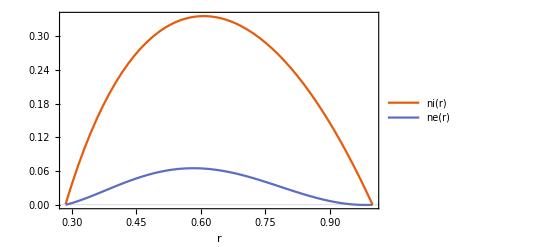

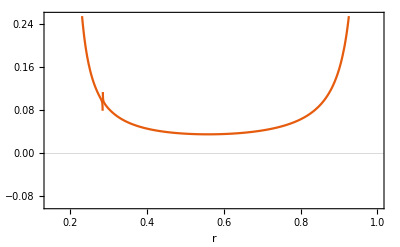

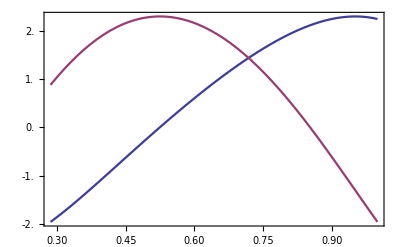

```mathematica
(*-------------------  fixed values  ----------------------*)
Clear[a,b,Γ,Τ,β,Da,Pe,PI,Va,Vb,Te0,H,X0,neC,niC,weC]
ne[r_]:= Da ne1[r]+Da^2 ne2[r];    ni[r_]:= Da ni1[r]+Da^2 ni2[r];
φ[r_]:=Da φ1[r]+Da^2 φ2[r];     Ef[r_]:=Da E1[r]+Da^2 E2[r];   We[r_]:= Da We1[r]+Da^2 We2[r];
(*a=0.5/1.75; b=1;  Va=0;  Vb =-1/Da;   PI=1;     Pe=0.01;     Γ=0.01;     γ=0.01;     β=0.01; X0=0.01; H=0.2; Te0=0.5/Da;    Da=3.3 10^-4; niC =0.6/Da;*)
(*a=0.15/5.23; b=1;  Va=0;  Vb =-77.4/(460Da);   PI=0.05;     Pe=19000;     Γ=45;     γ=0.001;     β=16000; X0=10; H=0.02; Te0=1/Da;    Da=5.5 10^-4; niC =0.001/Da; neC=0.000001/Da; neA=0.000001/Da; weC =neC; weA=neA;*)
a=0.5/1.75; b=1;  Va=0;  Vb =-220/(460Da);   PI=0.1;     Pe=5000;     Γ=32;     γ=0.01;     β=9500; X0=0.000001; H=0.02; Te0=1/Da;    Da=5.5 10^-4; niC =0.001/Da; neC=0.000001/Da; neA=0.000001/Da; weC =neC; weA=neA;
Plot[{ni[r],ne[r]},{r,a,b},AxesLabel->{Automatic},PlotLegends-> "Expressions",PlotTheme->"Scientific"]
(*Plot[{φ[r]},{r,a,b},AxesLabel->{Automatic},PlotLegends-> "Expressions",PlotTheme->"Scientific"]*)
Plot[{We[r]/ne[r]},{r,0.15,b},AxesLabel->{Automatic},PlotLegends-> "Expressions",PlotTheme->"Scientific"]
TwoAxisPlot[{Ef[r],φ[r]},{r,a,b}]
```

```mathematica
□_□
```

```mathematica
0
```

```mathematica
(((□_□)_□)_□)_□
```

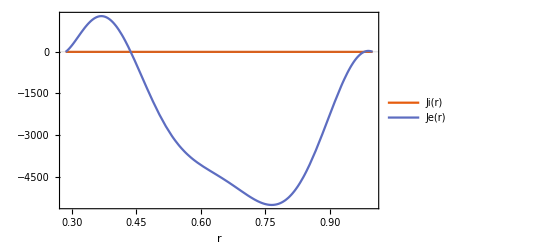

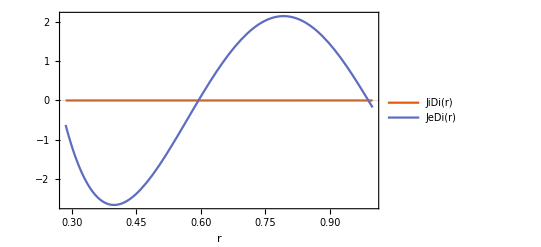

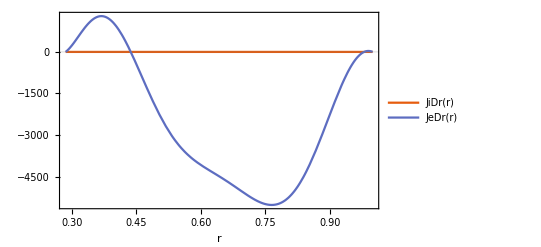

```mathematica
Clear[Ji,Je,JiDi,JeDi,JiDr,JeDr,ue,ui,a,b,Γ,Τ,β,Da,Pe,PI,Va,Vb,Ef,ne,ni,φ]
(*a=1.5/17.5;    b=1;      Vb=-1/Da;     PI=200;     Pe=1.5;     Γ=1;     γ=0.01;      β=1;   niC=0.025/Da;  Da=40 10^-5;*)
Clear[a,b,Γ,Τ,β,Da,Pe,PI,Va,Vb,Te0,H,X0]
ne[r_]:= Da ne1[r]+Da^2 ne2[r];    ni[r_]:= Da ni1[r]+Da^2 ni2[r];
φ[r_]:=Da φ1[r]+Da^2 φ2[r];     Ef[r_]:=Da E1[r]+Da^2 E2[r];   We[r_]:= Da We1[r]+Da^2 We2[r];
a=0.5/1.75; b=1;  Va=0;  Vb =-200/(460Da);   PI=0.002;     Pe=19000;     Γ=45;     γ=0;     β=16000; X0=10; H=-2; Te0=10/Da;    Da=5.5 10^-4; niC =0.001/Da;
JeDi[r_]:=-ne'[r];                                JiDi[r_]:=(-ni'[r])/β; 
JeDr[r_]:=-Pe ne[r]Ef[r];              JiDr[r_]:=PI/β ni[r]Ef[r]; 
Je[r_]:=-Pe ne[r]Ef[r]-ne'[r]; Ji[r_]:=PI/β ni[r]Ef[r]-ni'[r]/β; 
Plot[{Ji[r],Je[r]},{r,a,b},AxesLabel->{Automatic},PlotLegends-> "Expressions",PlotTheme->"Scientific"]
Plot[{JiDi[r],JeDi[r]},{r,a,b},AxesLabel->{Automatic},PlotLegends-> "Expressions",PlotTheme->"Scientific"]
Plot[{JiDr[r],JeDr[r]},{r,a,b},AxesLabel->{Automatic},PlotLegends-> "Expressions",PlotTheme->"Scientific"]
```

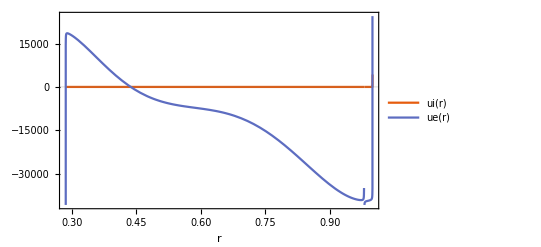

```mathematica
Clear[ue,ui] 
ue[r_]:=Je[r]/ne[r]; ui[r_]:=Ji[r]/ni[r]; 
Plot[{ui[r],ue[r]},{r,a,b},AxesLabel->{Automatic},PlotLegends-> "Expressions",PlotTheme->"Scientific"]
```

```mathematica
SetDirectory["/home/leo/Escritorio/Plasma_analytical_analisis/cyl_paper"](*BBBBBBBBBBBBBBBBBBBBBBBBBBBBBBBBBBBBBBBBBBBBBBBBB*)
Clear[a,b,Γ,Τ,β,Da,Pe,PI,Va,Vb,Te0,H,X0,neC,niC,weC]
ne[r_]:= Da ne1[r]+Da^2 ne2[r];    ni[r_]:= Da ni1[r]+Da^2 ni2[r];
φ[r_]:=Da φ1[r]+Da^2 φ2[r];     Ef[r_]:=Da E1[r]+Da^2 E2[r];   We[r_]:= Da We1[r]+Da^2 We2[r];
(*a=0.5/1.75; b=1;  Va=0;  Vb =-1/Da;   PI=1;     Pe=0.01;     Γ=0.01;     γ=0.01;     β=0.01; X0=0.01; H=0.1; Te0=0.5/Da;    Da=3.3 10^-4; niC =0.6/Da;*)
(*a=0.15/5.23; b=1;  Va=0;  Vb =-77.4/(460Da);   PI=0.1;     Pe=5000;     Γ=32;     γ=0.01;     β=9500; X0=0.000001; H=0.02; Te0=1/Da;    Da=5.5 10^-4; niC =0.001/Da; neC=0.000001/Da; neA=0.000001/Da; weC =neC; weA=neA;*)
a=0.5/1.75; b=1;  Va=0;  Vb =-220/(460Da);   PI=0.1;     Pe=5000;     Γ=32;     γ=0.01;     β=9500; X0=0.000001; H=0.02; Te0=1/Da;    Da=5.5 10^-4; niC =0.001/Da; neC=0.000001/Da; neA=0.000001/Da; weC =neC; weA=neA;

Export["ni_cyl.txt",tb=Table[{r,ni[r]//N},{r,a,b,0.001}],"TSV"];
Export["ne_cyl.txt",tb=Table[{r,ne[r]//N},{r,a,b,0.001}],"TSV"];
(*Export["we_cyl.txt",tb=Table[{r,We[r]//N},{r,a,b,0.001}],"TSV"];*)
Export["Te_cyl.txt",tb=Table[{r,We[r]/ne[r]//N},{r,a,b,0.001}],"TSV"];
Export["E_cyl.txt",tb=Table[{r,Ef[r]//N},{r,a,b,0.001}],"TSV"];
Export["P_cyl.txt",tb=Table[{r,φ[r]//N},{r,a,b,0.001}],"TSV"];
(*Export["JiDi_cyl.txt",tb=Table[{r,JiDi[r]//N},{r,a,b,0.001}],"CSV"];
Export["JeDi_cyl.txt",tb=Table[{r,JeDi[r]//N},{r,a,b,0.001}],"CSV"];
Export["JiDr_cyl.txt",tb=Table[{r,JiDr[r]//N},{r,a,b,0.001}],"CSV"];
Export["JeDr_cyl.txt",tb=Table[{r,JeDr[r]//N},{r,a,b,0.001}],"CSV"];
Export["Ji_cyl.txt",tb=Table[{r,Ji[r]//N},{r,a,b,0.001}],"CSV"];
Export["Je_cyl.txt",tb=Table[{r,Je[r]//N},{r,a,b,0.001}],"CSV"];
Export["ue_cyl.txt",tb=Table[{r,ue[r]//N},{r,a,b,0.001}],"CSV"];
Export["ui_cyl.txt",tb=Table[{r,ui[r]//N},{r,a,b,0.001}],"CSV"];*)
```

/home/leo/Escritorio/Plasma_analytical_analisis/cyl_paper